# Analyse pySCF results

```mathematica
Needs["MaTeX`"]
SetOptions[MaTeX,"Preamble"->{"\\usepackage{amssymb,amsmath,latexsym,amsfonts,amsthm,mathpazo,xcolor,bm,mhchem}"}];
```

```mathematica
ClearAll[plotColors];
plotColors::usage="plotColors[plotType,plotTheme] gives a list of the colors used in a plot when several curves are drawn. Here plotType is, for example, Plot or ListLogPlot while plotTheme may be \"Scientific\", \"Classic\" etc.";

plotColors[plotType_,plotTheme_]:=("DefaultPlotStyle"/. (Method/. Charting`ResolvePlotTheme[plotTheme,plotType]))/. Directive[x_,__]:>x
plotColors[Plot,"Scientific"]
plotColors[Plot,"VibrantColor"]
```

{RGBColor[0.9, 0.36, 0.054],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8],RGBColor[0.71788, 0.568653, 0.],RGBColor[0.70743, 0.224, 0.542415],RGBColor[0.287228, 0.490217, 0.664674],RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636],RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854],RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]}

{RGBColor[0.790588, 0.201176, 0.],RGBColor[0.192157, 0.388235, 0.807843],RGBColor[1., 0.607843, 0.],RGBColor[0., 0.596078, 0.109804],RGBColor[0.567426, 0.32317, 0.729831],RGBColor[0., 0.588235, 0.705882],RGBColor[0.8505, 0.4275, 0.13185],RGBColor[0.499929, 0.285875, 0.775177],RGBColor[0.12490296143062507, 0.63, 0.47103259454284074],RGBColor[0.823948950768196, 0.29474475384097976, 0.19291741323314934],RGBColor[0.42126358105951733, 0.33224185136428963, 0.9],RGBColor[0.7239916650994997, 0.6554435183443889, 0.],RGBColor[0.6746366424582266, 0.252, 0.45055901160272827],RGBColor[0.12582006271512805, 0.5293439498278976, 0.7809840752581536],RGBColor[0.8604677779867332, 0.4773388899336664, 0.10673699943582014]}

```mathematica
Graphics`PlotMarkers[]
```

{{●,10.96},{■,8.96},{◆,10.88},{▲,10.24},{▼,10.24},{○,10.24},{□,10.24},{◇,10.24},{△,11.136},{▽,11.136}}

## State-specific vs state-average

In this section we want to compare the energies of state-specific excited states out of the CAS with their state-averaged counterpart obtained with larger CAS.

#### H_2 6-31G R = 1 bohr

Singlet

```mathematica
Grid[{{"FCI",-1.09897,-0.46395,-0.07450,0.32015,0.57224,0.86353,0.96373,1.46479,1.81277,2.71948},
{"SA (2,2)",-1.07170,-0.43494,,0.33066},
{"SA (3,2)",-1.08924,-0.44196,-0.06164,0.32624,0.61682,0.86876},
{"SS (2,2)",-1.09225,-0.46368,-0.0594551,0.31821,0.61429,0.85673,0.91147,1.45704,1.80747,2.71766},
{"Spurious",-1.08569,,,0.31844,,0.86266,,,,2.70046},
{"Spurious",-1.07871,,,0.31914,,0.86266,,,,2.69883},
{"Spurious",,,,0.32440,,0.86392}}]
```

FCI | -1.09897 | -0.46395 | -0.0745 | 0.32015 | 0.57224 | 0.86353 | 0.96373 | 1.46479 | 1.81277 | 2.71948
SA (2,2) | -1.0717 | -0.43494 |  | 0.33066 |  |  |  |  |  | 
SA (3,2) | -1.08924 | -0.44196 | -0.06164 | 0.32624 | 0.61682 | 0.86876 |  |  |  | 
SS (2,2) | -1.09225 | -0.46368 | -0.0594551 | 0.31821 | 0.61429 | 0.85673 | 0.91147 | 1.45704 | 1.80747 | 2.71766
Spurious | -1.08569 |  |  | 0.31844 |  | 0.86266 |  |  |  | 2.70046
Spurious | -1.07871 |  |  | 0.31914 |  | 0.86266 |  |  |  | 2.69883
Spurious |  |  |  | 0.3244 |  | 0.86392 |  |  |  |

Triplet

```mathematica
Grid[{{"FCI",-0.57616,-0.28180,0.51519,0.62520,1.30761,1.61884},
{"SA (2,2)",-0.57166},
{"SA (3,2)",-0.57406,-0.27990,0.51654},
{"SS (2,2)",-0.57417,-0.27990,0.51638,0.62401,1.30572,1.61685}}]
```

FCI | -0.57616 | -0.2818 | 0.51519 | 0.6252 | 1.30761 | 1.61884
SA (2,2) | -0.57166 |  |  |  |  | 
SA (3,2) | -0.57406 | -0.2799 | 0.51654 |  |  | 
SS (2,2) | -0.57417 | -0.2799 | 0.51638 | 0.62401 | 1.30572 | 1.61685

```mathematica
Grid[{{"FCI",-1.09897,-0.46395,-0.07450,0.32015,0.57224,0.86353,0.96373,1.46479,1.81277,2.71948},
{"SA (2,2)",-0.027269999999999905,-0.02900999999999998,,-0.01051000000000002},
{"SA (3,2)",-0.009730000000000016,-0.021989999999999954,-0.012859999999999996,-0.006089999999999984,-0.044580000000000064,-0.005229999999999957},
{"SS (2,2)",-0.006720000000000059,-0.00026999999999999247,-0.0150449,0.0019399999999999973,-0.04205000000000003,0.006800000000000028,0.05225999999999997,0.007750000000000146,0.005300000000000082,0.0018199999999999328},
{"Spurious",-0.013279999999999959,,,0.0017099999999999893,,0.0008700000000000374,,,,0.019019999999999815},
{"Spurious",-0.020259999999999945,,,0.0010100000000000109,,0.0008700000000000374,,,,0.020649999999999835},
{"Spurious",,,,-0.0042500000000000315,,-0.00039000000000000146}}]
```

FCI | -1.09897 | -0.46395 | -0.0745 | 0.32015 | 0.57224 | 0.86353 | 0.96373 | 1.46479 | 1.81277 | 2.71948
SA (2,2) | -0.02727 | -0.02901 |  | -0.01051 |  |  |  |  |  | 
SA (3,2) | -0.00973 | -0.02199 | -0.01286 | -0.00609 | -0.04458 | -0.00523 |  |  |  | 
SS (2,2) | -0.00672 | -0.00027 | -0.0150449 | 0.00194 | -0.04205 | 0.0068 | 0.05226 | 0.00775 | 0.0053 | 0.00182
Spurious | -0.01328 |  |  | 0.00171 |  | 0.00087 |  |  |  | 0.01902
Spurious | -0.02026 |  |  | 0.00101 |  | 0.00087 |  |  |  | 0.02065
Spurious |  |  |  | -0.00425 |  | -0.00039 |  |  |  |

#### HHe^+ 6-31G R = 1 bohr

Singlet

```mathematica
Grid[{{"FCI",-2.85645014,-1.52909534,-1.11044144,
-0.19680392,0.12856781,0.52755449,0.90076424,1.28841852,1.61685046,2.28166803},
{"SA (2,2)",-2.83419,-1.48430,,,0.15142},
{"SA (3,2)",-2.833062,-1.48204,-1.09687,0.140837,0.51860,0.90306},
{"SS (2,2)",-2.854060,-1.526770,-1.107470,-0.168580,0.125830,0.496420,0.893030,1.276360,1.608660,2.273820},
{"Spurious",-2.839230,,,,0.140690,,0.895850,,,2.268110},
{"Spurious",-2.836570,,,,0.142700,,0.901470,,,2.262290}}]
```

FCI | -2.85645 | -1.5291 | -1.11044 | -0.196804 | 0.128568 | 0.527554 | 0.900764 | 1.28842 | 1.61685 | 2.28167
SA (2,2) | -2.83419 | -1.4843 |  |  | 0.15142 |  |  |  |  | 
SA (3,2) | -2.83306 | -1.48204 | -1.09687 | 0.140837 | 0.5186 | 0.90306 |  |  |  | 
SS (2,2) | -2.85406 | -1.52677 | -1.10747 | -0.16858 | 0.12583 | 0.49642 | 0.89303 | 1.27636 | 1.60866 | 2.27382
Spurious | -2.83923 |  |  |  | 0.14069 |  | 0.89585 |  |  | 2.26811
Spurious | -2.83657 |  |  |  | 0.1427 |  | 0.90147 |  |  | 2.26229

```mathematica
Grid[{{"FCI",-1.69996415,-1.25508002,-0.54824936, 0.39116857,1.03084791,1.45633305},
{"SA (2,2)",-1.69173},
{"SA (3,2)",-1.69644,-1.25179,,0.395533},
{"SS (2,2)",-1.699250,-1.253780,-0.548200,0.39112,1.029500,1.455590}}]
```

FCI | -1.69996 | -1.25508 | -0.548249 | 0.391169 | 1.03085 | 1.45633
SA (2,2) | -1.69173 |  |  |  |  | 
SA (3,2) | -1.69644 | -1.25179 |  | 0.395533 |  | 
SS (2,2) | -1.69925 | -1.25378 | -0.5482 | 0.39112 | 1.0295 | 1.45559

## Investigation of spurious solutions

### H_2 6-31G R=1 bohr

```mathematica
{{+x,+x,+x,-x},{+y,+y,-y,+y},{+x,-x,-x,-x},{+y,-y,+y,+y}}//MatrixForm
```

(x | x | x | -x
y | y | -y | y
x | -x | -x | -x
y | -y | y | y)

#### Ground state

NRJ = -1.092251

This is the natural orbitals

```mathematica
{{0.365106,1.05359,-0.906553,-0.668231},{0.212903,+0.553914,2.87481,0.6739461},{0.365106,-1.05359,0.906553,-0.668231},{0.212903,-0.553914,-2.87481,+0.673946}}//MatrixForm
```

(0.365106 | 1.05359 | -0.906553 | -0.668231
0.212903 | 0.553914 | 2.87481 | 0.673946
0.365106 | -1.05359 | 0.906553 | -0.668231
0.212903 | -0.553914 | -2.87481 | 0.673946)

The occupations in the natural orbital basis are

```mathematica
{1.98867,0.0113322,0,0}
```

The energies of the natural orbitals are

```mathematica
{-0.664181,1.06149,0.682858,1.0121}
```

NRJ = -1.085686

This is the natural orbitals

```mathematica
{{0.359173, 0.671438, 0.0813971,-1.38754},
{0.218864,-0.672034, 2.45086, 1.60145},
{0.359173, 0.671438,-0.0813971, 1.38754},
{0.218864,-0.672034,-2.45086,-1.60145}}//MatrixForm
```

(0.359173 | 0.671438 | 0.0813971 | -1.38754
0.218864 | -0.672034 | 2.45086 | 1.60145
0.359173 | 0.671438 | -0.0813971 | 1.38754
0.218864 | -0.672034 | -2.45086 | -1.60145)

The occupations in the natural orbital basis are

```mathematica
{1.99255,0.0074516,0,0}
```

The energies of the natural orbitals are

```mathematica
{-0.669817,0.678543,0.289852,1.77742}
```

NRJ = -1.078710
This is the diagonalized DM1 at convergence

This is the natural orbitals

```mathematica
{{0.36202,-0.602429,-0.669908, 1.25258},
{0.216009, 2.92013, 0.672957,-0.210288},
{0.36202, 0.602429,-0.669908,-1.25258},
{0.216009,-2.92013, 0.672957, 0.210288}}//MatrixForm
```

(0.36202 | -0.602429 | -0.669908 | 1.25258
0.216009 | 2.92013 | 0.672957 | -0.210288
0.36202 | 0.602429 | -0.669908 | -1.25258
0.216009 | -2.92013 | 0.672957 | 0.210288)

The occupations in the natural orbital basis are

```mathematica
{1.99983,0.000169736,0,0}
```

The energies of the natural orbitals are

```mathematica
{-0.669125,0.641484,0.681496,1.43094}
```

#### First closed-shell doubly excited state

NRJ =0.31821

This is the natural orbitals

```mathematica
{{-0.281607,-1.3611,-0.401043,-0.647301},
{-2.19293, 1.9397,-0.175792, 0.684564},
{0.281607, 1.3611,-0.401043,-0.647301},
{2.19293,-1.9397,-0.175792, 0.684564}}//MatrixForm
```

(-0.281607 | -1.3611 | -0.401043 | -0.647301
-2.19293 | 1.9397 | -0.175792 | 0.684564
0.281607 | 1.3611 | -0.401043 | -0.647301
2.19293 | -1.9397 | -0.175792 | 0.684564)

The occupations in the natural orbital basis are

```mathematica
{1.9972, 0.00279502,0,0}
```

The energies of the natural orbitals are

```mathematica
{-0.133917, 1.31908,-0.54568, 0.449245}
```

NRJ =0.31844

This is the natural orbitals

```mathematica
{{-0.277471,-0.716084,-0.258956,-1.36195},
{-2.19881, 0.633607,-0.313167, 1.93303},
{0.277471,-0.716084,-0.258956, 1.36195},
{2.19881, 0.633607,-0.313167,-1.93303}}//MatrixForm
```

(-0.277471 | -0.716084 | -0.258956 | -1.36195
-2.19881 | 0.633607 | -0.313167 | 1.93303
0.277471 | -0.716084 | -0.258956 | 1.36195
2.19881 | 0.633607 | -0.313167 | -1.93303)

The occupations in the natural orbital basis are

```mathematica
{1.98648, 0.0135248, 0, 0}
```

The energies of the natural orbitals are

```mathematica
{-0.132394, 0.403299,-0.50416, 1.31963}
```

NRJ =0.31914

This is the natural orbitals

```mathematica
{{0.280113,-0.10469, 0.335496,-1.51978},
{2.19859, 0.540926, 0.161099, 1.97953},
{-0.278491, 1.35695, 0.0899701, 0.764693},
{-2.19374,-1.53847, 0.540362,-1.26472}}//MatrixForm
```

(0.280113 | -0.10469 | 0.335496 | -1.51978
2.19859 | 0.540926 | 0.161099 | 1.97953
-0.278491 | 1.35695 | 0.0899701 | 0.764693
-2.19374 | -1.53847 | 0.540362 | -1.26472)

The occupations in the natural orbital basis are

```mathematica
{1.99551, 0.00448588, 0, 0}
```

The energies of the natural orbitals are

```mathematica
{-0.133845, 0.623544,-0.460393, 1.05732}
```

NRJ =0.3244

This is the natural orbitals

```mathematica
{{0.270162, 0.668396,-0.364803,-1.36341},
{2.20915,-0.185214, 0.682075, 1.92121},
{-0.270162, 0.668396,-0.364803, 1.36341},
{-2.20915,-0.185214, 0.682075,-1.92121}}//MatrixForm
```

(0.270162 | 0.668396 | -0.364803 | -1.36341
2.20915 | -0.185214 | 0.682075 | 1.92121
-0.270162 | 0.668396 | -0.364803 | 1.36341
-2.20915 | -0.185214 | 0.682075 | -1.92121)

The occupations in the natural orbital basis are

```mathematica
{1.99282, 0.00718333, 0, 0}
```

The energies of the natural orbitals are

```mathematica
{-0.133759,-0.309654, 0.205176, 1.31829}
```

#### HHe^+ 6-31G R=1 bohr

```mathematica
IndexR1S={{-2.854060,0},{-2.839230,1},{-2.836570,2},{-1.526770,2},{-1.107470,3},{-0.168580,4.000000},{0.125830,2.000000},{0.140690,3.000000},{0.142700,3.000000},{0.496420,4.000000},{0.893030,4},{0.895850,4},{0.901470,5},{1.276360,5},{1.608660,6},{2.262290,5},{2.268110,6},{2.273820,7}};
IndexR1T = {{-1.699250,1.000000},{-1.253780,2.000000},{-0.548200,3.000000},{0.391120,3.000000},{1.029500,4.000000},{1.455590,5.000000}};
```

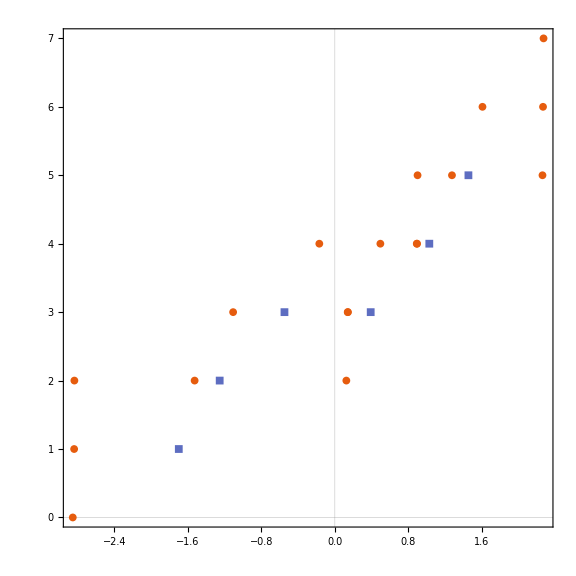

```mathematica
ListPlot[{IndexR1S,IndexR1T},PlotTheme->"Scientific",FrameStyle->Directive[Thick,16,Black],FrameLabel->{MaTeX["E / E_{\\text{h}}",FontSize->18],MaTeX["\\text{Hessian index}",FontSize->18]},PlotMarkers->{Automatic, 8},ImageSize->Large,AspectRatio-> 1,PlotLegends->Placed[{MaTeX["\\text{Singlet}",FontSize->18], MaTeX["\\text{Triplet}",FontSize->18]},{Left,Top}]]
```

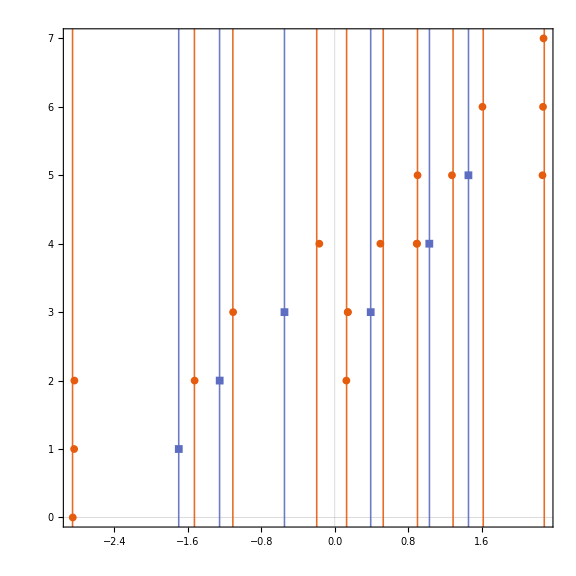

```mathematica
lineStyleS={Thickness@0.002,RGBColor[0.9, 0.36, 0.054],Opacity[0.9]};
FCINRJS= {-2.85645014,-1.52909534,-1.11044144,
-0.19680392,0.12856781,0.52755449,0.90076424,1.28841852,1.61685046,2.28166803};
lineS=Table[Line[{{FCINRJS⟦i⟧,-1},{FCINRJS⟦i⟧,8}}],{i,1,10}];
lineStyleT={Thickness@0.002,RGBColor[0.365248, 0.427802, 0.758297],Opacity[0.9]};
FCINRJT= {-1.69996415,-1.25508002,-0.54824936, 0.39116857,1.03084791,1.45633305};
lineT=Table[Line[{{FCINRJT⟦i⟧,-1},{FCINRJT⟦i⟧,8}}],{i,1,6}];
ListPlot[{IndexR1S,IndexR1T},PlotTheme->"Scientific",FrameStyle->Directive[Thick,16,Black],FrameLabel->{MaTeX["E / E_{\\text{h}}",FontSize->18],MaTeX["\\text{Hessian index}",FontSize->18]},PlotMarkers->{Automatic, 8},ImageSize->Large,AspectRatio-> 1,PlotLegends->Placed[{MaTeX["\\text{Singlet}",FontSize->18], MaTeX["\\text{Triplet}",FontSize->18]},{Right,Bottom}],Epilog->{{Directive[lineStyleS],lineS},{Directive[lineStyleT],lineT}}]
```

### H_2 6-31G R=10 bohr

Two solutions are converging to the ground state dissociation limit, namely the true ground state and the lowest triplet. Both solutions have a zero eigenvalue and 6 positive eigenvalues.
The triplet does not share the share the same orbitals as they are symmetry-broken.
Now we have a look at the spurious ground state solutions. The two solutions have an occupation close to two in the fully symmetric orbital and are slightly correlated using the two higher orbitals.
However, these orbitals those not have the correct symmetry to lower the energy as for the first solution.
 The ground-state Hartree-Fock solution at R=10 has an energy equal to -0.724162474244585.
 There are two spurious solutions of the first closed shell which have almost the same energy, they correspond to the σu with an occupation close to 2 and the same virtual orbitals to correlate.
 Above one state which is well defined and another one which is symmetry broken with a lot of spurious solutions similar to the one at R=1.
The “alone” one correspond to occ2 sb correlated with a sb on the same side whereas the other one is correlated with a sb on the other orbital. We observe the same phenomena for a higher states.
The second group of spurious solutions come from the two middle closed shell at R=1, their occupation are all 1-1, while the last group of spurious solutions is analogous to the first one (occ2) but with the two other orbitals occupied.
There is also a singlet degenerate with a triplet, we obtain a degenerate solution with spin symmetry broken.
Finally, there is two maxima, one with 1-1 and sp orbitals and one with 2-0 and sb orbitals.

#### Ground-state S and T

NRJ = -0.996465844670532

This is the natural orbitals

```mathematica
{{0.302064, 0.302414, 0.889339, 0.889456},
{0.470651, 0.470436,-0.812636,-0.813359},
{0.302064,-0.302414, 0.889339,-0.889456},
{0.470651,-0.470436,-0.812636, 0.813359}}//MatrixForm
```

(0.302064 | 0.302414 | 0.889339 | 0.889456
0.470651 | 0.470436 | -0.812636 | -0.813359
0.302064 | -0.302414 | 0.889339 | -0.889456
0.470651 | -0.470436 | -0.812636 | 0.813359)

The occupations in the natural orbital basis are

```mathematica
{1.00134, 0.998656, 0, 0}
```

The energies of the natural orbitals are

```mathematica
{-0.184122,-0.183632, 0.993646, 0.9951661}
```

This is the CI vector in the natural orbital basis

```mathematica
{0.707582,0, 0,-0.706631}
```

NRJ = -0.996465844670532

This is the natural orbitals

```mathematica
{{0.336051, 0.264134, 0.889329,-0.889466},
{0.522918, 0.411558,-0.812652, 0.813343},
{-0.264455, 0.335798, 0.889329, 0.889466},
{-0.411381, 0.523057,-0.812652,-0.813343}}//MatrixForm
```

(0.336051 | 0.264134 | 0.889329 | -0.889466
0.522918 | 0.411558 | -0.812652 | 0.813343
-0.264455 | 0.335798 | 0.889329 | 0.889466
-0.411381 | 0.523057 | -0.812652 | -0.813343)

The occupations in the natural orbital basis are

```mathematica
{1, 1, 0, 0}
```

The energies of the natural orbitals are

```mathematica
{-0.183711,-0.184044, 0.993639, 0.995172}
```

This is the CI vector in the natural orbital basis

```mathematica
{0, 0.707107,-0.707107, 0}
```

#### First group of 4 spurious solutions

NRJ = -0.750841  1  6

This is the natural orbitals

```mathematica
{{0.227779, 0.911199,-0.227001,-0.911625},
{0.535991,-0.771105,-0.536783, 0.771185},
{0.227779, 0.911199, 0.227001, 0.911625},
{0.535991,-0.771105, 0.536783,-0.771185}}//MatrixForm
```

(0.227779 | 0.911199 | -0.227001 | -0.911625
0.535991 | -0.771105 | -0.536783 | 0.771185
0.227779 | 0.911199 | 0.227001 | 0.911625
0.535991 | -0.771105 | 0.536783 | -0.771185)

The occupations in the natural orbital basis are

```mathematica
{1.99718, 0.00281566, 0, 0}
```

The energies of the natural orbitals are

```mathematica
{-0.255797, 0.982405,-0.155573, 0.984045}
```

This is the CI vector in the natural orbital basis

```mathematica
{0.999296,0, 0,-0.0375211}
```

NRJ = -0.750104  1  6

This is the natural orbitals

```mathematica
{{-0.228216 0.91132-0.226574 0.9115
-0.535754-0.771901-0.537011-0.770395
0.228216-0.91132-0.226574 0.9115
0.535754 0.771901-0.537011-0.770395}}//MatrixForm
```

(0.226694 | -0.775072 | 0.531358 | -0.911149
0.536889 | 0.910375 | 0.233333 | 0.770248
0.226718 | 0.774578 | -0.531155 | -0.911784
0.536911 | -0.909919 | -0.233567 | 0.770699)

The occupations in the natural orbital basis are

```mathematica
{1.99719 0.00281213 0 0}
```

The energies of the natural orbitals are

```mathematica
{-0.255311 0.984086-0.155822 0.982734}
```

This is the CI vector in the natural orbital basis

```mathematica
{0.999297-2.22045e-16 1.21431e-16-0.0374976}
```

NRJ = -0.749062 2 5

This is the natural orbitals

```mathematica
{{0.226706-0.774823 0.531258 0.911467
0.536899 0.910146 0.233449-0.770473
0.226706 0.774823-0.531258 0.911467
0.536899-0.910146-0.233449-0.770473}}//MatrixForm
```

(0.226694 | -0.775072 | 0.531358 | -0.911149
0.536889 | 0.910375 | 0.233333 | 0.770248
0.226718 | 0.774578 | -0.531155 | -0.911784
0.536911 | -0.909919 | -0.233567 | 0.770699)

The occupations in the natural orbital basis are

```mathematica
{1.99884 0.00115557 0 0}
```

The energies of the natural orbitals are

```mathematica
{-0.256275 0.844579-0.0167718 0.982336}
```

This is the CI vector in the natural orbital basis

```mathematica
{0.999711 1.38778e-16-7.37257e-17-0.0240372}
```

NRJ =-0.748326 2 5

This is the natural orbitals

```mathematica
{{-0.227147-0.774193 0.531782 0.911587
-0.536659 0.909776 0.232803-0.771272
0.227147-0.774193 0.531782-0.911587
0.536659 0.909776 0.232803 0.771272}}//MatrixForm
```

(0.226694 | -0.775072 | 0.531358 | -0.911149
0.536889 | 0.910375 | 0.233333 | 0.770248
0.226718 | 0.774578 | -0.531155 | -0.911784
0.536911 | -0.909919 | -0.233567 | 0.770699)

The occupations in the natural orbital basis are

```mathematica
{1.99884 0.00116079 0 0}
```

The energies of the natural orbitals are

```mathematica
{-0.255787 0.842468-0.0162175 0.984016}
```

This is the CI vector in the natural orbital basis

```mathematica
{0.99971 2.77556e-16-3.40006e-16-0.0240914}
```

#### Two singlets

NRJ = -0.531378  1  6

This is the natural orbitals

```mathematica
{{-0.00110352-0.00236223-0.427426 1.2578
0.000529419 0.00101976-0.665453-1.14975
0.246113-1.30544 0.00105456-0.00221019
0.820674 1.04462-0.00112999 0.0028055}}//MatrixForm
```

The occupations in the natural orbital basis are

```mathematica
{1.9914 0.00859932 0 0}
```

The energies of the natural orbitals are

```mathematica
{-0.0409338 1.3885-0.398231 0.560941}
```

This is the CI vector in the natural orbital basis

```mathematica
{0.997848 1.18208e-11-1.18208e-11-0.0655718}
```

```mathematica
NUMBER 7
```

```mathematica
This is the natural orbitals

0.00843214 0.263611 1.30016-0.0691416
0.00699346 0.612099-0.983062 0.650867
-0.242251-0.762367 0.211095 1.03938
-0.823662 0.619452-0.163483-0.822124

The occupations in the natural orbital basis are

1.97385 0.026149 0 0

The energies of the natural orbitals are

-0.0447492 0.217133 0.553278 0.782833

This is the CI vector in the natural orbital basis

0.99148-0.0623993 0.0623993-0.0958165
```

```mathematica
NUMBER 4
```

```mathematica
This is the natural orbitals

0.169974 0.167428 0.921876 0.926269
0.586393 0.582706-0.732892-0.737713
-0.168675 0.168737 0.92627-0.921875
-0.58187 0.587222-0.736391 0.73422

The occupations in the natural orbital basis are

1.00116 0.998837 0 0

The energies of the natural orbitals are

-0.211153-0.211288 0.962839 0.96444

This is the CI vector in the natural orbital basis

-0.707518 7.35523e-16-7.35523e-16-0.706696
```

```mathematica
NUMBER 17
```

```mathematica
This is the natural orbitals

0.00107262 0.238589 1.30684-0.0013133
-0.000611938 0.826679-1.03988 0.000658955
-0.238585 0.000853473 0.00103302 1.30684
-0.826681-0.000656779 0.000241972-1.03988

The occupations in the natural orbital basis are

1.95943 0.0405681 0 0

The energies of the natural orbitals are

-0.0515401-0.370901 0.557529 1.36975

This is the CI vector in the natural orbital basis

0.989806 3.57436e-13-3.57339e-13-0.142422
```

```mathematica
NUMBER 26
```

```mathematica
This is the natural orbitals

0.238585 0.00254905 0.00210341 1.30684
0.826681-0.00211311-0.000498225-1.03988
-0.00123067-0.238585 1.30684-0.00173365
0.000675266-0.826679-1.03988 0.00365149

The occupations in the natural orbital basis are

1.72554 0.274463 0 0

The energies of the natural orbitals are

-0.0904674-0.331969 0.656531 1.27074

This is the CI vector in the natural orbital basis

0.928853 0 8.32667e-17-0.370448
```

```mathematica
NUMBER 33
```

```mathematica
This is the natural orbitals

0.238585-0.00135085 0.924117 0.924033
0.826681 0.000965289-0.734417-0.736195
-0.00135085 0.238585 0.924155-0.923995
0.000965288 0.826681-0.734447 0.736165

The occupations in the natural orbital basis are

1 1 0 0

The energies of the natural orbitals are

-0.21122-0.21122 0.962788 0.964489

This is the CI vector in the natural orbital basis

-0.707107-5.71104e-10-5.90301e-11 0.707107
```

#### Symmetry broken 1

```mathematica
NUMBER 219
```

```mathematica
This is the natural orbitals

-0.302838-0.301638-0.000350692-1.2578
-0.470569-0.470519-0.000108056 1.14975
-0.889008 0.889786 0.427431 0.000875419
0.812444-0.813551 0.665448-0.00120279

The occupations in the natural orbital basis are

1.00147 0.998528 0 0

The energies of the natural orbitals are

0.298845 0.299386 0.0352368 0.994408

This is the CI vector in the natural orbital basis

0.707627-2.69147e-11 2.68897e-11-0.706586
```

#### Second group of spurious solution

#### Symmetry broken 2

```mathematica
NUMBER 205
```

```mathematica
This is the natural orbitals

-0.804177 1.05738-0.000103077 0.00139489
1.32534-0.0907134 0.000358569 0.00123347
-0.000994062-0.00276948 0.427429 1.2578
0.000321484 0.00242994 0.66545-1.14975

The occupations in the natural orbital basis are

1.22987 0.770132 0 0

The energies of the natural orbitals are

0.661591 0.718504-0.398231 0.560936

This is the CI vector in the natural orbital basis

0.784177-1.02106e-10 1.02106e-10-0.620537
```

#### Singlet degenerate with triplet

```mathematica
NUMBER 286
```

```mathematica
This is the natural orbitals

-0.889845 0.888946-0.300572 0.30391
0.811845-0.81415-0.472014 0.469067
-0.889845-0.888946-0.300572-0.30391
0.811845 0.81415-0.472014-0.469067

The occupations in the natural orbital basis are

1.00265 0.997351 0 0

The energies of the natural orbitals are

0.781616 0.782599 0.0346844 0.0357949

This is the CI vector in the natural orbital basis

-0.708043-8.89639e-07 8.89639e-07 0.70617
```

#### Third group of spurious solutions

#### Degenerate solutions + maximum

```mathematica
NUMBER 1520
```

```mathematica
This is the natural orbitals

-0.00134407-0.00372179 0.42743-1.25779
0.00153088 0.00384301 0.66545 1.14974
1.32515-0.0933775-9.80076e-05-0.000840281
-0.942627-0.936053 0.000291024 0.00336834

The occupations in the natural orbital basis are

1.99457 0.00543146 0 0

The energies of the natural orbitals are

1.18623 0.481611-0.398232 0.560931

This is the CI vector in the natural orbital basis

-0.998641-5.31014e-12 5.31015e-12-0.0521127
```

```mathematica
NUMBER 1152
```

```mathematica
This is the natural orbitals

0.937364-0.937603-0.0588264-0.0595213
-0.662119 0.661244-0.668007-0.665489
-0.93777-0.937196-0.0586392 0.0597058
0.662406 0.660957-0.665913 0.667584

The occupations in the natural orbital basis are

1.00367 0.99633 0 0

The energies of the natural orbitals are

0.842961 0.841871 0.0757261 0.0761399

This is the CI vector in the natural orbital basis

-0.708403 2.77556e-16-2.22045e-16-0.705808
```

```mathematica
NUMBER 878
```

```mathematica
This is the natural orbitals

0.00176706-1.32579 0.0836999-0.00475831
-0.00184844 0.935761 0.942914 0.00390849
-1.3258-0.0017832-0.000499084 0.0836783
0.935759-0.00264875-0.000478345 0.942921

The occupations in the natural orbital basis are

1.97379 0.0262081 0 0

The energies of the natural orbitals are

1.18038 0.504464-0.321953 0.473812

This is the CI vector in the natural orbital basis

-0.993426 2.77556e-16-4.51028e-16-0.114473
```

```mathematica
NUMBER 101
```

```mathematica
This is the natural orbitals

0.0013018 1.32579-0.0836906-0.0039846
-0.00148356-0.935754-0.94292 0.0042632
-1.3258 0.000752494 0.000283705-0.0836871
0.935759-0.00335764-0.00137049-0.942919

The occupations in the natural orbital basis are

1.99887 0.00112616 0 0

The energies of the natural orbitals are

1.18908 0.495748-0.332199 0.484068

This is the CI vector in the natural orbital basis

-0.999718 2.77556e-16-1.96891e-16-0.0237293
```

### H_2 6-311G R=1 bohr

NRJ = -1.092251 with index 0

NRJ = -1.08866 with index 1

NRJ = -1.08074 with index 2

NRJ = -1.08033 with index 3

NRJ = -1.08026 with index 4

There are 6 group of close lying solutions (5-6 sol) corresponding to the 6 closed-shell -> expected.

```mathematica
Subscript[H, 2] 6-31G R=1 bohr
```

```mathematica
Subscript[H, 2] 6-31G R=1 bohr
```

### H_2 6-31G (3,2) R=1 bohr

## Index

### H_2 6-31G R=1 bohr

```mathematica
IndexR1S={{-1.092251,0},{-1.085686,1},{-1.078710,2},{-0.463689,2},{-0.059455,3},{0.318210,2},{0.318443,2},{0.319142,3},{0.324402,3},{0.614298,4},{0.856736,4},{0.862663,4},{0.862663,5},{0.863920,5},{0.911471,4},{1.457043,5},{1.807471,6},{2.698833,5},{2.700456,6},{2.717660,7}};
IndexR1T = {{-0.57417,1},{-0.27990,2},{0.51638,3},{0.62401,3},{1.30572,4},{1.61685,5}};
```

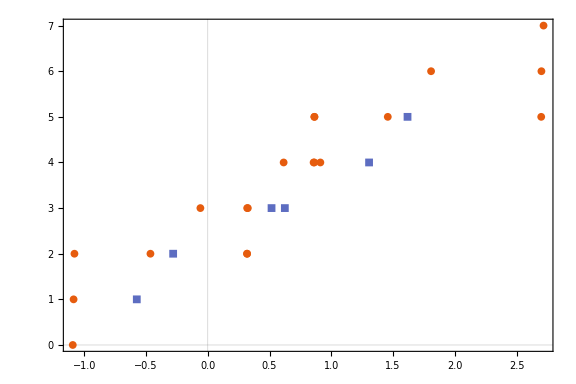

```mathematica
ListPlot[{IndexR1S,IndexR1T},PlotTheme->"Scientific",FrameStyle->Directive[Thick,16,Black],FrameLabel->{MaTeX["E / E_{\\text{h}}",FontSize->18],MaTeX["\\text{Hessian index}",FontSize->18]},PlotMarkers->{Automatic, 8},ImageSize->Large,AspectRatio-> 2/3,PlotLegends->Placed[{MaTeX["\\text{Singlet}",FontSize->18], MaTeX["\\text{Triplet}",FontSize->18]},{Left,Top}]]
```

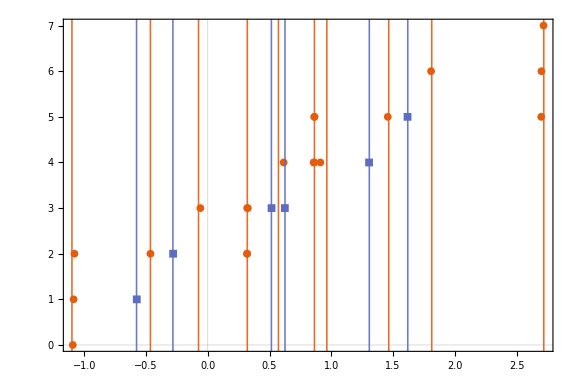

```mathematica
lineStyleS={Thickness@0.002,RGBColor[0.9, 0.36, 0.054],Opacity[0.9]};
FCINRJS= {-1.09897,-0.46395,-0.07450,0.32015,0.57224,0.86353,0.96373,1.46479,1.81277,2.71948};
lineS=Table[Line[{{FCINRJS⟦i⟧,-1},{FCINRJS⟦i⟧,8}}],{i,1,10}];
lineStyleT={Thickness@0.002,RGBColor[0.365248, 0.427802, 0.758297],Opacity[0.9]};
FCINRJT= {-0.57616,-0.28180,0.51519,0.62520,1.30761,1.61884};
lineT=Table[Line[{{FCINRJT⟦i⟧,-1},{FCINRJT⟦i⟧,8}}],{i,1,6}];
ListPlot[{IndexR1S,IndexR1T},PlotTheme->"Scientific",FrameStyle->Directive[Thick,16,Black],FrameLabel->{MaTeX["E / E_{\\text{h}}",FontSize->18],MaTeX["\\text{Hessian index}",FontSize->18]},PlotMarkers->{Automatic, 8},ImageSize->Large,AspectRatio-> 2/3,PlotLegends->Placed[{MaTeX["\\text{Singlet}",FontSize->18], MaTeX["\\text{Triplet}",FontSize->18]},{0.9,0.1}],Epilog->{{Directive[lineStyleS],lineS},{Directive[lineStyleT],lineT}}]
```

### H_2 6-31G R=5 bohr

```mathematica
IndexR5S={{-0.999277, 0.000000}, {-0.845951, 1.000000}, {-0.843857, 2.000000}, {-0.744470, 1.000000}, {-0.742351, 2.000000}, {-0.623886, 1.000000}, {-0.619583, 2.000000}, {-0.619472, 2.000000}, {-0.618256, 2.000000}, {-0.616667, 3.000000}, {-0.616264, 3.000000}, {-0.614638, 3.000000}, {-0.610001, 3.000000}, {-0.022836, 3.000000}, {0.164132, 4.000000},{0.214391, 4.000000}, {0.261495, 4.000000}, {0.344862, 4.000000}, {0.491496, 5.000000}, {0.938553, 4.000000}, {0.938898, 5.000000},{1.084746, 4.000000}, {1.087013, 5.000000}, {1.320893, 4.000000}, {1.323359, 5.000000}, {1.513702, 6.000000}, {1.523757, 5.000000}, {1.523907, 6.000000}, {1.528046, 6.000000}, {1.530433, 7.000000},{1.534666, 7.000000}};
IndexR5T = {{-0.994938, 1.000000},{-0.040345, 2.000000},{0.022261, 3.000000}, {0.061010, 3.000000}, {0.151292, 3.000000},{0.193813, 3.000000},{0.254615, 4.000000},{0.950253, 5.000000}};
```

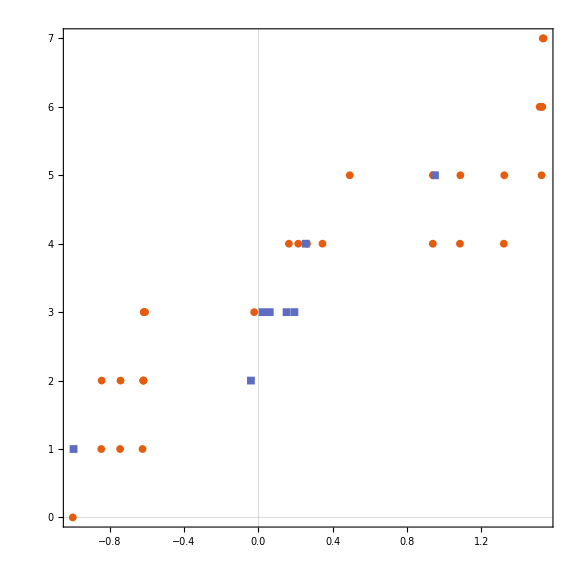

```mathematica
ListPlot[{IndexR5S,IndexR5T},PlotTheme->"Scientific",FrameStyle->Directive[Thick,16,Black],FrameLabel->{MaTeX["E / E_{\\text{h}}",FontSize->18],MaTeX["\\text{Hessian index}",FontSize->18]},PlotMarkers->{Automatic, 8},ImageSize->Large,AspectRatio-> 1,PlotLegends->Placed[{MaTeX["\\text{Singlet}",FontSize->18], MaTeX["\\text{Triplet}",FontSize->18]},{Left,Top}]]
```

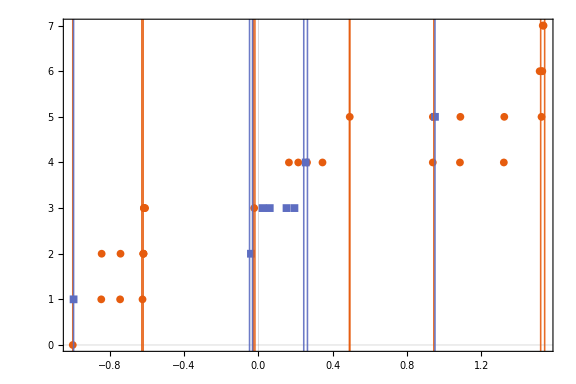

```mathematica
lineStyleS={Thickness@0.002,RGBColor[0.9, 0.36, 0.054],Opacity[0.9]};
FCINRJS= {-0.9992919114810179,-0.6273876294001275,-0.6205128273742646,-0.028192424699643837,-0.018915471201385425,0.48966181875716425,0.4920217589644312,0.9442371114741557,1.519199406940787,1.540682121141402};
lineS=Table[Line[{{FCINRJS⟦i⟧,-1},{FCINRJS⟦i⟧,8}}],{i,1,10}];
lineStyleT={Thickness@0.002,RGBColor[0.365248, 0.427802, 0.758297],Opacity[0.9]};
FCINRJT= {-0.9949383967933529,-0.04779406150091042,-0.03179105336387339,0.24396093203151487,0.2638685635069456,0.9502535625494835};
lineT=Table[Line[{{FCINRJT⟦i⟧,-1},{FCINRJT⟦i⟧,8}}],{i,1,6}];
ListPlot[{IndexR5S,IndexR5T},PlotTheme->"Scientific",FrameStyle->Directive[Thick,16,Black],FrameLabel->{MaTeX["E / E_{\\text{h}}",FontSize->18],MaTeX["\\text{Hessian index}",FontSize->18]},PlotMarkers->{Automatic, 8},ImageSize->Large,AspectRatio-> 2/3,PlotLegends->Placed[{MaTeX["\\text{Singlet}",FontSize->18], MaTeX["\\text{Triplet}",FontSize->18]},{0.9,0.1}],Epilog->{{Directive[lineStyleS],lineS},{Directive[lineStyleT],lineT}}]
```

## Dependance on the size of the basis set

In this section we want to look at the number of CASSCF solution as a function of the size of the basis set.

#### H_2

R = 1 bohr with 25000 Newton-Raphson with stochastic starting point on the grid .

```mathematica
Grid[{{"Basis","STO-3G","6-31G","6-311G","6-311++G","6-31G**","6-311G**"},{"","1s","2s","3s","4s","2s1p","3s1p"},{"Nb orb",1,2,3,4,5,6},{"Nb sol",4,26,60,114,141,214}}]
```

Basis | STO-3G | 6-31G | 6-311G | 6-311++G | 6-31G** | 6-311G**
 | 1s | 2s | 3s | 4s | 2s1p | 3s1p
Nb orb | 1 | 2 | 3 | 4 | 5 | 6
Nb sol | 4 | 26 | 60 | 114 | 141 | 214

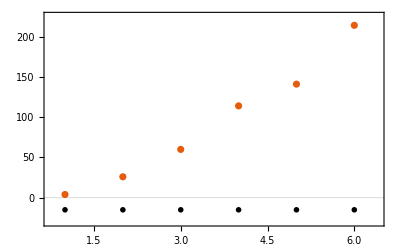

```mathematica
ListPlot[{{1,4},{2,26},{3,60},{4,114},{5,141},{6,214}},PlotTheme->"Scientific",ImageSize->400,FrameStyle->Directive[Thick,16,Black],PlotRange->{{0.75,6.4},{-30,225}},FrameLabel->{MaTeX["\\text{Number of basis functions}",FontSize->18],MaTeX["\\text{Number of solutions}",FontSize->18]},Epilog->{Inset[MaTeX["[1s]",FontSize->16],{1,-15}],Inset[MaTeX["[2s]",FontSize->16],{2,-15}],Inset[MaTeX["[3s]",FontSize->16],{3,-15}],Inset[MaTeX["[4s]",FontSize->16],{4,-15}],Inset[MaTeX["[2s1p]",FontSize->16],{5,-15}],Inset[MaTeX["[3s1p]",FontSize->16],{6,-15}]}]
```

## Dependance on the geometry of the system

In this section we want to look at the number of CASSCF solution as a function of the geometry of the system .

### H_2 STO-3G

```mathematica
NRJH2STO3G ={{0.2,2.422302 ,4.290274, 4.602762, 6.526159},{0.4,0.024958, 1.680155, 1.996665 ,3.706215},{0.6,-0.676511, 0.717897, 1.040717, 2.488022},{0.8,-0.957599, 0.186929 ,0.517888, 1.713710},{1,-1.078970,-0.15026,0.190222, 1.168500},{1.2,-1.126699,-0.376423,-0.025358, 0.772453},{1.4,-1.137276,-0.531808,-0.169292, 0.481138},
{1.6,-1.128816,-0.640549,-0.265820, 0.264182},{1.8,-1.110846,-0.718277,-0.330663, 0.099824},{2,-1.088496,-0.774967,-0.373922,-0.026696},{2.5,-1.030474,-0.860389,-0.424515,-0.231464},{3,-0.985157,-0.900675,-0.430440,-0.331819},{4,-0.943778,-0.92733,-0.397076,-0.376329},{5,-0.934889,-0.93227,-0.356806,-0.353220},{6,-0.933402,-0.93305,-0.325013,-0.324509},{7,-0.933191,-0.93315,-0.301395,-0.301338},{8,-0.933166,-0.933166,-0.283556,-0.283551},{9,-0.933164,-0.933164,-0.269669,-0.269668},{10,-0.933164,-0.933164,-0.258558,-0.258558},{11,-0.933164,-0.933164,-0.249467,-0.249467},{12,-0.933164,-0.933164,-0.241891,-0.241891}};
```

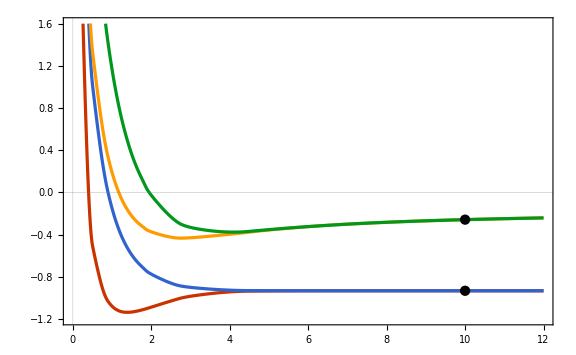

```mathematica
legend =LineLegend[{RGBColor[0.790588, 0.201176, 0.],RGBColor[0.192157, 0.388235, 0.807843],RGBColor[1., 0.607843, 0.],RGBColor[0., 0.596078, 0.109804]},{MaTeX["\\text{GS}",FontSize->18], MaTeX["\\text{OS T}",FontSize->18],MaTeX["\\text{OS S}",FontSize->18], MaTeX["\\text{DES}",FontSize->18]},LegendLayout->"ReversedColumn"];
Show[ListPlot[Table[NRJH2STO3G⟦;;,{1,n+1}⟧,{n,4}],PlotRange->{{0,12},{-1.2,1.6}},ImageSize->Large,Joined->True,InterpolationOrder->2,
PlotStyle->{{Thickness@0.004,RGBColor[0.790588, 0.201176, 0.]},{Thickness@0.004,RGBColor[0.192157, 0.388235, 0.807843]},{Thickness@0.004,RGBColor[1., 0.607843, 0.]},{Thickness@0.004,RGBColor[0., 0.596078, 0.109804]}},PlotLegends->Placed[legend,{Right,Top}],PlotTheme->"Scientific",FrameStyle->Directive[Thick,16,Black],FrameLabel->{MaTeX["R / a_0",FontSize->18],MaTeX["E / E_{\\text{h}}",FontSize->18]}],
ListPlot[{{10,-0.933164},{10,-0.258558}},PlotStyle->{RGBColor[0, 0, 0.],RGBColor[0, 0, 0.]}]]
```

The four solutions have a multiplicity equal to two.

### HHe^+ STO-3G

```mathematica
NRJHHeSTO3G ={{0.2,3.797100,5.921685, 6.118627, 8.685385},{0.4,-0.660836, 1.341665, 1.632906, 3.894343},{0.6,-1.935232,-0.206665, 0.107783, 2.058828},{0.8,-2.453576,-1.014234,-0.703905, 0.983428},{1,-2.688647,-1.495558,-1.203037, 0.296511},{1.2,-2.796794,-1.798398,-1.533011,-0.147293},{1.4,-2.843835,-1.994810,-1.762635,-0.430811},
{1.6,-2.860542,-2.125168,-1.929015,-0.608069},{1.8,-2.862128,-2.213119,-2.052816,-0.714630},{2,-2.856600,-2.272915,-2.145898,-0.77378},{2.5,-2.835792,-2.351509,-2.288246,-0.80546},{3,-2.820601,-2.381208,-2.353509,-0.765412},{4,-2.809713,-2.396283,-2.392136,-0.650512},{5,-2.808017,-2.398134,-2.397641,-0.557730},{6,-2.807807,-2.398270,Undefined,-0.491829},{7,-2.807786,-2.398326,Undefined,-0.444269},{8,-2.807784,-2.398330,Undefined,-0.408558},{9,-2.807784,-2.398330,-2.398330,-0.380780},{10,-2.807784,-2.398330,-2.398330,-0.358558},{11,-2.807784,-2.398330,-2.398330,-0.340376},{12,-2.807784,-2.398330,-2.398330,-0.325224}};
```

ListPlot::ioproc: {{0.2,6.11863},{0.4,1.63291},{0.6,0.107783},{0.8,-0.703905},{1.,-1.20304},{1.2,-1.53301},{1.4,-1.76264},{1.6,-1.92902},{1.8,-2.05282},{2.,-2.1459},«11»} may contain non-machine-precision numbers, complex numbers, or invalid entries.

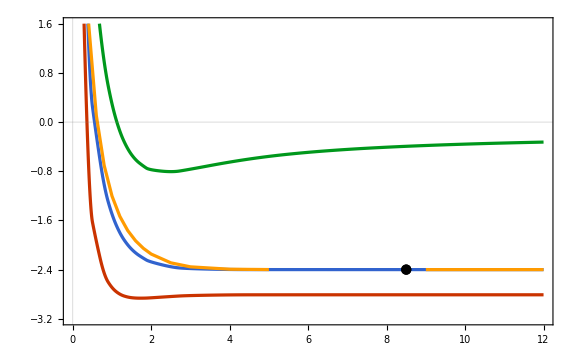

```mathematica
legend =LineLegend[{RGBColor[0.790588, 0.201176, 0.],RGBColor[0.192157, 0.388235, 0.807843],RGBColor[1., 0.607843, 0.],RGBColor[0., 0.596078, 0.109804]},{MaTeX["\\text{GS}",FontSize->18], MaTeX["\\text{OS T}",FontSize->18],MaTeX["\\text{OS S}",FontSize->18], MaTeX["\\text{DES}",FontSize->18]},LegendLayout->"ReversedColumn"];
Show[ListPlot[Table[NRJHHeSTO3G⟦;;,{1,n+1}⟧,{n,4}],PlotRange->{{0,12},{-3.2,1.6}},ImageSize->Large,Joined->True,InterpolationOrder->2,
PlotStyle->{{Thickness@0.004,RGBColor[0.790588, 0.201176, 0.]},{Thickness@0.004,RGBColor[0.192157, 0.388235, 0.807843]},{Thickness@0.004,RGBColor[1., 0.607843, 0.]},{Thickness@0.004,RGBColor[0., 0.596078, 0.109804]}},PlotLegends->Placed[legend,{Right,Top}],PlotTheme->"Scientific",FrameStyle->Directive[Thick,16,Black],FrameLabel->{MaTeX["R / a_0",FontSize->18],MaTeX["E / E_{\\text{h}}",FontSize->18]}],
ListPlot[{{8.5,-2.398330}},PlotStyle->{RGBColor[0, 0, 0.],RGBColor[0, 0, 0.]}]]
```

### Data PES H_2 6-31G

#### HF

```mathematica
nrjhf={{0.1,7.2439231880952235},{0.2,2.2970750538545044},{0.30000000000000004,0.7027375680348014},{0.4,-0.049521728897547135},{0.5,-0.4653850602377938},{0.6000000000000001,-0.7148452526858617},{0.7000000000000001,-0.8714345297833899},{0.8,-0.9720363667529499},{0.9,-1.0370337142247341},{1.,-1.0785232408013221},{1.1,-1.1040726314638345},{1.2000000000000002,-1.1186009135074337},{1.3,-1.1254028862027892},{1.4000000000000001,-1.1267427044517946},{1.5,-1.1242099288384901},{1.6,-1.1189385838924464},{1.7000000000000002,-1.1117462399900555},{1.8,-1.1032258968689508},{1.9000000000000001,-1.0938091262804202},{2.,-1.0838107234146086},{2.1,-1.0734607258568163},{2.2,-1.0629274520709004},{2.3000000000000003,-1.0523340859647694},{2.4000000000000004,-1.0417706600745564},{2.5,-1.0313027906501717},{2.6,-1.020978116244288},{2.7,-1.0108310832334206},{2.8000000000000003,-1.0008865073236675},{2.9000000000000004,-0.9911622049179714},{3.,-0.9816709084007236},{3.1,-0.9724216319975361},{3.2,-0.9634206235488403},{3.3000000000000003,-0.9546720131528923},{3.4000000000000004,-0.9461782482470021},{3.5,-0.9379403852544616},{3.6,-0.9299582905379334},{3.7,-0.9222307884213343},{3.8000000000000003,-0.9147557816927914},{3.9000000000000004,-0.9075303602808509},{4.,-0.90055090652959},{4.1000000000000005,-0.8938132003870314},{4.2,-0.8873125245151252},{4.3,-0.8810437674553446},{4.4,-0.8750015221835208},{4.5,-0.8691801773365123},{4.6000000000000005,-0.8635739988126301},{4.7,-0.8581772001133415},{4.800000000000001,-0.852984000540335},{4.9,-0.8479886710742219},{5.,-0.8431855683728631},{5.1000000000000005,-0.838569157806788},{5.2,-0.8341340267907298},{5.300000000000001,-0.829874889883391},{5.4,-0.825786587229898},{5.5,-0.8218640779320177},{5.6000000000000005,-0.8181024298691592},{5.7,-0.8144968073749443},{5.800000000000001,-0.8110424580147534},{5.9,-0.8077346995213037},{6.,-0.8045689077412712},{6.1000000000000005,-0.8015405062365988},{6.2,-0.7986449579798192},{6.300000000000001,-0.7958777593926079},{6.4,-0.7932344368082278},{6.5,-0.7907105452965698},{6.6000000000000005,-0.7883016696782623},{6.7,-0.7860034274724395},{6.800000000000001,-0.7838114734701042},{6.9,-0.7817215055985285},{7.,-0.7797292717380406},{7.1000000000000005,-0.7778305771661514},{7.2,-0.7760212923302907},{7.300000000000001,-0.7742973606856856},{7.4,-0.7726548063742784},{7.5,-0.7710897415614373},{7.6000000000000005,-0.7695983732867209},{7.7,-0.7681770097214515},{7.800000000000001,-0.7668220657581969},{7.9,-0.7655300678849346},{8.,-0.7642976583195975},{8.1,-0.7631215983990945},{8.200000000000001,-0.7619987712312272},{8.3,-0.7609261836287885},{8.4,-0.7599009673530427},{8.5,-0.7589203796994615},{8.6,-0.7579818034624731},{8.700000000000001,-0.7570827463185866},{8.8,-0.7562208396688909},{8.9,-0.7553938369829676},{9.,-0.7545996116868137},{9.1,-0.7538361546376522},{9.200000000000001,-0.7531015712285153},{9.3,-0.7523940781653714},{9.4,-0.7517119999591662},{9.5,-0.7510537651746584},{9.600000000000001,-0.7504179024771175},{9.700000000000001,-0.7498030365169708},{9.8,-0.7492078836912175},{9.9,-0.7486312478188804},{10.,-0.7480720157659987}};
```

#### FCI

```mathematica
nrjfci={{0.1,7.233893384645772,8.047560509689037,8.088572190528588,8.109798526114368,8.2653497085869,9.37542514610005,9.39239952058356,9.52163548047286,9.546315084396838,11.032927752559846,11.400937253973414,12.064394625808779,12.150942665396993,12.16520918420846,12.23988957196677,15.269210832127087},{0.2,2.2862567967357124,3.0785958349608302,3.1222932719981897,3.152717417210442,3.315352366596873,4.384176048692382,4.396423780916114,4.527985780002896,4.558511824065241,5.816921555171733,6.181576913667397,6.822741231005063,6.912601347783717,6.936302011656011,7.016933671797175,9.781427117251273},{0.30000000000000004,0.6908111115261462,1.4540618829485639,1.5019539515237181,1.5452551087964477,1.716982454651134,2.729463077245485,2.73190330281004,2.8694283423285207,2.9115455957689966,3.8902099877239107,4.250249293648627,4.861087027779313,4.95613548564952,4.992459661827208,5.081860913700327,7.518643259409661},{0.4,-0.06271083162260682,0.6677065498402182,0.7211377955216229,0.7796735269743365,0.9607584045193018,1.8968385839759148,1.909910363119958,2.044583885720432,2.1047334872434287,2.815975553835634,3.1707272609001462,3.747312695093969,3.8490471841406912,3.8996190024399846,3.999905976355689,6.117849659596318},{0.5,-0.47987845182589917,0.2160173379938808,0.27626243775612247,0.35183068082218005,0.5415710166732706,1.3910386103612165,1.4249964371319461,1.5527859112113358,1.6372980268996686,2.1194212606694687,2.4685950249286477,3.0089884746279467,3.118524454991173,3.184431993165594,3.2973703250411766,5.135060278713572},{0.6,-0.7306196969777596,-0.0698414014694515,-0.0015469035653494778,0.09251821280532302,0.289578473480925,1.0483577532655897,1.1077644116888197,1.2268453478527428,1.341527417320562,1.633868444591579,1.9776441899337922,2.480851443654924,2.5989953917735953,2.681032278050643,2.808122137605327,4.406890352824685},{0.7000000000000001,-0.888441662251793,-0.2627554410032391,-0.18520105705916978,-0.07134636094533353,0.13127073387465682,0.7979815890368798,0.8866239812104033,0.9948253831270026,1.1450783440446572,1.2781327494782404,1.6173283786863915,2.0826862834313404,2.210050902113604,2.3088229419041033,2.451303708183829,3.8445888986786185},{0.8,-0.9902276536838093,-0.399305222170077,-0.3112989837572817,-0.1762976190593426,0.029903422316811534,0.6047294621415755,0.7259217894425107,0.8205629107736157,1.0069728475574158,1.01184636120056,1.3431820389775178,1.7698039535540033,1.906867538661662,2.0230414694216896,2.1819272193473713,3.394672625820294},{0.9,-1.0563694465479365,-0.4997593812941985,-0.4001596501607325,-0.242455203843448,-0.03470015679947669,0.44925287072671805,0.6060201029675367,0.6837938863544359,0.7944419871474855,0.9219688838984308,1.1301448128937301,1.5165193437383433,1.6635954258362973,1.7980976479894957,1.974200764380266,3.025770611794711},{1.0,-1.0989745800288486,-0.5761652133698258,-0.4639504318206127,-0.2818043175298728,-0.07450441675732655,0.3201533418760665,0.5151970019469734,0.5722471825554358,0.6252012302913037,0.8635351833171852,0.9637397892552517,1.307617448536147,1.4647965084204366,1.6188492931889633,1.8127769058357983,2.7194820821746477},{1.1,-1.1256238169430413,-0.6360445076783189,-0.5103927904213924,-0.3019727351571083,-0.0970692237937939,0.2103716147656668,0.4458549857615145,0.47825831025730403,0.4895581067757858,0.8287894698532975,0.8347220180005152,1.1333822796792417,1.3005118423247048,1.4755552299397428,1.687703782763886,2.4640248926436534},{1.2000000000000002,-1.141252680188916,-0.6842508994456639,-0.5446058037274976,-0.30808012400437057,-0.10740685382749471,0.11534867380645697,0.37868542949300277,0.3948554012892461,0.397240431991296,0.736137689513081,0.8122959030338207,0.9870020525081357,1.1637251488128078,1.3612884678518484,1.5918498537444807,2.2508469492901146},{1.3000000000000003,-1.1491757334833603,-0.7239883873109285,-0.5700999909390192,-0.30372370400774784,-0.10897440512762113,0.03202313349184793,0.2914234087800047,0.3267355974529673,0.35453319035666775,0.6620560868617704,0.8099719879834875,0.8633597685587386,1.0492058197400305,1.2707494503906125,1.5197244762509847,2.073190527096206},{1.4000000000000001,-1.1516790314745053,-0.7574093211788563,-0.5893466518175344,-0.29154668991183363,-0.10425148396514572,-0.041739084001995885,0.22057693278589185,0.2655292508578718,0.32529127264686475,0.6073128531647515,0.7584700474120291,0.8184658005511981,0.9530392393058256,1.199714584813385,1.4669272301366116,1.925543938071046},{1.5000000000000002,-1.150374809728504,-0.7859820772385991,-0.6041163233024792,-0.2735817648926532,-0.10748393468404738,-0.09508874188313443,0.1635408496838472,0.21290340354333093,0.3043579955528958,0.5676068193368408,0.6691775401738326,0.833596311472427,0.8735472358754939,1.1447374497164242,1.4298477853139095,1.8034022104190655},{1.6,-1.146419344550639,-0.810724590558777,-0.6156861988303026,-0.2514631615777323,-0.1663567666800645,-0.08294241249686918,0.1177311335372988,0.1682098495355977,0.2899768714090327,0.5395187739780274,0.5929633168725741,0.800077169614841,0.8611412005207527,1.1029551737208076,1.4054720376378316,1.7031227736192296},{1.7000000000000002,-1.1406511267014592,-0.8323562274130464,-0.6249729969712473,-0.2265590377565282,-0.2192562361254088,-0.06898274892030087,0.08104840424620507,0.13073082700138616,0.2806935174280186,0.5203808343089124,0.5278062852250435,0.7427907858268015,0.8867485277090341,1.0719505403466014,1.3912460012108503,1.6218149386143352},{1.8000000000000003,-1.1336821538380921,-0.8513978801467987,-0.6326238436973146,-0.2668896231580149,-0.20005377164729787,-0.054200573566964616,0.05180597489939465,0.09968487168683726,0.275256420053958,0.4720802799046373,0.5080912419322918,0.6938604228278185,0.9145326812956844,1.049652471473953,1.3849798401212796,1.5572397638408155},{1.9000000000000001,-1.1259607779203797,-0.868238047231353,-0.6390831981356523,-0.309835194404105,-0.17299655262171065,-0.03943971376817712,0.028655290860183702,0.07427409218717262,0.27257142477496366,0.42447645252661415,0.5009520298025415,0.6526987807784541,0.9417313361341187,1.0342666210222409,1.3847830601371922,1.5076908798719553},{2.0,-1.1178162987540992,-0.8831761275847647,-0.644645064854406,-0.3485742687893518,-0.14632498108829806,-0.025412934248059793,0.010522146138283173,0.05372912453615397,0.2716805977255159,0.38394279041486334,0.49755532361398247,0.6183929641963287,0.9662808240316377,1.0242302951910538,1.3890241312942981,1.471811548014665},{2.1,-1.1094910790766486,-0.8964504856583174,-0.6494948349487834,-0.3835140646996821,-0.12086886983932021,-0.012695507507103021,-0.00344749260030619,0.037340059353604294,0.2717562499027292,0.3496338060533407,0.4967157919770592,0.5901073517625328,0.9865692506965927,1.0181865029816777,1.396308236204382,1.4483127803365985},{2.2,-1.1011637448359475,-0.9082565389793682,-0.6537427263330968,-0.4150038990043639,-0.097338725425904,-0.013933905694130166,-0.0017085342788497049,0.024472865653325238,0.27210417462120867,0.320864993923936,0.4974376180030646,0.5670759575675905,1.0016936536821883,1.0149717091185844,1.4054666542982557,1.4356376559730741},{2.3000000000000003,-1.0929659231812394,-0.9187584841591773,-0.657449878224171,-0.4433472110126575,-0.076304105372617,-0.02148354593502,0.0072954776993223724,0.014573859576783477,0.27217071577076846,0.2970686085907932,0.4989029553282641,0.5485749617614262,1.0116464685888134,1.01361136818733,1.4155511705530373,1.431749215565889},{2.4000000000000004,-1.0849943222845846,-0.9280970533718806,-0.6606479431826651,-0.46881080007600123,-0.058168261988668146,-0.026543168883954638,0.00716548360010133,0.01423339848910471,0.27154866135481964,0.2777498042782724,0.500470017666186,0.533908487129781,1.0133172747786496,1.0172045961041731,1.4258274707624545,1.4342277990738606},{2.5000000000000004,-1.0773194849986227,-0.9363948019828009,-0.663353067904504,-0.4916320220196756,-0.04314695055276141,-0.02948853140626928,0.0018367383979461804,0.01917275453219014,0.26244553516685964,0.26997802845327523,0.5016714358900999,0.5224122285458006,1.0134817143944397,1.0195488038278573,1.4357630702138877,1.4406350691585361},{2.6,-1.0699921684831133,-0.9437598251829127,-0.6655752393097059,-0.5120243733247904,-0.03126063779848692,-0.030647898506932614,-0.0017686910660008603,0.02229564582508603,0.2506924513436364,0.2673396031750448,0.5022068737446029,0.5134704320853246,1.0136653392629427,1.0198587516046511,1.4450076882500187,1.4488913701420327},{2.7,-1.063048008013923,-0.9502884297851405,-0.6673240027169817,-0.5301817691882794,-0.030320605373586607,-0.022348718314113225,-0.0039641837976273075,0.023853911829652685,0.24201194753295863,0.2636411243212672,0.5019274754039569,0.5065371498072607,1.0135780761137494,1.0190724280994967,1.4533664781467457,1.4574749793242932},{2.8000000000000003,-1.0565109168153113,-0.9560670783021405,-0.6686115096499867,-0.5462817836022424,-0.02879096074217863,-0.016108866127912125,-0.005030148215910135,0.024125968294140543,0.2359170457824497,0.25899763165759565,0.5008127374816178,0.5011527169303072,1.0130544649369968,1.0178199852764886,1.4607684524724516,1.465435296100817},{2.9000000000000004,-1.0503955427943934,-0.9611738123763134,-0.6694537353583727,-0.5604880989562142,-0.02633776648735564,-0.012154549190588337,-0.00522131237087109,0.023383009101976437,0.2319367659350684,0.25360832726157456,0.496950103688264,0.4989423083920371,1.0120260976704063,1.0164560400887157,1.4672333964236408,1.4723010459575545},{3.0000000000000004,-1.0447090253809825,-0.9656793040239269,-0.6698705479137737,-0.5729523805417631,-0.023239618945226137,-0.01007516988508178,-0.004771081601678107,0.021867600643569907,0.2296451897339598,0.24773224960522394,0.4936505335129739,0.4964659158420233,1.0104941337060604,1.0151250999857602,1.4728405222562089,1.4779550894420126},{3.1,-1.0394522486757671,-0.9696476471171158,-0.6698851416469667,-0.5838157448573471,-0.019775954385901462,-0.009483191002311375,-0.0038931708878000015,0.019783751475333233,0.22868174100979838,0.24166435221208543,0.4910511560719319,0.4935743789318325,1.008504412797861,1.0138280861281463,1.47770137225238,1.4825134528557888},{3.2,-1.0346207537644039,-0.9731369741975666,-0.6695231913461133,-0.5932099389316525,-0.016223584717266926,-0.010040647675666259,-0.002781029502968435,0.017295486834231433,0.22875633639044657,0.2357125954317405,0.4890088078487651,0.4904739059390619,1.0061268204325826,1.0124795828586883,1.4819384181895496,1.4862228214599729},{3.3000000000000003,-1.0302054433947418,-0.9761999604450216,-0.668811953957313,-0.6012583019030933,-0.012848425897480087,-0.011466799441172404,-0.0016057670732693707,0.014530588492755181,0.22964149741403597,0.2301758524257373,0.4873650034290261,0.48742347332536096,1.0034396242985981,1.0109542031438097,1.4856697694532182,1.4893799405860797},{3.4000000000000004,-1.0261931820760333,-0.9788842569109775,-0.6677794463182443,-0.6080765469773242,-0.013533714728249768,-0.009892538879034352,-0.0005133878493491228,0.011586733256554627,0.2253222515070356,0.231157827422183,0.4844265706848507,0.4862238743395137,1.0005187190490104,1.0091225643276234,1.4889995947838797,1.4922724757929053},{3.5000000000000004,-1.022567363739709,-0.9812328795278239,-0.666453759117788,-0.6137733836918825,-0.016056776166568976,-0.007557742421093638,0.0003778517019149552,0.00853812903419493,0.2213683480769012,0.23315899337102464,0.48180521076457594,0.4853563617592541,0.9974311876893744,1.0068772699736073,1.4920133559430613,1.4951397161728202},{3.6,-1.0193084891544912,-0.9832845691055087,-0.6648625237447735,-0.6184509949697302,-0.01888483924139084,-0.005988821141899581,0.0009792368304474275,0.00544154338239522,0.2184611294525719,0.23551988999031026,0.47960943096953434,0.4847773080514056,0.9942323128357594,1.004149080896654,1.4947767241123184,1.4981510214038987},{3.7,-1.0163947687873034,-0.9850741301075587,-0.663032523809312,-0.6222053862407304,-0.02189228836177909,-0.005260920479656039,0.0012320063002697612,0.002341215321153889,0.21666643410896597,0.2381291623288651,0.4779081633688876,0.4844485860287973,0.9909650988086618,1.0009137946428273,1.4973370347070274,1.5013993559023573},{3.8000000000000003,-1.013802745969536,-0.986632751622889,-0.6609894310997912,-0.6251266299973728,-0.024973504795620716,-0.005375718165566645,-0.0007274691897116159,0.0011061212221153416,0.21596747958513302,0.2408856450254349,0.47673285468193544,0.48433542181806205,0.9876614293372752,0.9971911408077374,1.4997262569772234,1.5049065733866973},{3.9000000000000004,-1.0115079214180531,-0.9879883116875197,-0.6587576418322338,-0.627299034477476,-0.028039385928238347,-0.006268561528648797,-0.0037354341047678985,0.0005974348969415844,0.2162749611951134,0.24369757794732566,0.4760822373928489,0.4844058413912931,0.9843441247263693,0.993037812041361,1.501964645188213,1.5086365995008308},{4.0,-1.009485353580871,-0.989165665145971,-0.6563601897556808,-0.6288012673059877,-0.03101528074622162,-0.007824878947778391,-0.006658292802724064,-0.0002764217444668482,0.21744648625701268,0.24648337940352394,0.4759288177517722,0.4846310042509807,0.9810293305893605,0.98853717530478,1.5040644499134568,1.512512611565075},{4.1,-1.0077102090421945,-0.990186914971289,-0.6538187156037791,-0.6297064631222389,-0.03383974858978031,-0.009901105283579209,-0.00947541137769467,-0.0014809466590450515,0.21931021449143054,0.24917298744838304,0.4762261282150462,0.48498586624636286,0.9777288373156383,0.9837880772783728,1.506033269900225,1.516434827349728},{4.2,-1.0061582416788055,-0.9910716670015587,-0.6511534760498359,-0.6300823390448258,-0.03646370628923484,-0.012344800928672295,-0.012169432389058765,-0.002969916054265609,0.2216871664775803,0.2517091000296143,0.47691590252655075,0.4854497861692499,0.9744520778341692,0.978894582079334,1.5078767997564435,1.5202964358889686},{4.3,-1.0048061864281934,-0.9918372681880234,-0.6483833788974753,-0.6299913345990775,-0.03884969365428123,-0.015010334647896667,-0.0147260734895176,-0.004690282654836259,0.22440847480547735,0.2540479396719688,0.4779345235521586,0.48600685463378523,0.9712076727710178,0.973957718927861,1.5096008687270484,1.5239962519010395},{4.3999999999999995,-1.0036320615348842,-0.992499028588963,-0.6455260343405518,-0.6294907849573257,-0.04097111521101951,-0.017768901536744625,-0.017134060341720547,-0.006586458254602051,0.22732634547745875,0.2561593930921744,0.47921832758680316,0.48664585941382765,0.96800448458458,0.9690696188440135,1.5112127697699882,1.5274475984609555},{4.5,-1.0026153805229545,-0.9930704274571455,-0.6425978146491053,-0.6286331292951765,-0.04281139983438942,-0.02051344362422422,-0.019385096477309877,-0.008603772298128809,0.23031935644835422,0.2580265256630666,0.4807075788816414,0.4873599002565928,0.96430992187796,0.9648522071617247,1.5127219485166425,1.5305835835838932},{4.6,-1.001737280983447,-0.9935633038555238,-0.6396139166250143,-0.6274661505731411,-0.044363067712780924,-0.023159834663594225,-0.021473809625024265,-0.0106910422842173,0.23329355234489352,0.2596445574635912,0.4823491191131328,0.4881457275221898,0.9597440653662532,0.9617615581016901,1.5141401631506697,1.5333593165823296},{4.7,-1.0009805811771852,-0.9939880323028653,-0.6365884227340565,-0.6260332394617848,-0.04562671767889456,-0.02564573478851026,-0.023397642853768413,-0.012802300638213054,0.23618085618432585,0.2610194286868034,0.4840978303635842,0.48900290743852126,0.955422974758961,0.9587441618864304,1.5154812443721781,1.535751762730661},{4.8,-1.000329777470232,-0.9943536840061235,-0.633534358078275,-0.6243736733923176,-0.04660995743249044,-0.027928217663922533,-0.02515667975355909,-0.014897789885135154,0.23893601780771653,0.2621660928574955,0.48591712546920574,0.48993291987474985,0.9513837045700876,0.9558122179443825,1.5167605852478467,1.5377579361355984},{4.9,-0.9997709960345886,-0.9946681742806478,-0.6304637414231691,-0.6225229015266891,-0.04732630154303366,-0.029980906381794653,-0.026753406832221077,-0.01694436825568027,0.24153294322796467,0.2631066686353889,0.48777870589083827,0.4909382808062672,0.9476506582800068,0.9529780426588983,1.5179944793492255,1.539392049148782},{5.0,-0.9992919114810179,-0.9949383967933529,-0.6273876294001275,-0.6205128273742646,-0.04779406150091042,-0.03179105336387339,-0.028192424699643837,-0.018915471201385425,0.24396093203151487,0.2638685635069456,0.48966181875716425,0.4920217589644312,0.9442371114741557,0.9502535625494835,1.519199406940787,1.540682121141402},{5.1,-0.998881643577,-0.995170345288416,-0.6243161537961357,-0.6183720823938761,-0.04803525060342423,-0.033356793043303135,-0.029480123807799907,-0.020790761151778525,0.24622112393886436,0.2644826611221081,0.49155221542352306,0.49318573089282186,0.9411468492884068,0.9476498204082986,1.520391346998923,1.5416664297629787},{5.2,-0.9985306413178163,-0.9953692234703717,-0.6212585525189342,-0.6161262858219994,-0.048074524966688736,-0.0346846701176704,-0.030624341712902403,-0.022555576752773865,0.24832330934365454,0.2649816420137008,0.49344097508039353,0.49443169519290947,0.9383757978345124,0.9451765396077147,1.5215851704830545,1.5423900793168663},{5.3,-0.9982305616547393,-0.9955395437281844,-0.618223195371838,-0.6137982878591959,-0.04793818060055027,-0.03578747633629703,-0.03163401800928395,-0.024200269653738615,0.25028316969569003,0.2653984870203297,0.4953233165031944,0.49575994766558384,0.9359135783109329,0.9428417759199881,1.522794149589928,1.5429018698192858},{5.4,-0.9979741483398634,-0.9956852153895155,-0.6152176061661163,-0.6114083950223934,-0.04765322509156883,-0.03668239373248999,-0.03251886101951745,-0.025719495107249857,0.2521199618457555,0.26576519492961875,0.4971694053048069,0.49719748372316175,0.9337449446381458,0.9406516721617231,1.524029599951721,1.5432515777203446},{5.5,-0.9977551147378196,-0.9958096231984215,-0.612248482923947,-0.6089745778117746,-0.04724654072362361,-0.037389426799070924,-0.033289037592004356,-0.02711150386591915,0.2538546314535141,0.2661117309671623,0.49865755852861954,0.4990637596147777,0.9318510848646042,0.9386103194365838,1.5253006584860918,1.5434877036627577},{5.6,-0.9975680331316654,-0.9959156967150706,-0.6093217179768131,-0.6065126618016938,-0.04674415355849251,-0.037930100771341985,-0.03395489437814028,-0.028377467603915046,0.25550832491588493,0.26646521064377726,0.50022052684449,0.5009236359409056,0.930210777436439,0.9367197199082552,1.5266141889793337,1.5436557015308978},{5.7,-0.9974082320175802,-0.9960059713408799,-0.6064424196510333,-0.6040365038519763,-0.04617061993299487,-0.038326402368224266,-0.0345267160376298,-0.029520858219839963,0.25710126131696376,0.2668493137838118,0.5018531922758471,0.5027791491147218,0.9288013991997749,0.9349798398242547,1.5279748002550777,1.5437966737061108},{5.8,-0.9972717021158656,-0.9960826416775322,-0.6036149369801733,-0.6015581553932335,-0.045548537976064396,-0.03859994007190937,-0.03501452315129383,-0.0305468924563409,0.25865192231424106,0.26728391587722633,0.5035493862576866,0.504632377161344,0.9275997852497737,0.933388737660938,1.5293849575172382,1.5439464974135144},{5.9,-0.9971550112834615,-0.9961476079282932,-0.6008428885255249,-0.5990880147306129,-0.04489818723398642,-0.03877130189012434,-0.0354279103289914,-0.031462046773664154,0.2601765167939667,0.26778491787126324,0.5053021084320817,0.5064850842175979,0.9265829430781408,0.9319427504042775,1.5308451656284994,1.5441353342243413},{6.0,-0.9970552281509762,-0.9962025160453566,-0.5981291959657108,-0.5966349701094857,-0.04423729458747769,-0.038859589035959846,-0.03577592314743047,-0.03227364283336595,0.26168867754073577,0.26836425089824434,0.5071037591411457,0.5083384934811567,0.9257286257420407,0.9306367207048407,1.532354203139915,1.5443874674808034},{6.1,-0.9969698540809635,-0.9962487923129921,-0.595476122676663,-0.5942065349655403,-0.0435809197244858,-0.03888210405678255,-0.03606697115246388,-0.03298950084156521,0.26319934856137356,0.2690300291075947,0.5089463709479904,0.5101931669592159,0.9250157712625142,0.9294642485508211,1.5339093873013006,1.5447214093344546},{6.2,-0.9968967629152953,-0.9962876730325795,-0.5928853171036623,-0.5918089764054244,-0.042941448920662845,-0.038854171851951586,-0.036308773192504556,-0.03361765600573516,0.26471682383955975,0.26978682171256285,0.510821827917738,0.5120489699231451,0.9244248180690131,0.9284179528178459,1.5355068525930322,1.5451502192376843},{6.3,-0.9968341479174224,-0.9963202299418991,-0.5903578603620668,-0.5894474375866892,-0.04232868217328478,-0.038789072013590276,-0.03650833077143412,-0.03416613218713482,0.26624690106245585,0.2706360145959744,0.5127220644955915,0.5139050990164978,0.9239379087730667,0.9274897302608534,1.537141828138333,1.545681978331185},{6.4,-0.996780475295928,-0.996347391957924,-0.5878943172144929,-0.5871260543263237,-0.041749996144049284,-0.0386980612476473,-0.03667192486251003,-0.03464276626012164,0.267793117182777,0.27157623235096784,0.5146392385527165,0.5157601549750244,0.9235389965756144,0.9266710019499672,1.5388089023715785,1.546320368612145},{6.5,-0.9967344437024058,-0.9963699637815601,-0.5854947893738491,-0.58484806599166,-0.04121056406116852,-0.038590465444806266,-0.03680513164547505,-0.035055076547319985,0.26935703647710973,0.2726037933991404,0.516565875509604,0.5176122434896461,0.9232138699473835,0.925952939615364,1.5405022663172625,1.5470653115257682},{6.6,-0.9966949491177298,-0.9963886418467801,-0.5831589699753329,-0.582615920528646,-0.04071361372792723,-0.038473822331761554,-0.03691285285337961,-0.03541016885889048,0.27093856591507726,0.27371317367688,0.518494982394945,0.5194590905619781,0.922950111735047,0.9253266667029025,1.5422159296086233,1.547913627231264},{6.7,-0.9966610545692751,-0.9964040280377404,-0.5808861980417748,-0.5804313733628406,-0.040260705946901565,-0.03835405750568624,-0.036999356783067594,-0.03571467402344922,0.2725362770106534,0.27489745806515753,0.5204201322724814,0.5212981615326291,0.9227370085292511,0.9247834310525884,1.5439439058346103,1.5488596828276682},{6.8,-0.996631964153558,-0.9964166415389518,-0.5786755118229239,-0.5782955798618974,-0.03985201775339267,-0.03823567892753563,-0.037068326481039776,-0.035974711287182715,0.2741477177064272,0.27614876295142865,0.5223355206913942,0.5231267756390142,0.9225654250733398,0.9243147479282796,1.5456803658874052,1.5498960049002148},{6.9,-0.9966070008719121,-0.996426929126689,-0.5765257000050737,-0.5762091810635587,-0.03948661754786656,-0.03812197746780363,-0.03712291211972346,-0.03619587251844847,0.2757697020617622,0.2774586177205145,0.5242359967136853,0.5249422103720182,0.9224276568602738,0.923912513619642,1.547419759666518,1.551013838529774},{7.0,-0.9965855878206589,-0.9964352741578162,-0.5744353499447756,-0.5741723824357237,-0.03916272220532477,-0.03801522369148261,-0.03716578509180668,-0.03638322274772002,0.2773985694102588,0.27881829726049184,0.5261170716738515,0.5267417919854671,0.9223172720669408,0.92356909100646,1.5491569077846576,1.5522036411234676},{7.1,-0.9965672323111432,-0.9964420044649835,-0.5724028922628444,-0.5721850255302477,-0.03887792923100228,-0.03791685358168248,-0.03719919184675605,-0.03654131316630907,0.27903040808955837,0.2802191014773002,0.5279749091647434,0.5285229702406635,0.9222289518033467,0.9232773693250331,1.5508870658411102,1.5534555048740866},{7.2,-0.996551512529047,-0.9964473993262646,-0.5704266413250187,-0.5702466525043901,-0.03862941979703979,-0.03782763820337798,-0.037225005952726764,-0.036674203279612766,0.28066124174126195,0.28165258115336606,0.5298062998567868,0.5302833768411661,0.9221583355002512,0.923030800947735,1.5526059644221442,1.554759506215509},{7.3,-0.9965380663768454,-0.9964516956431687,-0.5685048313224966,-0.5683565636019269,-0.03841413088064466,-0.03774783431451709,-0.03724477727863723,-0.03678548944807333,0.2822871784906104,0.28311071215426653,0.5316086246832814,0.53202086804813,0.9221018762560488,0.9228234183045054,1.5543098282984422,1.5561059842628264},{7.4,-0.9965265821774167,-0.996455093432755,-0.566635647837025,-0.5665138677985291,-0.038228896646656796,-0.037677314589825595,-0.03725977754751869,-0.03687833754011194,0.2839045250500837,0.284586021957591,0.5333798097054052,0.5337335526996848,0.9220567092087213,0.9226498341898874,1.555995378374589,1.5574857529212882},{7.5,-0.9965167909507726,-0.996457760717439,-0.5648172549255736,-0.564717526916338,-0.038070560657843644,-0.03761567742268104,-0.0372710418114503,-0.03695551786201512,0.2855098689881531,0.2860716737816449,0.535118275645813,0.535419807328444,0.9220205345445434,0.9225052286463343,1.5576598198494176,1.558890253188607},{7.6,-0.9965084600090872,-0.9964598378788905,-0.5630478178839665,-0.5629663935956882,-0.0379360614806489,-0.03756233722731181,-0.03727940564204024,-0.03701944091716902,0.28710013312855165,0.28756151430645827,0.5368228846878405,0.5370782803252232,0.9219915156136029,0.9223853254389637,1.5593008198204863,1.560311653260026},{7.7,-0.9965013876472169,-0.9964614415299455,-0.5613255219462157,-0.5612592435750721,-0.03782249483985792,-0.03751659681315789,-0.03728553802173873,-0.03707219288179306,0.2886726063769008,0.289050091206967,0.538492886712099,0.5387078871788773,0.9219681917801166,0.922286360873803,1.5609164772517046,1.5617429045007816},{7.8,-0.9964953987363749,-0.9964626679491186,-0.5596485872466351,-0.559594802773253,-0.03772715573496299,-0.037477703792389294,-0.03728997006568793,-0.037115569968678236,0.2902249552932631,0.29053264656954325,0.5401278667120878,0.5403077987744027,0.921949405059248,0.9222050473941328,1.5625052878573167,1.5631777613070197},{7.9,-0.9964903410569674,-0.9964635961162662,-0.5580152804172416,-0.5579717696906586,-0.037647563939648965,-0.037444893161381054,-0.03729311980697442,-0.03715111108757535,0.2917552205234655,0.29200509184504264,0.5417276947180427,0.5418774245918687,0.9219342392401667,0.9221385340455001,1.5640661060676924,1.5646107724619824},{8.0,-0.9964860822326476,-0.996464290383305,-0.5564239232164195,-0.5563888336529016,-0.037581476135751385,-0.03741741821731909,-0.03729531334686087,-0.037180128405761736,0.2932618018416864,0.29346396940069464,0.5432924791798868,0.5434163924501902,0.9219219700185296,0.9220843655502077,1.5655981058564867,1.5660372509261486},{8.1,-0.9964825071511366,-0.9964648028114197,-0.554872898589725,-0.554844689409982,-0.03752688764596969,-0.037394571877567964,-0.03729680271131301,-0.03720373556867386,0.29474343510465617,0.29490640504948307,0.5448225244269452,0.5449245262091491,0.9219120246200115,0.9220404413953929,1.5671007418418081,1.5674532281791123},{8.2,-0.9964795157780034,-0.9964651752040129,-0.553360654553677,-0.5533380485833143,-0.037482026376974995,-0.037375700300783646,-0.03729778077232972,-0.03722287346422583,0.2961991639241263,0.29633005522260664,0.5463182925394222,0.5464018226014282,0.9219039494468918,0.9220049760253982,1.5685737117384706,1.5688553983395739},{8.3,-0.996477021287717,-0.996465440863519,-0.5518857062722204,-0.5518676484222085,-0.03744534120541239,-0.03736021049715339,-0.03729839359268787,-0.03723833350945897,0.2976283083675919,0.2977330517543654,0.5477803697362176,0.5478484281298396,0.9218973843898288,0.9219764609468237,1.5700169209408268,1.5702410563922264},{8.4,-0.9964749484515503,-0.99646562609893,-0.550446636666275,-0.5504322582944888,-0.037415486662202735,-0.037347573383794574,-0.03729875053913542,-0.037250778509457655,0.299030432524821,0.29911394660179014,0.5492094372038785,0.5492646167444009,0.9218920425935584,0.9219536293108643,1.5714304497605502,1.5716080339934615},{8.5,-0.9964732322347603,-0.9964657515099289,-0.5490420958627231,-0.5490306842951792,-0.03739130541500896,-0.03733732351009608,-0.03729893248758781,-0.03726076118977026,0.30040531234783885,0.30047165824230626,0.5506062461580672,0.5506507688164259,0.9218876946227346,0.9219354233285881,1.5728145236308977,1.5729546355425181},{8.6,-0.9964718165660309,-0.9964658330723559,-0.5476707997524264,-0.5476617723146949,-0.03737180972663344,-0.037329056457270374,-0.03729899841625399,-0.03726874053886679,0.3017529047943512,0.3018054209923991,0.5519715968366956,0.5520073517564646,0.9218841561351153,0.9219209647043772,1.5741694864166413,1.574279576511228},{8.7,-0.99647065325055,-0.996465883048452,-0.5463315278897786,-0.5463244098655564,-0.037356162784688715,-0.03732242471570234,-0.03729899065214724,-0.03727509611937917,0.30307331898390505,0.3031147380701122,0.5533063210664042,0.5533349024804635,0.9218812783184188,0.9219095281376689,1.57549577683527,1.5755819254292605},{8.8,-0.9964697010048472,-0.9964659107439592,-0.5450231209301495,-0.5450175269256483,-0.03734366055713852,-0.03731713266619084,-0.03729893900503921,-0.03728014051895713,0.304366789811958,0.3043993388826326,0.5546112680151896,0.5546340118139373,0.9218789404847936,0.9219005178377897,1.576793907893787,1.5768610504284568},{8.9,-0.9964689245965399,-0.9964659231324997,-0.5437444777676854,-0.5437400960174861,-0.037333714628464104,-0.03731293113928785,-0.03729886399202123,-0.03728413011574286,0.3056336542561673,0.3056591407501333,0.5558872927372087,0.555905310834782,0.9218770443349389,0.9218934469207607,1.578064449174051,1.5781165708493157},{9.0,-0.9964682940760536,-0.9964659253660633,-0.5424945525048861,-0.5424911317075001,-0.0373258363093083,-0.037309611899693756,-0.037298779326489284,-0.03728727433198112,0.30687433044654566,0.3068942150716202,0.5571352471260742,0.5571494590889987,0.921875509506024,0.921887919503688,1.5793080117522897,1.5793483141014348},{9.1,-0.9964677840901928,-0.9964659211885982,-0.541272351357797,-0.5412696896774727,-0.037319622185071705,-0.037307002299051456,-0.03729869381837406,-0.0372897435429079,0.30808929945088304,0.30810475778765456,0.5583559729145499,0.5583671345674295,0.9218742701011047,0.9218836152796641,1.5805252355112942,1.5805562777339797},{9.2,-0.9964673732694413,-0.9964659132680396,-0.540076929576564,-0.5400748654919674,-0.03731474117070971,-0.03730496025795074,-0.03729861280802324,-0.03729167579974102,0.3092790896414247,0.3092910638909818,0.5595502963885146,0.559559025301136,0.9218732719676715,0.9218802763375402,1.5817167785912682,1.581740596504129},{9.3,-0.9964670436822652,-0.9964659034602185,-0.5389073884405181,-0.5389057931611118,-0.03731092306698022,-0.03730336967387621,-0.03729853923460327,-0.03729318251406641,0.3104442634535928,0.3104535056691482,0.5607190245165619,0.5607258224167888,0.9218724705466848,0.9218776959870595,1.582883308726413,1.582901514116192},{9.4,-0.9964667803506797,-0.9964658930165473,-0.5377628723698494,-0.5377616435770742,-0.03730794856165014,-0.03730213630361816,-0.03729847442122079,-0.03729435323934498,0.31158540631466325,0.311592514326614,0.5618629422323903,0.5618682144868371,0.9218718291575,0.9218757093530804,1.584025496222365,1.5840393592345796},{9.5,-0.9964665708219144,-0.9964658827456744,-0.5366425661818611,-0.5366416228848644,-0.037305640584729044,-0.037301184133376936,-0.03729841864289424,-0.037295259672564335,0.3127031175060627,0.3127085646201041,0.5629828106424498,0.5629868830108938,0.9218713176173665,0.9218741855138635,1.585144008344968,1.585154525338254},{9.6,-0.9964664047914588,-0.9964658731378827,-0.5355456925086262,-0.5355449708334381,-0.0373038569058574,-0.03730045222521107,-0.03729837153011427,-0.03729595898660616,0.31379800272159586,0.3138021621440531,0.5640793659648939,0.5640824988717047,0.9218709111196428,0.921873020973411,1.586239504909231,1.5862474539749771},{9.700000000000001,-0.9964662737730253,-0.9964658644596048,-0.5344715093840591,-0.5344709591410494,-0.0373024838511508,-0.03729989201208554,-0.03729833234943357,-0.03729649659164368,0.3148706680924217,0.3148738329183477,0.5651533190371473,0.5651557196200327,0.9218705893143126,0.9218721342759956,1.5873126348780884,1.5873186209837118},{9.8,-0.9964661708112045,-0.9964658568242829,-0.5334193080018239,-0.5334188898991508,-0.03730143101397222,-0.0372994650041006,-0.03729830019347262,-0.037296908412456295,0.3159217154641956,0.3159241149536473,0.5662053552573401,0.5662071874556643,0.9218703355484306,0.9218714615900506,1.5883640338017997,1.5883685252764241},{9.9,-0.9964660902326967,-0.9964658502446275,-0.532388410640653,-0.5323880940314731,-0.03730062683653178,-0.037299140863190264,-0.037298274105037374,-0.03729722275743684,0.31695173873040067,0.31695355149780624,0.5672361348497137,0.5672375277860484,0.9218701362350744,0.9218709531084636,1.5893943219501256,1.589397679802109},{10.0,-0.9964660274322835,-0.9964658446705336,-0.531378168750242,-0.5313779298189751,-0.03730001494575019,-0.03729889580239243,-0.037298253154407324,-0.037297461845369584,0.3179613210463532,0.31796268569723674,0.5682462933654671,0.5682473482583132,0.9218699803265245,0.9218705701308517,1.5904041030092775,1.5904066043518994}};
```

```mathematica
nrjfcit={{0.1,8.047560509689045,8.109798526114353,9.375425146094555,11.03292775256881,12.064394625784711,12.165209184209466},{0.2,3.07859583496076,3.1527174172104395,4.384176048692403,5.81692155517165,6.822741231009742,6.936302011656025},{0.30000000000000004,1.4540618829485723,1.5452551087964466,2.7294630772454838,3.8902099877238996,4.861087027779307,4.99245966182718},{0.4,0.6677065498402186,0.7796735269743316,1.9099103631199519,2.8159755538357167,3.7473126950939832,3.8996190024399127},{0.5,0.21601733799388434,0.35183068082217517,1.4249964371319876,2.1194212606694762,3.0089884746278255,3.1844319931655605},{0.6,-0.06984140146943574,0.09251821280533967,1.1077644116888212,1.6338684445915863,2.4808514436549265,2.681032278050618},{0.7000000000000001,-0.2627554410032289,-0.07134636094532354,0.8866239812104677,1.2781327494782726,2.0826862834313395,2.308822941904017},{0.8,-0.39930522217006725,-0.17629761905932106,0.7259217894424719,1.0069728475574422,1.7698039535539962,2.0230414694216865},{0.9,-0.49975938129418473,-0.24245520384344132,0.6060201029675376,0.7944419871474668,1.5165193437383326,1.7980976479894935},{1.0,-0.5761652133698156,-0.2818043175298506,0.5151970019470049,0.6252012302912764,1.3076174485361367,1.6188492931889336},{1.1,-0.6360445076783119,-0.30197273515710776,0.4458549857615193,0.48955810677580835,1.1333822796792603,1.4755552299397472},{1.2000000000000002,-0.6842508994456491,-0.30808012400435025,0.3786854294929203,0.3948554012893144,0.9870020525081227,1.361288467851848},{1.3000000000000003,-0.7239883873109108,-0.3037237040077372,0.2914234087799663,0.3545331903566762,0.8633597685587304,1.2707494503906247},{1.4000000000000001,-0.7574093211788515,-0.29154668991182575,0.2205769327858178,0.3252912726469024,0.7584700474120094,1.1997145848133925},{1.5000000000000002,-0.7859820772385842,-0.27358176489265595,0.16354084968368632,0.30435799555298537,0.669177540173818,1.144737449716457},{1.6,-0.8107245905587774,-0.2514631615777283,0.11773113353728704,0.2899768714089319,0.5929633168725843,1.1029551737209324},{1.7000000000000002,-0.8323562274130314,-0.2265590377565374,0.08104840424620718,0.28069351742803406,0.5278062852250489,1.0719505403465668},{1.8000000000000003,-0.8513978801467861,-0.20005377164728877,0.051805974899460594,0.27525642005418227,0.47208027990464707,1.0496524714736974},{1.9000000000000001,-0.8682380472313671,-0.17299655262170788,0.02865529086015073,0.2725714247750144,0.42447645252661914,1.0342666210222582},{2.0,-0.8831761275847647,-0.14632498108828784,0.010522146138374211,0.271680597725549,0.3839427904148742,1.024230295190959},{2.1,-0.8964504856583009,-0.12086886983931322,-0.003447492600306745,0.2717562499027206,0.34963380605333505,1.018186502981667},{2.2,-0.9082565389793533,-0.09733872542588351,-0.013933905694104354,0.272104174621294,0.3208649939239283,1.0149717091184751},{2.3000000000000003,-0.9187584841591612,-0.07630410537261412,-0.02148354593503754,0.27217071577077867,0.2970686085907879,1.0136113681873216},{2.4000000000000004,-0.9280970533718715,-0.058168261988672754,-0.026543168883984336,0.27154866135480127,0.2777498042782849,1.0133172747786787},{2.5000000000000004,-0.9363948019827859,-0.04314695055274065,-0.02948853140627783,0.2624455351668562,0.26997802845331975,1.0134817143943895},{2.6,-0.9437598251829034,-0.031260637798,-0.030647898506918736,0.250692451344,0.26733960317504035,1.0136653392629693},{2.7,-0.9502884297851502,-0.030320605373606924,-0.022348718314,0.242011947533,0.2636411243212553,1.0135780761137454},{2.8000000000000003,-0.9560670783021461,-0.028790960742195892,-0.016108866128,0.235917045782,0.25899763165757683,1.0130544649369888},{2.9000000000000004,-0.9611738123763036,-0.026337766487340986,-0.012154549191,0.231936765935,0.25360832726157767,1.0120260976704198},{3.0000000000000004,-0.9656793040239293,-0.023239618945222418,-0.010075169885,0.229645189734,0.2477322496052139,1.0104941337060698},{3.1,-0.969647647117128,-0.019775954385915284,-0.009483191002,0.228681741010,0.2416643522120694,1.0085044127978584},{3.2,-0.9731369741975762,-0.016223584717289796,-0.010040647676,0.228756336390,0.23571259543173717,1.0061268204325824},{3.3000000000000003,-0.9761999604450278,-0.012848425897498572,-0.011466799441,0.229641497414,0.2301758524257238,1.003439624298597},{3.4000000000000004,-0.978884256910991,-0.013533714728,-0.00989253887902386,0.2253222515070359,0.231157827422,1.000518719049019},{3.5000000000000004,-0.9812328795278145,-0.016056776166566422,-0.007557742421084868,0.22136834807689354,0.23315899337102053,0.9974311876893918},{3.6,-0.983284569105507,-0.018884839241382068,-0.005988821141869494,0.21846112945256912,0.23551988999029838,0.9942323128357451},{3.7,-0.9850741301075381,-0.02189228836176582,-0.005260920479665643,0.2166664341089657,0.23812916232884263,0.9909650988086565},{3.8000000000000003,-0.9866327516228974,-0.024973504795603674,-0.005375718165574028,0.2159674795851103,0.24088564502544507,0.9876614293372761},{3.9000000000000004,-0.9879883116875252,-0.02803938592821531,-0.006268561528640859,0.21627496119509182,0.2436975779473194,0.9843441247264},{4.0,-0.9891656651459826,-0.031015280746213847,-0.007824878947799263,0.21744648625699803,0.24648337940353038,0.9810293305893829},{4.1,-0.9901869149712841,-0.03383974858977723,-0.009901105283566025,0.21931021449139898,0.24917298744838767,0.9777288373156647},{4.2,-0.9910716670015454,-0.036463706289225684,-0.01234480092871415,0.22168716647704834,0.25170910002960056,0.9744520778346786},{4.3,-0.9918372681880001,-0.0388496936542726,-0.015010334647898915,0.22440847480550374,0.2540479396719775,0.9712076727709817},{4.3999999999999995,-0.992499028588977,-0.04097111521101304,-0.017768901536731718,0.22732634547752006,0.2561593930921795,0.9680044845845135},{4.5,-0.9930704274571251,-0.04281139983439175,-0.020513443624203376,0.2303193564483017,0.2580265256630625,0.964852207161762},{4.6,-0.9935633038555345,-0.04436306771276399,-0.023159834663571743,0.2332935523448736,0.2596445574636004,0.9617615581017098},{4.7,-0.9939880323028643,-0.0456267176788856,-0.02564573478849219,0.23618085618432083,0.26101942868681327,0.9587441618864325},{4.8,-0.9943536840061231,-0.046609957432485416,-0.02792821766392173,0.23893601780774887,0.2621660928574858,0.955812217944338},{4.9,-0.9946681742806387,-0.04732630154302342,-0.029980906381803507,0.24153294322797336,0.263106668635384,0.9529780426588861},{5.0,-0.9949383967933425,-0.04779406150090004,-0.031791053363887656,0.24396093203153058,0.2638685635069429,0.9502535625494737},{5.1,-0.9951703452884004,-0.04803525060341052,-0.033356793043321176,0.2462211239388843,0.2644826611220985,0.9476498204082962},{5.2,-0.9953692234703748,-0.048074524966683185,-0.03468467011765064,0.24832330934365565,0.2649816420137032,0.9451765396077221},{5.3,-0.9955395437281904,-0.047938180600539226,-0.03578747633627977,0.2502831696957628,0.26539848702032565,0.9428417759199341},{5.4,-0.9956852153895053,-0.04765322509156,-0.036682393732506924,0.2521199618457697,0.2657651949296156,0.9406516721617155},{5.5,-0.9958096231984221,-0.047246540723618224,-0.03738942679905222,0.2538546314535317,0.2661117309671628,0.9386103194365685},{5.6,-0.9959156967150573,-0.04674415355849959,-0.03793010077134973,0.25550832491597575,0.2664652106437799,0.9367197199081705},{5.7,-0.9960059713408729,-0.04617061993298499,-0.03832640236823259,0.25710126131701294,0.26684931378380483,0.9349798398241909},{5.8,-0.9960826416775426,-0.04554853797606917,-0.03859994007190615,0.2586519223142645,0.26728391587722555,0.933388737660918},{5.9,-0.9961476079282878,-0.04489818723399175,-0.03877130189011346,0.2601765167939636,0.26778491787126235,0.9319427504042856},{6.0,-0.996202516045356,-0.044237294587484044,-0.03885958903596354,0.261688677540743,0.26836425089825156,0.9306367207048325},{6.1,-0.9962487923129952,-0.04358091972448541,-0.038882104056769506,0.2631993485613897,0.2690300291075882,0.929464248550806},{6.2,-0.9962876730325814,-0.04294144892064722,-0.038854171851951946,0.26471682383961337,0.2697868217125645,0.9284179528178047},{6.3,-0.9963202299419134,-0.04232868217327557,-0.03878907201357862,0.26624690106244486,0.2706360145959881,0.9274897302608771},{6.4,-0.9963473919579311,-0.04174999614404307,-0.03869806124763997,0.26779311718277476,0.2715762323509736,0.9266710019499733},{6.5,-0.9963699637815591,-0.04121056406115997,-0.038590465444793054,0.26935703647715137,0.27260379339915275,0.9259529396153088},{6.6,-0.9963886418467744,-0.04071361372791493,-0.03847382233174024,0.2709385659150936,0.2737131736768994,0.9253266667028992},{6.7,-0.9964040280377446,-0.0402607059468707,-0.03835405750566423,0.2725362770106763,0.27489745806518684,0.9247834310525853},{6.8,-0.996416641538957,-0.03985201775338254,-0.03823567892756152,0.2741477177064411,0.2761487629514363,0.9243147479282712},{6.9,-0.996426929126697,-0.039486617547849434,-0.03812197746782253,0.2757697020618295,0.27745861772052294,0.923912513619582},{7.0,-0.9964352741578217,-0.03916272220530459,-0.03801522369150234,0.2773985694102947,0.2788182972605,0.9235690910064278},{7.1,-0.9964420044649795,-0.038877929231004416,-0.037916853581675625,0.27903040808960533,0.2802191014773019,0.9232773693250031},{7.2,-0.9964473993262715,-0.03862941979701695,-0.037827638203365765,0.2806612417412939,0.2816525811533861,0.9230308009476964},{7.3,-0.9964516956431719,-0.038414130880648045,-0.03774783431450501,0.28228717849063933,0.2831107121542704,0.9228234183044854},{7.4,-0.9964550934327558,-0.03822889664664331,-0.03767731458981771,0.2839045250501009,0.2845860219575833,0.9226498341898797},{7.5,-0.9964577607174423,-0.03807056065782355,-0.03761567742270344,0.2855098689881821,0.286071673781656,0.9225052286463278},{7.6,-0.9964598378788878,-0.03793606148063766,-0.037562337227299736,0.2871001331285754,0.2875615143064678,0.9223853254389507},{7.7,-0.9964614415299398,-0.037822494839847565,-0.03751659681314834,0.28867260637691494,0.28905009120697045,0.9222863608738212},{7.8,-0.9964626679491282,-0.03772715573495411,-0.037477703792408334,0.290224955293267,0.2905326465695506,0.9222050473941454},{7.9,-0.9964635961162713,-0.03764756393963076,-0.03744489316136068,0.2917552205234806,0.29200509184505563,0.9221385340454926},{8.0,-0.9964642903833116,-0.03758147613573648,-0.037417418217332354,0.29326180184172657,0.29346396940070285,0.9220843655501803},{8.1,-0.9964648028114187,-0.037526887645965346,-0.03739457187754347,0.2947434351046816,0.2949064050494883,0.9220404413954011},{8.2,-0.9964651752040172,-0.037482026376965294,-0.03737570030079951,0.29619916392418055,0.29633005522261335,0.9220049760253559},{8.3,-0.9964654408635258,-0.037445341205399885,-0.037360210497173085,0.2976283083676172,0.29773305175437415,0.9219764609468069},{8.4,-0.9964656260989369,-0.03741548666218719,-0.03734757338380135,0.2990304325248214,0.29911394660178203,0.921953629310881},{8.5,-0.9964657515099411,-0.03739130541500302,-0.03733732351009422,0.3004053123478805,0.3004716582423086,0.9219354233285699},{8.6,-0.9964658330723601,-0.037371809726618466,-0.037329056457268806,0.301752904794375,0.3018054209923875,0.9219209647043769},{8.7,-0.996465883048451,-0.03735616278468079,-0.037322424715689806,0.3030733189839019,0.30311473807011247,0.9219095281376966},{8.8,-0.9964659107439733,-0.037343660557121794,-0.03731713266621206,0.30436678981194376,0.30439933888264115,0.9219005178378019},{8.9,-0.9964659231325097,-0.03733371462844737,-0.03731293113930789,0.30563365425619615,0.3056591407501408,0.9218934469207305},{9.0,-0.9964659253660635,-0.03732583630929476,-0.037309611899711825,0.3068743304465702,0.30689421507162074,0.9218879195036589},{9.1,-0.9964659211886051,-0.03731962218505558,-0.03730700229907313,0.30808929945087904,0.30810475778766566,0.921883615279663},{9.2,-0.9964659132680485,-0.03731474117069844,-0.03730496025796981,0.30927908964142503,0.30929106389098493,0.9218802763375376},{9.3,-0.9964659034602459,-0.037310923066966595,-0.037303369673889364,0.310444263453606,0.31045350566916063,0.9218776959870656},{9.4,-0.9964658930165768,-0.03730794856162767,-0.03730213630361234,0.31158540631468234,0.31159251432661605,0.9218757093530776},{9.5,-0.9964658827457011,-0.037305640584703426,-0.03730118413336392,0.31270311750611235,0.31270856462010244,0.9218741855138362},{9.6,-0.9964658731379092,-0.03730385690586324,-0.03730045222519962,0.3137980027216116,0.3138021621440519,0.9218730209734236},{9.700000000000001,-0.9964658644596227,-0.03730248385114976,-0.03729989201208639,0.3148706680924658,0.31487383291835336,0.9218721342759757},{9.8,-0.9964658568242921,-0.037301431013945674,-0.037299465004124954,0.3159217154642029,0.31592411495365447,0.9218714615900403},{9.9,-0.9964658502446149,-0.03730062683653301,-0.03729914086318331,0.31695173873040794,0.31695355149781257,0.921870953108483},{10.0,-0.9964658446705421,-0.037300014945726545,-0.037298895802411636,0.31796132104637387,0.3179626856972426,0.9218705701308174}};
```

```mathematica
nrjfcis={{0.1,7.233893384645802,8.088572190528582,8.265349708586875,9.392399520583737,9.521635480472863,9.54631508439693,11.40093725397341,12.150942665436865,12.239889571966781,15.269210832086907},{0.2,2.2862567967357084,3.1222932719981324,3.3153523665968816,4.396423780924977,4.527985780002859,4.558511824068308,6.1815769136674055,6.912601347789212,7.016933671797178,9.781427117253159},{0.30000000000000004,0.6908111115261475,1.5019539515237348,1.7169824546511323,2.7319033028103337,2.8694283423285336,2.9115455957690712,4.250249293648641,4.956135485648566,5.081860913700327,7.518643259409087},{0.4,-0.06271083162260593,0.7211377955216176,0.9607584045192967,1.8968385839762851,2.044583885720421,2.104733487243473,3.1707272609001436,3.8490471841406007,3.999905976355687,6.11784965959621},{0.5,-0.47987845182589783,0.2762624377561289,0.541571016673267,1.3910386103609211,1.552785911211338,1.6372980268996429,2.4685950249286543,3.118524454991116,3.2973703250411788,5.135060278713539},{0.6,-0.7306196969777587,-0.001546903565350588,0.2895784734809206,1.04835775326554,1.2268453478527492,1.3415274173205576,1.9776441899337962,2.5989953917737196,2.8081221376053245,4.4068903528246794},{0.7000000000000001,-0.8884416622517948,-0.18520105705917156,0.1312707338746526,0.7979815890368673,0.9948253831270022,1.1450783440446524,1.6173283786863986,2.2100509021136174,2.45130370818383,3.8445888986786416},{0.8,-0.9902276536838066,-0.3112989837920388,0.029880486947238438,0.6044328570327515,0.8205629107724448,1.0114264809745226,1.3431820389791085,1.9081520674018382,2.181927219373101,3.3946726258203},{0.9,-1.0563694465479365,-0.4001596501607334,-0.034700156799482684,0.44925287072670694,0.6837938863544368,0.9219688838984275,1.130144812893728,1.6635954258362893,1.9742007643802681,3.025770611794704},{1.0,-1.0989745800288473,-0.46395043182061624,-0.07450441675733055,0.3201533418760576,0.572247182555429,0.8635351833171787,0.9637397892552482,1.4647965084204153,1.8127769058358005,2.7194820821746406},{1.1,-1.1256238169430381,-0.510392790421394,-0.09706922379379879,0.21037161476565946,0.47825831025730603,0.8287894698532915,0.8347220180005178,1.3005118423247115,1.687703782763886,2.4640248926436543},{1.2000000000000002,-1.1412526801889165,-0.5446058037274969,-0.1074068538274987,0.11534867380645453,0.39724043199129644,0.7361376895130801,0.8122959030338158,1.1637251488128002,1.5918498537444794,2.2508469492901044},{1.3000000000000003,-1.149175733483362,-0.5700999909390174,-0.10897440512761336,0.0320231334918446,0.32673559745296554,0.6620560868617704,0.8099719879834872,1.0492058197400258,1.51972447625098,2.0731905270961994},{1.4000000000000001,-1.1516790314745076,-0.5893466518175351,-0.10425148396514017,-0.041739084001995885,0.26552925085787005,0.6073128531647541,0.818465800551201,0.953039239305821,1.466927230136612,1.9255439380710397},{1.5000000000000002,-1.1503748097285067,-0.6041163233024781,-0.10748393468405049,-0.09508874188313088,0.21290340354333048,0.5676068193368388,0.8335963114724275,0.873547235875492,1.4298477853139095,1.803402210419062},{1.6,-1.146419344550638,-0.6156861988303048,-0.1663567666800687,-0.08294241249686563,0.1682098495355948,0.5395187739780292,0.8000771696148379,0.8611412005207522,1.4054720376378314,1.7031227736192298},{1.7000000000000002,-1.14065112670146,-0.6249729969712513,-0.21925623612541045,-0.06898274892029843,0.13073082700138372,0.5203808343089139,0.7427907858267996,0.8867485277090342,1.3912460012108525,1.6218149386143335},{1.8000000000000003,-1.1336821538380941,-0.6326238436973151,-0.2668896231580169,-0.054200573566964616,0.09968487168683682,0.5080912419322914,0.693860422827818,0.9145326812956847,1.3849798401212787,1.557239763840816},{1.9000000000000001,-1.1259607779203793,-0.6390831981356541,-0.30983519440410523,-0.03943971376817135,0.07427409218717174,0.5009520298025426,0.6526987807784544,0.9417313361341199,1.3847830601371935,1.5076908798719524},{2.0,-1.1178162987540978,-0.6446450648544091,-0.34857426878935394,-0.025412934248062014,0.05372912453615353,0.49755532361398225,0.618392964196326,0.9662808240316392,1.3890241312942986,1.4718115480146645},{2.1,-1.1094910790766521,-0.6494948349487838,-0.3835140646996854,-0.012695507507102133,0.03734005935359985,0.4967157919770563,0.5901073517625316,0.9865692506965932,1.3963082362043817,1.4483127803365976},{2.2,-1.1011637448359493,-0.6537427263330948,-0.4150038990043658,-0.0017085342788481506,0.024472865653323683,0.49743761800306613,0.5670759575675901,1.0016936536821923,1.405466654298257,1.4356376559730761},{2.3000000000000003,-1.0929659231812403,-0.6574498782241779,-0.4433472110126586,0.007295477699323816,0.01457385957678381,0.4989029553282617,0.5485749617614225,1.0116464685888125,1.41555117055304,1.4317492155658909},{2.4000000000000004,-1.084994322284585,-0.6606479431826644,-0.468810800076005,0.007165483600101774,0.014233398489105598,0.5004700176661872,0.5339084871297775,1.0172045961041747,1.4258274707624528,1.4342277990738632},{2.5000000000000004,-1.0773194849986232,-0.6633530679045024,-0.49163202201967815,0.0018367383979466245,0.019172754532188585,0.5016714358900988,0.5224122285457967,1.0195488038278584,1.4357630702138864,1.4406350691585383},{2.6,-1.0699921684831115,-0.6655752393097072,-0.5120243733247928,-0.0017686910660004163,0.022295645825088695,0.5022068737446022,0.5134704320853225,1.0198587516046513,1.4450076882500225,1.4488913701420356},{2.7,-1.063048008013924,-0.6673240027169863,-0.5301817691882834,-0.003964183797625531,0.023853911829659347,0.5019274754039548,0.5065371498072596,1.0190724280994963,1.453366478146747,1.457474979324295},{2.8000000000000003,-1.056510916815311,-0.6686115096499894,-0.546281783602246,-0.005030148215911245,0.024125968294139877,0.500812737481614,0.5011527169303057,1.0178199852764884,1.4607684524724507,1.4654352961008177},{2.9000000000000004,-1.0503955427943925,-0.6694537353583716,-0.5604880989562175,-0.0052213123708704234,0.023383009101976437,0.49695010368826065,0.49894230839203346,1.0164560400887168,1.4672333964236388,1.472301045957556},{3.0000000000000004,-1.0447090253809825,-0.6698705479137763,-0.5729523805417671,-0.004771081601674554,0.021867600643569685,0.4936505335129711,0.4964659158420209,1.0151250999857615,1.4728405222562067,1.4779550894420164},{3.1,-1.0394522486757687,-0.6698851416469715,-0.58381574485735,-0.0038931708878002236,0.019783751475332123,0.4910511560719278,0.4935743789318308,1.0138280861281463,1.4777013722523809,1.4825134528557913},{3.2,-1.0346207537644034,-0.669523191346111,-0.5932099389316567,-0.002781029502967547,0.017295486834231877,0.4890088078487612,0.4904739059390597,1.0124795828586899,1.481938418189548,1.486222821459975},{3.3000000000000003,-1.030205443394741,-0.6688119539573136,-0.6012583019030959,-0.0016057670732689266,0.014530588492750962,0.48736500342902345,0.4874234733253579,1.0109542031438106,1.4856697694532186,1.4893799405860824},{3.4000000000000004,-1.0261931820760328,-0.6677794463182454,-0.6080765469773248,-0.0005133878493491228,0.011586733256555959,0.48442657068485223,0.4862238743395137,1.0091225643276174,1.4889995947838754,1.4922724757929082},{3.5000000000000004,-1.0225673637397081,-0.6664537591177855,-0.6137733836918841,0.000377851701913845,0.008538129034195374,0.48180521076457394,0.48535636175925057,1.0068772699736082,1.4920133559430577,1.4951397161728237},{3.6,-1.0193084891544926,-0.6648625237447733,-0.6184509949697323,0.0009792368304485377,0.005441543382396774,0.4796094309695339,0.48477730805140185,1.0041490808966542,1.4947767241123167,1.4981510214039004},{3.7,-1.0163947687873058,-0.6630325238093164,-0.6222053862407331,0.0012320063002693726,0.0023412153211566644,0.4779081633688865,0.4844485860287964,1.000913794642827,1.4973370347070267,1.5013993559023577},{3.8000000000000003,-1.0138027459695362,-0.6609894310997917,-0.6251266299973766,-0.0007274691897116159,0.0011061212221151195,0.47673285468193277,0.4843354218180574,0.9971911408077365,1.499726256977222,1.5049065733866986},{3.9000000000000004,-1.011507921418055,-0.6587576418322354,-0.6272990344774783,-0.0037354341047667883,0.0005974348969404741,0.47608223739284866,0.48440584139129045,0.9930378120413612,1.501964645188216,1.5086365995008328},{4.0,-1.0094853535808725,-0.6563601897556841,-0.6288012673059897,-0.006658292802722565,-0.00027642174446618206,0.47592881775177265,0.4846310042509776,0.9885371753047805,1.504064449913456,1.512512611565076},{4.1,-1.0077102090421965,-0.6538187156037789,-0.6297064631222432,-0.009475411377697668,-0.0014809466590463838,0.4762261282150475,0.48498586624635887,0.9837880772783743,1.506033269900224,1.5164348273497312},{4.2,-1.00615824167881,-0.6511534760498332,-0.6300823390448305,-0.012169432389058599,-0.0029699160542638325,0.47691590252655186,0.48544978616924656,0.9788945820793336,1.5078767997564433,1.5202964358889686},{4.3,-1.004806186428195,-0.6483833788974733,-0.6299913345990802,-0.014726073489514685,-0.004690282654836703,0.47793452355215726,0.486006854633787,0.9739577189278552,1.5096008687270488,1.5239962519010408},{4.3999999999999995,-1.0036320615348862,-0.645526034340555,-0.6294907849573286,-0.017134060341721297,-0.006586458254600164,0.4792183275868045,0.4866458594138239,0.9690696188440129,1.5112127697699909,1.5274475984609541},{4.5,-1.0026153805229532,-0.6425978146491048,-0.6286331292951781,-0.019385096477309127,-0.008603772298129031,0.4807075788816412,0.48735990025658926,0.9643099218779608,1.5127219485166425,1.5305835835838906},{4.6,-1.0017372809834493,-0.6396139166250183,-0.6274661505731454,-0.0214738096250236,-0.010691042284215746,0.4823491191131352,0.48814572752218827,0.9597440653662523,1.5141401631506706,1.5333593165823252},{4.7,-1.0009805811771848,-0.6365884227340574,-0.6260332394617877,-0.023397642853766637,-0.01280230063821361,0.4840978303635831,0.48900290743852015,0.9554229747589617,1.5154812443721786,1.5357517627306552},{4.8,-1.000329777470238,-0.6335343580782801,-0.6243736733923196,-0.025156679753558092,-0.014897789885135265,0.48591712546920307,0.48993291987474785,0.9513837045700874,1.5167605852478454,1.5377579361355935},{4.9,-0.9997709960345902,-0.6304637414231686,-0.6225229015266918,-0.026753406832218746,-0.016944368255680048,0.48777870589084027,0.49093828080626767,0.947650658280002,1.5179944793492248,1.5393920491487847},{5.0,-0.9992919114810181,-0.6273876294001295,-0.6205128273742686,-0.028192424699641727,-0.018915471201385092,0.4896618187571647,0.49202175896443184,0.9442371114741508,1.5191994069407786,1.5406821211414046},{5.1,-0.9988816435770005,-0.6243161537961337,-0.6183720823938779,-0.029480123807796688,-0.02079076115177686,0.4915522154235235,0.49318573089282186,0.941146849288407,1.5203913469989239,1.5416664297629747},{5.2,-0.9985306413178159,-0.6212585525189339,-0.6161262858219972,-0.030624341712901848,-0.022555576752774642,0.493440975080394,0.49443169519290814,0.9383757978345129,1.521585170483053,1.54239007931686},{5.3,-0.9982305616547402,-0.6182231953718385,-0.6137982878591974,-0.031634018009283504,-0.024200269653737394,0.4953233165031909,0.49575994766558346,0.9359135783109309,1.5227941495899284,1.5429018698192876},{5.4,-0.9979741483398665,-0.6152176061661145,-0.6114083950223967,-0.03251886101951734,-0.0257194951072513,0.4971694053048047,0.49719748372316164,0.9337449446381463,1.5240295999517195,1.543251577720337},{5.5,-0.9977551147378183,-0.6122484829239474,-0.6089745778117752,-0.03328903759200258,-0.02711150386591893,0.4986575585286196,0.4990637596147767,0.9318510848646058,1.5253006584860886,1.5434877036627526},{5.6,-0.9975680331316665,-0.6093217179768156,-0.6065126618016945,-0.033954894378138395,-0.0283774676039166,0.5002205268444898,0.5009236359409044,0.9302107774364388,1.5266141889793332,1.5436557015308898},{5.7,-0.9974082320175802,-0.6064424196510342,-0.6040365038519778,-0.034526716037627025,-0.02952085821983974,0.5018531922758471,0.5027791491147229,0.9288013991997749,1.5279748002550773,1.5437966737061033},{5.8,-0.9972717021158674,-0.6036149369801768,-0.6015581553932371,-0.03501452315129072,-0.030546892456341013,0.5035493862576863,0.504632377161344,0.9275997852497732,1.5293849575172414,1.5439464974135082},{5.9,-0.997155011283462,-0.6008428885255269,-0.5990880147306142,-0.0354279103289904,-0.031462046773664265,0.5053021084320823,0.5064850842176005,0.9265829430781367,1.5308451656284963,1.5441353342243438},{6.0,-0.9970552281509771,-0.598129195965715,-0.5966349701094861,-0.03577592314742992,-0.03227364283336251,0.5071037591411465,0.5083384934811589,0.9257286257420366,1.5323542031399142,1.5443874674808076},{6.1,-0.996969854080964,-0.5954761226766621,-0.594206534965541,-0.036066971152461436,-0.0329895008415641,0.5089463709479893,0.5101931669592161,0.9250157712625156,1.5339093873012992,1.5447214093344483},{6.2,-0.9968967629152973,-0.5928853171036651,-0.5918089764054256,-0.03630877319250134,-0.033617656005735824,0.5108218279177383,0.5120489699231441,0.9244248180690157,1.5355068525930304,1.545150219237678},{6.3,-0.9968341479174244,-0.590357860362065,-0.5894474375866907,-0.03650833077143267,-0.03416613218713682,0.51272206449559,0.5139050990164971,0.9239379087730683,1.537141828138333,1.5456819783311793},{6.4,-0.9967804752959277,-0.5878943172144981,-0.5871260543263248,-0.03667192486250781,-0.03464276626012175,0.5146392385527153,0.5157601549750239,0.9235389965756156,1.5388089023715812,1.5463203686121394},{6.5,-0.996734443702408,-0.585494789373849,-0.5848480659916607,-0.03680513164547372,-0.03505507654732054,0.5165658755096008,0.5176122434896452,0.9232138699473825,1.5405022663172594,1.5470653115257602},{6.6,-0.9966949491177318,-0.5831589699753311,-0.5826159205286481,-0.03691285285337628,-0.03541016885888923,0.5184949823949442,0.519459090561978,0.9229501117350486,1.5422159296086275,1.5479136272312566},{6.7,-0.9966610545692753,-0.5808861980417694,-0.5804313733628412,-0.03699935678306576,-0.035714674023449744,0.5204201322724806,0.5212981615326306,0.922737008529247,1.5439439058346067,1.5488596828276704},{6.8,-0.99663196415356,-0.5786755118229263,-0.5782955798618988,-0.03706832648104011,-0.03597471128718413,0.5223355206913916,0.5231267756390124,0.9225654250733418,1.5456803658874043,1.5498960049002086},{6.9,-0.996607000871913,-0.5765257000050684,-0.5762091810635596,-0.03712291211972352,-0.03619587251845088,0.5242359967136839,0.5249422103720183,0.9224276568602703,1.5474197596665145,1.5510138385297763},{7.0,-0.99658558782066,-0.5744353499447727,-0.5741723824357259,-0.037165785091804404,-0.03638322274771963,0.5261170716738492,0.5267417919854656,0.9223172720669417,1.5491569077846572,1.552203641123461},{7.1,-0.9965672323111445,-0.5724028922628449,-0.5721850255302487,-0.03719919184675319,-0.03654131316630885,0.5279749091647438,0.5285229702406617,0.9222289518033433,1.5508870658411056,1.5534555048740877},{7.2,-0.9965515125290474,-0.5704266413250194,-0.5702466525043921,-0.0372250059527271,-0.036674203279610934,0.5298062998567847,0.530283376841167,0.9221583355002525,1.5526059644221448,1.5547595062155015},{7.3,-0.9965380663768454,-0.5685048313224911,-0.5683565636019289,-0.037244777278636065,-0.0367854894480758,0.5316086246832781,0.5320208680481284,0.9221018762560454,1.5543098282984436,1.5561059842628193},{7.4,-0.9965265821774194,-0.5666356478370239,-0.5665138677985322,-0.037259777547518025,-0.03687833754011094,0.5333798097054033,0.533733552699684,0.922056709208724,1.5559953783745886,1.5574857529212833},{7.5,-0.9965167909507737,-0.5648172549255719,-0.5647175269163398,-0.03727104181144883,-0.036955517862013954,0.5351182756458096,0.535419807328444,0.9220205345445429,1.5576598198494171,1.5588902531886004},{7.6,-0.996508460009087,-0.5630478178839655,-0.5629663935956881,-0.037279405642038466,-0.03701944091716647,0.5368228846878405,0.537078280325226,0.9219915156136005,1.5593008198204819,1.56031165326003},{7.7,-0.9965013876472175,-0.5613255219462148,-0.5612592435750727,-0.03728553802174134,-0.037072192881792115,0.5384928867120962,0.5387078871788782,0.9219681917801064,1.5609164772517041,1.5617429045007845},{7.8,-0.996495398736374,-0.5596485872466348,-0.5595948027732535,-0.03728997006569132,-0.037115569968678014,0.5401278667120856,0.5403077987744034,0.9219494050592427,1.5625052878573225,1.563177761307018},{7.9,-0.9964903410569665,-0.5580152804172401,-0.5579717696906578,-0.03729311980697564,-0.03715111108757371,0.5417276947180407,0.5418774245918715,0.9219342392401568,1.5640661060676933,1.5646107724619849},{8.0,-0.9964860822326489,-0.5564239232164185,-0.556388833652903,-0.0372953133468622,-0.03718012840576315,0.543292479179885,0.5434163924501909,0.9219219700185171,1.5655981058564847,1.5660372509261509},{8.1,-0.9964825071511364,-0.5548728985897252,-0.5548446894099827,-0.037296802711315094,-0.03720373556867336,0.5448225244269442,0.5449245262091532,0.9219120246200027,1.5671007418418088,1.5674532281791178},{8.2,-0.996479515778003,-0.5533606545536766,-0.5533380485833144,-0.037297780772332714,-0.037222873464223774,0.5463182925394193,0.5464018226014301,0.9219039494468805,1.5685737117384688,1.568855398339577},{8.3,-0.9964770212877168,-0.5518857062722277,-0.5518676484222083,-0.03729839359269092,-0.03723833350945831,0.5477803697362118,0.5478484281298407,0.921897384389821,1.5700169209408337,1.5702410563922273},{8.4,-0.9964749484515494,-0.5504466366662761,-0.5504322582944903,-0.03729875053913781,-0.03725077850945818,0.5492094372038755,0.5492646167444023,0.9218920425935482,1.5714304497605494,1.5716080339934644},{8.5,-0.9964732322347605,-0.5490420958627226,-0.5490306842951806,-0.03729893248759092,-0.037260761189771396,0.5506062461580645,0.5506507688164229,0.9218876946227255,1.5728145236308992,1.5729546355425206},{8.6,-0.99647181656603,-0.5476707997524264,-0.5476617723146943,-0.03729899841625468,-0.03726874053886749,0.5519715968366931,0.5520073517564631,0.9218841561351054,1.5741694864166411,1.5742795765112307},{8.7,-0.99647065325055,-0.5463315278897777,-0.5463244098655585,-0.037298990652149186,-0.03727509611938119,0.5533063210664023,0.5533349024804629,0.9218812783184084,1.575495776835266,1.5755819254292636},{8.8,-0.9964697010048479,-0.5450231209301504,-0.5450175269256506,-0.03729893900503918,-0.03728014051895577,0.5546112680151859,0.5546340118139368,0.9218789404847852,1.576793907893791,1.57686105042846},{8.9,-0.9964689245965404,-0.5437444777676916,-0.5437400960174867,-0.03729886399202184,-0.03728413011574219,0.5558872927372052,0.5559053108347808,0.9218770443349347,1.5780644491740579,1.5781165708493197},{9.0,-0.9964682940760552,-0.5424945525048863,-0.5424911317075023,-0.03729877932648881,-0.03728727433198145,0.5571352471260727,0.5571494590889978,0.9218755095060163,1.579308011752296,1.5793483141014406},{9.1,-0.9964677840901923,-0.5412723513577979,-0.5412696896774738,-0.03729869381837633,-0.037289743542908094,0.5583559729145473,0.5583671345674346,0.9218742701010947,1.58052523551129,1.5805562777339834},{9.2,-0.9964673732694425,-0.5400769295765651,-0.5400748654919683,-0.037298612808025544,-0.037291675799740936,0.5595502963885103,0.5595590253011372,0.9218732719676628,1.5817167785912722,1.5817405965041336},{9.3,-0.9964670436822639,-0.5389073884405188,-0.5389057931611129,-0.037298539234604716,-0.03729318251406566,0.5607190245165591,0.560725822416789,0.9218724705466764,1.5828833087264151,1.5829015141161973},{9.4,-0.9964667803506788,-0.537762872369848,-0.537761643577075,-0.03729847442122254,-0.037294353239344616,0.5618629422323881,0.5618682144868361,0.9218718291574897,1.5840254962223603,1.5840393592345823},{9.5,-0.9964665708219144,-0.5366425661818636,-0.5366416228848664,-0.03729841864289732,-0.03729525967256528,0.5629828106424462,0.5629868830108946,0.9218713176173549,1.5851440083449626,1.5851545253382566},{9.6,-0.9964664047914605,-0.5355456925086266,-0.5355449708334395,-0.03729837153011724,-0.03729595898660494,0.5640793659648902,0.5640824988717048,0.9218709111196371,1.5862395049092373,1.5862474539749811},{9.700000000000001,-0.9964662737730264,-0.5344715093840642,-0.5344709591410504,-0.03729833234943221,-0.03729649659164212,0.565153319037145,0.5651557196200357,0.9218705893143061,1.5873126348780968,1.5873186209837173},{9.8,-0.996466170811204,-0.5334193080018239,-0.53341888989915,-0.03729830019347562,-0.03729690841245577,0.5662053552573366,0.5662071874556653,0.9218703355484213,1.588364033801801,1.5883685252764264},{9.9,-0.9964660902326961,-0.532388410640655,-0.5323880940314755,-0.037298274105039594,-0.03729722275743792,0.567236134849714,0.5672375277860474,0.9218701362350661,1.5893943219501272,1.589397679802115},{10.0,-0.9964660274322837,-0.5313781687502408,-0.5313779298189771,-0.037298253154410155,-0.037297461845368335,0.5682462933654642,0.5682473482583146,0.9218699803265152,1.5904041030092861,1.5904066043519056}};
```

#### CASSCF

The PES correspond to the following order of solutions

```mathematica
nrjcasscft={{0.1,0.2,0.30000000000000004,0.4,0.5,0.6,0.7000000000000001,0.8,0.9,1.,1.1,1.2000000000000002,1.3000000000000003,1.4000000000000001,1.5000000000000002,1.6,1.7000000000000002,1.8000000000000003,1.9000000000000001,2.,2.1,2.2,2.3000000000000003,2.4000000000000004,2.5000000000000004,2.6,2.7,2.8000000000000003,2.9000000000000004,3.0000000000000004,3.1,3.2,3.3000000000000003,3.4000000000000004,3.5000000000000004,3.6,3.7,3.8000000000000003,3.9000000000000004,4.,4.1,4.2,4.3,4.3999999999999995,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.700000000000001,9.8,9.9,10.},{8.048646455180581,3.079634215673506,1.4552419573941346,0.6690550326927835,0.21754163964688145,-0.06815125793099797,-0.2609239261839571,-0.39736952335746967,-0.4977685013240385,-0.5741773371234498,-0.6341212369225274,-0.6824495609071456,-0.7223549048339186,-0.755973719124495,-0.7847573925919339,-0.809708715565856,-0.8315355104023786,-0.8507512534665904,-0.8677407911490461,-0.8828028185262335,-0.8961770254367837,-0.9080613634647869,-0.9186231311533065,-0.9280062781773317,-0.9363364039862964,-0.9437243126724413,-0.9502686144447127,-0.9560576601293373,-0.9611709916881306,-0.9656804396946626,-0.9696509683495873,-0.9731413457464146,-0.976204697050804,-0.978888980705469,-0.9812374135261571,-0.9832888600468882,-0.9850781944785472,-0.9866366394718029,-0.9879920836798948,-0.9891693791412124,-0.9901906191713119,-0.9910753974075888,-0.9918410486876719,-0.9925028724791312,-0.9930743395925409,-0.9935672829068434,-0.9939920728245873,-0.9943577781655283,-0.9946723131998625,-0.9949425715178857,-0.9951745474292577,-0.9953734455810794,-0.9955437794804287,-0.9956894596052055,-0.9958138717877707,-0.995919946559529,-0.996010220150325,-0.9960868878419814,-0.9961518503774918,-0.9962067541237426,-0.9962530256735316,-0.9962919015500639,-0.9963244536445445,-0.9963516109751016,-0.9963741783050718,-0.9963928521030404,-0.9964082342685012,-0.9964208439884087,-0.9964311280333078,-0.9964394697494667,-0.9964461969563492,-0.996451588917749,-0.9964558825207678,-0.9964592777684991,-0.9964619426701224,-0.9964640175949662,-0.9964656191444365,-0.9964668435865696,-0.9964677698915791,-0.996468462402555,-0.996468973172587,-0.9964693439976587,-0.9964696081733937,-0.9964697920025265,-0.9964699160789943,-0.9964699963733419,-0.9964700451429428,-0.9964700716890503,-0.996470082981151,-0.9964700841674177,-0.9964700789882888,-0.9964700701084432,-0.996470059380724,-0.996470048053784,-0.9964700369337204,-0.9964700265084613,-0.9964700170422781,-0.9964700086473394,-0.9964702441005684,-0.9964701802309025},{8.110329897579888,3.153297457062319,1.5459137024875673,0.7804339782802627,0.3527134858897334,0.0935439346581044,-0.07015401679474187,-0.1749095524365245,-0.24083578182865262,-0.27991069873967156,-0.2997539139541817,-0.30547535007947835,-0.30066022365608314,-0.2879368166298001,-0.26931924426547715,-0.246418761032837,-0.22057532367274046,-0.192939181125928,-0.1645191882463093,-0.1362071352675901,-0.108784187554128,-0.0829150931440637,-0.05913643980827099,-0.03784540905559647,-0.019294382134793453,-0.003594506491752081,0.009271341615554096,0.01942801883798445,0.027083120686377193,0.032500901625116096,0.03597793389181131,0.03782238315843123,0.03833778710375263,0.037811412137016776,0.036506724014503944,0.0346592312056474,0.032474886000035674,0.030130284980807442,0.027774034148876192,0.025528788760176113,0.023493615621801994,0.021746442028143187,0.0203464460685632,0.01933630866778044,0.01874429212676232,0.018586137717236606,0.01886679050479248,0.019581966858226968,0.020719582066254766,0.022261054365498245,0.02418249904734865,0.026455823179694582,0.029049728471971514,0.03193062726311019,0.03506347466368337,0.038412518559877235,0.04194196844091275,0.045616583760920926,0.04940218269612373,0.05326607260796992,0.05717740417998096,0.06110745197403175,0.06502982497446441,0.06892061148971562,0.07275846350776294,0.07652462621022785,0.08020291881210734,0.0837796731902685,0.08724363688876577,0.0905858470460893,0.09379948159100673,0.09687969372005245,0.09982343522337217,0.10262927369495714,0.10529720807432677,0.10782848634651018,0.11022542859945855,0.11249125802365131,0.11462994185496675,0.11664604372140519,0.11854458836689798,0.12033093929621248,0.1220106895166148,0.12358956524422979,0.12507334219356817,0.12646777387369018,0.12777853116892174,0.1290111523804588,0.13017100284165123,0.1312632431885256,0.13229280536222704,0.13326437543722744,0.13418238240206545,0.1350509920655691,0.13587410531604074,0.13665536002122702,0.1373981359204015,0.1381055619242691,0.13878052530225343,0.13942568229845725},{9.37560910027228,4.384411423250651,2.7297768490729553,1.9103365125347262,1.4255642590185478,1.1084907637328727,0.8875086068488154,0.726946056950138,0.6071467030839133,0.516378852568825,0.44714551405942626,0.3943692464128974,0.3544331554735548,0.32463881968050834,0.30288444391950353,0.2874680441369863,0.276965135933017,0.27015263242540377,0.26596299972773724,0.26345960260541434,0.26182739217971907,0.2603739079602641,0.25853534593664995,0.25588243323851695,0.2521217595193553,0.24709002934513075,0.24074086871311806,0.23312566665894596,0.22437100969840607,0.21465548317485889,0.2041881689839018,0.19319038582887993,0.18188139176196066,0.17046809050565015,0.15913833055499538,0.14805715364206518,0.1373652876181775,0.1271792274877831,0.11759235381186411,0.10867666123611808,0.1004847876448424,0.09305213439944188,0.08639894633307563,0.08053227739346666,0.0754478071027912,0.07113149813429342,0.06756109997501583,0.06470751101244673,0.06253601396113315,0.06100739921253051,0.060078988785689735,0.05970557098528756,0.05984025321900022,0.060435238035672245,0.06144252550268664,0.06281454362045572,0.06450470757631382,0.0664679082286071,0.06866093021732705,0.07104280043754199,0.07357506819976362,0.07622201915040269,0.07895082585280333,0.08173163876137368,0.08453762209518478,0.08734493978234861,0.09013269716634592,0.09288284451725012,0.0955800485650887,0.09821153827221446,0.10076693089769775,0.1032380441011918,0.10561869940916402,0.10790452185304542,0.11009274001359695,0.11218199009708787,0.11417212705128688,0.11606404512443894,0.1178595096960203,0.11956100167735118,0.12117157530268875,0.12269472971282765,0.12413429437558864,0.12549432809135788,0.1267790310935851,0.12799266957075123,0.12913951180208993,0.13022377500892662,0.13124958197071435,0.13222092643369315,0.13314164634528064,0.13401540397261816,0.13484567200560724,0.1356357247977431,0.13638863395926681,0.1371072675832003,0.13779429245305574,0.13845217864946097,0.13908320604004254,0.13968947220104552},{11.032699641582203,5.816646576825312,3.8898554929265416,2.815509291229994,2.118816616109722,1.6331112381079165,1.277224863119475,1.0059328865163346,0.7933056341462855,0.6240130177197759,0.4882622307470187,0.37916607823426574,0.29151820889044755,0.2212259728485646,0.16501439534943907,0.12024390572919108,0.08478367471756432,0.05691728510079552,0.03526905681698478,0.01874392202061409,0.006476356071774658,-0.0022142251886133613,-0.007862798990956987,-0.010893117531240504,-0.01164705112209996,-0.010408767070168579,-0.007423797223909512,-0.002913297823360861,0.002915976456771441,0.009865327894104936,0.017740699457477416,0.026351510310884063,0.03551113148373869,0.045038471190141705,0.0547602211363043,0.06451339122676847,0.0741478296043041,0.08352848971095783,0.09253726790733224,0.10107429478575825,0.10905861981661227,0.11642828043716619,0.12313979078604667,0.1291671199554749,0.1345002536343632,0.13914344614847485,0.14311327298807422,0.14643658857319228,0.14914848235209796,0.15129031062621823,0.15290786387715527,0.15404971164294162,0.15476575051668434,0.15510596652578018,0.15511941147360436,0.15485338391912104,0.1543527992035792,0.1536597290098507,0.15281308896978157,0.15184845239835001,0.15079796892762753,0.14969036827840168,0.14855103133862796,0.14740211287643945,0.14626270242090322,0.14514901196928678,0.14407458114433108,0.1430504921829389,0.14208558867022344,0.14118669324104965,0.14035882056689444,0.1396053828519297,0.1389283857999633,0.13832861361087798,0.13780580204324003,0.13735879896128353,0.13698571208779858,0.13668404392520397,0.13645081399807277,0.13628266872161032,0.13617597932001968,0.13612692831223955,0.13613158515452528,0.13618597168369992,0.13628611804327437,0.13642810979984543,0.1366081269701071,0.13682247568127837,0.13706761318059757,0.13734016689403383,0.13763694821181427,0.13795496164924106,0.13829140999760894,0.13864369604197713,0.13900942138169792,0.1393863828467849,0.13977256695935159,0.14016614284523193,0.1405654539574699,0.14096900893084416},{12.06384864003696,6.822146251054218,4.860415325536927,3.7465408954923767,3.0080958412070404,2.4798171609641724,2.081486442439056,1.7684093013667317,1.5148941279086303,1.3057187271153397,1.1311589590083855,0.9843933048455342,0.8602927726655394,0.7548570584193715,0.6649122535092202,0.5879164569475276,0.5218203814983107,0.4649637376881157,0.41599734687936596,0.37382338972289697,0.33754773411823574,0.3064401183281372,0.27989982901786087,0.25742595113420036,0.23859206611488654,0.2230255058911041,0.21039114789434815,0.2003794844780321,0.19269847298107856,0.18706853924124162,0.18322007298941145,0.18089279096004085,0.17983641836459635,0.17981222456201307,0.18059502893770307,0.1819753630333762,0.18376153591049887,0.1857814050073675,0.18788370739106774,0.18993885764728918,0.19183916813484783,0.19349849306189637,0.19485133737495156,0.19585150259987247,0.19647036313721772,0.19669487775836214,0.19652544286537751,0.19597368798262924,0.19506030194674032,0.19381296252515123,0.19226442476562972,0.1904508059871965,0.1884100892676958,0.1861808534200869,0.1838012262220785,0.1813080491816155,0.17873623624286683,0.17611830526106398,0.1734840594130102,0.17086039554551377,0.16827121739826423,0.1657374333140341,0.16327702016644147,0.16090513755604263,0.15863427867073504,0.15647444644899386,0.15443334574532908,0.15251658402979415,0.15072787474066449,0.14906923875322536,0.1475412005424376,0.14614297652697433,0.14487265381150244,0.14372735812240625,0.1427034101842153,0.14179647013458865,0.14100166984521384,0.14031373322213017,0.13972708471628523,0.13923594639457088,0.13883442401258683,0.1385165825989766,0.138276512112605,0.13810838377144288,0.1380064976782254,0.13796532238450954,0.1379795270428103,0.13804400679699885,0.13815390205472816,0.1383046122731238,0.13849180487047413,0.13871141985390925,0.13895967072501345,0.13923304219456895,0.1395282852035051,0.139842409711032,0.14017267567345087,0.14051658259886218,0.14087185802472846,0.1412364452274078},{12.164153946189211,6.935147786388219,4.991159678098887,3.8981514922778864,3.182797273534349,2.6792483511551484,2.306919967239172,2.021058302014272,1.7960804631345497,1.6168496971001565,1.4736264248395883,1.3594801237119396,1.2691027295884085,1.1982584992537932,1.1434871524345875,1.1019122496492053,1.071104951752061,1.048985563108255,1.0337545131420391,1.023847071978419,1.0179067876325227,1.014772436833722,1.0134727633380332,1.013223170370309,1.0134194103454042,1.0136251936886318,1.0135529851672023,1.0130393360339625,1.0120173747932708,1.010489399492047,1.0085020710167243,1.006125851548556,1.0034394025703777,1.000518879084535,0.9974315295353414,0.9942327364013853,0.9909655601490488,0.9876619128470137,0.9843446265780558,0.9810298498169076,0.9777293718235922,0.974452623340949,0.9712082232860962,0.9680050334913288,0.9648527483409584,0.961762086798126,0.9587446752052037,0.9558127149821215,0.9529785243388486,0.9502540312570105,0.9476502795243436,0.9451769930237668,0.9428422275969057,0.9406521257718987,0.9386107781080464,0.9367201860726179,0.93498031515838,0.9333892231049576,0.931943246235392,0.9306372266463445,0.9294647638979425,0.9284184765654769,0.927490261222212,0.9266715388591027,0.9259534812098869,0.9253272117860487,0.9247839785357275,0.924315296856301,0.9239130631822452,0.9235696405386551,0.9232779182999193,0.9230313489642741,0.9228239650725253,0.9226503795140371,0.9225057724102299,0.9223858675903343,0.922286901411151,0.9222055863550804,0.9221390714969206,0.9220849015800234,0.9220409761058918,0.9220055095278793,0.921976993357389,0.9219541607471581,0.9219359539073075,0.9219214945394034,0.9219100573387196,0.9219010465094506,0.9218939751618409,0.9218884474068068,0.9218841429310429,0.9218808038169425,0.9218782233678214,0.9218762367022663,0.9218747128924509,0.9218735484365473,0.9218726618732768,0.92187198936583,0.9218714811021738,0.9218710983773347},{8.110329386001954,3.1532987173911735,1.5459149014514584,0.780435107693251,0.3527145423217184,0.0935449175768146,-0.07015310594797786,-0.1749087110439247,-0.2408350066993894,-0.2799099864666825,-0.29975326112132683,-0.3054747533929484,-0.3006596800226844,-0.2879363231923716,-0.26931879840884587,-0.24641836037288245,-0.22057496603603333,-0.19293886452253062,-0.1645189108361318,-0.13620689532111274,-0.1087839834101122,-0.08291492316852173,-0.05954250188386345,-0.04475044746834339,-0.03634127383971908,-0.030929734945310705,-0.026820578372536263,-0.023292671231407602,-0.020126676858780168,-0.01733375699399936,-0.01500988506901052,-0.013260558634284991,-0.012163753921426324,-0.011754214436807964,-0.012020500768733011,-0.01291006396288108,-0.014339009004696812,-0.016203735390721452,-0.01839217706222357,-0.020793148121064975,-0.023303153708399388,-0.025830699659471656,-0.02829851752888743,-0.030644245727969116,-0.03282007041497592,-0.03479172423616689,-0.03653712667200368,-0.03804485425430995,-0.03931255943997283,-0.04034541079624748,-0.04115459858381865,-0.04175593310002401,-0.04216855374031925,-0.042413761439362596,-0.04251398384555083,-0.042491879953200085,-0.04236958823407588,-0.042168119250972635,-0.041906890266939056,-0.041603395651011094,-0.041273003207995596,-0.040928863255338704,-0.04058191464205829,-0.04024097018442302,-0.039912863299586654,-0.03960263795043581,-0.03931376525592398,-0.03904837207483777,-0.03880746929291182,-0.03859117018219135,-0.038398891832783055,-0.03822953509811264,-0.03808164062404534,-0.03795352027868781,-0.037843364645143235,-0.037749328200249566,-0.03766959442092799,-0.037602423392202544,-0.03754618459739387,-0.03749937751040633,-0.037460642433977995,-0.037428763780627136,-0.03740266770961216,-0.03738141573927997,-0.037364195669245454,-0.037350310882391144,-0.03733916886048462,-0.037330269542339575,-0.03732319398062889,-0.03731759361135539,-0.0373131803361586,-0.03730971752853918,-0.03730701200798214,-0.03730490697656293,-0.0373032758782616,-0.03730201711871618,-0.03730104956980655,-0.03730030877726766,-0.037299743788285086,-0.03729931451881435},{12.063859162786555,6.822155550141444,4.860423123418587,3.7465472541527642,3.008100961009999,2.479821251137853,2.081489671544208,1.7684117964262676,1.5148959888909204,1.3057200382520904,1.131159793770155,0.9843937274638731,0.8602928387582218,0.7548568156951821,0.6649117426596194,0.5879157126023683,0.521819433139302,0.4649626104703484,0.41599606234849906,0.37382196643086374,0.33754618814397674,0.3068808336248776,0.28677418728742954,0.27465595364639145,0.2665823853678195,0.2602703937348776,0.25464465522756047,0.24933233348358524,0.24431121972622405,0.23970624670240226,0.23568082362146064,0.23238093174743363,0.22990781025617119,0.22830709451169995,0.22756855386776964,0.22763311299913547,0.22840445247763513,0.2297625538949319,0.23157686397899657,0.2337174505466888,0.23606337121650342,0.23850818568342125,0.24096297557143706,0.2433574093591754,0.2456393929932928,0.24777376903159903,0.24974042788207493,0.2515321031430756,0.2531520488098403,0.2546117392549547,0.25592869019296277,0.2571244667629054,0.2582229205530826,0.25924867879219,0.26022589460053935,0.261177256113474,0.26212324371557694,0.2630816180215219,0.2640671162390083,0.26509133091871495,0.26616274271611035,0.26728687760899905,0.268466559003058,0.2697022262666837,0.27099229336440744,0.2723335242371433,0.2737214051810446,0.2751504984390124,0.2766147652671953,0.2781078506220296,0.2796233251269099,0.28115488297967545,0.2826964968728821,0.28424253280221456,0.28578782886356835,0.28732774285187346,0.2888581737597803,0.2903755622242842,0.29187687467535006,0.29335957548421643,0.2948215908601329,0.29626126765830796,0.29767732968068794,0.2990688335044138,0.3004351253789692,0.30177580030254736,0.3030906640245459,0.30437969842321433,0.30564303047112923,0.3068809048198497,0.30809365990177673,0.3092817073541685,0.31044551451019675,0.3115855896681429,0.3127024698362204,0.313796710651867,0.3148688781864886,0.315919542365694,0.31694927175856613,0.31795862951493453}}//Transpose;
```

```mathematica
nrjcasscfs={{0.1,0.2,0.30000000000000004,0.4,0.5,0.6,0.7000000000000001,0.8,0.9,1.,1.1,1.2000000000000002,1.3000000000000003,1.4000000000000001,1.5000000000000002,1.6,1.7000000000000002,1.8000000000000003,1.9000000000000001,2.,2.1,2.2,2.3000000000000003,2.4000000000000004,2.5000000000000004,2.6,2.7,2.8000000000000003,2.9000000000000004,3.0000000000000004,3.1,3.2,3.3000000000000003,3.4000000000000004,3.5000000000000004,3.6,3.7,3.8000000000000003,3.9000000000000004,4.,4.1,4.2,4.3,4.3999999999999995,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.700000000000001,9.8,9.9,10.},{7.2380904388835505,2.2908188583636737,0.6958520063471996,-0.057170496096527135,-0.4738775579755945,-0.7242391386418314,-0.8817912440678712,-0.9834315392878397,-1.0495539920011803,-1.0922596143075127,-1.119116289817112,-1.1350422666948758,-1.1433323935201707,-1.1462523340440258,-1.1453946753240878,-1.1418978569800795,-1.1365850981282724,-1.130056138469642,-1.122750236754115,-1.1149906460831478,-1.1070163979534748,-1.0990050334939263,-1.0910888120655624,-1.0833662687534613,-1.0759105021363444,-1.0687751734298487,-1.06199888561351,-1.0556083906071465,-1.0496209326424393,-1.0440459540594464,-1.038886342057968,-1.0341393631379252,-1.0297974050346876,-1.02584861899276,-1.0222775274626277,-1.0190656352267764,-1.0161920578592354,-1.013634162411894,-1.011368202607398,-1.009369924839171,-1.0076151211463473,-1.0060801095401701,-1.0047421287891765,-1.0035796422922023,-1.0025725526202498,-1.0017023338282056,-1.0009520923503072,-1.0003065692183848,-0.9997520967448266,-0.9992765220832689,-0.9988691086259227,-0.9985204243762571,-0.9982222245299417,-0.9979673336990389,-0.9977495316387535,-0.997563445034719,-0.9974044468882614,-0.9972685642748499,-0.9971523947086918,-0.9970530309813678,-0.9969679941115528,-0.9968951739088941,-0.9968327765878903,-0.9967792788434946,-0.9967333878025119,-0.9966940062822572,-0.996660202813376,-0.99663118591309,-0.9966062821261337,-0.9965849173828625,-0.9965666012564334,-0.9965509137339137,-0.996537494149676,-0.996526031962786,-0.9965162590934415,-0.9965079435661692,-0.9965008842391254,-0.9964949064288411,-0.9964898582679111,-0.9964856076588604,-0.9964820397106767,-0.9964790545650409,-0.9964765655371972,-0.9964744975115729,-0.9964727855449929,-0.9964713736408473,-0.9964702136658493,-0.9964692643877032,-0.9964684906170704,-0.9964678624409808,-0.9964673545377185,-0.9964669455651229,-0.9964666176156672,-0.9964663557326225,-0.9964661474821747,-0.9964659825768191,-0.9964658525456102,-0.9964657504470201,-0.9964656706203567,-0.9964656084718463},{7.239653429391753,2.2924248328257377,0.697583545018416,-0.055208194000791355,-0.4715713155243235,-0.7214551575228254,-0.8783623602353321,-0.9791619724898482,-1.0442346972038905,-1.0856833661727823,-1.1110879370871185,-1.1253840508512267,-1.131885628867596,-1.1328767251691962,-1.129966143234205,-1.1243054016831775,-1.116727053543181,-1.107836130075246,-1.0980731525242335,-1.0877589204776668,-1.0771268672261138,-1.0663465527743776,-1.0555407438776694,-1.0447978726222147,-1.0341811869530693,-1.023735525287274,-1.0134923554234851,-1.003473514337164,-0.9936939558075655,-0.9841637344983083,-0.9748894066422873,-0.9658749938268576,-0.957122629333639,-0.9486329826673956,-0.94040553649668,-0.9324387713701766,-0.9247302975546563,-0.9172769602841484,-0.9100749345206065,-0.9031198177543756,-0.8964067240684528,-0.8899303792708593,-0.8836852149708188,-0.8776654586649084,-0.8718652168738344,-0.8662785488396523,-0.8608995290233247,-0.8557222974582491,-0.8507410977931162,-0.8459503035238429,-0.841344433433338,-0.8369181576214573,-0.8326662957255393,-0.8285838090242867,-0.8246657881068991,-0.8209074376985817,-0.8173040600832572,-0.8138510383734298,-0.810543820660367,-0.8073779058505216,-0.8043488317675935,-0.8014521658843434,-0.7986834988530841,-0.7960384408349368,-0.7935126204896873,-0.7911016863822186,-0.7888013104877051,-0.7866071934340555,-0.7845150711025471,-0.7825207222121568,-0.780619976534483,-0.7788087234193708,-0.7770829203524152,-0.7754386013097812,-0.7738718847204626,-0.7723789808886663,-0.7709561987678477,-0.7695999520120005,-0.7683067642586665,-0.7670732736219997,-0.7658962363930818,-0.7647725299594389,-0.7636991549666501,-0.7626732367529657,-0.7616920260934383,-0.7607528992938435,-0.7598533576771197,-0.7589910265065117,-0.7581636533904204,-0.7573691062143033,-0.7566053706450453,-0.7558705472529568,-0.7551628482962721,-0.7544805942123709,-0.7538222098592512,-0.7531862205497543,-0.752571247919928,-0.7519760056713886,-0.7513992952258935,-0.7508400013284119},{7.243886019892433,2.2970319991374732,0.7026853540229254,-0.049585972537061096,-0.46546403017227833,-0.7149414923545103,-0.8715503876305728,-0.972174005500813,-1.0371951040241352,-1.0787100966428,-1.104286332015315,-1.118842438095645,-1.1256727781330147,-1.127041057372479,-1.1245363941886013,-1.1192923989591579,-1.1121262745049076,-1.1036307134416803,-1.0942370484695596,-1.0842599054812894,-1.073929219671737,-1.0634132683628532,-1.0528352485293606,-1.0422852525310773,-1.0318289959010678,-1.0215142490579252,-1.0113756164182366,-1.0014380918639585,-0.9917196842830613,-0.9822333271065942,-0.9729882384579636,-0.9639908673258573,-0.955245536888164,-0.9467548747828005,-0.9385201006823823,-0.9305412240990593,-0.9228171902928695,-0.915345999721733,-0.9081248166698557,-0.9011500753601278,-0.8944175867017674,-0.8879226454975693,-0.8816601360596505,-0.875624633395651,-0.8698104970995507,-0.8642119555290586,-0.8588231785466981,-0.8536383378767017,-0.8486516548672616,-0.8438574360804802,-0.8392500976287622,-0.8348241795304061,-0.8305743515789124,-0.8264954123282848,-0.822582282809845,-0.8188299965345602,-0.8152336872158545,-0.8117885754863643,-0.8084899556911846,-0.8053331836331593,-0.8023136659332524,-0.7994268514615868,-0.7966682251018128,-0.7940333039400717,-0.7915176358253962,-0.7891168001339729,-0.7868264104858488,-0.7846421191084091,-0.782559622513084,-0.7805746681465768,-0.7786830616907003,-0.7768806747106158,-0.7751634523861272,-0.7735274210998946,-0.7719686956971283,-0.7704834862709393,-0.7690681043641272,-0.7677189685107155,-0.7664326090684299,-0.7652056723164986,-0.7640349238117998,-0.7629172510108642,-0.7618496651764477,-0.760829302595345,-0.7598534251400314,-0.7589194202107108,-0.7580248000970166,-0.7571672008003888,-0.7563443803591456,-0.7555542167189557,-0.754794705191598,-0.7540639555450146,-0.7533601887674429,-0.7526817335480676,-0.7520270225160445,-0.7513945882790074,-0.7507830593010719,-0.750191155659136,-0.7496176847146369,-0.7490615367362262},{8.088682584426918,3.122389681902402,1.502029029740687,0.7211866533288229,0.27628466817507435,-0.001544074254988148,-0.18519971386420742,-0.31126740007736453,-0.40004861471311814,-0.4636897693581068,-0.509889495365275,-0.5437450753940439,-0.5687501506633699,-0.587368450756269,-0.6013762640629835,-0.6120722491738646,-0.6204098985021832,-0.6270846839484174,-0.6325944144482444,-0.6372835523002791,-0.6413778485689289,-0.6450130557856126,-0.6482596773218413,-0.6511443693422916,-0.6536677839597663,-0.6558184293752318,-0.6575824099323105,-0.6589493942711275,-0.6599155489438757,-0.6604843294222793,-0.6606659604422374,-0.6604762579236787,-0.6599352370180906,-0.6590657705783867,-0.6578924298659338,-0.6564405534790728,-0.654735541252232,-0.6528023457699526,-0.650665125551434,-0.6483470239722144,-0.6458700420837843,-0.6432549789932536,-0.6405214189322644,-0.6376877489294672,-0.6347711949159267,-0.6317878671878552,-0.6287528085813284,-0.6256800406516144,-0.6225826047411551,-0.6194725961675371,-0.6163611909207893,-0.6132586652447367,-0.610174409280843,-0.607116936554486,-0.6040938914638536,-0.6011120570819836,-0.5981773655104833,-0.5952949127550118,-0.592468979666988,-0.5897030599666006,-0.5869998957843192,-0.5843615205868267,-0.5817893088373506,-0.5792840313162768,-0.5768459147195869,-0.5744747039698724,-0.5721697256147613,-0.5699299507375638,-0.5677540559446861,-0.5656404811997251,-0.5635874835207244,-0.5615931858203764,-0.5596556204305042,-0.5577727670946542,-0.55594258542605,-0.5541630420053162,-0.5524321324308239,-0.5507478987344829,-0.5491084426403051,-0.5475119351761414,-0.5459566231559408,-0.5444408330361866,-0.5429629726215719,-0.5415215310592941,-0.5401150775347883,-0.5387422591266103,-0.5374017987797556,-0.5360925247515221,-0.5348101669688696,-0.533560553572644,-0.5323385860768495,-0.5311433358295907,-0.5299739172022375,-0.5288294852066567,-0.5277092331614482,-0.526612390434293,-0.5255382202937288,-0.524486017916217,-0.5234551085814668,-0.52244484603556},{8.268001438418095,3.318388816759498,1.720637334490615,0.9652545408504598,0.5471332697864435,0.29644301717864585,0.13969655522912028,0.04018517317239967,-0.022224986483970977,-0.05945478427132045,-0.07902160286690074,-0.08589452391926544,-0.08348445994648301,-0.07422070029734018,-0.05990402725013522,-0.04192856734544692,-0.021423507430442634,0.0006562753718770686,0.023474835207251243,0.046286348364208973,0.06842688094269478,0.08932068937983223,0.10849409941480126,0.12558980271654768,0.1403756445663471,0.1527444363293855,0.16270418700456124,0.17036051753916776,0.17589436196876984,0.17953830860673764,0.18155437857454543,0.18221509099162325,0.18178868376122975,0.1805285679475394,0.17866657504811134,0.17640929576005793,0.1739367440643611,0.1714026392101889,0.16893571861563655,0.16664163297937656,0.1646051047032138,0.16289213930077578,0.1615521630429321,0.1606200200332293,0.16011780199134268,0.1600565087213472,0.16043755078374147,0.1612541118412679,0.16249238928678642,0.16413273012730295,0.16615067610449014,0.1685179286047941,0.17120324061822118,0.17417324015652386,0.17739318728641934,0.1808276653108233,0.18444120561668226,0.18819884524146058,0.19206661621183152,0.19601196608681534,0.20000410980153732,0.20401431376495785,0.20801611412726506,0.21198547211969,0.2159008703110632,0.2197433544627226,0.22349652635265393,0.2271464934506077,0.23068178164349099,0.23409321733364286,0.23737378516955895,0.24051846744131572,0.24352407080421024,0.24638904551573795,0.249113301813102,0.25169802745155956,0.25414550979636125,0.25645896523701384,0.2586423780928181,0.2607003506183369,0.2626379652085643,0.2644606594528315,0.2661741142973782,0.26778415525039123,0.2692966662969202,0.27071751598187815,0.27205249496188544,0.2733072642151748,0.27448731302747653,0.2755979258343995,0.276644156991445,0.27763081255630206,0.27856243819893445,0.27944331239941544,0.2802774441471694,0.2810685744152626,0.28182018074688536,0.28253548435585535,0.28321745920743424,0.28386884260802414},{9.392323270530147,4.3964644776345185,2.7321054298303395,1.8971948169604844,1.391480872771318,1.0487490758804818,0.7981201272579255,0.6043902151600042,0.44826248779979083,0.31844182156806977,0.2079588879727705,0.11229354692558147,0.02837946406654146,-0.04594475890827765,-0.11225535128940722,-0.1717391796820804,-0.2253177786628454,-0.2737274283393418,-0.3175713615961122,-0.3573541256672379,-0.39350464241230665,-0.4263922306090671,-0.45633824343449125,-0.4836248647702837,-0.5085019125558077,-0.5311921507055928,-0.5518953469494756,-0.5707914612655995,-0.5880430517230203,-0.6037971891648284,-0.6181870152253626,-0.6313330726562307,-0.6433444895355895,-0.6543200637043682,-0.6643492684314143,-0.673513184955951,-0.6818853603677857,-0.6895325877206511,-0.6965156068886942,-0.7028897275695992,-0.7087053787368228,-0.714008591066178,-0.7188414201513684,-0.7232423187070492,-0.7272464656173296,-0.7308860588572206,-0.7341905782245698,-0.7371870226656528,-0.7399001258950619,-0.7423525530881918,-0.7445650807011333,-0.74655676095155,-0.7483450721546698,-0.749946055915172,-0.7513744420880903,-0.7526437624004321,-0.7537664536357186,-0.754753951300104,-0.7556167746922052,-0.7563646042805986,-0.7570063522490664,-0.7575502270017352,-0.7580037923345879,-0.7583740218826106,-0.7586673493509875,-0.758889714940988,-0.7590466082923727,-0.7591431081880046,-0.7591839192054917,-0.7591734054557442,-0.7591156215188449,-0.7590143406715897,-0.7588730804971001,-0.7586951259713799,-0.7584835501325382,-0.758241232452846,-0.757970875049514,-0.7576750168850975,-0.7573560461214632,-0.7570162108009928,-0.7566576280346984,-0.7562822918788832,-0.7558920800798585,-0.7554887598604716,-0.7550739929130466,-0.7546493397516488,-0.7542162635626845,-0.7537761336776588,-0.7533302287758146,-0.7528797399081237,-0.752425773418101,-0.751969353819545,-0.7515114266770271,-0.7510528615218794,-0.750594454824801,-0.7501369330361025,-0.7496809556960519,-0.7492271186107697,-0.7487759570835416,-0.7483279491872971},{9.442499726886918,4.437622747433822,2.7638623472784545,1.9203152629190228,1.40794052026919,1.06041360935088,0.8065734648210068,0.6109594718141269,0.4540636206108212,0.32440232575890526,0.21481697847571957,0.1205630843812533,0.03830458451950802,-0.034369635062376336,-0.09914588826030057,-0.15719042688045248,-0.20937340178110064,-0.25638572178481955,-0.2987930711621264,-0.3370679683982707,-0.3716112865372946,-0.40276750944115863,-0.43083605966159666,-0.4560800314479246,-0.47873305943383426,-0.4990047342062699,-0.5170848396865487,-0.5331466411658972,-0.5473494326380708,-0.5598405265934394,-0.5707568323141132,-0.5802261263249979,-0.5883680803143061,-0.595295084109998,-0.6011128863150864,-0.6059210712141477,-0.6098133936217609,-0.6128779990302025,-0.6151975610964124,-0.6168493700260124,-0.6179054031219254,-0.6184324032483302,-0.6184919834753353,-0.6181407681520864,-0.617430573330712,-0.6164086236378308,-0.6151177987254919,-0.6135969003125077,-0.6118809302803163,-0.6100013709205152,-0.6079864598242073,-0.6058614536783804,-0.6036488770898905,-0.6013687542774568,-0.5990388229222687,-0.5966747305826425,-0.5942902148450875,-0.5918972688289096,-0.5895062938318822,-0.5871262408636081,-0.5847647426242946,-0.5824282372104951,-0.5801220845188341,-0.5778506760146216,-0.57561753826411,-0.5734254304147065,-0.571276435654686,-0.5691720465923379,-0.5671132444581688,-0.5651005720426763,-0.5631342003253501,-0.5612139888152674,-0.5593395397005435,-0.5575102459825234,-0.5557253338447494,-0.553983899570918,-0.5522849413773203,-0.5506273865621178,-0.5490101143961024,-0.5474319751883878,-0.5458918059571318,-0.5443884431221134,-0.5429207326147891,-0.5414875377747717,-0.5400877453714793,-0.5387202700584657,-0.5373840575379089,-0.5360780866854371,-0.5348013708649322,-0.5335529586456897,-0.5323319341154116,-0.5311374169367482,-0.5299685621858475,-0.528824559832454,-0.5277046335911182,-0.5266080390171293,-0.5255340611516968,-0.5244820123226773,-0.5234512305189409,-0.5224410783796023},{9.442985705327697,4.4382030045753,2.7638623703672405,1.9203152904988934,1.407940554022558,1.0604136511901607,0.8065735168028307,0.6109595354804976,0.45406369492672405,0.32440240341731863,0.21481704327073858,0.12056311495053518,0.038304567833577385,-0.03436968656531281,-0.09914594625274731,-0.15719047084532178,-0.20937342020700378,-0.25638570743991795,-0.2987930185895681,-0.3370678728027904,-0.371611143249893,-0.4027673136344488,-0.43083580619067585,-0.456079714768122,-0.47873267357684524,-0.49900427280837223,-0.5170842960668401,-0.5331460084527138,-0.5473487039397156,-0.5598396952060278,-0.5707558919554987,-0.58022507138021,-0.588366906075485,-0.5952937869929598,-0.6011114640360303,-0.6059195229133002,-0.60981171992575,-0.6128762020507279,-0.6151956443685453,-0.6168473383942029,-0.6179032625851909,-0.6184301607776355,-0.6184896468162002,-0.6181383456241576,-0.617428073633922,-0.6164060556723256,-0.6151151714300699,-0.613594222524156,-0.6118782106157,-0.6099986176789585,-0.6079836809108812,-0.6058586565458519,-0.6036460686959688,-0.6013659410571894,-0.5990360107719996,-0.5966719248541786,-0.5942874203481423,-0.591894489840172,-0.589503534109203,-0.5871235036638994,-0.5847620307238937,-0.5824255529268026,-0.5801194297321371,-0.5778480521890682,-0.5756149464668455,-0.5734228713321999,-0.5712739096052802,-0.5691695535340201,-0.5671107839904872,-0.5650981434016089,-0.5631318023697832,-0.5612116200034865,-0.5593371980548579,-0.5575079290397904,-0.5557230385901117,-0.5539816223516606,-0.5522826777933487,-0.5506251313294367,-0.5490078611801967,-0.5474297164062553,-0.5458895325513227,-0.5443861443197897,-0.5429183957035512,-0.541485147960306,-0.5400852858359209,-0.5387177224122679,-0.5373814029287292,-0.5360753078243946,-0.5347984550222329,-0.5335499011547786,-0.5323287412548907,-0.5311341067616795,-0.5299651624720024,-0.5288211035973311,-0.5277011537940891,-0.5266045642615818,-0.5255306134638077,-0.5244786069733993,-0.5234478771382215,-0.5224377808824558},{9.442477216475751,4.4375963320511485,2.7630815443578842,1.9192710971393874,1.406528397526293,1.058507762477442,0.8040111926926566,0.6075171975404602,0.4494361128665121,0.3182092634287105,0.2066660744202684,0.11016335332494842,0.025571508759954176,-0.049301383771242824,-0.11604810837991775,-0.1758675807072756,-0.22969259976047052,-0.2782708341067549,-0.322216826154226,-0.36204588701680107,-0.3981967809886632,-0.43104755775094056,-0.4609271619858556,-0.4881243033630576,-0.5128943807919053,-0.5354649005042358,-0.5560396807451353,-0.5748020893964796,-0.5919175438162044,-0.6075354800356147,-0.6217909628076235,-0.6348060639163446,-0.6466910923747469,-0.6575457235061637,-0.6674600476922172,-0.6765155437928222,-0.684785974967155,-0.6923382031776764,-0.6992329204933161,-0.7055252984441993,-0.711265559798715,-0.7164994795281416,-0.721268823130073,-0.7256117309304735,-0.7295630566648496,-0.7331546677969263,-0.7364157139097732,-0.7393728683032701,-0.7420505467973944,-0.744471106766202,-0.7466550286552402,-0.7486210816706956,-0.7503864749523836,-0.7519669953192345,-0.7533771325644691,-0.7546301932378898,-0.7557384038497404,-0.7567130044374502,-0.7575643334334708,-0.7583019047501983,-0.7589344779515903,-0.7594701223120329,-0.7599162754769101,-0.7602797973422112,-0.7605670196699182,-0.7607837918585658,-0.7609355231997468,-0.7610272218754198,-0.7610635308898842,-0.7610487610851646,-0.7609869213585889,-0.7608817461847008,-0.7607367205389259,-0.7605551023239914,-0.7603399424100236,-0.7600941024127,-0.7598202703484949,-0.7595209743202165,-0.7591985943980071,-0.7588553728699794,-0.7584934230418717,-0.7581147367663571,-0.7577211908800734,-0.7573145527201305,-0.7568964848824522,-0.7564685493723157,-0.7560322112834459,-0.7555888421267184,-0.7551397229134553,-0.7546860470820955,-0.7542289233410995,-0.7537693784857138,-0.7533083602321492,-0.7528467400997437,-0.7523853163603215,-0.751924817064003,-0.7514659031423429,-0.7510091715828874,-0.7505551586637855,-0.7501043432331507},{9.493428567761248,4.514200797436189,2.876739789252116,2.0780687613832933,1.6168849841803512,1.3257054478140942,1.1326024793537142,1.0018395522197283,0.9138065415072189,0.8567368081857925,0.8229359376791479,0.8069865603839483,0.8048617815502503,0.8134982698146804,0.8306653219364503,0.854230782977006,0.8816675128430376,0.9106413480082952,0.938921080865023,0.9644365803969737,0.9855068612834391,1.001169885500207,1.0114121830064509,1.0170673312111567,1.019403648614137,1.019678146983307,1.0188753753192095,1.01764158902254,1.016326025199443,1.0150555888330868,1.0138083019080966,1.0124752090084967,1.0109098383443107,1.008966315805745,1.0065268491282036,1.003518831854148,0.9999220117347254,0.9957669556633055,0.9911269603001673,0.9861061149814605,0.9808261815869305,0.975414394663493,0.9699934774416634,0.9646743950454393,0.9595517933656285,0.9547017415982231,0.950181266923286,0.9460291710514653,0.9422676863945287,0.9389046200002633,0.9359357212278359,0.9333470836349314,0.9311174502623727,0.929220335974869,0.9276259136535101,0.9263026357082672,0.9252185809054023,0.92434253051552,0.9236447883318804,0.9230977668091828,0.9226763668119389,0.9223581814990168,0.9221235559502808,0.9219555335366073,0.9218397180670426,0.9217640777704225,0.9217187135521757,0.9216956100510304,0.9216883841033494,0.9216920415435201,0.9217027499785706,0.9217176323783021,0.921734584044678,0.9217521137550941,0.9217692085710758,0.9217852209025099,0.9217997758490468,0.9218126965348034,0.921823945047516,0.9218335766308958,0.9218417049164161,0.9218484761779929,0.9218540508223991,0.921858590571081,0.9218622500247621,0.9218651715269842,0.921867482444134,0.9218692941600078,0.9218707022362818,0.9218717873207787,0.9218726164917324,0.921873244813828,0.9218737169487755,0.9218740687167235,0.9218743285442241,0.921874518763634,0.9218746567495001,0.921874755891434,0.9218748264122171,0.9218748760447169},{9.495104014773634,4.516100999495867,2.8789798410975256,2.080741660866425,1.6200736236502555,1.3294857857938398,1.137048139850367,1.0070380567306456,0.9198885872369398,0.8639193936708103,0.8315761445086369,0.8176266880636962,0.818228692209754,0.8304034727394529,0.8517207325674867,0.8801044120640341,0.913711618665756,0.9508575939786262,0.9899730053814287,1.0295879662987586,1.0683400742414069,1.1050021791890132,1.1385218793664156,1.1680618239243803,1.1930298421535341,1.2130910130293362,1.228158767609842,1.2383670947853125,1.2440293952677313,1.2455908981894366,1.243581068001725,1.2385708016516663,1.2311372162807197,1.22183702100343,1.2111881392391872,1.1996584566532806,1.1876602321511935,1.175548690573956,1.1636234831060468,1.1521319509572288,1.1412733903527275,1.1312037531888472,1.122040410739331,1.113866754263737,1.1067365105706153,1.1006777200859323,1.0956963679842588,1.0917796829522362,1.0888991293502257,1.0870131216682013,1.0860694886789002,1.0860077109244082,1.0867609506524745,1.0882578889472634,1.0904243810652812,1.0931849380967087,1.0964640410695816,1.1001872924416274,1.104282409478887,1.10868006416857,1.113314574922225,1.1181244562567911,1.1230528337656143,1.1280477328878695,1.133062251145371,1.1380546245476126,1.1429881996971933,1.1478313237037399,1.152557164304789,1.15714347258794,1.1615723004152154,1.1658296840970606,1.1699053050851296,1.1737921374945741,1.1774860911808358,1.1809856579303657,1.184291567128664,1.1874064560839763,1.1903345590480512,1.1930814179134281,1.195653616602387,1.1980585403081245,1.2003041600111215,1.2023988420755514,1.2043511822262407,1.2061698628127528,1.2078635319701587,1.2094407030802887,1.2109096728063384,1.2122784559095041,1.2135547350452391,1.2147458237705417,1.2158586410593277,1.2168996957154963,1.2178750791825266,1.2187904653692603,1.2196511162383592,1.2204618920322492,1.2212272651381817,1.2219513367160713},{9.522327988187316,4.528959882005582,2.870980480659813,2.0471856229720413,1.5571684116238993,1.2340938448169096,1.0065167231663086,0.8389601578207646,0.712022361244505,0.6142956275484805,0.5386465932039712,0.48035085149306966,0.43608822305613587,0.40337138066561024,0.3802119664847325,0.3649251821465001,0.3560177228988115,0.3521269490227754,0.35199269422818397,0.35445097954759586,0.3584427008480813,0.3630313563453173,0.3674236269052926,0.3709866317927573,0.3732568413895976,0.3739379130284772,0.37288742770027306,0.37009478985762206,0.3656538489985858,0.35973400937192435,0.35255297495478916,0.3443532417556829,0.3353833707655887,0.32588419075665037,0.3160794857150292,0.3061704082666491,0.29633276551760174,0.28671637085737905,0.27744577721907354,0.2686218550784701,0.26032382165029455,0.25261145065304297,0.2455272891065318,0.2390987793500983,0.23334023427308848,0.22825464614484897,0.22383532887923038,0.22006740394013488,0.21692914447799835,0.21439319299774867,0.21242766653421602,0.21099716105105476,0.21006366427552903,0.2095873838386772,0.20952749561611694,0.20984281564535937,0.21049239794027436,0.21143605989996794,0.21263483676558753,0.21405136664750876,0.21565020796002254,0.2173980915916214,0.2192641107386088,0.22121985197473698,0.2232394717634179,0.2252997231912289,0.22737993817425267,0.2294619707321394,0.23153010712260144,0.23357094867509942,0.23557327306040685,0.2375278794963091,0.23942742303586595,0.24126624263876592,0.24304018721192086,0.2447464432492202,0.246383367125744,0.24795032453057328,0.24944753897291863,0.2508759507825812,0.25223708755903695,0.2535329466099535,0.25476588956370033,0.2559385490420736,0.257053747037453,0.2581144244497153,0.25912358109792466,0.2600842254247709,0.26099933305226397,0.2618718133194526,0.26270448293162035,0.2635000458694562,0.2642610787426042,0.26499002081908873,0.26568916801769604,0.2663606702108357,0.2670065312483439,0.2676286111758277,0.26822863018307547,0.2688081738772409},{9.533921279167098,2.297054553657258,0.7027103939257517,-0.049558294675056125,-0.4654337682384275,-0.7149088118767335,-0.8715155138860295,-0.972137179093183,-1.0371565559808467,-1.0786700420537132,-1.1042449706788773,-1.1187999555960544,-1.1256293463098177,-1.1269968345869645,-1.1244915255706647,-1.1192470166328397,-1.1120804978213665,-1.1035846493021235,-1.0941907918073803,-1.0842135399122679,-1.0738828182648987,-1.0633668944634778,-1.0527889565791186,-1.0422390888594377,-1.031782999486551,-1.0214684522688988,-1.011330045741388,-1.001392768620923,-0.9916746253278235,-0.9821885454918122,-0.9729437440576547,-0.9639466674041532,-0.9552016366075453,-0.9467112776490025,-0.9384768089264356,-0.9304982389993001,-0.9227745124411646,-0.9153036292389185,-0.9080827533755595,-0.9011083189020199,-0.8943761366489504,-0.8878815014025381,-0.8816192974928636,-0.8755840999565494,-0.8697702684076937,-0.8641720311988594,-0.8587835581492503,-0.8535990208920746,-0.8486126406305601,-0.8438187237248682,-0.8392116860284331,-0.8347860672462242,-0.8305365368091464,-0.8264578928664068,-0.8225450560109542,-0.8187930592915151,-0.8151970359456823,-0.8117522061270829,-0.8084538637087595,-0.8052973640379159,-0.8022781133047889,-0.7993915599810507,-0.7966331885902214,-0.7939985159012863,-0.7914830894923968,-0.7890824885171114,-0.7867923264218457,-0.7846082553090084,-0.7825259716124079,-0.7805412227464017,-0.7786498144030112,-0.7768476181969604,-0.7751305793934405,-0.773494724492568,-0.7719361684852362,-0.7704511216346314,-0.7690358956742342,-0.7676869093457352,-0.7664006932280589,-0.7651738938319561,-0.764003276953155,-0.7628857302916784,-0.7618182653559562,-0.7607980186784602,-0.7598222523754408,-0.7588883540873118,-0.757993836338936,-0.7571363353608118,-0.7563136094131748,-0.7555235366556725,-0.7547641126055353,-0.7540334472271861,-0.7533297616960659,-0.7526513848791174,-0.7519967495737591,-0.7513643885464256,-0.7507529304106986,-0.750161095383795,-0.7495876909585852,-0.7490316075265587},{9.53414110946916,4.544097216929712,2.8936820394133127,2.084301837308689,1.6200739431692837,1.3294855014680742,1.1370473692198118,1.007036920334922,0.919887198082611,0.8639178543548138,0.8315745436966981,0.8176250974467927,0.8182271642863392,0.8304020401548133,0.8517194090698501,0.8801031947020981,0.9137104906785563,0.9508565278735159,0.9899719658795361,1.0295869130351973,1.0683389642427614,1.1050009691779683,1.1385205278915533,1.1680602932409725,1.193028099739737,1.2130890326325865,1.2281565297709944,1.2383645868576802,1.2440266110092362,1.2455878370431976,1.2435777341907066,1.2385672032017176,1.2311333640625897,1.2218329278563866,1.2111838192126907,1.1996539243820044,1.1876555023633788,1.1755437777232656,1.163618401111686,1.15212671303488,1.141268008918722,1.1311982398211484,1.1220347761806548,1.1138610084542593,1.106730662699757,1.1006717786547133,1.0956903408715744,1.0917735774800368,1.0888929523440303,1.087006879510655,1.0860631873551099,1.0860013560586688,1.0867545475366622,1.088251442561685,1.0904178960930582,1.0931784189330123,1.096457491827033,1.1001807169531959,1.1042758112994586,1.1086734465762236,1.1133079409200228,1.1181178085757189,1.1230461748690854,1.1280410649780326,1.1330555761712882,1.1380479442152533,1.1429815154810983,1.1478246368601128,1.152550475885745,1.1571367834566175,1.1615656112614405,1.165822995453274,1.1698986173423194,1.1737854509179557,1.1774794059250668,1.1809789740541572,1.1842848846086065,1.187399774827506,1.1903278789054694,1.19307473868893,1.1956469380640748,1.1980518621970195,1.2002974820491794,1.2023921639727004,1.204344503686523,1.2061631835395776,1.2078568516707542,1.20943402146941,1.2109029896092678,1.2122717708644546,1.2135480479051814,1.214739134304552,1.215851949053493,1.2168930009734453,1.2178683815256242,1.2187837646365476,1.2196444122862564,1.2204551847340588,1.2212205543834687,1.221944622409905},{9.545167143091751,4.557118402128857,2.9098153162534373,2.102650177606116,1.6349096233592357,1.338944296205961,1.1424810028182828,1.0094884722209605,0.9201689988254245,0.862662830481276,0.8292638204352124,0.814614184602604,0.8147763804125154,0.8267036054844605,0.8479161783051519,0.8763001115368304,0.9099819203037011,0.9472518429481195,0.9865204807731154,1.0263024191595664,1.0652237756643967,1.1020493477316007,1.135721434936808,1.165399501770827,1.1904897542479165,1.2106567625696267,1.2258142177131905,1.2360968773992411,1.2418192291363686,1.2434277691817044,1.241453312298459,1.2364681220689813,1.2290506539470338,1.219758898314097,1.2091119851835663,1.1975789220013306,1.185572999384311,1.1734503816481778,1.1615115669615728,1.1500046519761282,1.1391295985806196,1.1290429369657724,1.1198625323423,1.1116721891816963,1.1045259710625732,1.098452183682017,1.0934570115582911,1.0895278229161198,1.086636168397628,1.0847405023375747,1.0837886538276629,1.083720071022856,1.0844678576324616,1.0859606161892763,1.0881241089867981,1.090882744719585,1.0941608968953502,1.0978840589489431,1.1019798405722017,1.1063788099455694,1.1110151871831353,1.1158273952450315,1.1207584757007463,1.1257563779238837,1.1307741314563289,1.1357699123062182,1.1407070147683562,1.1455537409241303,1.1502832202604751,1.1548731718360226,1.1593056211224342,1.163566583089533,1.1676457223194685,1.1715359999725354,1.1752333163379944,1.1787361565349859,1.1820452457302484,1.1851632190526464,1.1880943102462398,1.1908440620406364,1.1934190602523294,1.1958266927755756,1.1980749338834171,1.200172153641056,1.202126951729369,1.2039480145822743,1.2056439944447173,1.20722340875236,1.2086945581031272,1.2100654610268826,1.2113438037483912,1.2125369031729192,1.2136516813894274,1.2146946500793008,1.215671903327808,1.2165891174565695,1.2174515566223132,1.2182640830556672,1.2190311709408155,1.219756923058851},{11.398855902841447,6.178886737882577,4.246425906874546,3.1650654654598354,2.460141979065533,1.965132142531707,1.5990604059058184,1.3168609827139106,1.0927281252062415,0.9114633770478442,0.7634307855560388,0.6419180116876141,0.541899006064124,0.4594559092571914,0.39147321111392763,0.3354467547256774,0.2893508102875908,0.25154117236032403,0.22068267766954397,0.19569304955731914,0.17569718134752377,0.1599880901207384,0.14799264875382612,0.1392415169227324,0.13334334418546023,0.1299634403153257,0.12880692896676982,0.12960613154024164,0.13211170344547912,0.13608691888499663,0.1413044703624265,0.14754518625645707,0.15459814074936723,0.16226170993537414,0.17034520204196857,0.1786707538765292,0.1870752411003797,0.19541200016265953,0.20355220779532002,0.21138581140260493,0.21882195017770942,0.22578885069209637,0.23223321972328761,0.23811918900210047,0.24342688979578603,0.2481507491728691,0.2522976047571325,0.2558847319377663,0.258937868565312,0.2614893090775768,0.26357612467974045,0.2652385503279924,0.26651856415862313,0.26745867158844633,0.26810089512785606,0.2684859622092214,0.2686526770016984,0.2686374580452247,0.2684740212771607,0.26819318728119634,0.26782279199828135,0.2673876813685915,0.2669097721304101,0.26640816304844556,0.26589928299589705,0.2653970644338358,0.2649131328269639,0.26445700434670494,0.2640362858122277,0.26365687219771916,0.2633231381952821,0.263038121283832,0.26280369453390695,0.2626207280020444,0.26248923805840907,0.2624085243709312,0.2623772945585194,0.26239377674284303,0.2624558203880665,0.2625609859328308,0.2627066237994245,0.26288994341884797,0.2631080729438241,0.26335811033932066,0.26363716654526315,0.26394240140160236,0.26427105301345016,0.2646204612153588,0.2649880857699366,0.2653715199078034,0.2657684997845734,0.2661769103958843,0.26659478845558227,0.2670203227041941,0.2674518520763197,0.2678878621168107,0.268326979997112,0.2687679684454149,0.26920971886780687,0.26965124390267015},{12.149521529308984,6.911026894180829,4.9543088293269335,3.8468667544933286,3.1158778430740943,2.595749833802407,2.2060418144822678,1.90188736111097,1.6573858693445396,1.4570439233833836,1.2908424104917744,1.1516951024694861,1.0342754326830639,0.9344663125792818,0.8490543396408967,0.7755221888158883,0.7118919422540753,0.6566040271179604,0.6084241999255967,0.5663722664510479,0.5296667265394231,0.49768061752410936,0.4699053239300776,0.445920525043566,0.42536942579231707,0.4079388910641034,0.39334420014584265,0.3813180397231016,0.37160321355076353,0.3639484506093674,0.35810666682818276,0.35383506704581025,0.35089653937277254,0.3490618714415546,0.34811239358757273,0.34784272277870115,0.34806334358205865,0.34860282117779207,0.3493094985456362,0.3500525859333635,0.3507226043182232,0.3512311933898068,0.3515103359288697,0.3515110821204699,0.3512018781096071,0.350566612936354,0.349602497920405,0.3483178844305219,0.346730112039216,0.34486346166894427,0.3427472696168325,0.34041424004751314,0.3378989769377317,0.33523674233903344,0.33246243656682706,0.32960978756464976,0.32671073102674775,0.3237949595389783,0.320889617591775,0.3180191193885338,0.31520506750492533,0.3124662522868359,0.30981871410407114,0.3072758529697213,0.3048485724168941,0.3025454467749833,0.30037290303291037,0.29833541027707466,0.29643567123469794,0.2946748117462501,0.293052565050123,0.2915674486174934,0.2902169319510877,0.28899759428963756,0.28790527156639756,0.28693519228031816,0.2860821021732907,0.2853403777840551,0.2847041290831881,0.2841672914948965,0.2837237076889309,0.28336719958554973,0.28309163106235163,0.28289096188764595,0.2827592934314195,0.2826909067241988,0.2826802934464203,0.28272218043655006,0.28281154830593863,0.2829436447421517,0.28311399307073154,0.283318396628646,0.2835529394810895,0.28381398398797825,0.2840981656975708,0.2844023860131504,0.28472380304518036,0.28505982102648714,0.28540807863268053,0.28576643651436273},{12.239599557814307,7.0165169654034365,5.08121095899808,3.9988976304013732,3.2958714431805003,2.8060097219314715,2.448474394392529,2.1783029833968173,1.969736456366356,1.8074682914889313,1.6815903363079159,1.5850100573328616,1.5122656259769354,1.4589730993225145,1.4215268674236516,1.3969079565918228,1.3825507027523516,1.3762495167038327,1.3760963933481691,1.3804422928140587,1.3878760920260174,1.3972146954897284,1.4074977955631855,1.4179813417874125,1.4281253514541121,1.437574046418647,1.4461287690515774,1.4537160746769207,1.4603543401529644,1.466122138175175,1.471130905247024,1.4755033565602163,1.4793580561902753,1.4827997414844696,1.4859144922696617,1.4887686069231307,1.4914100347686323,1.493871338359846,1.4961733448519823,1.4983288598172717,1.5003460231794012,1.5022310611690872,1.503990328353373,1.5056316383996056,1.5071649530603284,1.5086025405725523,1.5099587329385462,1.5112494122522258,1.5124913448465522,1.513701463371492,1.5148961748850618,1.516090750622088,1.517298832353223,1.51853207241559,1.5197999101865898,1.5211094770951772,1.5224656149928237,1.523870988408068,1.525326269355028,1.5268303734031186,1.528380727119887,1.5299735493079485,1.5316041312797624,1.533267104439775,1.5349566864358835,1.536666899931795,1.538391760528397,1.5401254324623042,1.5418623524092818,1.5435973230236513,1.545325578777361,1.5470428272661096,1.5487452694679131,1.5504296025299045,1.552093008566291,1.5537331327263981,1.555348053477763,1.5569362476824011,1.5584965526549515,1.560028127003079,1.561530411681073,1.5630030923489588,1.5644460638292932,1.5658593971955477,1.5672433098105798,1.5685981384587262,1.5699243155791862,1.5712223485047647,1.572492801538054,1.5737362806504533,1.5749534205689506,1.5761448740207766,1.5773113029496628,1.5784533716084086,1.5795717415695747,1.5806670687750146,1.5817400024449153,1.5827911846461782,1.5838212482863507,1.5848308123789443},{15.26895132135309,9.781127338972995,7.518275910708427,6.117386598408697,5.134472069768672,4.406144945426468,3.8436490180644833,3.3934934833110324,3.0242996976224337,2.7176610854901107,2.4617926347984542,2.2481421723993873,2.0699537629837663,1.9217181573530961,1.7989326395255092,1.6979573024673056,1.615907786537151,1.5505619317640413,1.5002499794098032,1.4636783511693192,1.4396407158934612,1.426652110335104,1.422696577889766,1.425311023444122,1.4319771101868572,1.4405379111801284,1.449417971596823,1.4576376922161027,1.464714680160465,1.4705315611441347,1.475210125458091,1.4790058096803016,1.482225229563688,1.4851657635019424,1.4880753031853908,1.4911300223318684,1.494427546282398,1.4979921951401134,1.5017884248198656,1.5057384780963938,1.5097407171071897,1.5136860534833143,1.517470990793242,1.521006763849351,1.5242247532192361,1.5270787491907638,1.5295447945576557,1.5316193321588194,1.5333162943616514,1.5346636493974979,1.535699794525273,1.5364700739362174,1.5370236060374998,1.537410530923194,1.5376797326186715,1.5378770493086953,1.5380439553690248,1.5382166790361587,1.5384257068192937,1.5386956185694929,1.5390451941592287,1.53948773298907,1.5400315302546819,1.5406804584576994,1.5414346085030561,1.5422909514239416,1.543243988886863,1.5442863677664296,1.5454094409079782,1.5466037624441191,1.5478595115007976,1.5491668426982415,1.5505161654764743,1.5518983569688012,1.5533049149826235,1.5547280587264032,1.5561607853716792,1.5575968904909965,1.5590309599955245,1.5604583405258268,1.5618750944273967,1.5632779445490903,1.5646642131995756,1.5660317587239827,1.567378912338036,1.5687044170749027,1.5700073699275496,1.571287167480284,1.5725434545810364,1.57377607532675,1.574985026770075,1.576170418933875,1.5773324474955819,1.5784713823661154,1.5795875674525321,1.5806805007773208,1.581752701782887,1.5828033944994173,1.5838331480581949,1.584842526186936},{15.263354672506338,9.775036517768275,7.511431352486866,6.109591957579163,5.125573548143518,4.395999986057135,3.8320951023841934,3.380327676281598,3.0092691294474525,2.7004555997609594,2.4420316798476196,2.2253526381737423,2.0435379241179334,1.8909106122519996,1.7627437566233568,1.6550999142606546,1.5647061506804403,1.4888520586682612,1.425305783168687,1.3722426531484624,1.3281813451137179,1.291924411798746,1.2625023379983602,1.2391219711038797,1.2211208312821045,1.207928604610416,1.1990364649877217,1.1939741361422371,1.1922940273132974,1.1935614362372782,1.1973496878478216,1.2032390981539893,1.210818749248354,1.2196901822143855,1.2294722329966423,1.239806344634918,1.2503617910982736,1.2608403499593739,1.2709800680747445,1.2805578766824444,1.2893909260512662,1.2973366182923853,1.3042914126746603,1.3101885543217373,1.3149949304677846,1.3187072873567978,1.3213480470177812,1.3229609502623094,1.3236067252968091,1.323358945629357,1.3223002014267242,1.3205186692272317,1.31810512895579,1.31515044642318,1.3117435148506487,1.3079696305803823,1.303909265600022,1.2996371920622152,1.2952219106936065,1.29072533489828,1.2862026845725596,1.28170254737499,1.2772670697898483,1.2729322452832217,1.2687282718080586,1.2646799556149935,1.2608071426136873,1.2571251623204973,1.2536452726956258,1.2503750969303709,1.2473190455242955,1.2444787188483835,1.2418532868779222,1.239439843953885,1.2372337373510287,1.235228869140977,1.2334179713820783,1.2317928550802666,1.2303446336755426,1.229063922039088,1.227941012135967,1.2269660266298994,1.2261290517905241,1.2254202511184675,1.224829961132483,1.224348770773317,1.2239675858697303,1.2236776800904272,1.2234707337688528,1.2233388619410666,1.2232746328793986,1.2232710783406022,1.223321696674472,1.2234204498630763,1.2235617554802083,1.2237404744784321,1.2239518956279969,1.2241917173493064,1.2244560275997074,1.2247412823970563},{15.263145368954731,9.774788806009397,7.511119740305789,6.109190541828117,5.125055544578855,4.395336686864648,3.8312539137891726,3.3792707717111226,3.0079544307624317,2.6988401985082575,2.440076685682751,2.2230282922500026,2.0408279861145773,1.8878151975293793,1.759280060467448,1.6513007066939083,1.560616373214434,1.4845246754835766,1.420797004001637,1.3676081610977266,1.3234733036323592,1.2871895363014534,1.2577808756009623,1.2344473740854687,1.216519909871657,1.2034219831784991,1.194639211813401,1.1896964759545159,1.1881420744424411,1.1895379062332432,1.193454559664263,1.1994702096353835,1.2071723169297093,1.2161612429101303,1.2260550095435394,1.2364945415894195,1.2471488283109122,1.2577195429478323,1.2679447642240225,1.277601555763448,1.2865072726061044,1.2945195722920328,1.3015352036734265,1.3074877232255977,1.312344342065988,1.316102135967152,1.3187838569669177,1.3204335724469207,1.321112330726016,1.3208940166050458,1.3198615208525013,1.3181033084262939,1.3157104343059385,1.3127740250707591,1.3093832197346842,1.3056235449773659,1.3015756873839996,1.297314617861379,1.2929090201117075,1.2884209749558135,1.2839058545083626,1.2794123839334854,1.2749828331028077,1.2706533054377045,1.2664540961747122,1.2624100969932168,1.2585412282330388,1.254862883721187,1.2513863764955857,1.2481193764723897,1.2450663333842684,1.2422288801750327,1.2396062135255073,1.237195449362295,1.2349919521224795,1.2329896372588445,1.2311812470154468,1.2295585999171026,1.228112814727931,1.2268345098655715,1.2257139794284413,1.2247413471155038,1.2239066994025045,1.2232001993937887,1.2226121827979028,1.2221332374856984,1.221754268080283,1.2214665470064032,1.2212617533898802,1.2211320011506182,1.2210698575750856,1.2210683535897149,1.2211209868837782,1.2212217189540768,1.2213649670630007,1.2215455920189855,1.221758882605108,1.222000537398611,1.2222666446431734,1.2225536607571441},{8.268007997361794,3.318395136180211,1.720643321699816,0.9652601477827982,0.5471384740034084,0.2964478133940873,0.13970095089602297,0.04018918386835768,-0.02222134063344594,-0.059451480570361426,-0.07901861721629933,-0.08589183176540838,-0.0834820371207522,-0.07421852370662729,-0.05990207540042114,-0.042041881589453656,-0.026467236861931975,-0.015254871780417845,-0.007416259712913598,-0.0020887061913104077,0.001395554749414496,0.003545992979124335,0.004760305772990359,0.005351646397582288,0.005560611587935638,0.0055614540182337135,0.005468438136356613,0.005344323416401009,0.005210696217982869,0.005059061076387816,0.004861589475554651,0.004580708274440126,0.004177031344556659,0.0036154051066613624,0.0028690405868744273,0.0019218543671358779,0.0007692498863694497,-0.0005823567878720515,-0.0021169263254540716,-0.003810759729874935,-0.005634726167727588,-0.007556498948411372,-0.009542609701739868,-0.011560198491948753,-0.01357839843686387,-0.015569342240130957,-0.017508813028809994,-0.019376583682483545,-0.021156499619516905,-0.0228363625400948,-0.02440766962370966,-0.02586525642434323,-0.02720688393402393,-0.028432802194040152,-0.02954531517995662,-0.030548364889501495,-0.031447146807222104,-0.032247764234745624,-0.032956925296834916,-0.033581683648253396,-0.03412922187954176,-0.03460667521478247,-0.03502099218551821,-0.035378828440843585,-0.035686469619958305,-0.03594977919541423,-0.036174167329864226,-0.03636457703043408,-0.03652548419469537,-0.03666090849202985,-0.03677443239267994,-0.036869226025762314,-0.03694807590600685,-0.03701341590623092,-0.037067359163095254,-0.03711172988277353,-0.03714809425918683,-0.03717778992961432,-0.03720195357158665,-0.03722154639331199,-0.03723737738920037,-0.037250124326048364,-0.0372603524971528,-0.0372685313336856,-0.037275048999240806,-0.03728022511655414,-0.03728432178816811,-0.037287553077336874,-0.03729009311398501,-0.03729208298447281,-0.0372936365547239,-0.03729484536549005,-0.03729578272611714,-0.03729650712086109,-0.037297065029309795,-0.03729749325053376,-0.03729782080933351,-0.037298070512572265,-0.03729826021402523,-0.0372984038378216},{12.149523263025626,6.911028331412082,4.954309905893471,3.846867489725761,3.1158782893281325,2.595750044586228,2.206041832814895,1.9018872193982057,1.657385592396648,1.4570435305896043,1.2908419168412255,1.151694519184485,1.0342747679133266,0.9344655721950174,0.8490535280089585,0.7755213094532102,0.7118909983108126,0.6566030240787438,0.6117603127051644,0.5786924391636876,0.554887404432808,0.5380929974140896,0.526382497157914,0.518192834410097,0.512316896547469,0.5078684457376139,0.5042356634395567,0.5010305552323728,0.49803805952238933,0.49516809782447696,0.49241330805770395,0.48981423590258666,0.4874326159395817,0.4853323988745627,0.48356753991762746,0.4821752639917943,0.48117348856257464,0.4805612122714716,0.4803208750156874,0.48042189608759966,0.48082476535482455,0.4814851911177896,0.4823579115426001,0.48339987627528147,0.4845726148264836,0.48584372585757,0.4871875307371192,0.48858501790042774,0.4900232518292935,0.4914944328703981,0.4929947801062103,0.49452337987564693,0.4960811066726675,0.49766968749697693,0.49929094900742116,0.5009462607766598,0.5026361680999135,0.504360194021167,0.5061167819594671,0.5079033467338332,0.5097164019226896,0.5115517343034697,0.5134046005790583,0.5152699268151081,0.5171424962791209,0.5190171161972276,0.5208887580415181,0.5227526692125273,0.5246044563947869,0.5264401425217324,0.528256200311937,0.5300495658668666,0.5318176359760927,0.5335582526723145,0.5352696783048079,0.5369505640279181,0.538599914183137,0.540217048627152,0.5418015646493097,0.5433532997462529,0.5448722961883207,0.5463587680254087,0.5478130709399396,0.5492356751593409,0.5506271414864425,0.5519881003890719,0.5533192340049071,0.554621260859532,0.5558949230597525,0.5571409757061832,0.5583601782648879,0.559553287643942,0.5607210527341718,0.5618642101915325,0.5629834812596263,0.564079569453065,0.5651531589447164,0.5662049135212966,0.5672354759918792,0.5682454679521389}}//Transpose;
```

```mathematica
nrjcasscfs[[-21]]
```

{8.,-0.996486,-0.767073,-0.765206,-0.547512,0.2607,-0.757016,-0.547432,-0.54743,-0.758855,0.921834,1.19308,0.250876,-0.765174,1.19307,1.19084,0.262561,0.284167,1.56003,1.56046,1.22906,1.22683,-0.0372215,0.543353}

### H_2 6-31G

```mathematica
plotOptions={ImageSize->Large,PlotRange->{{0,8},{-1.5,3}},PlotStyle->{RGBColor[0.790588, 0.201176, 0.],RGBColor[0.192157, 0.388235, 0.807843],RGBColor[1., 0.607843, 0.],RGBColor[0., 0.596078, 0.109804],RGBColor[0.567426, 0.32317, 0.729831],RGBColor[0., 0.588235, 0.705882],RGBColor[0.8505, 0.4275, 0.13185],RGBColor[0.499929, 0.285875, 0.775177],RGBColor[0.12490296143062507, 0.63, 0.47103259454284074],RGBColor[0.823948950768196, 0.29474475384097976, 0.19291741323314934],RGBColor[0.42126358105951733, 0.33224185136428963, 0.9],RGBColor[0.7239916650994997, 0.6554435183443889, 0.],RGBColor[0.6746366424582266, 0.252, 0.45055901160272827],RGBColor[0.12582006271512805, 0.5293439498278976, 0.7809840752581536],RGBColor[0.8604677779867332, 0.4773388899336664, 0.10673699943582014]},PlotMarkers->{"●",8},Joined->True,InterpolationOrder->2,FrameStyle->Directive[Thick,16,Black],FrameLabel->{MaTeX["R / a_0",FontSize->18],MaTeX["E / E_{\\text{h}}",FontSize->18]},PlotTheme->"Scientific"}
```

{ImageSize→Large,PlotRange→{{0,8},{-1.5,3}},PlotStyle→{RGBColor[0.790588, 0.201176, 0.],RGBColor[0.192157, 0.388235, 0.807843],RGBColor[1., 0.607843, 0.],RGBColor[0., 0.596078, 0.109804],RGBColor[0.567426, 0.32317, 0.729831],RGBColor[0., 0.588235, 0.705882],RGBColor[0.8505, 0.4275, 0.13185],RGBColor[0.499929, 0.285875, 0.775177],RGBColor[0.12490296143062507, 0.63, 0.47103259454284074],RGBColor[0.823948950768196, 0.29474475384097976, 0.19291741323314934],RGBColor[0.42126358105951733, 0.33224185136428963, 0.9],RGBColor[0.7239916650994997, 0.6554435183443889, 0.],RGBColor[0.6746366424582266, 0.252, 0.45055901160272827],RGBColor[0.12582006271512805, 0.5293439498278976, 0.7809840752581536],RGBColor[0.8604677779867332, 0.4773388899336664, 0.10673699943582014]},PlotMarkers→{●,8},Joined→True,InterpolationOrder→2,FrameStyle→Directive[Thickness[Large],16,GrayLevel[0]],FrameLabel→{-Graphics-,-Graphics-},PlotTheme→Scientific}

#### Nb sol

```mathematica
nbsol={{0.25,27},{0.5,26},{1,26},{1.5,24},{2,28},{3,34},{5,39},{10,40}};
```

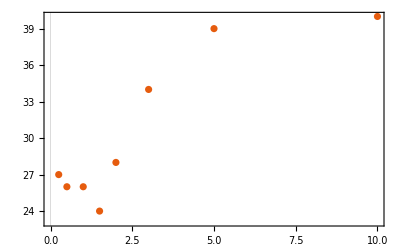

```mathematica
ListPlot[nbsol,PlotTheme->"Scientific",ImageSize->400,FrameStyle->Directive[Thick,16,Black],FrameLabel->{MaTeX["R / a_0",FontSize->18],MaTeX["\\text{Number of solutions}",FontSize->18]}]
```

#### FCI

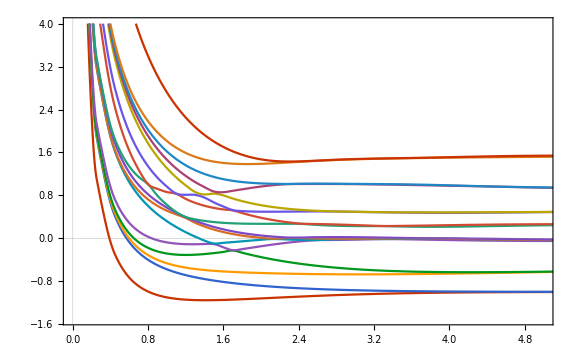

```mathematica
ListPlot[Table[nrjfci⟦;;,{1,n+1}⟧,{n,16}],PlotMarkers->False,plotOptions]
```

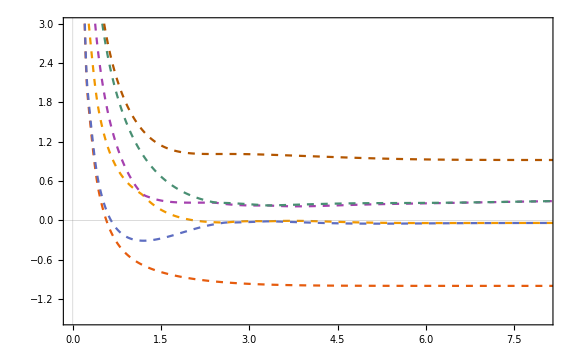

```mathematica
plotFCIt=ListPlot[Table[nrjfcit⟦;;,{1,n+1}⟧,{n,6}],PlotMarkers->False,PlotStyle->Dashed,plotOptions]
```

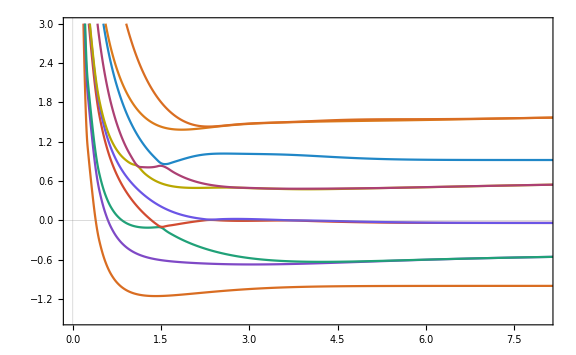

```mathematica
plotFCIs=ListPlot[Table[nrjfcis⟦;;,{1,n+1}⟧,{n,10}],PlotMarkers->False,PlotStyle->{RGBColor[0.8505, 0.4275, 0.13185],RGBColor[0.499929, 0.285875, 0.775177],RGBColor[0.12490296143062507, 0.63, 0.47103259454284074],RGBColor[0.823948950768196, 0.29474475384097976, 0.19291741323314934],RGBColor[0.42126358105951733, 0.33224185136428963, 0.9],RGBColor[0.7239916650994997, 0.6554435183443889, 0.],RGBColor[0.6746366424582266, 0.252, 0.45055901160272827],RGBColor[0.12582006271512805, 0.5293439498278976, 0.7809840752581536],RGBColor[0.8604677779867332, 0.4773388899336664, 0.10673699943582014]},plotOptions]
```

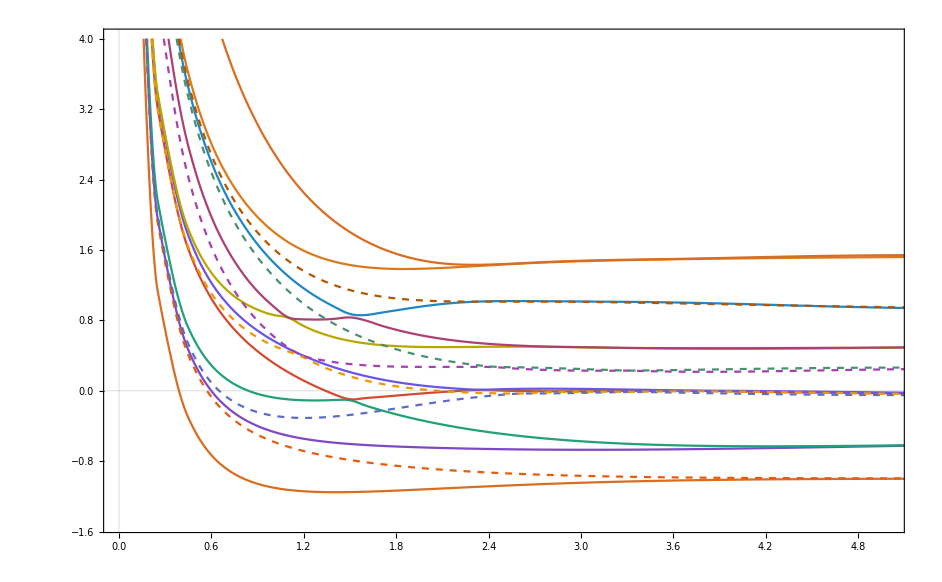

```mathematica
fullplotFCI=Show[plotFCIs,plotFCIt]
```

#### Triplet

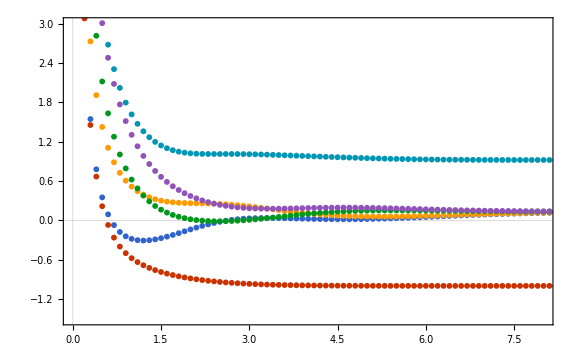

```mathematica
plotCASSCFtriplet=ListPlot[Table[nrjcasscft⟦;;,{1,n+1}⟧,{n,6}],Joined->False,plotOptions]
```

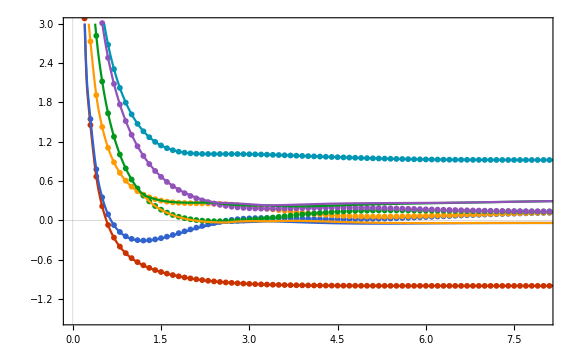

```mathematica
Show[plotCASSCFtriplet,ListPlot[Table[fcit⟦;;,{1,n+1}⟧,{n,6}],PlotMarkers->False,plotOptions]]
```

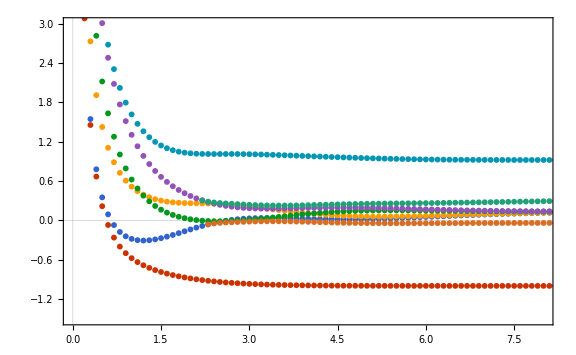

```mathematica
plotCASSCFSBtriplet1=ListPlot[Table[nrjcasscft⟦23;;,{1,n+1}⟧,{n,{7}}],PlotStyle->RGBColor[0.8505, 0.4275, 0.13185],Joined->False,plotOptions];
plotCASSCFSBtriplet2=ListPlot[Table[nrjcasscft⟦22;;,{1,n+1}⟧,{n,{8}}],PlotStyle->RGBColor[0.12490296143062507, 0.63, 0.47103259454284074],Joined->False,plotOptions];
fullplotCASSCFtriplet=Show[plotCASSCFtriplet,plotCASSCFSBtriplet1,plotCASSCFSBtriplet2]
```

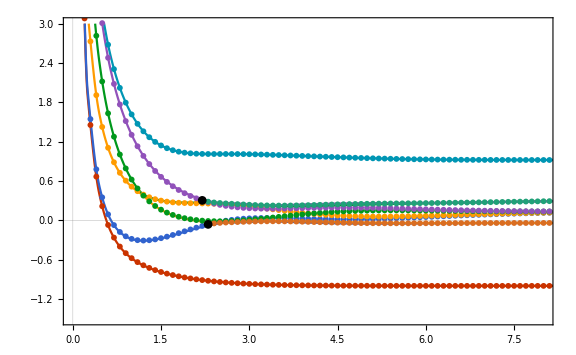

```mathematica
Show[ListPlot[Table[nrjfcit⟦;;,{1,n+1}⟧,{n,6}],PlotMarkers->False,plotOptions],fullplotCASSCFtriplet,ListPlot[{{2.2,0.3064401183281372},{2.3,-0.05913643980827099}},PlotMarkers->{"●",9},PlotStyle->RGBColor[0, 0, 0.]]]
```

The index of the solution are

```mathematica
Grid[{{"Triplet 1 RGBColor[0.790588, 0.201176, 0.]","(1,6)","R=9","(0,7)"},{"Triplet 2 RGBColor[0.192157, 0.388235, 0.807843]","(2,5)","R=2.3","(3,4)"},{"Triplet 3 RGBColor[1., 0.607843, 0.]","(2,5)","R=0.4","(3,4)"},{"Triplet 4 RGBColor[0., 0.596078, 0.109804]","(3,4)"},{"Triplet 5 RGBColor[0.567426, 0.32317, 0.729831]","(4,3)","R=2.2","(3,4)"},{"Triplet 6 RGBColor[0., 0.588235, 0.705882]","(5,2)","R=2.4","(3,4)","R=4.1","(5,2)"},{"SB Triplet 1 RGBColor[0.8505, 0.4275, 0.13185]","(2,5)"},{"SB Triplet 2 RGBColor[0.12490296143062507, 0.63, 0.47103259454284074]","(4,3)"}}]
```

Triplet 1 RGBColor[0.790588, 0.201176, 0.] | (1,6) | R=9 | (0,7) |  | 
Triplet 2 RGBColor[0.192157, 0.388235, 0.807843] | (2,5) | R=2.3 | (3,4) |  | 
Triplet 3 RGBColor[1., 0.607843, 0.] | (2,5) | R=0.4 | (3,4) |  | 
Triplet 4 RGBColor[0., 0.596078, 0.109804] | (3,4) |  |  |  | 
Triplet 5 RGBColor[0.567426, 0.32317, 0.729831] | (4,3) | R=2.2 | (3,4) |  | 
Triplet 6 RGBColor[0., 0.588235, 0.705882] | (5,2) | R=2.4 | (3,4) | R=4.1 | (5,2)
SB Triplet 1 RGBColor[0.8505, 0.4275, 0.13185] | (2,5) |  |  |  | 
SB Triplet 2 RGBColor[0.12490296143062507, 0.63, 0.47103259454284074] | (4,3) |  |  |  |

The following question is what is the difference between the orbitals of the new solutions and the previous ones?
We look at R=2.5

This is the second triplet (blue), we see that it’s symmetry preserved
This is the natural orbitals

```mathematica
{{0.886572, 0.374871, 0.195336,-0.927173},
{-0.741354, 0.292689, 0.917803, 1.095},
{0.886571, 0.374871,-0.195336, 0.927173},
{-0.741353, 0.292689,-0.917803,-1.095}}//MatrixForm
```

(0.886572 | 0.374871 | 0.195336 | -0.927173
-0.741354 | 0.292689 | 0.917803 | 1.095
0.886571 | 0.374871 | -0.195336 | 0.927173
-0.741353 | 0.292689 | -0.917803 | -1.095)

The occupations in the natural orbital basis are

```mathematica
{1, 1, 0, 0}
```

The energies of the natural orbitals are

```mathematica
{0.810114,-0.2554, 0.114018, 0.993616}
```

This is the CI vector in the natural orbital basis

```mathematica
{5.05666e-10, 0.707107,-0.707107,-8.46131e-10}
```

This is the first new solution (orange), this solution is symmetry-broken, therefore the black dot correspond to CASSCF Coulson-Fisher point.
This is the natural orbitals

```mathematica
{{0.237968,-0.319521,-0.140101, 1.28296},
{0.171297,-0.573888,-0.734971,-1.33334},
{-0.723278,-1.06845, 0.393948,-0.0665263},
{1.03557, 0.882443, 0.840825, 0.344331}}//MatrixForm
```

(0.237968 | -0.319521 | -0.140101 | 1.28296
0.171297 | -0.573888 | -0.734971 | -1.33334
-0.723278 | -1.06845 | 0.393948 | -0.0665263
1.03557 | 0.882443 | 0.840825 | 0.344331)

The occupations in the natural orbital basis are

```mathematica
{1, 1, 0, 0}
```

The energies of the natural orbitals are

```mathematica
{0.196316, 0.362979, 0.145013, 0.949759}
```

This is the CI vector in the natural orbital basis

```mathematica
{2.15555e-07, 0.707107,-0.707107,-1.85721e-07}
```

#### Singlet

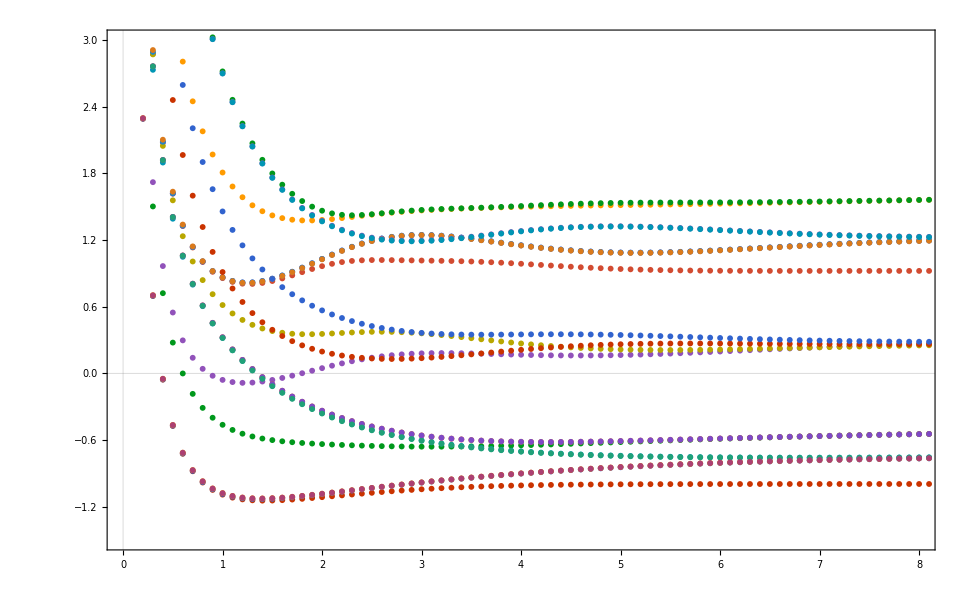

```mathematica
plotCASSCFsinglet=ListPlot[Table[nrjcasscfs⟦;;,{1,n+1}⟧,{n,21}],Joined->False,plotOptions]
```

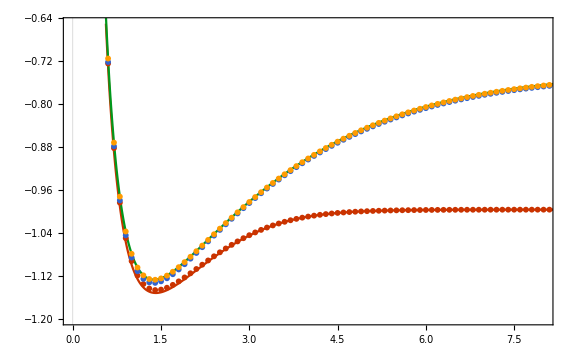

```mathematica
legend =LineLegend[{RGBColor[0.790588, 0.201176, 0.],RGBColor[0., 0.596078, 0.109804]},{ MaTeX["\\text{FCI}",FontSize->18], MaTeX["\\text{HF}",FontSize->18]},LegendLayout->"ReversedColumn"];
Show[ListPlot[Table[nrjfci⟦;;,{1,n+1}⟧,{n,1}],PlotRange->{{0,8},{-1.2,-0.65}},PlotMarkers->False,plotOptions],ListPlot[Table[nrjhf⟦;;,{1,n+1}⟧,{n,1}],PlotStyle->RGBColor[0., 0.596078, 0.109804],PlotMarkers->False,plotOptions,PlotLegends->Placed[legend,{Right,Bottom}]],ListPlot[Table[nrjcasscfs⟦;;,{1,n+1}⟧,{n,3}],Joined->False,plotOptions]]
```

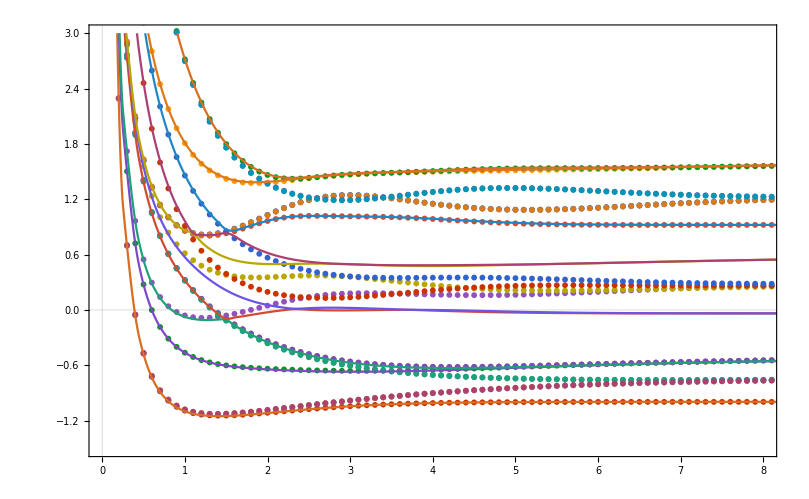

```mathematica
Show[plotCASSCFsinglet,plotFCIs]
```

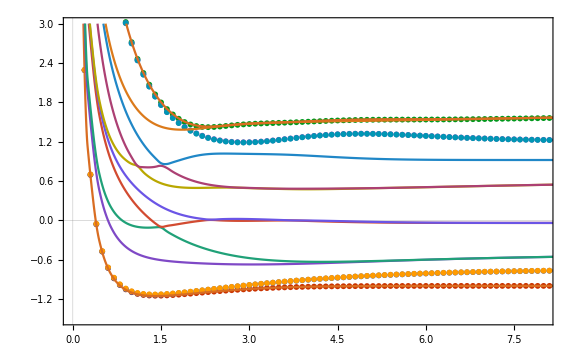

```mathematica
Show[ListPlot[Table[nrjcasscfs⟦;;,{1,n+1}⟧,{n,{1,2,3,19,20,21}}],Joined->False,plotOptions],ListPlot[Table[nrjfcis⟦;;,{1,n+1}⟧,{n,10}],PlotMarkers->False,PlotStyle->{RGBColor[0.8505, 0.4275, 0.13185],RGBColor[0.499929, 0.285875, 0.775177],RGBColor[0.12490296143062507, 0.63, 0.47103259454284074],RGBColor[0.823948950768196, 0.29474475384097976, 0.19291741323314934],RGBColor[0.42126358105951733, 0.33224185136428963, 0.9],RGBColor[0.7239916650994997, 0.6554435183443889, 0.],RGBColor[0.6746366424582266, 0.252, 0.45055901160272827],RGBColor[0.12582006271512805, 0.5293439498278976, 0.7809840752581536],RGBColor[0.8604677779867332, 0.4773388899336664, 0.10673699943582014]},plotOptions]]
```

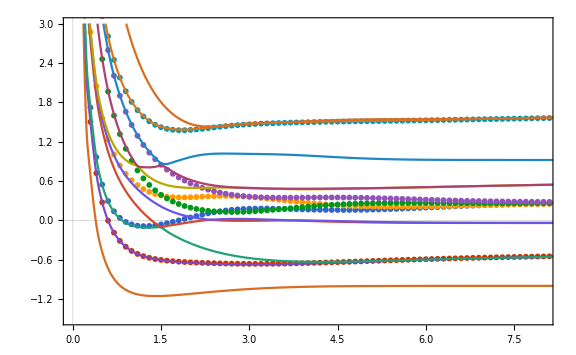

```mathematica
Show[ListPlot[Table[nrjcasscfs⟦;;,{1,n+1}⟧,{n,{4,5,12,16,17,18}}],Joined->False,plotOptions],ListPlot[Table[nrjfcis⟦;;,{1,n+1}⟧,{n,10}],PlotMarkers->False,PlotStyle->{RGBColor[0.8505, 0.4275, 0.13185],RGBColor[0.499929, 0.285875, 0.775177],RGBColor[0.12490296143062507, 0.63, 0.47103259454284074],RGBColor[0.823948950768196, 0.29474475384097976, 0.19291741323314934],RGBColor[0.42126358105951733, 0.33224185136428963, 0.9],RGBColor[0.7239916650994997, 0.6554435183443889, 0.],RGBColor[0.6746366424582266, 0.252, 0.45055901160272827],RGBColor[0.12582006271512805, 0.5293439498278976, 0.7809840752581536],RGBColor[0.8604677779867332, 0.4773388899336664, 0.10673699943582014]},plotOptions]]
```

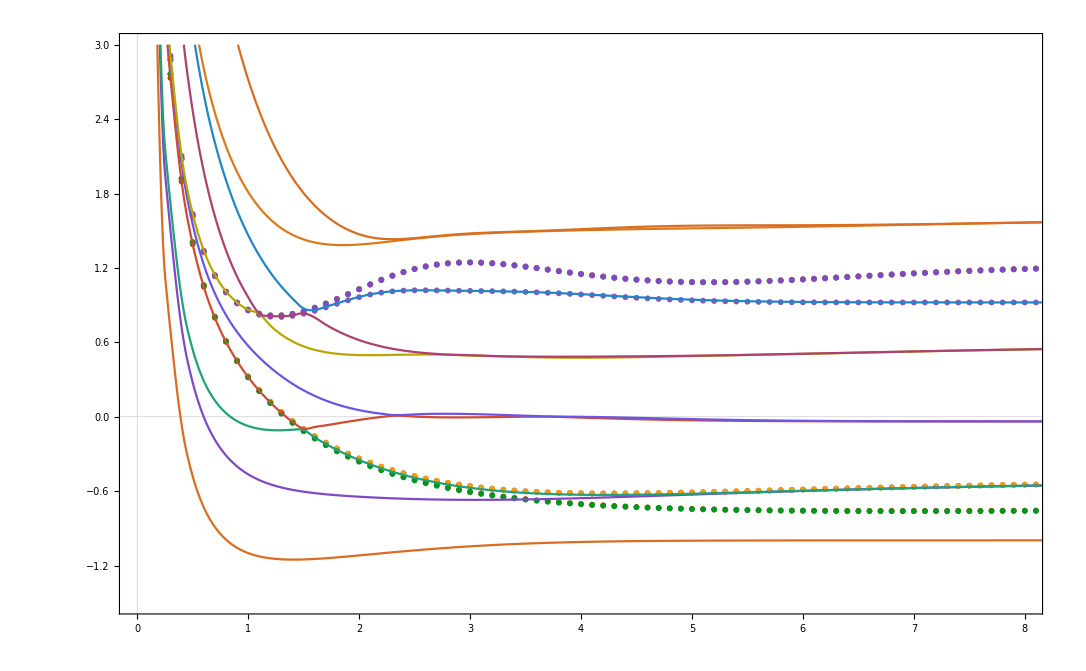

```mathematica
Show[ListPlot[Table[nrjcasscfs⟦;;,{1,n+1}⟧,{n,{6,7,8,9,10,11,14,15}}],Joined->False,plotOptions],ListPlot[Table[nrjfcis⟦;;,{1,n+1}⟧,{n,10}],PlotMarkers->False,PlotStyle->{RGBColor[0.8505, 0.4275, 0.13185],RGBColor[0.499929, 0.285875, 0.775177],RGBColor[0.12490296143062507, 0.63, 0.47103259454284074],RGBColor[0.823948950768196, 0.29474475384097976, 0.19291741323314934],RGBColor[0.42126358105951733, 0.33224185136428963, 0.9],RGBColor[0.7239916650994997, 0.6554435183443889, 0.],RGBColor[0.6746366424582266, 0.252, 0.45055901160272827],RGBColor[0.12582006271512805, 0.5293439498278976, 0.7809840752581536],RGBColor[0.8604677779867332, 0.4773388899336664, 0.10673699943582014]},plotOptions]]
```

```mathematica
nrjcasscfs[[18]]
```

{1.8,-1.13006,-1.10784,-1.10363,-0.627085,0.000656275,-0.273727,-0.256386,-0.256386,-0.278271,0.910641,0.950858,0.352127,-1.10358,0.950857,0.947252,0.251541,0.656604,1.37625,1.55056,1.48885,1.48452,-0.0152549,0.656603}

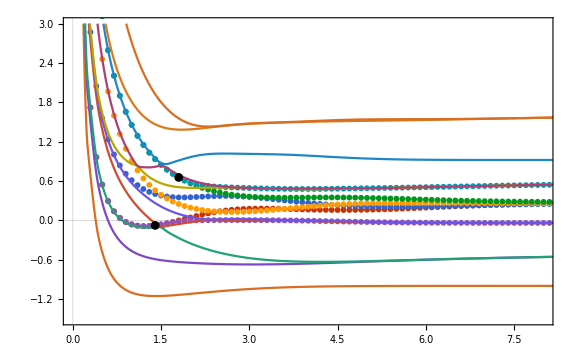

```mathematica
Show[ListPlot[Table[nrjcasscfs⟦;;,{1,n+1}⟧,{n,{5,12,16,17,22,23}}],Joined->False,plotOptions],ListPlot[Table[nrjfcis⟦;;,{1,n+1}⟧,{n,10}],PlotMarkers->False,PlotStyle->{RGBColor[0.8505, 0.4275, 0.13185],RGBColor[0.499929, 0.285875, 0.775177],RGBColor[0.12490296143062507, 0.63, 0.47103259454284074],RGBColor[0.823948950768196, 0.29474475384097976, 0.19291741323314934],RGBColor[0.42126358105951733, 0.33224185136428963, 0.9],RGBColor[0.7239916650994997, 0.6554435183443889, 0.],RGBColor[0.6746366424582266, 0.252, 0.45055901160272827],RGBColor[0.12582006271512805, 0.5293439498278976, 0.7809840752581536],RGBColor[0.8604677779867332, 0.4773388899336664, 0.10673699943582014]},plotOptions],ListPlot[{{1.4,-0.07421852370662729},{1.8,0.6566030240787438}},PlotMarkers->{"●",9},PlotStyle->RGBColor[0, 0, 0.]]]
```

#### Clean plots

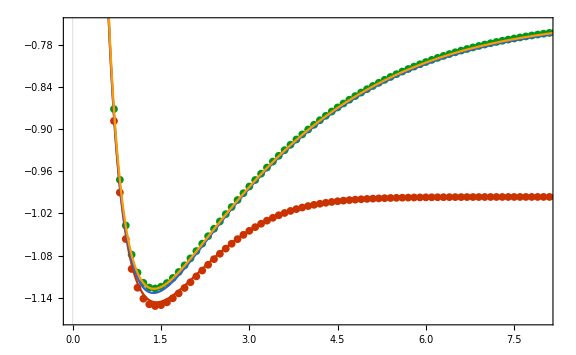

```mathematica
legend =LineLegend[{RGBColor[0.790588, 0.201176, 0.],RGBColor[0., 0.596078, 0.109804]},{ MaTeX["\\text{FCI}",FontSize->18], MaTeX["\\text{HF}",FontSize->18]},LegendLayout->"ReversedColumn"];
Show[ListPlot[Table[nrjfci⟦;;,{1,n+1}⟧,{n,1}],PlotRange->{{0,8},{-1.17,-0.75}},Joined->False,plotOptions],ListPlot[Table[nrjhf⟦;;,{1,n+1}⟧,{n,1}],PlotStyle->RGBColor[0., 0.596078, 0.109804],Joined->False,plotOptions,PlotLegends->Placed[legend,{Right,Bottom}]],ListPlot[Table[nrjcasscfs⟦;;,{1,n+1}⟧,{n,3}],PlotMarkers->False,plotOptions]]
```

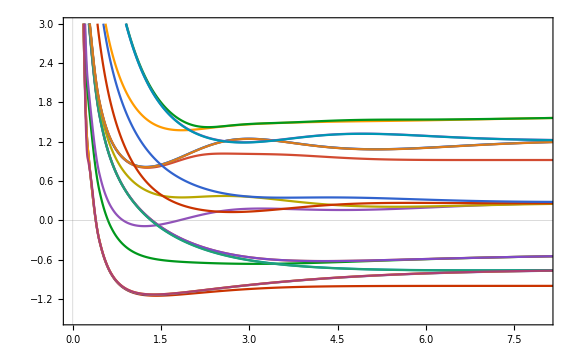

```mathematica
plotCASSCFsinglet=ListPlot[Table[nrjcasscfs⟦;;,{1,n+1}⟧,{n,21}],PlotMarkers->False,plotOptions]
```

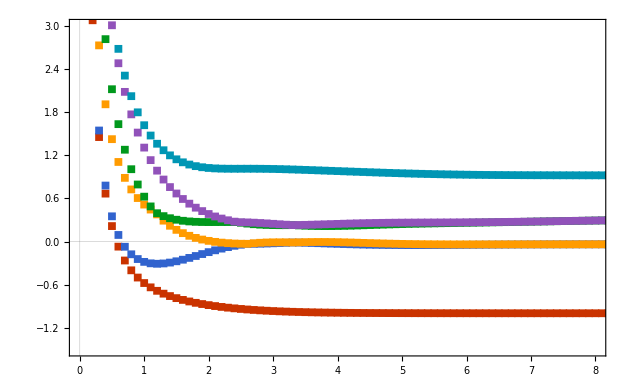

```mathematica
plotFCIt=ListPlot[Table[nrjfcit⟦;;,{1,n+1}⟧,{n,6}],PlotMarkers->{"■",8},Joined->False,plotOptions]
```

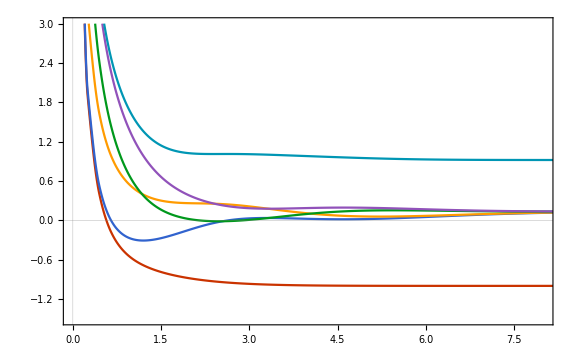

```mathematica
plotCASSCFtriplet=ListPlot[Table[nrjcasscft⟦;;,{1,n+1}⟧,{n,6}],PlotMarkers->False,plotOptions]
```

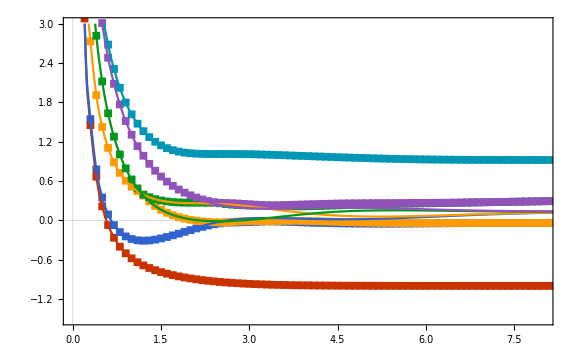

```mathematica
Show[plotFCIt,plotCASSCFtriplet]
```

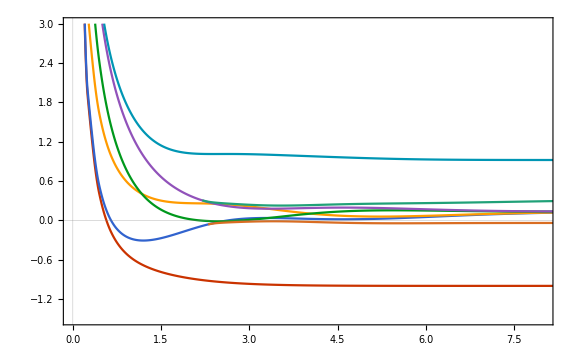

```mathematica
plotCASSCFSBtriplet1=ListPlot[Table[nrjcasscft⟦23;;,{1,n+1}⟧,{n,{7}}],PlotStyle->RGBColor[0.8505, 0.4275, 0.13185],PlotMarkers->False,plotOptions];
plotCASSCFSBtriplet2=ListPlot[Table[nrjcasscft⟦22;;,{1,n+1}⟧,{n,{8}}],PlotStyle->RGBColor[0.12490296143062507, 0.63, 0.47103259454284074],PlotMarkers->False,plotOptions];
fullplotCASSCFtriplet=Show[plotCASSCFtriplet,plotCASSCFSBtriplet1,plotCASSCFSBtriplet2]
```

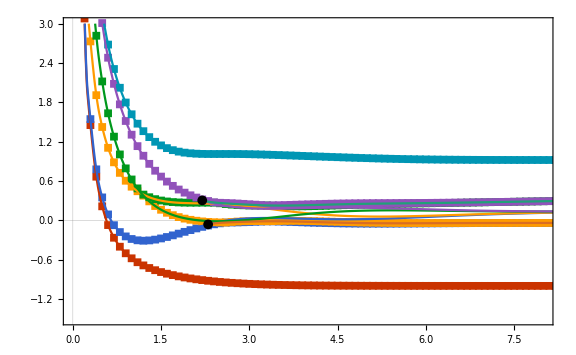

```mathematica
Show[plotFCIt,fullplotCASSCFtriplet,ListPlot[{{2.2,0.3064401183281372},{2.3,-0.05913643980827099}},PlotMarkers->{"●",10},PlotStyle->RGBColor[0, 0, 0.]]]
```

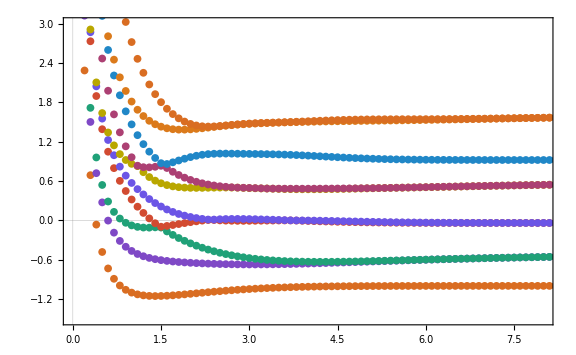

```mathematica
plotFCIs=ListPlot[Table[nrjfcis⟦;;,{1,n+1}⟧,{n,10}],Joined->False,PlotStyle->{RGBColor[0.8505, 0.4275, 0.13185],RGBColor[0.499929, 0.285875, 0.775177],RGBColor[0.12490296143062507, 0.63, 0.47103259454284074],RGBColor[0.823948950768196, 0.29474475384097976, 0.19291741323314934],RGBColor[0.42126358105951733, 0.33224185136428963, 0.9],RGBColor[0.7239916650994997, 0.6554435183443889, 0.],RGBColor[0.6746366424582266, 0.252, 0.45055901160272827],RGBColor[0.12582006271512805, 0.5293439498278976, 0.7809840752581536],RGBColor[0.8604677779867332, 0.4773388899336664, 0.10673699943582014]},plotOptions]
```

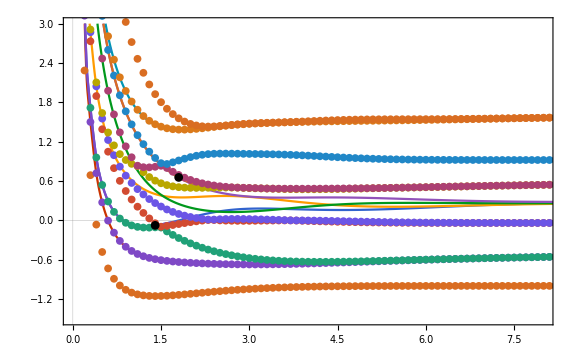

```mathematica
Show[ListPlot[Table[nrjcasscfs⟦;;,{1,n+1}⟧,{n,{4,5,12,16,17,18,23,22}}],PlotMarkers->False,plotOptions],plotFCIs,ListPlot[{{1.4,-0.07421852370662729},{1.8,0.6566030240787438}},PlotMarkers->{"●",9},PlotStyle->RGBColor[0, 0, 0.]]]
```

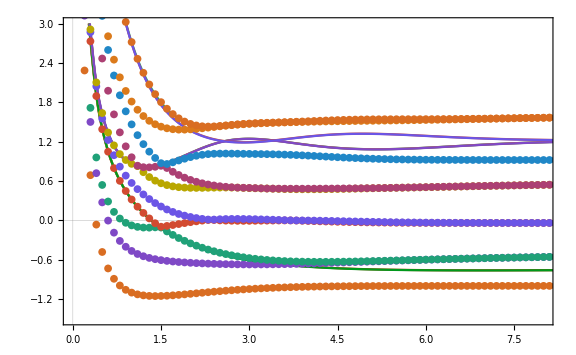

```mathematica
Show[ListPlot[Table[nrjcasscfs⟦;;,{1,n+1}⟧,{n,{6,7,8,9,10,11,14,15,19,20,21}}],PlotMarkers->False,plotOptions],plotFCIs]
```

### HHe^+ 6-31G

#### Nb sol

```mathematica
nbsol={{0.25,24},{0.5,26},{1,24},{1.5,24},{2,30},{3,27},{5,25},{10,35}};
```

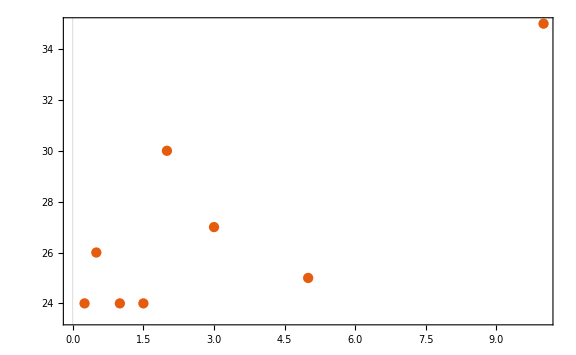

```mathematica
ListPlot[nbsol,PlotTheme->"Scientific",ImageSize->Large,FrameStyle->Directive[Thick,16,Black],FrameLabel->{MaTeX["R / a_0",FontSize->18],MaTeX["\\text{Number of solutions}",FontSize->18]}]
```

## Frozen core

We are investigating the effect of freezing core orbitals on the number of CASSCF solutions

#### HF

We start by looking at the HF molecule in the STO-3G basis set at R=2 bohr with a (2,2) CAS space

```mathematica
Grid[{{"Nb frozen",0,1,2,3},{"Nb sol",56,41,28,7},{"Max E",-43.09,-95.5484,-97.2559,-97.3993}}]
```

Nb frozen | 0 | 1 | 2 | 3
Nb sol | 56 | 41 | 28 | 7
Max E | -43.09 | -95.5484 | -97.2559 | -97.3993

```mathematica
nbsol={{0,56},{1,41},{2,28},{3,7}};
```

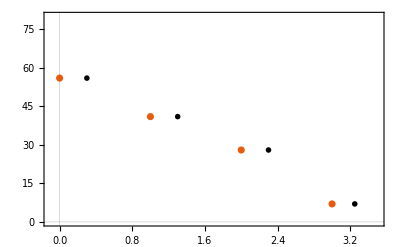

```mathematica
ListPlot[nbsol,PlotTheme->"Scientific",ImageSize->400,FrameStyle->Directive[Thick,16,Black],PlotRange->{{-0.1,3.5},{0,80}},FrameLabel->{MaTeX["\\text{Number of frozen orbitals}",FontSize->18],MaTeX["\\text{Number of solutions}",FontSize->18]},Epilog->{Inset[MaTeX["-43.09",FontSize->14],{0.3,56}],Inset[MaTeX["-95.55",FontSize->14],{1.3,41}],Inset[MaTeX["-97.26",FontSize->14],{2.3,28}],Inset[MaTeX["-97.4",FontSize->14],{3.25,7}]}]
```

#### Li^-

Now turning to the Li^- anion in the STO-3G basis set with a (4,2) CAS space.

Freezing the 1s orbital reduce the number of solutions from 46  to 5.

## Avoided crossing

In this section we want to have a look at the structure of the CASSCF landscape around an avoided crossing.

### Data LiH

#### FCI STO3G

```mathematica
fciLiHSTO3G={{2.0,-7.810437527707247,-7.6818727361951336,-7.667467877890125,-7.641150410682277,-7.641150410682231,-7.609930760565179,-7.609930760565172,-7.319383468266308,-7.227313750739027,-7.227185575442455},{2.1,-7.829190380303938,-7.6988964993177,-7.684457671780182,-7.657713917565474,-7.657713917565443,-7.627718504697745,-7.627718504697736,-7.336527813736305,-7.239433999747501,-7.238368474755397},{2.2,-7.844147823632392,-7.712997939234571,-7.698470071459701,-7.671226061006029,-7.671226061006022,-7.64241274756178,-7.6424127475617745,-7.352603280964571,-7.25029757932789,-7.248152651325908},{2.3,-7.855921699728967,-7.724695205752001,-7.710025009951295,-7.682214341702908,-7.682214341702892,-7.654558876052821,-7.654558876052816,-7.36828998998754,-7.2601989084071334,-7.256780895273938},{2.4,-7.86501600320385,-7.7344047819408015,-7.719540242340599,-7.691106430158191,-7.691106430158184,-7.664596729301721,-7.664596729301708,-7.383982862502176,-7.269372955174465,-7.264445574647938},{2.5,-7.87184794927848,-7.74246304442273,-7.7273527806921125,-7.698250894348592,-7.6982508943485835,-7.672882588757299,-7.672882588757298,-7.399861346796732,-7.278009390476053,-7.271302712670438},{2.6,-7.876765264847782,-7.749143501640928,-7.733736148786175,-7.703933870410314,-7.70393387041031,-7.679706818576097,-7.6797068185760935,-7.415953013503781,-7.286261350893836,-7.277481484606703},{2.7,-7.880059987810478,-7.754670333920698,-7.73891400651492,-7.708392163352759,-7.708392163351444,-7.685307727358971,-7.685307727358962,-7.432187618287964,-7.29425040466262,-7.283090736202087},{2.8,-7.881979279406153,-7.759228891668343,-7.743070757118346,-7.7118233794980995,-7.711823379497051,-7.689882320147387,-7.68988232014738,-7.448440118992481,-7.302068878426617,-7.288223422773411},{2.9,-7.88273382044614,-7.762973764381845,-7.746359724795014,-7.7143936933790345,-7.714393693378194,-7.69359458575262,-7.693594585752607,-7.464562676037912,-7.3097805947178065,-7.292959509369344},{3.0,-7.8825043293696435,-7.76603495352437,-7.748909421699153,-7.716243788616216,-7.7162437886155395,-7.696581880925134,-7.6965818809251285,-7.480406740045137,-7.317421132250189,-7.29736771038888},{3.1,-7.881446657567209,-7.768522590192904,-7.750828338343429,-7.7174934204950985,-7.717493420491164,-7.69895986925514,-7.6989598692426116,-7.495836929796751,-7.324998751515033,-7.301506375902302},{3.2,-7.8796958209444075,-7.770530548156385,-7.752208606402338,-7.718244951495141,-7.718244951491201,-7.700826371609798,-7.700826371597039,-7.510738595416122,-7.3324969338331005,-7.305423798414203},{3.3,-7.877369237127309,-7.772139222950879,-7.753128806828806,-7.7185861242198195,-7.718586124215816,-7.702264397654306,-7.702264397641762,-7.525020860912419,-7.339878965110903,-7.3091581976030975},{3.4000000000000004,-7.874569364350835,-7.773417682441417,-7.753656133472145,-7.718592265725173,-7.718592265721098,-7.703344558493248,-7.703344558481536,-7.538616670952717,-7.347094266525957,-7.3127376314630865},{3.5,-7.871385882596782,-7.774425343944176,-7.753848073600865,-7.718328064033819,-7.718328064029721,-7.704127008054939,-7.7041270080432485,-7.55148103323453,-7.3540855326599415,-7.3161800673687205},{3.6,-7.867897517371817,-7.775213295575791,-7.753753729930801,-7.717849019395103,-7.717849019394973,-7.7046630225759865,-7.704663022575979,-7.563588321877696,-7.3607954819483,-7.319493809903501},{3.7,-7.864173578248254,-7.775825351936474,-7.753414881372047,-7.717202645994345,-7.717202645994256,-7.704996299907229,-7.704996299907224,-7.574929228165445,-7.3671722343532675,-7.3226784119067165},{3.8,-7.860275263643538,-7.776298913599224,-7.75286685838057,-7.716429480902218,-7.71642948090216,-7.705164040553259,-7.705164040553254,-7.585507726859782,-7.37317282929559,-7.325726093200466},{3.9000000000000004,-7.856256768769149,-7.776665683949719,-7.752139292736019,-7.7155639433604355,-7.715563943360398,-7.705197856488106,-7.705197856488096,-7.595338268279602,-7.378764908786748,-7.328623577873906},{4.0,-7.852166222309215,-7.77695228410877,-7.751256787609584,-7.714635077197171,-7.714635077197142,-7.705124544076897,-7.705124544076892,-7.604443298465133,-7.383926927536207,-7.33135416711397},{4.1,-7.848046469148362,-7.7771807961567,-7.750239542652825,-7.713667201109957,-7.713667201109943,-7.704966747017569,-7.704966747017555,-7.612851141094663,-7.388647373818986,-7.333899818296252},{4.2,-7.843935710505545,-7.777369256162507,-7.749103958976529,-7.7126804851391055,-7.7126804851390895,-7.704743529536375,-7.7047435295363575,-7.620594233919285,-7.392923450655766,-7.336243012801449},{4.300000000000001,-7.83986800925162,-7.7775321114030875,-7.747863240271202,-7.711691466558169,-7.711691466558141,-7.704470874612819,-7.704470874612803,-7.627707690463585,-7.396759559277604,-7.338368253855291},{4.4,-7.835873667085412,-7.7776806505167055,-7.746527998417225,-7.710713514457696,-7.710713514457689,-7.704162118307316,-7.704162118307307,-7.634228147784192,-7.400165807878315,-7.337931298803648},{4.5,-7.831979481707044,-7.777823411056784,-7.745106864315958,-7.7097572493700115,-7.709757249370004,-7.703828328604945,-7.703828328604941,-7.640192858405251,-7.403156669769911,-7.34327872608828},{4.6,-7.828208896240248,-7.777966565873747,-7.743607097185684,-7.70883092225062,-7.7088309222506055,-7.703478635395449,-7.703478635395438,-7.645638986146876,-7.4057498454342525,-7.3484095270201575},{4.7,-7.824582059148936,-7.778114287744149,-7.742035177857408,-7.707940755846623,-7.707940755846607,-7.703120517061482,-7.703120517061468,-7.6506030691303195,-7.407965339717807,-7.353349677790463},{4.800000000000001,-7.821115820247895,-7.778269090542128,-7.740397364686574,-7.707091250779598,-7.707091250779591,-7.702760048475756,-7.702760048475749,-7.6551206180500095,-7.409824742708736,-7.358118789625863},{4.9,-7.817823695054771,-7.778432144764882,-7.738700185124336,-7.706285458380367,-7.706285458380363,-7.702402114564644,-7.702402114564637,-7.659225822632066,-7.411350693779069,-7.362729150769531},{5.0,-7.814715833984325,-7.778603565235452,-7.736950833602959,-7.705525222278975,-7.705525222278974,-7.702050593950283,-7.702050593950274,-7.662951343963767,-7.412566508533409,-7.367185300739864},{5.1,-7.81179903265336,-7.77878266915995,-7.735157448486403,-7.704811390845956,-7.704811390845947,-7.701708515872419,-7.7017085158724115,-7.666328174671833,-7.413495955012227,-7.371484235082235},{5.2,-7.809076813939797,-7.7789682032951575,-7.733329248520814,-7.704144002701902,-7.704144002701899,-7.701378194396376,-7.701378194396366,-7.669385552656632,-7.414163177613696,-7.375616197885426},{5.300000000000001,-7.806549601042572,-7.779158539700469,-7.731476521366285,-7.703522447601871,-7.703522447601869,-7.701061342986287,-7.701061342986283,-7.6721509171862285,-7.414592786031391,-7.379565876392502},{5.4,-7.8042149863857855,-7.779351840327777,-7.729610472465023,-7.702945604967542,-7.702945604967537,-7.700759172397063,-7.700759172397062,-7.674649898626447,-7.414810155891059,-7.383313702897658},{5.5,-7.802068085833117,-7.779546191476564,-7.727742957422153,-7.70241196274532,-7.702411962745311,-7.700472474446448,-7.700472474446443,-7.676906334942821,-7.414842035266069,-7.386836906954413},{5.6,-7.800101955241492,-7.77973970986504,-7.725886133421658,-7.701919717762215,-7.701919717762206,-7.700201693858058,-7.700201693858051,-7.678942309545902,-7.414717628744047,-7.390109928206814},{5.7,-7.798308039004643,-7.7799306226645095,-7.724052070623151,-7.701466861037098,-7.7014668610370896,-7.699946990009653,-7.699946990009651,-7.680778205980034,-7.414470448937913,-7.393103760158551},{5.800000000000001,-7.796676618866655,-7.780117324313858,-7.722252364827929,-7.701051248813162,-7.701051248813155,-7.6997082900983145,-7.699708290098307,-7.68243277571322,-7.414141356345112,-7.395783747097282},{5.9,-7.795197235152431,-7.780298413220731,-7.72049778636449,-7.700670661472188,-7.700670661472186,-7.699485334924493,-7.699485334924491,-7.683923215771523,-7.413783118777362,-7.398105512082267},{6.0,-7.793859059833377,-7.780472711582094,-7.7187979907470545,-7.700322851777393,-7.700322851777388,-7.699277718331514,-7.699277718331503,-7.685265253369382,-7.413465529354381,-7.400010027168559},{6.1000000000000005,-7.792651209365478,-7.780639271523179,-7.717161305842695,-7.700005583815094,-7.700005583815083,-7.699084921043627,-7.699084921043624,-7.686473235028985,-7.413275136342839,-7.401423840501298},{6.2,-7.791562993177497,-7.78079737058739,-7.715594600159767,-7.699716663864988,-7.699716663864981,-7.698906339601395,-7.6989063396013915,-7.687560217997968,-7.413294881357604,-7.4022792324179925},{6.3,-7.790584100071838,-7.780946499342079,-7.714103228804902,-7.699453964308379,-7.6994539643083755,-7.698741310933464,-7.69874131093346,-7.688538062089794,-7.413557261770502,-7.402560745285947},{6.4,-7.789704728641402,-7.781086343529189,-7.71269104771547,-7.699215441555655,-7.699215441555648,-7.6985891330467044,-7.698589133046701,-7.689417520369972,-7.41401352353846,-7.402335629015878},{6.5,-7.788915670582327,-7.781216762821174,-7.711360483931051,-7.698999148911767,-7.698999148911762,-7.698449082261147,-7.698449082261138,-7.690208327420317,-7.4145655416904805,-7.401721580959586},{6.6000000000000005,-7.788208355830667,-7.781337767866784,-7.710112648010437,-7.698803245163148,-7.698803245163143,-7.6983204273788,-7.698320427378793,-7.690919284186981,-7.41512007506828,-7.4008321188314845},{6.7,-7.787574868432514,-7.78144949695193,-7.70894747522195,-7.698625999619867,-7.69862599961986,-7.698202441146857,-7.698202441146855,-7.691558338684289,-7.41561292354389,-7.39975207530522},{6.800000000000001,-7.787007940846564,-7.781552193273026,-7.707863883314715,-7.698465794261983,-7.698465794261981,-7.698094409351235,-7.698094409351233,-7.692132662055187,-7.416007177214445,-7.398539034863196},{6.9,-7.786500933182774,-7.781646183533848,-7.7068599365314,-7.69832112355447,-7.698321123554468,-7.697995637855291,-7.697995637855287,-7.692648719689869,-7.416284690852494,-7.397231585345843},{7.0,-7.7860478024989614,-7.781731858334531,-7.705933007572558,-7.698190592431514,-7.69819059243151,-7.697905457875731,-7.697905457875725,-7.693112337268763,-7.416438929037765,-7.395856240712221},{7.1000000000000005,-7.785643066156954,-7.7818096546251905,-7.70507993132019,-7.698072912883491,-7.6980729128834895,-7.697823229765019,-7.697823229765017,-7.693528761729683,-7.416470288351898,-7.3944319285253375},{7.2,-7.785281762068961,-7.781880040342158,-7.704297145844898,-7.6979668995169535,-7.697966899516948,-7.697748345545736,-7.697748345545732,-7.693902717262124,-7.416383237401373,-7.392972699458391},{7.300000000000001,-7.784959408176118,-7.781943501228942,-7.7035808184093915,-7.697871464399284,-7.697871464399271,-7.697680230417499,-7.697680230417496,-7.694238456508335,-7.416184579744225,-7.391489350792854},{7.4,-7.784671962298033,-7.782000529760131,-7.7029269546787695,-7.69778561155926,-7.697785611559256,-7.697618343432508,-7.697618343432502,-7.6945398072046345,-7.415882382811791,-7.389990417186672},{7.5,-7.784415783542963,-7.782051616030127,-7.702331491281187,-7.697708430696819,-7.697708430696817,-7.697562177510791,-7.697562177510784,-7.694810214531451,-7.415485304027723,-7.388482793533188},{7.6000000000000005,-7.78418759578127,-7.782097240433447,-7.701790372151641,-7.697639091873689,-7.697639091873673,-7.697511258943085,-7.6975112589430745,-7.695052779461215,-7.415002159602005,-7.3869721403496875},{7.7,-7.78398445352115,-7.782137867945618,-7.701299609806863,-7.697576839232449,-7.697576839232447,-7.697465146506696,-7.697465146506689,-7.695270293400938,-7.414441646228308,-7.385463157454376},{7.800000000000001,-7.7838037103343805,-7.7821739438078446,-7.700855333019215,-7.697520985365863,-7.697520985365859,-7.6974234302994375,-7.697423430299425,-7.695465269426373,-7.413812162177843,-7.383959775636308},{7.9,-7.783642989848786,-7.782205890422446,-7.700453822530356,-7.697470905815495,-7.697470905815486,-7.6973857303780235,-7.697385730378018,-7.695639970397314,-7.413121694840067,-7.382465295758875},{8.0,-7.783500159242612,-7.782234105275434,-7.700091536491064,-7.697426033845929,-7.697426033845927,-7.697351695270985,-7.697351695270973,-7.695796434232184,-7.412377753694828,-7.38098249315656},{8.100000000000001,-7.783373305124506,-7.782258959716886,-7.69976512726781,-7.697385855526161,-7.697385855526157,-7.697321000421638,-7.697321000421637,-7.695936496605155,-7.411587334839962,-7.379513698424636},{8.2,-7.783260711653068,-7.782280798445048,-7.699471451148223,-7.697349905135039,-7.697349905135032,-7.6972933466046785,-7.69729334660467,-7.69606181131305,-7.410756907616079,-7.378060861668276},{8.3,-7.783160840731322,-7.78229993955708,-7.69920757232036,-7.697317760896257,-7.697317760896255,-7.697268458349122,-7.697268458349119,-7.696173868540879,-7.409892416702075,-7.3766256048186145},{8.4,-7.783072314118846,-7.782316675046599,-7.698970762368972,-7.697289041039631,-7.6972890410396255,-7.697246082392211,-7.697246082392209,-7.696274011238093,-7.4089992949370425,-7.375209265089372},{8.5,-7.782993897286667,-7.782331271643803,-7.69875849630706,-7.697263400179071,-7.697263400179064,-7.697225986181535,-7.697225986181533,-7.696363449799009,-7.408082483415477,-7.373812931677684},{8.600000000000001,-7.782924484866453,-7.782343971909445,-7.698568446052541,-7.6972405259929255,-7.697240525992922,-7.697207956437231,-7.697207956437222,-7.696443275224346,-7.407146456317075,-7.372437477169991},{8.7,-7.782863087542575,-7.782354995508246,-7.69839847207464,-7.697220136189777,-7.69722013618977,-7.697191797781544,-7.697191797781537,-7.696514470924059,-7.406195248597611,-7.37108358472172},{8.8,-7.782808820249728,-7.782364540599171,-7.698246613809199,-7.697201975740614,-7.697201975740605,-7.697177331439991,-7.697177331439984,-7.696577923306179,-7.405232485155648,-7.369751771758452},{8.9,-7.782760891549499,-7.782372785291994,-7.698111079320778,-7.697185814357981,-7.697185814357976,-7.697164394015299,-7.697164394015294,-7.696634431282147,-7.40426141046175,-7.368442410792427},{9.0,-7.782718594069734,-7.7823798891289995,-7.697990234587075,-7.69717144420238,-7.697171444202378,-7.697152836334209,-7.697152836334204,-7.6966847148051185,-7.403284917914711,-7.367155747790231},{9.100000000000001,-7.782681295901406,-7.782385994559157,-7.697882592694644,-7.697158677796792,-7.697158677796788,-7.697142522365289,-7.697142522365286,-7.696729422546537,-7.402305578402921,-7.3658919184336575},{9.2,-7.78264843285669,-7.782391228379608,-7.697786803163159,-7.697147346131072,-7.697147346131065,-7.697133328204948,-7.697133328204939,-7.696769138800414,-7.4013256677150805,-7.3646509625857925},{9.3,-7.782619501503863,-7.78239570312606,-7.697701641560025,-7.697137296939033,-7.697137296939028,-7.697125141130156,-7.69712514113014,-7.696804389707143,-7.400347192556382,-7.3634328371009135},{9.4,-7.782594052898895,-7.78239951839737,-7.697625999513684,-7.697128393131458,-7.697128393131451,-7.697117858709389,-7.697117858709384,-7.696835648857003,-7.3993719150408435,-7.362237427281221},{9.5,-7.7825716869454435,-7.782402762105809,-7.6975588752081965,-7.697120511350644,-7.6971205113506365,-7.69711138797528,-7.697111387975273,-7.696863342355252,-7.398401375580808,-7.361064557062649},{9.600000000000001,-7.782552047320296,-7.782405511646447,-7.697499364421507,-7.697113540799547,-7.697113540799537,-7.697105644710922,-7.69710564471092,-7.696887853379428,-7.397436914153831,-7.35991399805731},{9.7,-7.782534816907442,-7.782407834983984,-7.697446652039674,-7.697107381805281,-7.697107381805272,-7.697100552586247,-7.6971005525862415,-7.696909526323425,-7.3964796899721845,-7.358785477658092},{9.8,-7.782519713690762,-7.7824097916545,-7.697400004248687,-7.697101945011328,-7.697101945011315,-7.697096042653703,-7.697096042653698,-7.696928670523768,-7.395530699595471,-7.357678686169175},{9.9,-7.782506487058848,-7.7824114336847305,-7.697358761182894,-7.697097150268386,-7.69709715026838,-7.697092052640688,-7.697092052640686,-7.696945563645282,-7.394590793552066,-7.356593283195467},{10.0,-7.782494914483002,-7.782412806430897,-7.697322330158017,-7.6970929257328775,-7.697092925732877,-7.697088526391754,-7.697088526391754,-7.696960454744268,-7.393660691544653,-7.355528903261976},{10.1,-7.782484798529543,-7.782413949339997,-7.697290179417633,-7.697089207256313,-7.69708920725631,-7.697085413332608,-7.697085413332603,-7.69697356704193,-7.392740996324818,-7.354485160827394},{10.200000000000001,-7.782475964175565,-7.782414896638602,-7.697261832384268,-7.697085937273161,-7.697085937273146,-7.697082667978991,-7.697082667978981,-7.696985100447606,-7.391832206351514,-7.353461654622167},{10.3,-7.782468256398212,-7.782415677953046,-7.6972368623767595,-7.69708306447028,-7.697083064470277,-7.697080249472189,-7.697080249472187,-7.696995233826795,-7.390934727188145,-7.3524579715646485},{10.4,-7.782461538006201,-7.782416318865257,-7.697214887768641,-7.697080543035178,-7.697080543035168,-7.697078121159201,-7.6970781211591905,-7.69700412708128,-7.390048881996398,-7.351473690117266},{10.5,-7.782455687699369,-7.782416841411272,-7.697195567588469,-7.6970783322339775,-7.697078332233973,-7.697076250208807,-7.697076250208804,-7.697011923092337,-7.389174920899939,-7.350508383247573},{10.6,-7.782450598324268,-7.782417264524164,-7.697178597472685,-7.697076395570312,-7.697076395570307,-7.697074607237252,-7.697074607237251,-7.6970187492260385,-7.388313029470196,-7.349561621002297},{10.700000000000001,-7.78244617531018,-7.782417604428722,-7.697163706004335,-7.697074700816059,-7.697074700816056,-7.697073165991952,-7.697073165991948,-7.697024719104922,-7.387463336443625,-7.348632972717528},{10.8,-7.782442335271571,-7.782417874991251,-7.697150651382552,-7.697073219134892,-7.6970732191348885,-7.697071903042463,-7.697071903042456,-7.697029933879924,-7.38662592060892,-7.3477220089424895},{10.9,-7.78243900475391,-7.782418088028757,-7.697139218393118,-7.697071925071879,-7.697071925071872,-7.697070797504047,-7.697070797504036,-7.697034483531309,-7.385800817003217,-7.346828303067446},{11.0,-7.782436119114142,-7.782418253581665,-7.697129215667741,-7.697070796002135,-7.697070796002133,-7.697069830784202,-7.6970698307842005,-7.6970384480034255,-7.384988022531503,-7.345951432709206},{11.1,-7.782433621483952,-7.7824183801461135,-7.697120473201569,-7.697069811844217,-7.6970698118442,-7.697068986330159,-7.697068986330155,-7.697041898262225,-7.384187500925672,-7.345090980892935},{11.200000000000001,-7.7824314620462784,-7.78241847492444,-7.697112840113162,-7.6970689548785955,-7.697068954878592,-7.697068249523213,-7.69706824952321,-7.697044897207452,-7.383399187255088,-7.344246537002587},{11.3,-7.782429596899414,-7.782418543930708,-7.69710618262551,-7.697068209425301,-7.6970682094252965,-7.697067607277728,-7.6970676072777255,-7.6970475005481775,-7.382622991915251,-7.343417697598924},{11.4,-7.782427987682576,-7.782418592231206,-7.697100382219067,-7.697067561640445,-7.6970675616404405,-7.697067048076104,-7.697067048076101,-7.69704975754397,-7.381858804211415,-7.342604067054984},{11.5,-7.782426600776433,-7.782418624046401,-7.69709533402634,-7.697066999307732,-7.697066999307725,-7.69706656170839,-7.697066561708388,-7.697051711721011,-7.381106495534275,-7.341805258078701},{11.600000000000001,-7.782425406771754,-7.782418642880888,-7.697090945310996,-7.697066511662508,-7.697066511662499,-7.6970661391497215,-7.697066139149715,-7.697053401465931,-7.38036592219877,-7.341020892100474},{11.700000000000001,-7.782424379969805,-7.782418651630384,-7.697087134182233,-7.697066089216287,-7.697066089216283,-7.697065772431548,-7.69706577243154,-7.69705486061545,-7.379636927953039,-7.340250599567588},{11.8,-7.7824234979375415,-7.7824186526739005,-7.697083828363116,-7.697065723686417,-7.697065723686402,-7.697065454526881,-7.697065454526878,-7.697056118939788,-7.378919346210813,-7.339494020157885},{11.9,-7.782422741114183,-7.7824186479536115,-7.697080964151148,-7.69706540770006,-7.697065407700054,-7.697065179245563,-7.697065179245549,-7.69705720259771,-7.378213002017253,-7.338750802889707}};
```

#### FCI 6-31G

```mathematica
fciLiH631G={{2.0,-7.917105267954341,-7.800227264057961,-7.785002198812789,-7.760039507135717,-7.760039507106079,-7.743363685476947,-7.74336368547233,-7.695622239627159,-7.660519450383882,-7.621206783177744},{2.1,-7.935885249496115,-7.818301673038965,-7.803032902043711,-7.778113813656722,-7.7781138136270105,-7.762004489706982,-7.7620044896991285,-7.713330719127043,-7.677919974695909,-7.638677243517874},{2.2,-7.951092380434032,-7.833425646981542,-7.8180669217484375,-7.793151338538502,-7.793151338510162,-7.777566475166122,-7.777566475155531,-7.727895112786829,-7.692107490969393,-7.653148060064895},{2.3,-7.96332720912058,-7.846115009451848,-7.830627699864127,-7.805672411956982,-7.805672411930857,-7.790585030627513,-7.790585030615462,-7.739868407247084,-7.703632927188588,-7.665143515187294},{2.4,-7.973084154671909,-7.856790919223991,-7.841142587591069,-7.81610229971659,-7.816102299693139,-7.801496047667518,-7.801496047655226,-7.749700653163208,-7.712944674285147,-7.675091225491441},{2.5,-7.980770862217631,-7.8657977166094755,-7.84996060132337,-7.824789258801316,-7.824789258780666,-7.810655145683406,-7.810655145671745,-7.757760004307404,-7.720409150387712,-7.6833407226937736},{2.6,-7.986724253710966,-7.873417452869157,-7.857367033805101,-7.832019259010584,-7.832019258992675,-7.8183532380988225,-7.818353238088205,-7.764349936320489,-7.726327409820755,-7.690178493253402},{2.7,-7.991223728197383,-7.8798817276313,-7.8635954888574116,-7.838027957320856,-7.83802795730549,-7.824829126479273,-7.824829126469867,-7.769723290130612,-7.730948421270874,-7.695840147467482},{2.8,-7.99450191791135,-7.8853813070665755,-7.868837750759321,-7.8430103867416,-7.843010386728501,-7.830279649420824,-7.830279649412665,-7.774093675612901,-7.734479567664005,-7.700520228831902},{2.9,-7.996753374429985,-7.8900738966355695,-7.873251814359086,-7.8471287407602235,-7.847128740749105,-7.834867811604357,-7.834867811597387,-7.77764470272879,-7.737094870651753,-7.704380073758002},{3.0,-7.998141534081851,-7.8940903831387566,-7.876968361679134,-7.850518584540593,-7.85051858453118,-7.838729255427733,-7.8387292554218195,-7.7805374410884625,-7.738941390828764,-7.7075540705011285},{3.1,-7.998804282692066,-7.897539820574116,-7.880095946128134,-7.85329378593613,-7.853293785928167,-7.841977390660259,-7.841977390655221,-7.78291641278055,-7.740144196549461,-7.710154622005699},{3.2,-7.998858402273459,-7.900513399306201,-7.88272512044999,-7.855550422065381,-7.8555504220586165,-7.844707453890612,-7.844707453886292,-7.784914275708815,-7.740810227845106,-7.7122760763272336},{3.3,-7.998403138467384,-7.903087603365576,-7.88493171510397,-7.857369878051734,-7.857369878045989,-7.846999725790382,-7.846999725786616,-7.786655141419771,-7.741031319908978,-7.713997846729305},{3.4000000000000004,-7.9975230826921795,-7.905326726530486,-7.886779441774413,-7.8588213154230555,-7.85882131541819,-7.848922091861921,-7.848922091858606,-7.788256200088419,-7.740886594559653,-7.715386902591726},{3.5,-7.996290521205318,-7.907284886013,-7.888321965425431,-7.859963651462276,-7.859963651458137,-7.850532093916571,-7.850532093913576,-7.789827072317103,-7.740444382261924,-7.71649977456251},{3.6,-7.994767367682523,-7.90900764462581,-7.889604560173372,-7.860847159533063,-7.86084715952956,-7.8518785867703835,-7.851878586767669,-7.791466287129482,-7.739763800395775,-7.717384184892983},{3.7,-7.993006767291515,-7.91053332879641,-7.890665440366288,-7.861514774848869,-7.861514774845915,-7.853003088063769,-7.853003088061344,-7.793254862324421,-7.738896085241638,-7.7180803873796435},{3.8,-7.991054438253339,-7.9118941107732,-7.8915368387245755,-7.862003170086159,-7.862003170084615,-7.853940888294017,-7.853940888293132,-7.7952483680336035,-7.737885752785059,-7.724303228533224},{3.9000000000000004,-7.988949800463634,-7.913116907977215,-7.892245887734684,-7.862343649884729,-7.862343649883576,-7.85472197220914,-7.854721972208151,-7.797470566195835,-7.736771646671195,-7.727954603485066},{4.0,-7.9867269288927485,-7.914224140297058,-7.892815348023603,-7.862562901644408,-7.862562901643171,-7.855371790561215,-7.855371790555754,-7.799912207981318,-7.735587921357974,-7.730651196242075},{4.1,-7.984415360664239,-7.915234376310948,-7.8932642175810335,-7.862683631283974,-7.862683631283969,-7.855911912100603,-7.855911912100596,-7.802536589790196,-7.734365003172194,-7.732508143421458},{4.2,-7.982040778472389,-7.916162891625887,-7.893608247730701,-7.862725105983405,-7.8627251059833965,-7.856360578677713,-7.856360578677708,-7.805290030968902,-7.733649265490702,-7.73313058537273},{4.300000000000001,-7.979625588278428,-7.9170221563227505,-7.893860385753439,-7.862703620822425,-7.8627036208224075,-7.856733180948237,-7.8567331809482335,-7.808113293333048,-7.734197209440814,-7.7319107433916825},{4.4,-7.977189405992515,-7.9178222636504945,-7.8940311589874685,-7.862632902372006,-7.8626329023720025,-7.857042668222432,-7.857042668222427,-7.810950531935658,-7.7342657336683285,-7.7307313441103265},{4.5,-7.9747494653152,-7.918571308498108,-7.894129011772887,-7.862524459816664,-7.862524459816652,-7.8572999028527155,-7.85729990285271,-7.813754468952937,-7.733955464478545,-7.729620111907926},{4.6,-7.972320956630403,-7.919275721561283,-7.894160603737422,-7.862387890357175,-7.862387890357169,-7.857513967279099,-7.857513967279095,-7.8164882554373065,-7.733352712955462,-7.7286101398564515},{4.7,-7.969917305881678,-7.919940563391913,-7.894131076147955,-7.862231146804284,-7.86223114680428,-7.857692430219833,-7.857692430219826,-7.8191251871856675,-7.732530230454142,-7.7277465745242875},{4.800000000000001,-7.967550400896338,-7.920569781472555,-7.894044291608152,-7.8620607712004205,-7.862060771200417,-7.857841577221349,-7.857841577221331,-7.82164735963242,-7.731548852454152,-7.727100142776916},{4.9,-7.9652307718324105,-7.92116643292337,-7.8939030515600885,-7.861882098930452,-7.861882098930438,-7.857966609951107,-7.857966609951096,-7.824043987920427,-7.730459327549119,-7.726793684128167},{5.0,-7.962967731712649,-7.9217328753188045,-7.893709295374714,-7.8616994373775455,-7.861699437377535,-7.8580718179886535,-7.85807181798865,-7.826309781852389,-7.729303960913498,-7.72703972956486},{5.1,-7.96076948247692,-7.922270927909217,-7.89346428424602,-7.861516221297178,-7.861516221297169,-7.858160726322534,-7.858160726322527,-7.828443540945134,-7.728118107874778,-7.728117926542893},{5.2,-7.958643191649314,-7.9227820060419365,-7.893168772519333,-7.8613351484357175,-7.861335148435712,-7.858236222026022,-7.85823622202601,-7.83044701139162,-7.730143917136843,-7.726930233152379},{5.300000000000001,-7.956595044512414,-7.923267231256445,-7.892823168316421,-7.861158296852403,-7.8611582968523885,-7.858300661163576,-7.858300661163571,-7.832323989340783,-7.732879603637962,-7.725764400181727},{5.4,-7.954630276710214,-7.923727519758563,-7.892427684470144,-7.860987227144996,-7.860987227144987,-7.858355960953178,-7.858355960953153,-7.83407963387584,-7.735977689253096,-7.724638933448247},{5.5,-7.952753192332308,-7.924163652191925,-7.891982479726559,-7.86082307038072,-7.860823070380713,-7.858403676679659,-7.85840367667965,-7.835719949581874,-7.739202796474839,-7.7235677028176255},{5.6,-7.950967172751061,-7.924576327187018,-7.891487789098295,-7.8606666040175,-7.860666604017491,-7.85844506685648,-7.858445066856478,-7.837251402502734,-7.742430138920567,-7.7225603162910526},{5.7,-7.949274681700023,-7.924966201286657,-7.890944041243116,-7.860518317062483,-7.8605183170624775,-7.8584811478028636,-7.85848114780286,-7.838680639085129,-7.7455962208578475,-7.721622556389787},{5.800000000000001,-7.947677272099165,-7.925333917557657,-7.890351959983844,-7.8603784657883295,-7.860378465788317,-7.858512739206535,-7.858512739206532,-7.8400142842858465,-7.748668003176297,-7.720756907028438},{5.9,-7.946175599858364,-7.925680125013734,-7.889712646734949,-7.860247121147198,-7.860247121147189,-7.85854050198089,-7.858540501980883,-7.841258799752346,-7.751627818551555,-7.719963157469756},{6.0,-7.944769449184994,-7.926005490718428,-7.889027640795263,-7.860124208893923,-7.860124208893909,-7.858564969558731,-7.858564969558726,-7.842420387644994,-7.754466142245331,-7.719239040562183},{6.1000000000000005,-7.94345777274762,-7.926310706184929,-7.88829895524134,-7.860009543319186,-7.860009543319175,-7.858586573614816,-7.858586573614812,-7.8435049288832035,-7.757177994633698,-7.718580851166148},{6.2,-7.94223874846905,-7.926596489480485,-7.887529087446312,-7.859902855397333,-7.8599028553973245,-7.858605665077729,-7.858605665077716,-7.844517947210214,-7.759761056554469,-7.71798399745018},{6.3,-7.941109852903086,-7.926863584180738,-7.886721004875772,-7.859803816071921,-7.859803816071917,-7.858622531176026,-7.858622531176007,-7.8454645924346185,-7.762214629585461,-7.717443455074035},{6.4,-7.940067949327505,-7.927112756139913,-7.8858781085135625,-7.859712055328487,-7.859712055328483,-7.858637409162062,-7.858637409162057,-7.846349637763598,-7.764539034149674,-7.716954114117758},{6.5,-7.939109387130172,-7.927344788843902,-7.885004177767165,-7.85962717764019,-7.859627177640181,-7.858650497269297,-7.858650497269297,-7.84717748726772,-7.7667352454425505,-7.716511024471767},{6.6000000000000005,-7.938230107984836,-7.927560477950893,-7.884103301753404,-7.859548774311998,-7.8595487743119925,-7.858661963380513,-7.858661963380511,-7.847952190423358,-7.768804664256335,-7.716109554892295},{6.7,-7.937425753839935,-7.927760625498439,-7.88317980233385,-7.859476433193499,-7.85947643319349,-7.858671951816393,-7.858671951816382,-7.848677461376128,-7.770748967484308,-7.71574548457752},{6.800000000000001,-7.936691771881035,-7.927946034089274,-7.882238154137214,-7.859409746179551,-7.85940974617955,-7.858680588593797,-7.858680588593796,-7.849356701116147,-7.772570007555881,-7.715415045485523},{6.9,-7.936023512271051,-7.928117501365509,-7.881282906161507,-7.859348314867834,-7.8593483148678285,-7.858687985450057,-7.858687985450054,-7.849993021182733,-7.7742697431602075,-7.715114930973277},{7.0,-7.935416315464137,-7.928275814890441,-7.8803186085615256,-7.859291754697567,-7.85929175469756,-7.858694242882237,-7.858694242882233,-7.850589267846756,-7.775850190828146,-7.714842282839401},{7.1000000000000005,-7.934865587028714,-7.9284217475283025,-7.879349747085019,-7.859239697849997,-7.859239697849954,-7.85869945241053,-7.8586994524100415,-7.85114804601352,-7.777313391171292,-7.719199290640212},{7.2,-7.934366859027201,-7.928556053596176,-7.878380686509176,-7.85919179515212,-7.859191795152085,-7.858703698235389,-7.858703698234733,-7.851671742287162,-7.778661385915165,-7.719170029563611},{7.300000000000001,-7.933915837975994,-7.928679465273615,-7.877415623428958,-7.859147717188821,-7.859147717188773,-7.8587070584358125,-7.858707058434805,-7.852162546775761,-7.7798962033401695,-7.719141249679782},{7.4,-7.933508440158198,-7.928792689963581,-7.876458548054478,-7.859107154796531,-7.859107154796472,-7.858709605815498,-7.858709605814013,-7.852622473445932,-7.781019850597996,-7.71911298023654},{7.5,-7.9331408155562215,-7.928896408063423,-7.875513214127382,-7.859069819082242,-7.85906981908218,-7.858711408494976,-7.85871140849283,-7.853053378832984,-7.782034311804447,-7.719085254297216},{7.6000000000000005,-7.932809361992528,-7.92899127130594,-7.874583115836386,-7.859035441086761,-7.859035441086703,-7.858712530319894,-7.858712530316953,-7.853456979063801,-7.782941551130306,-7.719058106958804},{7.7,-7.932510731130572,-7.929077901593958,-7.873671470536838,-7.859003771189229,-7.859003771189174,-7.858713031142905,-7.858713031139047,-7.85383486518881,-7.783743520164251,-7.719031573835743},{7.800000000000001,-7.932241827975565,-7.929156890277628,-7.872781206162919,-7.85897457833099,-7.8589745783309155,-7.8587129670229565,-7.8587129670180556,-7.8541885168689305,-7.784442168884423,-7.719005689674773},{7.9,-7.931999805378561,-7.929228797820269,-7.871914952402237,-7.858947649121335,-7.8589476491212835,-7.8587123903748655,-7.858712390368785,-7.854519314496509,-7.785039459533831,-7.718980487144032},{8.0,-7.931782054868151,-7.929294153806605,-7.8710750349306515,-7.858922786873993,-7.858922786873949,-7.858711350093172,-7.858711350085821,-7.854828549852167,-7.785537382643792,-7.718955995937717},{8.100000000000001,-7.931586194932992,-7.929353457238914,-7.8702634722496025,-7.85889981061214,-7.858899810612089,-7.858709891667946,-7.858709891659277,-7.855117435412822,-7.785937974397179,-7.718932242018047},{8.2,-7.931410057676163,-7.929407177082136,-7.869481974891108,-7.858878554071034,-7.858878554070997,-7.85870805730374,-7.858708057293684,-7.855387112434113,-7.786243334480631,-7.7189092470942695},{8.3,-7.931251674574374,-7.929455753135287,-7.868731946946608,-7.858858864716049,-7.858858864689833,-7.858705886044764,-7.858705886042897,-7.855638657876969,-7.786455643552135,-7.7188870282852475},{8.4,-7.931109261909422,-7.929499596480194,-7.868014489959298,-7.85884060280882,-7.858840602782197,-7.858703413935555,-7.858703413932111,-7.855873090626999,-7.786577179550377,-7.718865597958424},{8.5,-7.930981206293114,-7.929539091168649,-7.867330409409148,-7.85882364048756,-7.858823640461279,-7.858700674154275,-7.858700674149005,-7.856091376306137,-7.7866103318358695,-7.718844963708157},{8.600000000000001,-7.9308660505959585,-7.92957459495882,-7.866680223870261,-7.858807860926521,-7.858807860901227,-7.858697697203472,-7.858697697196132,-7.856294431879239,-7.786557612914993,-7.718825128472871},{8.7,-7.930762480485843,-7.92960644062347,-7.866064176960123,-7.8587931575329115,-7.8587931575090515,-7.858694511091427,-7.858694511081797,-7.856483129338747,-7.786421666749236,-7.718806090751803},{8.8,-7.930669311715069,-7.929634937209509,-7.865482252121555,-7.8587794331999765,-7.858779433177809,-7.858691141527081,-7.858691141514922,-7.856658298884622,-7.786205273591954,-7.718787844906772},{8.9,-7.930585478232414,-7.929660371323033,-7.864934190106773,-7.858766599611645,-7.8587665995913,-7.858687612119862,-7.858687612104994,-7.856820731631952,-7.785911351070874,-7.718770381526539},{9.0,-7.930510021153563,-7.929683008421418,-7.864419508927761,-7.858754576596199,-7.858754576577625,-7.858683944582778,-7.858683944580853,-7.856971181918561,-7.785542951546641,-7.718753687794771},{9.100000000000001,-7.930442078594088,-7.929703094096252,-7.863937525905993,-7.858743291525708,-7.858743291508824,-7.858680158922547,-7.858680158920799,-7.857110369277771,-7.7851032559346764,-7.718737748124988},{9.2,-7.9303808763457875,-7.929720855333605,-7.863487381315907,-7.858732678757028,-7.858732678741666,-7.858676273642792,-7.858676273641209,-7.8572389801341584,-7.784595564343614,-7.718722544207497},{9.3,-7.930325719353721,-7.929736501740447,-7.863068063110269,-7.85872267911021,-7.858722679096138,-7.8586723059162935,-7.858672305914821,-7.857357669271138,-7.78402328397007,-7.718708055847506},{9.4,-7.930275983959407,-7.929750226727532,-7.862678432061899,-7.858713239380248,-7.858713239367327,-7.858668271754058,-7.858668271752701,-7.857467061113787,-7.78338991478872,-7.7186942612013985},{9.5,-7.930231110850739,-7.929762208641888,-7.862317246771687,-7.8587043118782685,-7.8587043118663225,-7.858664186156055,-7.858664186154757,-7.85756775085995,-7.782699033600888,-7.718681137219789},{9.600000000000001,-7.930190598670073,-7.929772611843404,-7.861983187945453,-7.858695853998608,-7.858695853987456,-7.858660063244081,-7.8586600632428585,-7.8576603054950755,-7.78195427698712,-7.7186686600268235},{9.7,-7.930153998227381,-7.9297815877236735,-7.861674881440826,-7.858687827798016,-7.858687827798007,-7.858655916375398,-7.858655916375395,-7.85774526474811,-7.781159323690846,-7.71445142850703},{9.8,-7.930120907256319,-7.9297892756516895,-7.86139091966227,-7.858680199647777,-7.85868019964777,-7.858651758236455,-7.85865175823645,-7.857823141793608,-7.780317876891598,-7.714639998441635},{9.9,-7.930090965688228,-7.929795803878742,-7.861129881002153,-7.858672939797492,-7.858672939797474,-7.858647600917028,-7.8586476009170205,-7.857894424266023,-7.77943364671172,-7.714833070367037},{10.0,-7.930063851367925,-7.9298012903583315,-7.860890347095652,-7.858666022063264,-7.858666022063255,-7.858643455965534,-7.8586434559655265,-7.857959574867217,-7.778510333319647,-7.715028792114077},{10.1,-7.930039276188776,-7.929805843515576,-7.860670917789264,-7.858659423476949,-7.858659423476944,-7.8586393344261545,-7.858639334426147,-7.858019032130665,-7.777551610778092,-7.715225388483162},{10.200000000000001,-7.930016982600534,-7.929809562954902,-7.86047022379659,-7.858653123961418,-7.858653123961415,-7.858635246860016,-7.858635246860016,-7.858073211130836,-7.776561111826164,-7.715421199394803},{10.3,-7.929996740455247,-7.929812540111304,-7.860286937097174,-7.858647106020924,-7.85864710602092,-7.858631203351908,-7.858631203351904,-7.858122504182524,-7.77554241366571,-7.715614709053905},{10.4,-7.929978344158924,-7.929814858847083,-7.860119779195564,-7.858641354456875,-7.858641354456871,-7.858627213507161,-7.858627213506338,-7.858167281528576,-7.774499024774247,-7.7185453649332665},{10.5,-7.929961610099816,-7.929816596005195,-7.859967527394356,-7.858635856047633,-7.858635856047619,-7.858623286427519,-7.8586232864275045,-7.858207892065301,-7.773434372851063,-7.7159895941318934},{10.6,-7.929946374327568,-7.929817821902556,-7.859829019294746,-7.858630599346097,-7.8586305993460845,-7.8586194307040715,-7.858619430704064,-7.858244663989523,-7.772351793617582,-7.716168797291248},{10.700000000000001,-7.929932490457946,-7.929818600799877,-7.85970315570047,-7.858625574393051,-7.858625574393035,-7.8586156543773855,-7.85861565437738,-7.858277905546724,-7.771254520782791,-7.716341356229386},{10.8,-7.929919827789441,-7.929818991321516,-7.859588902166759,-7.858620772497631,-7.8586207724976225,-7.858611964912659,-7.858611964912654,-7.858307905727588,-7.770145676874146,-7.716506621843148},{10.9,-7.929908269597527,-7.929819046846336,-7.8594852893907925,-7.8586161860091375,-7.8586161860091215,-7.858608369170319,-7.858608369170308,-7.858334935000889,-7.769028265029024,-7.716664104461703},{11.0,-7.929897711603787,-7.929818815865265,-7.859391412645755,-7.858611808187956,-7.858611808187946,-7.858604873369921,-7.858604873369917,-7.858359245964183,-7.767905161658361,-7.716813460938882},{11.1,-7.929888060606,-7.92981834231947,-7.859306430436542,-7.858607632958396,-7.8586076329583925,-7.858601483073523,-7.858601483073514,-7.858381074167905,-7.766779110119453,-7.716954480303133},{11.200000000000001,-7.9298792332423185,-7.9298176659104245,-7.859229562578796,-7.858603654705019,-7.85860365470501,-7.858598203165061,-7.85859820316506,-7.858400638877565,-7.765652714883868,-7.717087068472083},{11.3,-7.929871154879546,-7.929816822385936,-7.85916008775486,-7.858599868335562,-7.858599868335553,-7.858595037820521,-7.858595037820518,-7.858418143626734,-7.764528436844259,-7.717211233903017},{11.4,-7.929863758630935,-7.9298158438182185,-7.8590973408220695,-7.858596268945265,-7.858596268945259,-7.858591990514428,-7.858591990514423,-7.858433777156478,-7.763408589598903,-7.7173270723502},{11.5,-7.9298569844700095,-7.929814758858444,-7.859040709838777,-7.858592851822265,-7.858592851822254,-7.858589064009554,-7.8585890640095455,-7.858447714050281,-7.762295336200707,-7.7174347533141185},{11.600000000000001,-7.9298507784446315,-7.929813592980631,-7.858989632983905,-7.858589612340518,-7.858589612340502,-7.85858626036311,-7.858586260363106,-7.858460115485421,-7.761190686976311,-7.717534507036468},{11.700000000000001,-7.929845091978511,-7.929812368712814,-7.858943595417011,-7.858586545890465,-7.858586545890458,-7.8585835809387765,-7.858583580938769,-7.8584711299574055,-7.76009649813517,-7.717626612597316},{11.8,-7.929839881251539,-7.9298111058570715,-7.858902126142553,-7.8585836478242275,-7.858583647824222,-7.858581026425318,-7.858581026425302,-7.858480893994491,-7.759014471207095,-7.717711387145747},{11.9,-7.929835106652512,-7.929809821699437,-7.858864794928048,-7.858580913414561,-7.8585809134145554,-7.858578596861901,-7.85857859686189,-7.858489532860326,-7.757946153353241,-7.717789176225424}};
```

#### FCI cc-pVDZ

```mathematica
fciLiHccpVDZ={{2.0, -7.945297886119711, -7.817071156199148, -7.804399473068598, -7.784024525092892, -7.7840245250904285, -7.764562919968496, -7.764562919968295, -7.72307539562526, -7.698611803279968, -7.672814722331092}, {2.1, -7.9625891198048055, -7.833507034781126, -7.82085382161249, -7.800517359098686, -7.80051735909686, -7.78161909361388, -7.781619093576769, -7.740056460621767, -7.715448036880247, -7.689329532352952}, {2.2, -7.976236256320243, -7.847051878433012, -7.83438570565869, -7.813965355466699, -7.813965355465429, -7.795628762812354, -7.795628762810614, -7.753841307256046, -7.729067970339681, -7.702755665265492}, {2.3, -7.986932176810168, -7.85827734156771, -7.84556736869248, -7.824953213621072, -7.824953213579901, -7.807184675409227, -7.807184675386322, -7.765055529417539, -7.740092786691784, -7.7136930484585395}, {2.4, -7.995257585134244, -7.867658382699545, -7.854874634121355, -7.833970146626946, -7.833970146595211, -7.816781459693988, -7.816781459673518, -7.7742227998255675, -7.749039471457932, -7.722643646417765}, {2.5, -8.001671420625275, -7.875564232030524, -7.862677575758899, -7.841400269890976, -7.841400269863143, -7.824806434895192, -7.824806434877281, -7.781754362308917, -7.756311705771071, -7.730001985963727}, {2.6, -8.006519267278293, -7.882266828432719, -7.869248489723324, -7.847529872371155, -7.8475298723466995, -7.831547104942988, -7.83154710492242, -7.787955770678105, -7.762208285476312, -7.7360623424923585}, {2.7, -8.01005983691491, -7.887966028225163, -7.874786882855949, -7.852571622112173, -7.852571622089485, -7.837215533328463, -7.837215533303537, -7.793051759996418, -7.766949169114557, -7.741043030414552}, {2.8, -8.012494731926374, -7.892816828137425, -7.879446889101567, -7.856691501790465, -7.856691501768369, -7.841975546925669, -7.841975546895272, -7.7972152957172085, -7.770704547181326, -7.745113754250539}, {2.9, -8.013989811457973, -7.896947663312349, -7.883355996596138, -7.860027447226968, -7.860027447204586, -7.8459617829072235, -7.84596178287081, -7.8005892285535525, -7.773615398983318, -7.748414846448067}, {3.0, -8.014686688062755, -7.900469113507633, -7.88662414248568, -7.862698586831291, -7.86269858680841, -7.849289392512498, -7.849289392470096, -7.803298522526246, -7.775804088158633, -7.751067038299144}, {3.1, -8.01470810326446, -7.903477194345606, -7.889347209044744, -7.864808936132941, -7.864808936110211, -7.852058145769143, -7.8520581457213785, -7.805456270299877, -7.777378773448093, -7.7531754788924205}, {3.2, -8.014160701141487, -7.9060547798929335, -7.891608475994481, -7.866449016263889, -7.866449016241335, -7.85435434959353, -7.854354349541454, -7.807166851235085, -7.778435235804915, -7.754831478708567}, {3.3, -8.013136974354559, -7.908272752459754, -7.893479697408135, -7.867697052233962, -7.867697052211137, -7.856252236497421, -7.856252236442242, -7.808528078608011, -7.779057980909202, -7.756113711484047}, {3.4000000000000004, -8.011716968196014, -7.910191257574386, -7.8950222480325625, -7.86862020843432, -7.868620208411032, -7.857815309351848, -7.857815309294924, -7.809632973629984, -7.779321246293772, -7.757089408855535}, {3.5, -8.009969850610151, -7.911861014690275, -7.896288329240185, -7.869275864062746, -7.8692758640392055, -7.859097674200561, -7.859097674142704, -7.810571138146135, -7.779290023950218, -7.757815600105494}, {3.6, -8.007955338566608, -7.9133245789735485, -7.897322144939618, -7.86971284609822, -7.869712846074703, -7.8601452996010215, -7.860145299543105, -7.811429311932565, -7.77902107045037, -7.758340336528719}, {3.7, -8.005724967940196, -7.914617491168386, -7.898160986150412, -7.869972562614727, -7.869972562591533, -7.860997157561457, -7.860997157504885, -7.812290432353008, -7.778563868967714, -7.758703848409157}, {3.8, -8.003323208935798, -7.915769294942831, -7.898836198656116, -7.870090013872475, -7.870090013850043, -7.861686230059003, -7.861686230006463, -7.813230451856479, -7.777961527113194, -7.759888663999006}, {3.9000000000000004, -8.000788438660711, -7.91680442412338, -7.899374029912583, -7.870094680138409, -7.870094680117071, -7.862240383562349, -7.862240383516043, -7.814312645517719, -7.777251609924179, -7.763732146546201}, {4.0, -7.998153785852768, -7.917742972112906, -7.899796361648859, -7.870011295109457, -7.870011295091755, -7.862683122481336, -7.862683122450392, -7.815580453602893, -7.776466919035448, -7.7668074381449905}, {4.1, -7.995447862865018, -7.918601357659132, -7.900121338691119, -7.869860517200078, -7.869860517184066, -7.863034235337261, -7.86303423531331, -7.817051625149939, -7.775636237541517, -7.769147240333187}, {4.2, -7.992695398848407, -7.919392901115297, -7.900363905860373, -7.869659511236471, -7.869659511222404, -7.8633103473911286, -7.863310347372312, -7.818717009606986, -7.774785069718797, -7.770814956675925}, {4.300000000000001, -7.989917786548101, -7.920128323038084, -7.90053626493343, -7.869422452286295, -7.8694224522743115, -7.863525392760068, -7.863525392743459, -7.820545436931552, -7.773936417389817, -7.771893570395371}, {4.4, -7.987133553670311, -7.920816175536288, -7.900648263225355, -7.869160961999544, -7.869160961989611, -7.863691017409938, -7.8636910173924655, -7.822492801692334, -7.773111654021346, -7.772475104849908}, {4.5, -7.984358768423534, -7.921463215121244, -7.900707724587739, -7.868884486562982, -7.868884486555026, -7.863816923159939, -7.863816923139354, -7.824511591035095, -7.7726508416822115, -7.772331585098773}, {4.6, -7.981607387589763, -7.9220747240775715, -7.900720732630411, -7.868600624130915, -7.8686006239981054, -7.8639111614422195, -7.863911161440523, -7.82655792036776, -7.7725044046066785, -7.7716178227837105}, {4.7, -7.978891554096968, -7.9226547866236565, -7.900691874876847, -7.868315408483706, -7.8683154084836975, -7.863980384243662, -7.863980384243641, -7.828595222888868, -7.772108313646484, -7.770994655225293}, {4.800000000000001, -7.976221850944199, -7.92320652503555, -7.900624455403923, -7.868033554803494, -7.86803355480348, -7.864030059022365, -7.864030059022346, -7.830595255335153, -7.77152326042691, -7.770491615624337}, {4.9, -7.973607515640743, -7.923732300263526, -7.900520682502008, -7.867758672390646, -7.867758672390635, -7.864064652316926, -7.864064652316917, -7.8325375268592685, -7.770798964103663, -7.770146852266536}, {5.0, -7.97105662024928, -7.924233881108595, -7.900381836818875, -7.867493448764812, -7.867493448764806, -7.864087787522644, -7.864087787522637, -7.834408055826881, -7.770010788294224, -7.769975689390121}, {5.1, -7.9685762201448735, -7.924712585547937, -7.90020842467084, -7.8672398086521635, -7.867239808652139, -7.8641023801095375, -7.8641023801095145, -7.836197998842483, -7.770147687260183, -7.769085875517238}, {5.2, -7.966172474404917, -7.925169397498468, -7.9000003204005935, -7.866999051012915, -7.866999051012909, -7.864110753722988, -7.864110753722965, -7.837902409740986, -7.770629141681463, -7.768155614399834}, {5.300000000000001, -7.963850740191844, -7.925605062055419, -7.899756900977541, -7.866771966760012, -7.866771966760003, -7.8641147398116305, -7.864114739811625, -7.839519215646175, -7.771512071935583, -7.767205887448449}, {5.4, -7.961615643076913, -7.926020161876581, -7.899477175330508, -7.8665589394632125, -7.866558939463207, -7.864115763013116, -7.864115763013103, -7.841048413636198, -7.77280609379687, -7.766253555753435}, {5.5, -7.959471125468514, -7.926415177502317, -7.899159910373607, -7.866360031038042, -7.8663600310380275, -7.864114914162808, -7.864114914162794, -7.842491458548821, -7.774457955729293, -7.765312129017822}, {5.6, -7.957420475471703, -7.9267905334688225, -7.898803754052774, -7.866175054184537, -7.866175054184532, -7.8641130125030765, -7.864113012503059, -7.843850804497959, -7.776372695727551, -7.76439235699844}, {5.7, -7.95546633839647, -7.9271466330518825, -7.8984073563818855, -7.866003633151789, -7.866003633151773, -7.86411065844547, -7.864110658445445, -7.8451295653595094, -7.778450353490201, -7.763502675071714}, {5.800000000000001, -7.953610715104178, -7.927483882933254, -7.89796948633661, -7.865845254251102, -7.865845254251093, -7.8641082780606215, -7.864108278060614, -7.84633126500125, -7.780608873171737, -7.762649542906681}, {5.9, -7.951854950815516, -7.927802709942984, -7.897489142980879, -7.865699307411152, -7.865699307411143, -7.86410616054958, -7.864106160549573, -7.847459655214662, -7.782789024403298, -7.7618377057565695}, {6.0, -7.95019971959038, -7.928103571304231, -7.896965657374038, -7.865565119955354, -7.865565119955338, -7.8641044883599704, -7.86410448835993, -7.848518583748097, -7.784950657648055, -7.7610704044488905}, {6.1000000000000005, -7.948645009995908, -7.928386959793154, -7.896398781292658, -7.865441983676512, -7.865441983676496, -7.864103363851105, -7.864103363851087, -7.849511899807626, -7.787067345969672, -7.760349558080995}, {6.2, -7.947190117530093, -7.928653404976574, -7.895788758479036, -7.865329176186128, -7.865329176186114, -7.864102829272417, -7.8641028292724044, -7.85044338744804, -7.7891219730314045, -7.759675934008147}, {6.3, -7.945833648990517, -7.928903471575529, -7.895136374443176, -7.86522597741935, -7.865225977419328, -7.864102883641056, -7.864102883641053, -7.851316719697568, -7.791103626669946, -7.75904931650458}, {6.4, -7.944573542854048, -7.929137755779918, -7.894442981819919, -7.865131682085606, -7.86513168208559, -7.864103495997545, -7.864103495997526, -7.8521354281199915, -7.793005527523853, -7.75846867748762}, {6.5, -7.943407108005722, -7.929356880229836, -7.893710499845945, -7.86504560876425, -7.865045608764245, -7.86410461576795, -7.864104615767925, -7.852902883828419, -7.794823666471316, -7.757932346664511}, {6.6000000000000005, -7.942331081185673, -7.92956148821451, -7.89294138846742, -7.864967106261211, -7.864967106261206, -7.864106180718373, -7.864106180718371, -7.853622286912117, -7.796555904287597, -7.757438182547769}, {6.7, -7.941341701354067, -7.929752237537719, -7.892138599606237,
 -7.864895557759806, -7.864895557759799, -7.864108122928772, -7.864108122928767, -7.854296662009069, -7.798201369441499, -7.756983719417531}, {6.800000000000001, -7.940434797367356, -7.9299297943868865, -7.891305509864139, -7.8648303832256765, -7.8648303832256605, -7.864110373159495, -7.864110373159484, -7.854928858297873, -7.799760049475633, -7.75656630935609}, {6.9, -7.939605884110621, -7.930094827455308, -7.890445840148043, -7.864771040455688, -7.864771040455675, -7.864112863932878, -7.864112863932865, -7.855521552606174, -7.8012325099362965, -7.756183238528177}, {7.0, -7.9388502615732275, -7.930248002491902, -7.889563568206276, -7.864717025097752, -7.8647170250977325, -7.864115531605023, -7.864115531605014, -7.856077254647614, -7.80261969892841, -7.755831816053702}, {7.1000000000000005, -7.938163111638072, -7.930389977402982, -7.8886628398362415, -7.864667869912294, -7.864667869912289, -7.864118317659711, -7.8641183176596865, -7.856598313674503, -7.8039228102368625, -7.755509444600834}, {7.2, -7.937539587971524, -7.930521397966275, -7.8877478837332555, -7.864623143496245, -7.86462314349624, -7.8641211694169835, -7.864121169416971, -7.857086926005199, -7.8051431872905175, -7.7552136685693}, {7.300000000000001, -7.936974895663892, -7.930642894172039, -7.886822933756165, -7.864582448646112, -7.864582448646096, -7.864124040314201, -7.864124040314185, -7.857545143033369, -7.806282256107957, -7.754942204187743}, {7.4, -7.936464358265038, -7.930755077230637, -7.885892161062182, -7.864545420499493, -7.864545420499459, -7.864126889885551, -7.864126889885544, -7.857974879465337, -7.807341479131287, -7.754692957338358}, {7.5, -7.9360034718389745, -7.930858537176732, -7.884959617283544, -7.864511724561586, -7.864511724561577, -7.864129683539836, -7.864129683539831, -7.858377921563305, -7.808322324365362, -7.75446402981842}, {7.6000000000000005, -7.935587945460106, -7.9309538410545235, -7.884029188848143, -7.864481054696829, -7.864481054696802, -7.864132392212071, -7.8641323922120625, -7.858755935278858, -7.809226245849481, -7.754253716595021}, {7.7, -7.935213729618344, -7.931041531629047, -7.883104561747123, -7.864453131142088, -7.864453131142078, -7.864134991945608, -7.864134991945601, -7.859110474181383, -7.810054672647281, -7.754060502475298}, {7.800000000000001, -7.934877033735146, -7.931122126561476, -7.882189195535419, -7.864427698581286, -7.864427698581279, -7.864137463444878, -7.864137463444868, -7.859442987110178, -7.810809004286467, -7.75388304899924}, {7.9, -7.934574334507838, -7.931196117991268, -7.881286305102936, -7.864404524305742, -7.86440452430573, -7.864139791625973, -7.864139791625972, -7.859754825521145, -7.81149061113331, -7.753720185893252}, {8.0, -7.934302376818566, -7.931263972460121, -7.880398848703447, -7.86438339647442, -7.864383396474407, -7.864141965182444, -7.864141965182437, -7.860047250484405, -7.812100838516015, -7.7535708979721}, {8.100000000000001, -7.934058168865523, -7.931326131120924, -7.879529520835648, -7.864364122479381, -7.864364122479374, -7.864143976175125, -7.864143976175118, -7.860321439320925, -7.812641013705777, -7.753434313120621}, {8.2, -7.933838973005751, -7.9313830101726195, -7.878680748759094, -7.8643465274203015, -7.86434652741653, -7.86414581965255, -7.8641458196506155, -7.860578491850423, -7.813112454955728, -7.7568134664123045}, {8.3, -7.933642293591453, -7.931435001484517, -7.8778546917397945, -7.8643304526619096, -7.864330452658151, -7.864147493290134, -7.864147493288443, -7.860819436304198, -7.813516482136273, -7.756798999511479}, {8.4, -7.933465862851546, -7.931482473330701, -7.877053242158959, -7.864315754524809, -7.864315754521056, -7.864148997076309, -7.864148997074875, -7.861045234749228, -7.813854427853076, -7.756784923430032}, {8.5, -7.933307625670534, -7.931525771242394, -7.876278028275036, -7.864302303027665, -7.8643023030238774, -7.864150333002049, -7.864150333000835, -7.861256788219472, -7.814127649335785, -7.756771235929121}, {8.600000000000001, -7.933165723913901, -7.931565218911264, -7.875530418173381, -7.864289980730361, -7.86428998072651, -7.864151504781733, -7.864151504780712, -7.861454941413569, -7.814337539774987, -7.756757937446678}, {8.7, -7.93303848079055, -7.931601119130992, -7.874811524925777, -7.864278681649738, -7.86427868164583, -7.864152517589785, -7.864152517588977, -7.86164048702495, -7.814485539045213, -7.756745030310787}, {8.8, -7.932924385603411, -7.931633754754402, -7.874122212988227, -7.864268310245785, -7.864268310241758, -7.864153377813682, -7.864153377813065, -7.86181416971085, -7.814573143319392, -7.756732518009957}, {8.9, -7.932822079140982, -7.931663389651131, -7.87346310595364, -7.864258780474039, -7.864258780469912, -7.8641540928209785, -7.864154092820572, -7.861976689712142, -7.814601912890845, -7.756720404589672}, {9.0, -7.93273033985609, -7.931690269652491, -7.872834595788892, -7.864250014901004, -7.864250014896741, -7.864154670740876, -7.864154670740617, -7.862128706144444, -7.814573478294229, -7.756708694150611}, {9.100000000000001, -7.932648070935252, -7.9317146234783875, -7.8722368536862595, -7.864241943879773, -7.864241943875363, -7.864155120259874, -7.864155120259761, -7.862270839980856, -7.814489544045409, -7.756697390438661}, {9.2, -7.93257428829788, -7.931736663638772, -7.8716698425884575, -7.86423450478395, -7.864234504779383, -7.864155450432395, -7.864155450432343, -7.86240367674811, -7.814351890104336, -7.756686496517337}, {9.3, -7.9325081095357355, -7.931756587309293, -7.871133331376521, -7.864227641298431, -7.864227641293667, -7.864155670507209, -7.8641556705072055, -7.862527768962062, -7.814162370936536, -7.756676014529125}, {9.4, -7.9324487437751605, -7.931774577178849, -7.870626910618507, -7.864221302765741, -7.8642213027607974, -7.86415578977081, -7.864155789770723, -7.862643638327801, -7.813922912200501, -7.75666594544652}, {9.5, -7.93239548242931, -7.931790802266397, -7.87015000967587, -7.864215443586904, -7.864215443581763, -7.864155817408953, -7.864155817408847, -7.8627517777248475, -7.8136355052511295, -7.756656289033204}, {9.600000000000001, -7.932347690793964, -7.931805418712111, -7.8697019148938985, -7.864210022674845, -7.864210022669516, -7.864155762386886, -7.864155762386762, -7.862852652996324, -7.81330219985049, -7.7566470437053745}, {9.7, -7.932304800435742, -7.931818570540691, -7.869281788522261, -7.864205002959561, -7.864205002953976, -7.864155633348482, -7.864155633348383, -7.862946704571411, -7.8129250952233305, -7.756638206513288}, {9.8, -7.932266302316851, -7.931830390398201, -7.868888687977174, -7.864200350942207, -7.864200350936381, -7.864155438534942, -7.864155438534892, -7.8630343489379655, -7.812506330006274, -7.756629773146324}, {9.9, -7.932231740600244, -7.931841000263432, -7.868521585039902, -7.864196036296589, -7.864196036290462, -7.864155185722007, -7.864155185721987, -7.863115979982814, -7.812048071437184, -7.756621737971054}, {10.0, -7.932200707078459, -7.931850512133598, -7.868179384594675, -7.864192031514638, -7.864192031508192, -7.864154882175323, -7.864154882175174, -7.86319197021663, -7.811552504199283, -7.756614094096419}, {10.1, -7.932172836172358, -7.931859028685167, -7.867860942543521, -7.864188311593498, -7.864188311586689, -7.864154534622067, -7.86415453462182, -7.863262671898569, -7.811021819296558, -7.756606833460969}, {10.200000000000001, -7.932147800447656, -7.931866643909374, -7.8675650825867, -7.8641848537605865, -7.864184853753373, -7.864154149238314, -7.864154149237975, -7.863328418073231, -7.810458203284274, -7.756599946936858}, {10.3, -7.932125306600198, -7.931873443722439, -7.867290611621532, -7.864181637233421, -7.864181637225724, -7.864153731649412, -7.864153731648986, -7.863389523531493, -7.809863828125811, -7.756593424446527}, {10.4, -7.932105091864253, -7.931879506549771, -7.8670363335820905, -7.864178643010689, -7.864178643002456, -7.864153286941788, -7.864153286941249, -7.863446285705134, -7.80924084187216, -7.756587255087252}, {10.5, -7.932086920801745, -7.931884903883101, -7.8668010616124535, -7.8641758536910755, -7.86417585368222, -7.864152819684116, -7.864152819683457, -7.863498985503468, -7.808591360305635, -7.756581427260293}, {10.6, -7.932070582433192, -7.931889700813174, -7.866583628531781, -7.864173253316367, -7.864173253306771, -7.864152333955805, -7.864152333954963, -7.863547888099581, -7.807917459619252, -7.756575928800893}, {10.700000000000001, -7.932055887674644, -7.931893956530939, -7.866382895608001, -7.864170827235628, -7.864170827225231, -7.86415183338075, -7.8641518333797285, -7.863593243672066, -7.807221170151689, -7.756570747106342}, {10.8, -7.932042667048626, -7.931897724805027, -7.866197759704023, -7.864168561987653, -7.864168561976286, -7.864151321164848, -7.864151321163583, -7.863635288107321, -7.806504471156534, -7.756565869260338}, {10.9, -7.932030768639142, -7.931901054430601, -7.86602715889853, -7.864166445198324, -7.864166445185901, -7.864150800135223, -7.864150800133664, -7.863674243667828, -7.80576928654822, -7.756561282151831}, {11.0, -7.932020056264736, -7.931903989646766, -7.865870076709048, -7.864164465490911, -7.864164465477251, -7.8641502727797965, -7.8641502727778265, -7.863710319629024, -7.805017481539768, -7.756556972587414}, {11.1, -7.93201040784567, -7.931906570532606, -7.865725545061849, -7.864162612406968, -7.864162612391965, -7.864149741286294, -7.8641497412838515, -7.863743712888375, -7.804250860080812, -7.756552927388924}, {11.200000000000001, -7.932001713943998, -7.931908833370287, -7.865592646160747, -7.864160876335611, -7.86416087631916, -7.86414920757952, -7.864149207576507, -7.863774608549943, -7.803471162989937, -7.756549133478436}, {11.3, -7.931993876457376, -7.9319108109852134, -7.865470513408226, -7.864159248450196, -7.864159248432189, -7.8641486733559365, -7.864148673352275, -7.86380318048599, -7.802680066681399, -7.756545577960166}, {11.4, -7.931986807449931, -7.9319125330577585, -7.865358331526421,
 -7.864157720650329, -7.864157720630617, -7.864148140115459, -7.864148140111077, -7.863829591877437, -7.801879182386461, -7.756542248193762}, {11.5, -7.931980428105175, -7.931914026414131, -7.86525533601779, -7.864156285508689, -7.8641562854872555, -7.8641476091898275, -7.864147609184726, -7.863853995735949, -7.8010700557781805, -7.756539131853972}, {11.600000000000001, -7.931974667787394, -7.931915315288254, -7.865160812092933, -7.864154936221523, -7.864154936198357, -7.864147081767383, -7.864147081761699, -7.863876535407291, -7.800254166924143, -7.756536216978242}, {11.700000000000001, -7.9319694632000965, -7.9319164215662665, -7.86507409318071, -7.8641536665624825, -7.864153666537759, -7.864146558914684, -7.864146558908655, -7.863897345058239, -7.799432930495143, -7.756533492005709}, {11.8, -7.931964757630801, -7.931917365006347, -7.864994559121829, -7.864152470839105, -7.864152470812813, -7.8641460415947915, -7.864146041588384, -7.863916550147534, -7.798607696171464, -7.756530945809219}, {11.9, -7.931960500272942, -7.9319181634511855, -7.86492163410164, -7.8641513438456565, -7.864151343835949, -7.864145530679257, -7.864145530679246, -7.863934267871405, -7.797779749198063, -7.756528567719108}, {12.0, -7.931956645617479, -7.931918832970297, -7.864854784591808, -7.864150280846742, -7.864150280836714, -7.864145026969018, -7.864145026969007, -7.8639506076445524, -7.796950310913628, -7.7565263475316435}};
```

#### SA STO-3G

```mathematica
SALiHSTO3G={{2.0,-7.786122322336834,-7.669326722986073,-7.632052520685718,-7.139887161976506},{2.1,-7.805051030523287,-7.686195747073711,-7.6485123113057,-7.1508860023654375},{2.2,-7.820157786910957,-7.700147652945595,-7.661919104974019,-7.16083707865553},{2.3,-7.832050819384202,-7.711688801152785,-7.672746528821153,-7.1699800035254855},{2.4,-7.841233419812888,-7.72122683574732,-7.6813760989412625,-7.178495079580199},{2.5,-7.848124322444619,-7.729091741064988,-7.688116043194064,-7.186521192732669},{2.6,-7.85307428266095,-7.735552769620641,-7.693216567513831,-7.194167657575536},{2.7,-7.856379448261993,-7.740831576435923,-7.69688208645729,-7.20152220583484},{2.8,-7.8582917254826175,-7.7451124912955756,-7.699280838184323,-7.208656517553334},{2.9,-7.859026777793638,-7.748550344564797,-7.700552893130465,-7.215629636113686},{3.0,-7.858770181631868,-7.751276526989754,-7.700816440605079,-7.222490137834386},{3.1,-7.85768225560076,-7.753403620477579,-7.700172205238444,-7.229277928530356},{3.2,-7.855901675637297,-7.755028869718822,-7.698708943869255,-7.236023577203984},{3.3,-7.85354878904616,-7.75623695324827,-7.69650418118035,-7.242750615723069},{3.4000000000000004,-7.850727548732398,-7.7571020020610275,-7.693631040734839,-7.249471809154714},{3.5,-7.847529196699451,-7.757689022954325,-7.690150815046709,-7.256197022726116},{3.6,-7.84402994613777,-7.75805554692486,-7.686137872165948,-7.262913449041085},{3.7,-7.8402996344738165,-7.758251751900246,-7.681642916769331,-7.269617277133928},{3.8,-7.836398212289424,-7.7583210468608375,-7.676721082558913,-7.2762917386212065},{3.9000000000000004,-7.832376030419838,-7.758302279818377,-7.671436711827255,-7.282902723266658},{4.0,-7.828281955720157,-7.7582268378344965,-7.665829308255253,-7.289430302579823},{4.1,-7.824153355746664,-7.758125297273598,-7.659966856683434,-7.295821348535072},{4.2,-7.820031854666643,-7.758014484364676,-7.653874579685276,-7.302060416057231},{4.300000000000001,-7.815949745984693,-7.7579164852807505,-7.647600455699255,-7.3081011572873775},{4.4,-7.811938031411616,-7.757844760371999,-7.641181050693688,-7.313908534447551},{4.5,-7.808025017752821,-7.757810012733146,-7.6346482660087,-7.3194496211317475},{4.6,-7.8042363734549065,-7.757819999893365,-7.628030078644689,-7.324694783929895},{4.7,-7.800595195478076,-7.757879969205737,-7.621350535116093,-7.329618725702657},{4.800000000000001,-7.797121880808483,-7.7579930012523315,-7.614630331537521,-7.334200966875844},{4.9,-7.793834181653116,-7.758160581142317,-7.607886849837313,-7.338426198262285},{5.0,-7.790746740381673,-7.758382666788822,-7.601135884021258,-7.342283721905771},{5.1,-7.787871382955763,-7.758658270745395,-7.59439070868549,-7.345768058078099},{5.2,-7.785216883194583,-7.758985587782217,-7.587663249831165,-7.348878245532677},{5.300000000000001,-7.782788991276111,-7.759362211809085,-7.580964332789414,-7.351617557899704},{5.4,-7.780590490026975,-7.759785293850731,-7.574303992783978,-7.353993069796343},{5.5,-7.778621311255525,-7.76025166307717,-7.567691715960651,-7.356015182565745},{5.6,-7.776878708174401,-7.760757916792004,-7.561136617417052,-7.357697129327517},{5.7,-7.775357477398724,-7.76130048610022,-7.554647563339528,-7.359054475624453},{5.800000000000001,-7.774050222001557,-7.761875683886166,-7.548233243741708,-7.36010462989084},{5.9,-7.772947658790314,-7.762479759795916,-7.541902218749554,-7.360866327213125},{6.0,-7.7720381532826215,-7.763108289264937,-7.535664336415389,-7.3613591880239815},{6.1000000000000005,-7.771311346863735,-7.763758835523891,-7.529524227829722,-7.3616038493394935},{6.2,-7.770753328608655,-7.76442690207439,-7.523491617624303,-7.36162046386835},{6.3,-7.77034992074174,-7.765108324997572,-7.517575143637436,-7.361429157033631},{6.4,-7.770088757344908,-7.765800635190163,-7.511778827575782,-7.361050089834077},{6.5,-7.769955121764013,-7.7664997161282905,-7.506110770363232,-7.360502261610379},{6.6000000000000005,-7.769935230013337,-7.767202159426717,-7.50057698117757,-7.359804052432325},{6.7,-7.769998821852617,-7.767891996500028,-7.495214433833551,-7.358970861809768},{6.800000000000001,-7.770174492272892,-7.76859748749486,-7.489949965430746,-7.358024159467377},{6.9,-7.770415940404291,-7.769290053335974,-7.484851714985505,-7.3569748497554235},{7.0,-7.770726974606066,-7.769978517445924,-7.479894136931649,-7.355839128111623},{7.1000000000000005,-7.771087284978019,-7.770653249765632,-7.475097817829309,-7.354628766991305},{7.2,-7.771492740807516,-7.771316317854547,-7.470453847523988,-7.353356378416058},{7.300000000000001,-7.7719596246459055,-7.771926144096288,-7.465978407753908,-7.352031986860799},{7.4,-7.772585771750043,-7.7723851315520225,-7.461661258699155,-7.350665849641645},{7.5,-7.773197096301032,-7.772867566393446,-7.457492341001096,-7.349267487588958},{7.6000000000000005,-7.773785397081145,-7.773357638201139,-7.45348800893003,-7.347843682134465},{7.7,-7.77434998446543,-7.7738501166763445,-7.4496455988514,-7.346401673455697},{7.800000000000001,-7.774892222958115,-7.774342936367696,-7.445957634109013,-7.344947881790502},{7.9,-7.775409436589161,-7.774829052321905,-7.442426399241346,-7.343487627540612},{8.0,-7.7759023443375135,-7.775306323488287,-7.439045982846852,-7.3420258229017685},{8.100000000000001,-7.776370010032963,-7.775770746867463,-7.4358145053394455,-7.3405666087724155},{8.2,-7.7768119680110415,-7.776219260963591,-7.432728987455538,-7.339113603295424},{8.3,-7.777228741072405,-7.776650400536406,-7.429784139132638,-7.337669982775032},{8.4,-7.77760894306733,-7.777046948959509,-7.427005075877585,-7.336236035598722},{8.5,-7.777987060019009,-7.777453581768831,-7.4242999903863955,-7.334821171405323},{8.600000000000001,-7.778320499204797,-7.77781173378777,-7.421772531167258,-7.333419510828185},{8.7,-7.778648677838131,-7.778172511936003,-7.419322844693217,-7.33203705303401},{8.8,-7.778944881308169,-7.778499413712339,-7.4170114747487705,-7.330673070453735},{8.9,-7.779209093485755,-7.778791441016969,-7.414835142114458,-7.329328493777538},{9.0,-7.77947147920252,-7.779087554111195,-7.412718286341975,-7.328006477698183},{9.100000000000001,-7.779705812122632,-7.779352343390951,-7.410720739731478,-7.32670551957509},{9.2,-7.7799203152571526,-7.77959598829511,-7.408819916109566,-7.3254266180566034},{9.3,-7.780116992324083,-7.779820540328264,-7.407008240465503,-7.324170175429833},{9.4,-7.338322624845234,-7.292097734672796,-7.1728244857911445,-7.097134346088561},{9.5,-7.780460436305042,-7.780215051662824,-7.403633504414105,-7.3217252279027445},{9.600000000000001,-7.780610947683966,-7.780389080463447,-7.402056690602958,-7.320536904987838},{9.7,-7.780746993694183,-7.780546715497681,-7.400551409542838,-7.319371090161292},{9.8,-7.780870660212432,-7.780690391524976,-7.399110605035238,-7.318227707802252},{9.9,-7.78098282861781,-7.780820994739615,-7.39773026551032,-7.317106500870991},{10.0,-7.331626680110837,-7.285578206943249,-7.16593444968217,-7.091520835682226},{10.1,-7.781176248713101,-7.781046763725564,-7.395135333377613,-7.314929449008965},{10.200000000000001,-7.781259102313879,-7.781143640883524,-7.393913667178822,-7.313872909025458},{10.3,-7.781333929308465,-7.781231213880273,-7.392737646956419,-7.3128372084388635},{10.4,-7.781399401908361,-7.781307553059294,-7.39160964654342,-7.311821260138054},{10.5,-7.781462010053393,-7.781381184907286,-7.390511212737552,-7.310826645451086},{10.6,-7.325677276650395,-7.2797927691758835,-7.1598615591479104,-7.08646190065322},{10.700000000000001,-7.781564412430088,-7.78150082846372,-7.388437336437006,-7.3088938092104705},{10.8,-7.781609731549808,-7.781554029379435,-7.387445177820775,-7.307956323943456},{10.9,-7.322953455759931,-7.277143792497519,-7.157094568626048,-7.084118199121989},{11.0,-7.781685302349838,-7.781642336235933,-7.385555195208828,-7.306135030186627},{11.1,-7.7817173583039185,-7.781679689990482,-7.384651194785292,-7.305250559829675},{11.200000000000001,-7.781746167124518,-7.781713197618024,-7.383772052500724,-7.304383012653058},{11.3,-7.7817720735100195,-7.781743265784096,-7.382916227907087,-7.30353195941965},{11.4,-7.781795373682289,-7.781770242307938,-7.382082349181683,-7.3026969729325835},{11.5,-7.78181634898068,-7.78179446106911,-7.381269120267966,-7.301877638727342},{11.600000000000001,-7.7818352420647745,-7.781816208743059,-7.380475382571604,-7.30107354691632},{11.700000000000001,-7.781852280873209,-7.781835756749821,-7.379700048547743,-7.300284299328538},{11.8,-7.3156468682783045,-7.270030982890578,-7.149706837353731,-7.077735877223706},{11.9,-7.781881568661653,-7.781869172523825,-7.37820075097889,-7.298748785054828}};
```

#### SA 6-31G

```mathematica
SALiH631G={{2.0,-7.893673116277183,-7.786607378429666,-7.745403185208623,-7.2805014513235555},{2.1,-7.913073961035353,-7.804851543677486,-7.763651034151947,-7.297233805836852},{2.2,-7.928830633510168,-7.820105612404042,-7.778740497173239,-7.3124583527505695},{2.3,-7.9415424048727825,-7.8328913468343835,-7.791224025333156,-7.3263638364590316},{2.4,-7.951718886545454,-7.843628223394479,-7.801470913372868,-7.339187466091192},{2.5,-7.959768307771443,-7.852669059415185,-7.809876744471333,-7.351041708886759},{2.6,-7.966036578764752,-7.8602987549678405,-7.816726164008754,-7.362063319511893},{2.7,-7.970815123396287,-7.866749156954869,-7.822237614849145,-7.37238622486984},{2.8,-7.974342628369856,-7.872214983900104,-7.826622121019031,-7.38209758527522},{2.9,-7.97682104088872,-7.876856523749794,-7.830045110959993,-7.391283334337704},{3.0,-7.978420365219819,-7.880807180966137,-7.8326464822668695,-7.400016462312957},{3.1,-7.979284461827803,-7.884178949024771,-7.834541470748075,-7.408361343433297},{3.2,-7.979535308076326,-7.887065564340582,-7.83583219489981,-7.416367918332144},{3.3,-7.979276545508522,-7.889546341248526,-7.836605591182874,-7.424076972916283},{3.4000000000000004,-7.9785964052075755,-7.891688483545045,-7.836937668416028,-7.431519276537911},{3.5,-7.977570098091649,-7.893548966680392,-7.836895768055277,-7.438716176569463},{3.6,-7.976261777108457,-7.895176089161373,-7.836540004094783,-7.445680616723735},{3.7,-7.974726151627246,-7.8966106853672295,-7.835924415674307,-7.452418234288387},{3.8,-7.973009893000293,-7.897887138101243,-7.8350974091866155,-7.458928875475931},{3.9000000000000004,-7.971152844246582,-7.899034160660192,-7.8341021366229,-7.4652080391289175},{4.0,-7.96918908025255,-7.900075552186159,-7.832976523033427,-7.47124838420614},{4.1,-7.967147481290311,-7.901029918387132,-7.831756866331418,-7.477038789344826},{4.2,-7.965053821932754,-7.901915285691134,-7.83046311066672,-7.482574982612209},{4.300000000000001,-7.9629310305388055,-7.902741244608898,-7.82911463200141,-7.487853640205502},{4.4,-7.96078905430172,-7.9035215046827645,-7.827763239899843,-7.492838913160512},{4.5,-7.9586521877304595,-7.904256728391712,-7.826390888600552,-7.497556350187111},{4.6,-7.956533326624953,-7.90495765664213,-7.825009941427504,-7.501996614763231},{4.7,-7.954434154939965,-7.905626506978135,-7.823664032203481,-7.506134287287073},{4.800000000000001,-7.952377225768708,-7.906266202578348,-7.8223123407787085,-7.510003330980898},{4.9,-7.950359444207607,-7.906880533599662,-7.820997433342831,-7.513576343431275},{5.0,-7.948392422807116,-7.907467283682691,-7.819702216035811,-7.516874840326247},{5.1,-7.946480892125463,-7.90803093564959,-7.818433864474599,-7.5198946934649396},{5.2,-7.9446291139421845,-7.908567552684803,-7.817185347724446,-7.522653723836791},{5.300000000000001,-7.942841300005153,-7.909081723623241,-7.815959322266661,-7.525150735651933},{5.4,-7.941119592698173,-7.909570366984052,-7.814749640398223,-7.527402463768755},{5.5,-7.939466845709348,-7.910035512398425,-7.813553597140686,-7.529415917157196},{5.6,-7.937883966818305,-7.910477408496269,-7.812371398508717,-7.531198584286838},{5.7,-7.936372709132814,-7.910894638089456,-7.811192444532953,-7.532769326781279},{5.800000000000001,-7.934932960275306,-7.911290139814615,-7.810019360383752,-7.5341310808721635},{5.9,-7.933564513470695,-7.91166370212928,-7.808848033420106,-7.535296595270955},{6.0,-7.932268029815052,-7.91201509124317,-7.807672200663903,-7.536279764750869},{6.1000000000000005,-7.931042273783225,-7.912345447880127,-7.8064905129806785,-7.537089943343103},{6.2,-7.929886263803754,-7.91265562545869,-7.805300570196538,-7.537737415903815},{6.3,-7.928798774876355,-7.912946568894379,-7.804100161616616,-7.538232270268078},{6.4,-7.927778314886484,-7.913219254899699,-7.802887494568553,-7.538584242731208},{6.5,-7.926823182788581,-7.9134746999448025,-7.801661146915916,-7.538802688446232},{6.6000000000000005,-7.9259315065675535,-7.913713952619611,-7.800420042786123,-7.538896564084054},{6.7,-7.925101273304967,-7.913938080293912,-7.799163431804804,-7.538874421030988},{6.800000000000001,-7.92433034974199,-7.914148147493185,-7.797890878256053,-7.538744407442849},{6.9,-7.9236164562664335,-7.914345153745559,-7.796602352059738,-7.538514256932788},{7.0,-7.92295702461842,-7.914529900632843,-7.795298641675745,-7.538191143903435},{7.1000000000000005,-7.922345606931992,-7.914699031727588,-7.7939834273182305,-7.537787154046204},{7.2,-7.921792808522808,-7.914868766871919,-7.792649305959189,-7.53728859485813},{7.300000000000001,-7.921284358764378,-7.915023210796978,-7.791293416936854,-7.5367339929965045},{7.4,-7.92082044685932,-7.915170323313802,-7.789930720958144,-7.5361054775162115},{7.5,-7.920399546034942,-7.9153101854890515,-7.7885552873696655,-7.535415448191459},{7.6000000000000005,-7.920019035420139,-7.915443619244306,-7.78716881579061,-7.534668788174676},{7.7,-7.919676701633775,-7.91557135317291,-7.785772495632162,-7.533870349154916},{7.800000000000001,-7.919370316131046,-7.9156940440947965,-7.784367623568993,-7.533024739609303},{7.9,-7.919097696467837,-7.91581222056836,-7.782954969850854,-7.532136960492228},{8.0,-7.918856943759279,-7.915926915946389,-7.7815358483653725,-7.531210469628689},{8.100000000000001,-7.9186458167353475,-7.916038452341556,-7.780111967321622,-7.530249184336885},{8.2,-7.91846239913563,-7.916147283406667,-7.778684602828693,-7.529256804317452},{8.3,-7.9183047669589675,-7.9162537414549305,-7.777254605464676,-7.528237399303624},{8.4,-7.918171167952627,-7.9163584865042935,-7.775823786432157,-7.527193401477862},{8.5,-7.918059819018518,-7.916461715067779,-7.774393362517865,-7.526128165549852},{8.600000000000001,-7.917965902184313,-7.9165606971331535,-7.772967443059617,-7.525047954569458},{8.7,-7.917896868060721,-7.916664369358735,-7.771540648671216,-7.5239444359216},{8.8,-7.917843025398099,-7.916764900111899,-7.770115579178199,-7.522835055790707},{8.9,-7.917805966465522,-7.916865322532008,-7.768698851341162,-7.521710967327032},{9.0,-7.91778270272936,-7.916964761266342,-7.767288590501944,-7.520580174714759},{9.100000000000001,-7.917771321679525,-7.917062612687069,-7.765888149691927,-7.519443971941139},{9.2,-7.917773346544418,-7.917161122757481,-7.764495101705273,-7.518303023331201},{9.3,-7.917785988124226,-7.917259036221346,-7.763113055594612,-7.517159660279949},{9.4,-7.917808573602921,-7.917356695479529,-7.761742184720408,-7.516015820053812},{9.5,-7.917838638843655,-7.917452953879657,-7.760384812325816,-7.51487445781367},{9.600000000000001,-7.917877209152184,-7.917549334852298,-7.75904051805407,-7.513734999337448},{9.7,-7.9179225613460495,-7.917645141584391,-7.757711039530358,-7.5125995752504755},{9.8,-7.917973516659309,-7.917740056775839,-7.75639744203806,-7.511469955592281},{9.9,-7.918029339712129,-7.917834029033405,-7.755100558461972,-7.510347325410129},{10.0,-7.91808994257977,-7.9179284309452145,-7.7538280667186745,-7.50922383416451},{10.1,-7.918152706955938,-7.91801876662567,-7.752560801815806,-7.508126813954692},{10.200000000000001,-7.918219874280488,-7.918110503946731,-7.7513197828599205,-7.507028409581546},{10.3,-7.918287219204506,-7.918198943100171,-7.750102347089677,-7.505941023839581},{10.4,-7.918357453006252,-7.918286288894441,-7.748897456786887,-7.504871489020192},{10.5,-7.918428794991367,-7.918372452029197,-7.747718954447189,-7.503808408897481},{10.6,-7.918500440394577,-7.918456753945392,-7.746561176826302,-7.502759435919333},{10.700000000000001,-7.918572323866515,-7.918539199644128,-7.7454252987948236,-7.501723838962526},{10.8,-7.918643609327315,-7.918619239330853,-7.744312806227086,-7.500701811286433},{10.9,-7.918713801645747,-7.918697098386342,-7.743225578860756,-7.499691933990327},{11.0,-7.918782860275252,-7.918772036064942,-7.74215910551482,-7.498699612880838},{11.1,-7.918850399091912,-7.918843861764633,-7.741114458337824,-7.497724366723112},{11.200000000000001,-7.918917293960361,-7.918914955857799,-7.740096115061718,-7.496758382102884},{11.3,-7.918982482870157,-7.918981952835212,-7.73909959481308,-7.495810428492985},{11.4,-7.919047860151332,-7.9190449829857865,-7.738124728187124,-7.494878421603702},{11.5,-7.91911123793956,-7.91910649161988,-7.737173186169789,-7.493960147392177},{11.600000000000001,-7.9191713322475845,-7.919165320378907,-7.736244844983308,-7.4930578098090725},{11.700000000000001,-7.919228914566645,-7.919222096043489,-7.735338699768868,-7.492170603844596},{11.8,-7.919284165751099,-7.919276743256805,-7.73445376127226,-7.491298945649549},{11.9,-7.9193366675102235,-7.919328893444641,-7.733591398484449,-7.490441743405514}};
```

#### SS STO3G

```mathematica
SSLiHSTO3G={{2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4000000000000004,3.5,3.6,3.7,3.8,3.9000000000000004,4.,4.1,4.2,4.300000000000001,4.4,4.5,4.6,4.7,4.800000000000001,4.9,5.,5.1,5.2,5.300000000000001,5.4,5.5,5.6,5.7,5.800000000000001,5.9,6.,6.1000000000000005,6.2,6.3,6.4,6.5,6.6000000000000005,6.7,6.800000000000001,6.9,7.,7.1000000000000005,7.2,7.300000000000001,7.4,7.5,7.6000000000000005,7.7,7.800000000000001,7.9,8.,8.100000000000001,8.2,8.3,8.4,8.5,8.600000000000001,8.7,8.8,8.9,9.,9.100000000000001,9.2,9.3,9.4,9.5,9.600000000000001,9.7,9.8,9.9,10.,10.1,10.200000000000001,10.3,10.4,10.5,10.6,10.700000000000001,10.8,10.9,11.,11.1,11.200000000000001,11.3,11.4,11.5,11.600000000000001,11.700000000000001,11.8,11.9,12.},{-7.808469077447132,-7.827326002443558,-7.842373825141003,-7.854227709234702,-7.863393940478623,-7.870291391680022,-7.875269041911903,-7.878619900526644,-7.880591886982719,-7.881396266953078,-7.881214199107891,-7.880201855568804,-7.878494477364002,-7.876209634221506,-7.873449883968777,-7.870304971405747,-7.866853666800382,-7.863165316064826,-7.859301154566058,-7.85531542172441,-7.8512563023725885,-7.847166712382534,-7.843084939969329,-7.839045150348712,-7.835077760229135,-7.831209690134214,-7.827464506759808,-7.823862474037366,-7.820420539258837,-7.817152287812345,-7.814067904612836,-7.811174180095001,-7.808474592412038,-7.805969485532154,-7.803656347274691,-7.801530175290845,-7.799583906071633,-7.797808874772751,-7.796195272758024,-7.794732574325921,-7.79340991202951,-7.792216389016818,-7.791141325034983,-7.790174439060404,-7.789305975596012,-7.788526783710797,-7.787828358360051,-7.787202852949073,-7.786643070958252,-7.7861424430845485,-7.785694994998341,-7.785295309595445,-7.784938486595998,-7.7846201015132666,-7.784336165374835,-7.784083086093754,-7.783857632034491,-7.783656898064509,-7.7834782742067015,-7.783319416889407,-7.783178222713005,-7.783052804605191,-7.7829414702105115,-7.782842702347332,-7.782755141363126,-7.782677569222336,-7.782608895168921,-7.782548142815077,-7.782494438518838,-7.782447000924132,-7.782405131548255,-7.7823682063121025,-7.7823356679188604,-7.782307018995626,-7.7822818159217375,-7.782259663274507,-7.782240208830906,-7.782223139069656,-7.782208175123824,-7.782195069139604,-7.78218360100093,-7.782173575384194,-7.78216481911049,-7.782157178766387,-7.78215051856696,-7.78214471843764,-7.782139672292984,-7.782135286493767,-7.782131478464451,-7.782128175455401,-7.782125313435746,-7.782122836103593,-7.7821206940022005,-7.782118843731347,-7.782117247244268,-7.78211587122154,-7.782114686514005,-7.782113667647507,-7.782112792383268,-7.7821120413277205,-7.782111397586849},{-7.681480151757292,-7.698541790529166,-7.712671338550946,-7.724388792202595,-7.734112191996507,-7.742179272707821,-7.7488647305122775,-7.754393764246435,-7.7589525690832755,-7.7626964069868825,-7.765755790676128,-7.768241220700225,-7.770246822698336,-7.771853151863238,-7.773129367224414,-7.774134929205206,-7.7749209374887025,-7.7755311993534235,-7.776003098403196,-7.7763683178151135,-7.7766534594409915,-7.776880589505002,-7.777067732834134,-7.777229330354034,-7.777376668870007,-7.777518287825279,-7.7776603646429,-7.777807078232113,-7.777960949073428,-7.778123153792006,-7.778293812107567,-7.778472244372059,-7.778657198455672,-7.7788470454361285,-7.779039944307334,-7.779233976690403,-7.779427253243276,-7.779617994076088,-7.7798045859458265,-7.779985619309842,-7.780159908450685,-7.7803264978615685,-7.780484657922277,-7.7806338726327695,-7.78077382184075,-7.780904360030993,-7.7810254933705165,-7.7811373563432165,-7.781240188979355,-7.781334315397114,-7.78142012413057,-7.781498050520287,-7.781568561287845,-7.781632141298172,-7.781689282429397,-7.7817404744126675,-7.781786197469182,-7.781826916553211,-7.78186307700405,-7.781895101413669,-7.781923387526042,-7.781948306997963,-7.781970204867164,-7.781989399590166,-7.7820061835293055,-7.782020823784676,-7.782033563281797,-7.782044622040047,-7.782054198559467,-7.782062471274805,-7.782069600035423,-7.782075727578559,-7.78208098097048,-7.782085472996515,-7.782089303486228,-7.782092560563962,-7.78209532181941,-7.7820976553946,-7.7820996209871325,-7.782101270770269,-7.782102650232651,-7.782103798940847,-7.782104751228943,-7.782105536819512,-7.7821061813809695,-7.782106707026226,-7.782107132756974,-7.782107474859097,-7.7821077472529145,-7.782107961803232,-7.782108128592744,-7.782108256162706,-7.782108351724348,-7.782108421344125,-7.7821084701057,-7.782108502251273,-7.782108521304654,-7.782108530178127,-7.782108531265147,-7.782108526520395,-7.782108517528922},{-7.665751563352039,-7.6828295476709805,-7.6969125188211365,-7.7085242206715945,-7.718085490369138,-7.725935903396188,-7.732351134724301,-7.737556635583616,-7.7417382709312506,-7.745050523465051,-7.747622791056708,-7.749564212983414,-7.750967371864668,-7.751911141140494,-7.752462885577729,-7.752680174375928,-7.752612130602508,-7.7523005138866345,-7.751780612764703,-7.751082006706679,-7.750229244300257,-7.749242472525608,-7.748138042062721,-7.746929104828478,-7.74562621214703,-7.7442379148063765,-7.742771359464024,-7.741232869301234,-7.739628490658227,-7.737964482212661,-7.736247720138582,-7.7344859929342515,-7.73268816441092,-7.730864193115318,-7.729025010315064,-7.727182274229072,-7.72534803209649,-7.7235343307461415,-7.721752818666286,-7.7200143782381625,-7.718328817553601,-7.71670463971797,-7.715148896248912,-7.71366712186312,-7.712263341388393,-7.7109401357666805,-7.709698752678828,-7.7085392476015455,-7.707460642490007,-7.7064610912625255,-7.705538043471952,-7.704688399726762,-7.70390865441793,-7.703195023025162,-7.702543552685507,-7.701950215805042,-7.701410987304993,-7.7009219066478085,-7.700479126132875,-7.700078947123528,-7.699717845911252,-7.699392490873166,-7.6990997524675695,-7.6988367074627275,-7.698600638627879,-7.698389030943248,-7.698199565221356,-7.698030109878458,-7.6978787114574,-7.697743584382725,-7.697623100326083,-7.6975157774727565,-7.697420269908872,-7.697335357290159,-7.697259934906472,-7.697193004218846,-7.69713366391731,-7.697081101525209,-7.697034585558752,-7.696993458238541,-7.696957128740267,-7.696925066965642,-7.696896797810337,-7.696871895902814,-7.696849980786664,-7.696830712518236,-7.696813787651519,-7.696798935582558,-7.696785915226925,-7.696774512004205,-7.696764535105533,-7.696755815020577,-7.696748201302649,-7.696741560551345,-7.696735774593736,-7.696730738846531,-7.696726360842831,-7.696722558908238,-7.69671926097274,-7.696716403504952,-7.696713930557781},{-7.640773390582467,-7.6573706554245895,-7.67090621119306,-7.681909302958853,-7.690809220046626,-7.69795604119987,-7.703637281760432,-7.708090960677625,-7.711515707493641,-7.714078520124127,-7.71592071332574,-7.717162501511454,-7.717906561602382,-7.718240835305735,-7.718240761155415,-7.717971075024619,-7.7174872808611275,-7.716836867407521,-7.71606032823075,-7.71519202888689,-7.714260954749797,-7.71329136489381,-7.712303370882679,-7.711313454094574,-7.7103349311521665,-7.709378374009331,-7.708451989146036,-7.707561958990327,-7.706712747950208,-7.70590737512739,-7.705147655737347,-7.704434413345705,-7.703767665147684,-7.703146782604891,-7.702570629779478,-7.7020376816619684,-7.701546124685939,-7.701093941477311,-7.700678981715684,-7.70029902080931,-7.699951807913923,-7.699635104667922,-7.699346715874683,-7.699084513237693,-7.698846453143354,-7.6986305893872515,-7.6984350816494205,-7.698258200440935,-7.698098329164949,-7.697953963861648,-7.697823711135053,-7.6977062846933455,-7.697600500871266,-7.697505273445304,-7.697419607999343,-7.697342596050405,-7.697273409101975,-7.6972112927552505,-7.697155560976955,-7.697105590595399,-7.697060816074041,-7.697020724593781,-7.696984851460668,-7.696952775843754,-7.696924116840116,-7.6968985298568535,-7.6968757032957855,-7.696855355523613,-7.696837232108632,-7.696821103304232,-7.696806761759643,-7.696794020438511,-7.696782710727319,-7.696772680716203,-7.696763793636502,-7.696755926440222,-7.696748968508295,-7.696742820475552,-7.696737393161605,-7.696732606597695,-7.6967283891412555,-7.696724676669751,-7.69672141184724,-7.696718543457066,-7.696716025794944,-7.69671381811759,-7.696711884141748,-7.696710191589652,-7.696708711776924,-7.6967074192392255,-7.696706291394648,-7.696705308238366,-7.696704452067152,-7.696703707231028,-7.69670305990955,-7.696702497910694,-7.6967020104901644,-7.696701588189437,-7.696701222690484,-7.696700906685931,-7.696700633763012},{-7.60934174489751,-7.627175681049609,-7.641906950286032,-7.654082119351124,-7.664142197051966,-7.672444625928815,-7.679280885774874,-7.684890309778595,-7.689470799652012,-7.693187092541623,-7.696177141829837,-7.698557066151484,-7.700425018348952,-7.701864239132708,-7.70294549189427,-7.703729024074819,-7.704266163404591,-7.704600630532106,-7.704769629951546,-7.704804766433518,-7.704732822889271,-7.704576426834147,-7.704354625817868,-7.7040833870061665,-7.703776032259567,-7.703443617325364,-7.703095261908622,-7.702738436196334,-7.702379208673619,-7.702022459618762,-7.7016720643586325,-7.701331050110772,-7.701001729974262,-7.700685817332483,-7.700384523592756,-7.7000986418235975,-7.69982861847937,-7.6995746150450595,-7.699336561106967,-7.6991142000720005,-7.698907128522372,-7.698714830006183,-7.698536703921273,-7.698372090046094,-7.698220289195813,-7.698080580429849,-7.697952235199,-7.69783452879182,-7.697726749416216,-7.697628205229666,-7.697538229610185,-7.697456184936368,-7.697381465121852,-7.697313497124028,-7.697251741622948,-7.697195693041045,-7.6971448790513195,-7.6970988596990875,-7.697057226242234,-7.697019599796098,-7.696985629852991,-7.696954992731641,-7.696927390000262,-7.696902546905695,-7.696880210833233,-7.696860149814531,-7.696842151095052,-7.6968260197688885,-7.696811577484415,-7.696798661223002,-7.696787122149561,-7.696776824534347,-7.696767644742731,-7.696759470290614,-7.696752198962062,-7.696745737985829,-7.696740003267692,-7.696734918675426,-7.696730415373278,-7.696726431203201,-7.696722910110313,-7.696719801609781,-7.696717060293004,-7.696714645370641,-7.696712520250679,-7.6967106521490765,-7.696709011731447,-7.6967075727835566,-7.696706311909164,-7.696705208253249,-7.6967042432489725,-7.696703400386893,-7.696702665004701,-7.696702024096123,-7.6967014661375215,-7.6967009809309275,-7.696700559461847,-7.696700193771219,-7.696699876839849,-7.696699602484441,-7.696699365264248},{-7.31909125924188,-7.336245206982612,-7.352325888674027,-7.368014683195285,-7.383707512199829,-7.399584579317121,-7.415674000480596,-7.431905906815851,-7.448155500590213,-7.464275089575723,-7.480116202592425,-7.495543489409671,-7.510442300589528,-7.524721742369272,-7.538314732398827,-7.551176248544029,-7.563280636852784,-7.574618565477792,-7.585193993211943,-7.595021362933198,-7.604123122485323,-7.612527606694544,-7.620267273324369,-7.627377263748647,-7.633894249183806,-7.63985552070992,-7.645298282870611,-7.650259114377745,-7.654773564135656,-7.658875855709674,-7.662598678069861,-7.665973044693571,-7.669028206779329,-7.671791609360753,-7.674288881522024,-7.676543853762608,-7.678578596927255,-7.6804134781097995,-7.68206722965694,-7.683557027935737,-7.684898578955405,-7.686106208302642,-7.687192953190459,-7.688170654748749,-7.689050049003162,-7.689840855293456,-7.690551861168495,-7.691191003054471,-7.6917654422218575,-7.692281635772398,-7.692745402529084,-7.693161983841432,-7.693536099418438,-7.693871998374951,-7.694173505729278,-7.694444064622963,-7.6946867745523635,-7.69490442590946,-7.695099531127911,-7.695274352723159,-7.695430928503281,-7.695571094212948,-7.6956965038561,-7.695808647925236,-7.695908869748165,-7.695998380144718,-7.696078270569301,-7.696149524898805,-7.696213030010035,-7.696269585276103,-7.69631991109831,-7.696364656577344,-7.696404406416785,-7.6964396871409235,-7.696470972700856,-7.696498689533206,-7.696523221129176,-7.696544912165154,-7.6965640722394735,-7.696580979255331,-7.696595882485492,-7.6966090053496075,-7.696620547932418,-7.696630689267254,-7.696639589407169,-7.6966473913034275,-7.6966542225089105,-7.696660196722635,-7.696665415189443,-7.6966699679682185,-7.696673935080054,-7.696677387547313,-7.696680388333198,-7.696682993190747,-7.696685251429266,-7.696687206605823,-7.696688897148262,-7.696690356916207,-7.696691615705564,-7.6966926997017655,-7.6966936318864985},{-7.794701532910441,-7.813515975072576,-7.828447996720543,-7.840104175791606,-7.848985334725144,-7.855506866011478,-7.860015451010645,-7.862802434636208,-7.864114337308806,-7.864161050451318,-7.863122229274458,-7.86115231674144,-7.858384540153585,-7.8549341367508,-7.850900995667804,-7.846371851783652,-7.841422129957041,-7.836117512186334,-7.83051528194458,-7.824665486722211,-7.8186119499172655,-7.812393155590185,-7.806043023638844,-7.799591588326679,-7.7930655896217225,-7.7864889843500364,-7.779883382621017,-7.773268414213097,-7.766662029472984,-7.760080739608995,-7.753539801870549,-7.747053355827928,-7.740634517635005,-7.734295439645846,-7.72804734296909,-7.721900530431817,-7.715864386986701,-7.709947373860953,-7.704157021782064,-7.698499927505508,-7.692981756703359,-7.687607255141596,-7.682380269044125,-7.677303774670232,-7.6723799164494135,-7.667610052527509,-7.662994806278465,-7.658534122195314,-7.654227324571151,-7.650073177474486,-7.646069944686703,-7.642215448471025,-7.638507126260215,-7.634942084565949,-7.631517149612863,-7.628228914378982,-7.625073781875238,-7.62204800462087,-7.619147720368434,-7.61636898420419,-7.6137077972016565,-7.6111601318386715,-7.6087219544078835,-7.606389244656704,-7.604158012893012,-7.602024314785063,-7.599984264072292,-7.598034043391005,-7.596169913403036,-7.594388220400739,-7.592685402546546,-7.591057994890893,-7.589502633300074,-7.588016057411528,-7.586595112725949,-7.585236751932534,-7.583938035557641,-7.5826961320172535,-7.581508317147267,-7.580371973278612,-7.579284587919148,-7.578243752097471,-7.577247158419815,-7.576292598886043,-7.575377962506421,-7.574501232756927,-7.573660484906697,-7.572853883248151,-7.5720796782563715,-7.571336203702034,-7.570621873738273,-7.569935179980423,-7.569274688593994,-7.568639037404832,-7.56802693304306,-7.567437148130571,-7.566868518520223,-7.5663199405936465,-7.565790368622862,-7.565278812200167,-7.5647843337394995},{-7.79363650928139,-7.812483116736017,-7.82745799048663,-7.839149010141139,-7.8480614376442155,-7.854611368806033,-7.859146007887652,-7.861957118929009,-7.863291563720987,-7.863359435170296,-7.8622593534681595,-7.860307111249445,-7.857555455722668,-7.854119634108224,-7.850099548922878,-7.845581948915389,-7.840642270839058,-7.835346204941423,-7.829751038387215,-7.823906817502107,-7.817857359841955,-7.811641139505904,-7.80529206318448,-7.798840149829276,-7.792312123361457,-7.785731925381011,-7.77912115328615,-7.772499428437291,-7.7658846988556895,-7.75929348126764,-7.752741047910407,-7.7462415642347775,-7.739808184308714,-7.733453111221339,-7.727187630011633,-7.721022120555116,-7.714966057427062,-7.709028003055203,-7.703215599538308,-7.697535563422028,-7.691993686576971,-7.6865948452006565,-7.681343017937629,-7.676241313230756,-7.671292005314783,-7.666496577742858,-7.661855772980792,-7.657429787636322,-7.653096555415814,-7.64891635265538,-7.644887534787101,-7.6410080055944745,-7.637275273843281,-7.633686507316972,-7.630238583729476,-7.626928138166316,-7.623751606859504,-7.620705267227763,-7.617785274213852,-7.61498769302626,-7.612308528446823,-7.609743750901599,-7.607289319514209,-7.604941202369193,-7.602695394215162,-7.600547931830926,-7.59849490726825,-7.59653247917217,-7.5946568823663005,-7.592864435875344,-7.591151549543387,-7.589514729392614,-7.587950581854588,-7.586455816993902,-7.585027250834361,-7.583661806887078,-7.582356516971791,-7.581108521414742,-7.579915068699099,-7.5787735146372945,-7.5776813211292495,-7.576636054563892,-7.575635383917561,-7.574677078596529,-7.573759006068014,-7.572879129318689,-7.572035504175972,-7.5712262765241976,-7.570449679443752,-7.569704030298076,-7.568987727790934,-7.568299249012848,-7.567637146493629,-7.567000045275405,-7.566386640018195,-7.565795692148768,-7.5652260270609455,-7.564676531374965,-7.564146150261117,-7.563633884832616,-7.5631387896110205},{-7.793566003236339,-7.812422966966659,-7.8273916929548,-7.839080216284249,-7.847990375182233,-7.854538267941452,-7.859071061206098,-7.861880427145087,-7.86321310029302,-7.863279106043431,-7.862258177964948,-7.860304799921043,-7.857552215826161,-7.854115664475759,-7.850095027656727,-7.845577027831184,-7.840637074543763,-7.835340832648249,-7.829745567057257,-7.823901305396771,-7.817851849959974,-7.811635662647499,-7.805286640550009,-7.798834795153615,-7.79230684462947,-7.785726726187756,-7.779116033906783,-7.772494386666137,-7.765879730665006,-7.759288581327777,-7.752736210004505,-7.7462367815937405,-7.739803449886805,-7.73344841792745,-7.727182970908425,-7.721017489035244,-7.714961447374171,-7.709023408996161,-7.703211016792612,-7.697530988254983,-7.691989116363924,-7.686590278612139,-7.681338455159399,-7.676236756240581,-7.67128745825276,-7.6664920474411815,-7.661851269785244,-7.657365185527557,-7.653033226768063,-7.648854256625693,-7.6448266286216064,-7.64094824513183,-7.6372166139708195,-7.633628902378477,-7.630181987885214,-7.6268725057073565,-7.623696892478985,-7.6206514262522695,-7.617732262798524,-7.614935468317171,-7.612257048714144,-7.609692975647031,-7.607239209555341,-7.604891719904265,-7.602646502870257,-7.600499596692112,-7.598447094900387,-7.5964851576265815,-7.594610021178359,-7.592818006053496,-7.591105523550877,-7.589469081122858,-7.587905286600896,-7.586410851414694,-7.5849825929145025,-7.5836174358958095,-7.5823124134180535,-7.581064667000487,-7.5798714462709755,-7.5787301081371385,-7.577638115544018,-7.5765930358753835,-7.575592539052029,-7.574634395374923,-7.573716473156825,-7.572836736181814,-7.571993241027772,-7.571184134283906,-7.570407649691461,-7.5696621052323705,-7.56894590018826,-7.5682575121887385,-7.5675954942657455,-7.566958471928532,-7.566345140271056,-7.565754261122752,-7.565184660250685,-7.5646352246206545,-7.564104899722634,-7.563592686965346,-7.563097641143182}}//Transpose;
```

#### SS 6-31G

```mathematica
SSLiH631G={{2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4000000000000004,3.5,3.6,3.7,3.8,3.9000000000000004,4.,4.1,4.2,4.300000000000001,4.4,4.5,4.6,4.7,4.800000000000001,4.9,5.,5.1,5.2,5.300000000000001,5.4,5.5,5.6,5.7,5.800000000000001,5.9,6.,6.1000000000000005,6.2,6.3,6.4,6.5,6.6000000000000005,6.7,6.800000000000001,6.9,7.,7.1000000000000005,7.2,7.300000000000001,7.4,7.5,7.6000000000000005,7.7,7.800000000000001,7.9,8.,8.100000000000001,8.2,8.3,8.4,8.5,8.600000000000001,8.7,8.8,8.9,9.,9.100000000000001,9.2,9.3,9.4,9.5,9.600000000000001,9.7,9.8,9.9,10.,10.1,10.200000000000001,10.3,10.4,10.5,10.6,10.700000000000001,10.8,10.9,11.,11.1,11.200000000000001,11.3,11.4,11.5,11.600000000000001,11.700000000000001,11.8,11.9,12.},{-7.914358719202379,-7.933263771940869,-7.948550444482507,-7.960831998058448,-7.970613396480598,-7.978310678876827,-7.984267196755253,-7.988767087032063,-7.992046330442019,-7.994301733062016,-7.995697291198377,-7.996374313897003,-7.99644738300716,-7.996016722451633,-7.9951668451348725,-7.99396983554614,-7.992487325940863,-7.990772127434084,-7.988869587578394,-7.986818728333703,-7.9846532051743395,-7.982402118380452,-7.980090700453014,-7.9777408983731934,-7.975371865579417,-7.973000375684219,-7.970641167826329,-7.968307231956915,-7.966010041159715,-7.963759737213778,-7.961565274971052,-7.9594345307136045,-7.957374379470831,-7.955390746297098,-7.953488636716269,-7.951672151862361,-7.949944494189551,-7.948307969847419,-7.946763993760514,-7.945313102975059,-7.943954982858616,-7.942688509273116,-7.941511808016977,-7.9404223308661965,-7.939416945714939,-7.938492036875337,-7.937643610728645,-7.936867401692429,-7.936158973831436,-7.935513814250319,-7.934927415479583,-7.934395345209523,-7.933913302789994,-7.933477162793541,-7.933083006588653,-7.932727143285303,-7.932406121625392,-7.932116734436255,-7.931856017195591,-7.931621242111058,-7.931409908934604,-7.931219733536405,-7.931048635071496,-7.930894722398709,-7.93075628025811,-7.930631755584005,-7.930519744223914,-7.930418978248552,-7.930328313971251,-7.9302467207426295,-7.930173270549312,-7.930107128415556,-7.930047543588603,-7.929993841473303,-7.929945416274484,-7.929901724299947,-7.92986227787533,-7.929826639821715,-7.929794418448827,-7.929765263018128,-7.9297388596338925,-7.929714927522356,-7.929693215663742,-7.929673499743687,-7.929655579394895,-7.929639275701892,-7.929624428945034,-7.929610896562058,-7.929598551307424,-7.929587279592179,-7.929576979988366,-7.929567561883426,-7.92955894427158,-7.9295510546704,-7.929543828151302,-7.92953720647391,-7.929531137315173,-7.929525573584354,-7.929520472815986,-7.9295157966331,-7.929511510274457},{-7.799404275704399,-7.817619301451812,-7.832841867419932,-7.8455987291267695,-7.856319755465345,-7.86535592355979,-7.8729941849370935,-7.879469675971519,-7.884975670588354,-7.889671624901093,-7.893689679126503,-7.89713955174867,-7.900113123767724,-7.902687181729765,-7.904926243590734,-7.906884564885481,-7.908607789932206,-7.910134289262782,-7.91149625439734,-7.9127206050845595,-7.913829751362737,-7.914842242594223,-7.915773327478633,-7.916635442594934,-7.917438642000363,-7.9181909766343015,-7.918898829562243,-7.919567211277229,-7.920200018173949,-7.92080025674278,-7.921370235828556,-7.921911729312942,-7.922426111693703,-7.922914469161354,-7.923377688862981,-7.92381652906422,-7.924231672868594,-7.9246237680339044,-7.924993455249683,-7.9253413870275695,-7.925668239120357,-7.925974716142403,-7.926261552822965,-7.92652951209549,-7.926779381013569,-7.9270119652934365,-7.927228083114065,-7.927428558659332,-7.927614215763164,-7.927785871913773,-7.92794433278992,-7.9280903874326745,-7.928224804104758,-7.928348326847863,-7.928461672720678,-7.92856552967829,-7.928660555041675,-7.928747374497837,-7.928826581568125,-7.928898737482347,-7.928964371398248,-7.92902398091009,-7.92907803279439,-7.929126963945698,-7.929171182460679,-7.929211068833911,-7.929246977232647,-7.929279236823097,-7.929308153124043,-7.929334009367397,-7.9293570678485805,-7.9293775712521155,-7.929395743940925,-7.929411793199549,-7.929425910424242,-7.929438272253817,-7.929449041638117,-7.929458368841279,-7.929466392378943,-7.9294732398895835,-7.929479028941423,-7.929483867776755,-7.929487855996348,-7.9294910851879274,-7.929493639501798,-7.929495596178076,-7.929497026029538,-7.9294979938845485,-7.9294985589939495,-7.929498775405883,-7.929498692312712,-7.929498354372944,-7.92949780201166,-7.929497071702308,-7.92949619623174,-7.929495204951323,-7.929494124015095,-7.929492976607022,-7.929491783157692,-7.9294905615521705,-7.929489327328591},{-7.758974784302826,-7.7772181186292695,-7.792382382315306,-7.8049975938845515,-7.815496926383275,-7.824234834500478,-7.83150202878635,-7.837537743859009,-7.842539694650096,-7.846672080005811,-7.850072571248795,-7.852854341482986,-7.855116133844973,-7.8569393689254605,-7.858393698164602,-7.859538414998311,-7.860424082215359,-7.861093856620535,-7.861584577808491,-7.861927671950032,-7.862149909409526,-7.862274045845331,-7.862319369477107,-7.8623021718873165,-7.862236155669455,-7.862132789157338,-7.862001616165024,-7.8618505269602394,-7.861685995456503,-7.861513286717152,-7.861336638225927,-7.8611594179095245,-7.860984261543198,-7.860813191885375,-7.860647721644009,-7.860488942162638,-7.860337599518091,-7.860194159542611,-7.860058863120979,-7.859931772966907,-7.8598128129529545,-7.859701800954123,-7.85959847606338,-7.859502520947235,-7.859413580028633,-7.859331274110643,-7.859255211986537,-7.859184999518505,-7.859120246609027,-7.859060572433437,-7.859005609253108,-7.858955005080907,-7.858908425430423,-7.858865554342024,-7.858826094846835,-7.858789769000874,-7.858756317597158,-7.858725499642915,-7.858697091672139,-7.858670886948044,-7.858646694599614,-7.858624338725267,-7.858603657489438,-7.858584502231012,-7.858566736597365,-7.8585502357132855,-7.8585348853908625,-7.858520581383452,-7.85850722868459,-7.858494740871737,-7.858483039492326,-7.858472053490014,-7.8584617186676775,-7.858451977183783,-7.858442777078628,-7.858434071827126,-7.858425819915205,-7.858417984436923,-7.858410532710444,-7.858403435910867,-7.858396668718794,-7.858390208983833,-7.858384037402742,-7.858378137211884,-7.858372493894732,-7.858367094904426,-7.858361929402192,-7.858356988012328,-7.858352262594232,-7.858347746032087,-7.858343432042685,-7.85833931500178,-7.858335389788662,-7.85833165164949,-7.858328096078391,-7.858324718716329,-7.85832151526666,-7.8583184814269105,-7.858315612835044,-7.858312905029957,-7.85831035342407},{-7.694843472553263,-7.712672115360451,-7.727321828985341,-7.739354793330674,-7.749228509679234,-7.757316897063033,-7.763927759133875,-7.769317121684422,-7.773700901634662,-7.7772643458020125,-7.7801694162678885,-7.782561955304753,-7.784574216310695,-7.786330344864635,-7.787946882439974,-7.789532344531033,-7.7911838305113745,-7.792980927937865,-7.794978252557431,-7.79719950248083,-7.799636329544059,-7.802253548814206,-7.804999076006136,-7.807814929317367,-7.810646026991671,-7.813445414070834,-7.816176259690851,-7.818811704583878,-7.8213336110629985,-7.823730941047064,-7.825998162038955,-7.828133856624936,-7.830139584693493,-7.8320189872890555,-7.833777097961901,-7.8354198227949095,-7.836953553446231,-7.838384883276135,-7.839720402554202,-7.840966553952597,-7.842129533790509,-7.8432152278482326,-7.844229173158337,-7.845176539164784,-7.84606212315567,-7.846890356034871,-7.847665315391633,-7.848390743516741,-7.849070068554436,-7.84970642740133,-7.85030268929828,-7.850861479326782,-7.851385201231755,-7.8518760591617065,-7.852336078050378,-7.852767122470076,-7.853170913869891,-7.853549046175704,-7.853902999778792,-7.854234153974021,-7.854543797935692,-7.854833140334888,-7.8551033177123255,-7.855355401725277,-7.855590405386796,-7.8558092884125434,-7.85601296178504,-7.856202291637498,-7.856378102551962,-7.856541180356964,-7.856692274501694,-7.856832100074858,-7.856961339527797,-7.857080644154278,-7.857190635371718,-7.857291905842674,-7.857385020468961,-7.857470517286502,-7.857548908283858,-7.8576206801637465,-7.857686295063615,-7.857746191248085,-7.857800783783662,-7.857850465204469,-7.857895606174855,-7.857936556154198,-7.857973644067095,-7.858007178981356,-7.858037450794991,-7.858064730932624,-7.858089273050859,-7.85811131375179,-7.858131073302788,-7.858148756361221,-7.858164552701125,-7.858178637939883,-7.858191174261966,-7.858202311137249,-7.858212186030862,-7.858220925102134,-7.858228643889941},{-7.78297332646213,-7.801198982624511,-7.816376244334332,-7.82904241637985,-7.839635602858078,-7.848512826582761,-7.855965161719563,-7.8622302981703225,-7.867502868132567,-7.871942834368883,-7.875681538668383,-7.878830531480657,-7.881478911088024,-7.883703608290879,-7.88556859197793,-7.88712767561534,-7.888426203530588,-7.889502405500517,-7.8903884911149,-7.891111546269639,-7.891694272606632,-7.892155606444201,-7.892511242971378,-7.892774085766497,-7.892954636717045,-7.893061337679342,-7.893100872457955,-7.893078435715813,-7.892997974058304,-7.892862403589657,-7.8926738075498,-7.89243361706435,-7.89214277746979,-7.891801902042927,-7.891411414246299,-7.8909716788169675,-7.890483121232768,-7.889946334370731,-7.889362170617619,-7.888731817394132,-7.888056854072996,-7.887339288640715,-7.886581573154852,-7.885786598020447,-7.884957666243553,-7.884098449972015,-7.88321293264739,-7.8823053408217705,-7.881380070034586,-7.8804416090597655,-7.879494466356915,-7.878543101788018,-7.877591865731707,-7.8766449467804796,-7.87570632836267,-7.874779753969912,-7.8738687002257555,-7.872976356800617,-7.872105612125192,-7.871259043939247,-7.8704389138774555,-7.869647165498559,-7.8688854253660185,-7.868155006960959,-7.867456917332789,-7.866791866462999,-7.866160279329338,-7.865562310622643,-7.864997861994682,-7.864466601619269,-7.863967985746631,-7.863501281835306,-7.863065592771561,-7.862659881639175,-7.862282996488612,-7.861933694572665,-7.861610665562708,-7.861312553329461,-7.8610379759567,-7.8607855437490475,-7.860553875086814,-7.860341610067314,-7.860147421949036,-7.859970026477499,-7.859808189221974,-7.859660731086941,-7.859526532185286,-7.85940453427077,-7.859293741929696,-7.859193222725572,-7.8591021064801305,-7.859019583859382,-7.858944904415614,-7.858877374220528,-7.858816353204165,-7.858761252299658,-7.858711530475611,-7.85866669172476,-7.858626282063181,-7.858589886583565,-7.858557126595272},{-7.742391016553366,-7.761142660865103,-7.776775970738207,-7.789836827155232,-7.800769751863982,-7.809937131949031,-7.817635007411285,-7.8241059608706784,-7.82954955590583,-7.8341307156723206,-7.837985230293633,-7.841230869416404,-7.843959904414756,-7.846254066441728,-7.848181342876315,-7.849799239929125,-7.851156472933874,-7.8522943416247575,-7.853247860364201,-7.854046696390113,-7.854715956284494,-7.855276851110021,-7.855747263289932,-7.8561422327513295,-7.856474375693384,-7.856754246268681,-7.856990649225281,-7.85719090995566,-7.857361107266328,-7.857506273387692,-7.857630565172659,-7.857737410006312,-7.857829629604913,-7.857909544581203,-7.857979062375842,-7.858039750885181,-7.858092899858792,-7.858139571891821,-7.858180644606258,-7.8582168454008,-7.858248779957231,-7.858276955520691,-7.858301799821699,-7.858323676379117,-7.858342896811047,-7.858359730685548,-7.858374413360479,-7.858387152189981,-7.858398131414926,-7.85840751600043,-7.8584154546392675,-7.858422082099502,-7.858427521062474,-7.858431883568044,-7.858435272161026,-7.858437780812559,-7.8584394956742125,-7.858440495709345,-7.8584408532360674,-7.85844063440668,-7.858439899643333,-7.858438704042715,-7.8584370977597064,-7.858435126376176,-7.858432831258569,-7.858430249906319,-7.858427416291211,-7.858424361187502,-7.858421112490819,-7.8584176955242215,-7.858414133329446,-7.8584104469404314,-7.8584066556377925,-7.858402777181574,-7.8583988280213495,-7.8583948234818966,-7.858390777924505,-7.858386704883068,-7.858382617175941,-7.858378526993965,-7.858374445966654,-7.8583703852074365,-7.858366355340858,-7.858362366513748,-7.858358428392938,-7.858354550152177,-7.858350740450882,-7.858347007407457,-7.858343358569489,-7.858339800882972,-7.858336340662976,-7.858332983567106,-7.858329734573372,-7.858326597963806,-7.858323577314178,-7.858320675490891,-7.858317894654855,-7.858315236272923,-7.858312701135777,-7.858310289382849,-7.858308000532897},{-7.657848652144061,-7.675381108169466,-7.689652689582688,-7.701225735667896,-7.710557742793023,-7.718022111519092,-7.723925119733911,-7.728519606824323,-7.732015847535289,-7.734590088656547,-7.736390397504087,-7.737545803451668,-7.738162316752902,-7.7383340154838995,-7.73814149665557,-7.737654609804715,-7.736934018007058,-7.736032482286337,-7.73499594350918,-7.733864456639641,-7.7326730179169445,-7.7314523175952905,-7.7302294532194855,-7.729028658827415,-7.727872159619464,-7.726781383486843,-7.725779032479512,-7.7248931548008795,-7.724165942295457,-7.723673904221174,-7.723573592127222,-7.724179872368275,-7.725913383039876,-7.72870891262891,-7.731998287457428,-7.7354164758850015,-7.738813184182148,-7.742125412340859,-7.745324491573679,-7.748396681326802,-7.751335427089586,-7.754137939594327,-7.75680354013189,-7.759332795880825,-7.761727037062389,-7.763988071188335,-7.766118005002384,-7.768119128349704,-7.7699938354307765,-7.771744569772316,-7.773373785069294,-7.774883917288961,-7.776277365268324,-7.777556478106864,-7.778723548272337,-7.77978080968552,-7.78073044023525,-7.781574568254156,-7.782315282504997,-7.782954645204281,-7.783494707566691,-7.783937527298425,-7.78428518741225,-7.78453981568505,-7.784703604041641,-7.784778827130041,-7.784767859358722,-7.784673189703762,-7.784497433664305,-7.784243341849598,-7.783913804819718,-7.783511853966005,-7.78304065839751,-7.782503517983285,-7.781903852869832,-7.781245189937657,-7.780531146765201,-7.779765413728337,-7.7789517348747115,-7.778093888181957,-7.777195665741403,-7.77626085431876,-7.775293216641795,-7.774296473660455,-7.773274287931727,-7.772230248198828,-7.771167855172469,-7.770090508476861,-7.769001494696394,-7.76790397644852,-7.766800982412987,-7.76569539826162,-7.764589958458636,-7.763487238932877,-7.762389650658233,-7.7612994342145765,-7.760218655432221,-7.759149202244777,-7.758092782882118,-7.757050925525092,-7.756024979512656},{-6.511842384002893,-6.581661764278959,-6.992571567063651,-7.007190099069001,-7.020236550979201,-7.031881213607178,-7.04227110065664,-7.051534252526823,-7.059782977935285,None,-7.980406647061084,-7.979514607730638,-7.979196020094079,-7.978325785132427,-7.976989320477057,-7.975263598963454,-7.973210428452387,-7.970883982804704,-7.968330677313087,-7.965590309564818,-7.962697022745674,-7.95968012314363,-7.956564776483755,-7.953372602434651,-7.9501221827058135,-7.9468294952531675,-7.94350828496521,-7.940170379609405,-7.936825958621016,-7.933483781384535,-7.930151380894683,-7.926835228024247,-7.92354087101873,-7.920273054265021,-7.917035819831652,-7.913832594752241,-7.910666266534521,-7.907539248929679,-7.904453539601794,-7.90141077099837,-7.898412255442919,-7.895459025246567,-7.892551868461401,-7.889691360768591,-7.886877893900037,-7.884111700926475,-7.881392878700237,-7.878721407709251,-7.87609716958079,-7.873519962457733,-7.870989514460467,-7.8685054954389,-7.866067527211028,-7.863675192475232,-7.861328042574545,-7.859025604280139,-7.8567673857472515,-7.854552881783796,-7.852381578553632,-7.850252957818364,-7.848166500801552,-7.846121691737789,-7.844118021147155,-7.842154988854639,-7.840232603682623,-7.8383492741686505,-7.83650522630819,-7.8346998981123654,-7.832932965156512,-7.831203996032635,-7.8295126271628535,-7.827858493248757,-7.8262412651357876,-7.824660629325626,-7.8231162901372295,-7.821607967263439,-7.820135392944737,-7.818698308613244,-7.817296461146533,-7.815929380955994,-7.81459746698527,-7.813299803799357,-7.8120360997991485,-7.810817482220302,-7.809621519707228,-7.8084588234006835,-7.807329033422266,-7.806231760398416,-7.805166583302278,-7.804133047904124,-7.803130665854408,-7.80215891440192,-7.801217236734416,-7.800305042913742,-7.7994217113636415,-7.798566590857419,-7.797739002942992,-7.796938244735801,-7.79616359200582,-7.795414302483656,-7.794689619311651},{-7.898800753649352,-7.917995019779431,-7.933497666408051,-7.945919881551984,-7.955767364927773,-7.963458464208024,-7.969339657617844,-7.9736985723239915,-7.976774770232394,-7.978768565809722,-7.979848565741436,-7.9801553657051665,-7.9798102090515854,-7.978914603182377,-7.97755532280607,-7.975806414328372,-7.973731170219531,-7.971383760080162,-7.968810589503503,-7.966051440717494,-7.963140436144855,-7.960106856464955,-7.956975837675489,-7.953768966400528,-7.950504788797128,-7.9471992455349305,-7.9438660431956425,-7.940516970844401,-7.937162169387877,-7.933810360303097,-7.930469039691502,-7.92714464285053,-7.923842684002947,-7.920567875234788,-7.917324228146418,-7.914115141196026,-7.910943475223752,-7.907811619198488,-7.904721547832385,-7.90167487237179,-7.898672885587395,-7.895716601770171,-7.89280679235648,-7.889944017681703,-7.887128655264263,-7.88436092495656,-7.881640911253625,-7.878968583019831,-7.8763438108734825,-7.873766382454548,-7.871236015790197,-7.8687523709640095,-7.866315060284597,-7.863923657142098,-7.861577703729319,-7.859276717792439,-7.857020198564121,-7.854807632015508,-7.852638495546542,-7.850512262216428,-7.848428404594928,-7.846386398295099,-7.844385725226937,-7.84242587659086,-7.840506355611205,-7.838626679992893,-7.836786384070185,-7.834985020606959,-7.833222162200694,-7.831497402241275,-7.829810355377517,-7.828160657451568,-7.826547964871625,-7.824971953407655,-7.8234323164107105,-7.821928762474862,-7.8204610125793295,-7.819028796766726,-7.8176318504304145,-7.816269910298702,-7.814942710215907,-7.813649976827776,-7.812391425284285,-7.811166755071846,-7.809975646083732,-7.808817755029625,-7.807692712273073,-7.806600119172786,-7.805539545985773,-7.804510530373624,-7.803512576534046,-7.802545154962189,-7.801607702827706,-7.800699624939583,-7.7998202952541655,-7.798969058873398,-7.798145234468837,-7.797348117062394,-7.796576981090425,-7.795831083677602,-7.795109668047155},{-7.897760056671736,-7.91700042786163,-7.932549475775389,-7.945113678399452,-7.955009723793651,-7.96274793336211,-7.96867520221376,-7.973079377065723,-7.976200107107253,-7.978237707327552,-7.97935964784655,-7.979709683077025,-7.9794057046433355,-7.978550188301196,-7.977229792735719,-7.975518449061851,-7.973479336147645,-7.970879137028657,-7.968325825575382,-7.965585450209857,-7.96269215606975,-7.959675248276155,-7.956559892838366,-7.953367710221409,-7.950121282823147,-7.946846868942613,-7.943503365882771,-7.940165451758572,-7.936821022253849,-7.933478836736766,-7.930146428459084,-7.926830268320959,-7.923535904330514,-7.920268081127,-7.917030840740084,-7.9138317769908575,-7.910665456351857,-7.90753844653485,-7.904452745280621,-7.901409985127487,-7.898411478505679,-7.895458257850568,-7.89255111135632,-7.889690614863111,-7.886877160275464,-7.884110980844595,-7.8813921736032375,-7.878720719210263,-7.876096499446092,-7.873519312582953,-7.870988886845824,-7.868504892169205,-7.866066950445715,-7.863674644453227,-7.861327525636881,-7.859025120910332,-7.8567669386289305,-7.854552473870939,-7.852381213149163,-7.850252638653952,-7.848166232112073,-7.846121478322203,-7.844117868410571,-7.842154902825299,-7.840232094073174,-7.8383489691810775,-7.836505071853643,-7.834699964285019,-7.8329332285771125,-7.831204467714637,-7.829513306048319,-7.827859389245433,-7.826242383676109,-7.824661975218934,-7.823117867484597,-7.821609779475921,-7.820137442720032,-7.8187005979281805,-7.817298991255919,-7.815932370250861,-7.8146004795884645,-7.813303056704193,-7.812039827435821,-7.810810501789262,-7.809614769938539,-7.8084522985622415,-7.807322727607745,-7.806225667560464,-7.805160697278683,-7.8041273624367635,-7.803125174600706,-7.802153610941877,-7.801212114576199,-7.800300095501248,-7.799416932087959,-7.798561973072877,-7.7977345399872195,-7.79693392995316,-7.7961594187723655,-7.795410264233184,-7.794685709561236},{-7.897759451389657,-7.917006042756446,-7.932555049760923,-7.945019229366745,-7.954908213873509,-7.962635543677969,-7.968551003928052,-7.972942584405471,-7.976050080529088,-7.9780739498867055,-7.979182343385295,-7.979517510872022,-7.979199100448593,-7.978329160856396,-7.976994465007357,-7.975269057062543,-7.973216230095452,-7.9708901590404775,-7.968337260404931,-7.965597333021937,-7.962704521212487,-7.9596881321121,-7.956573331791097,-7.953381739510787,-7.9501319355426645,-7.946839895084972,-7.943519358673875,-7.940182147900183,-7.936838434038062,-7.933496966243117,-7.930165265162506,-7.926849787002052,-7.923556061932944,-7.920288804954618,-7.542651371623357,-7.544354587402893,-7.545844578135525,-7.547132331937836,-7.5482286546047925,-7.549144106009595,-7.549888950557978,-7.550473119798453,-7.5509061854688,-7.551197341437609,-7.551355393166009,-7.551388753469487,-7.551305443501344,-7.551113098008536,-7.550818974036293,-7.550429962372061,-7.549952601126357,-7.549393090936095,-7.548757311339189,-7.548050837904056,-7.547278959709798,-7.546446696785725,-7.54555881714953,-7.544619853146008,-7.543634116868783,-7.542605714531051,-7.541538559717413,-7.540436385494772,-7.539302755385453,-7.538141073219218,-7.536954591888131,-7.535746421034109,-7.534519533704321,-7.53327677201762,-7.532020851893683,-7.530754366905667,-7.529479791327954,-7.52819948246039,-7.5269156823200065,-7.525630518799886,-7.524346006401425,-7.523064046651431,-7.5217864283177285,-7.520514827536288,-7.519250807959455,-7.51799582102899,-7.516751206467151,-7.51551819306812,-7.5142978998572065,-7.513091337670047,-7.511899411186542,-7.510722921438096,-7.509562568788999,-7.508418956377942,-7.507292593990737,-7.506183902323535,-7.505093217586171,-7.504020796383454,-7.502966820827258,-7.501931403781085,-7.500914594211579,-7.4999163825542166,-7.79774157749722,-7.796940822999033,-7.796166174206398,-7.795416888776731,-7.7946922097890905},{-7.897772593925536,-7.917019293550039,-7.9325683931666475,-7.9450326510069464,-7.954918876476292,-7.962646193118564,-7.968561611597988,-7.97295311495826,-7.976060494703754,-7.978084379524632,-7.979181161398051,-7.979511884796088,-7.979229775334719,-7.978355395934753,-7.977019572272707,-7.9752930313552115,-7.973239073545122,-7.970911878606437,-7.96835786547441,-7.965616833506183,-7.962722926353033,-7.959705449952803,-7.9565635542328375,-7.953371336841853,-7.950136863416125,-7.9468445523408935,-7.9435237901822635,-7.940186425037405,-7.936842666062802,-7.933501314203035,-7.930169944330062,-7.92685503792001,-7.923562126648264,-7.920295940617201,-7.917034506452097,-7.91385353956605,-7.910664991839499,-7.907556967371847,-7.904452215486558,-7.901447337194184,-7.898451807574752,-7.895501785922215,-7.892598067884395,-7.889741236011295,-7.8869316878997715,-7.88416966121201,-7.881455255859792,-7.878788453617525,-7.876169135404988,-7.873597096455031,-7.871072059544762,-7.868593686380215,-7.866161586941518,-7.86377532533722,-7.861434410487091,-7.859023933229062,-7.856778379791181,-7.854563873394678,-7.852392472400731,-7.850263766355612,-7.848177230843799,-7.846132346046598,-7.844128599604536,-7.842165489361967,-7.840242525928365,-7.838359235010979,-7.836515159472055,-7.834709861060148,-7.832942921763023,-7.83121394472728,-7.829509798260985,-7.827855664241977,-7.826238435986837,-7.824657800203134,-7.823113461000221,-7.821605138138336,-7.820132563800566,-7.818706736492149,-7.8173049205198435,-7.815938089502474,-7.8146059887359405,-7.813308356266656,-7.812044918528527,-7.810815386103855,-7.809619449718609,-7.808456776574583,-7.807327007109934,-7.806229752264998,-7.805164591314635,-7.804131070309171,-7.803128701148657,-7.802156961295717,-7.801215294114549,-7.800303109808505,-7.799419786912403,-7.798564674286345,-7.797737093546365,-7.796936341862547,-7.796161695049976,-7.795412410878073,-7.794687732523663},{-7.897757967273959,-7.917002224802383,-7.932551251576978,-7.945015459279845,-7.95501397772296,-7.96266861408755,-7.968580715357064,-7.972968776116064,-7.976072921843308,-7.978093763588464,-7.979176838993414,-7.979510118046265,-7.979212009224128,-7.978340382531518,-7.977004225391698,-7.97527753726049,-7.97322357336284,-7.970896477629935,-7.968342641709677,-7.965601844841449,-7.962693983842932,-7.9596770782719295,-7.956561725444499,-7.9533695446865185,-7.950119117918783,-7.946826423507174,-7.9435052062497835,-7.940169756063693,-7.93682286639549,-7.9334806827774536,-7.930148276243136,-7.926832162383091,-7.9235377554376605,-7.920269933813438,-7.917032694949754,-7.913829465658742,-7.910663133432501,-7.907536111813934,-7.904450442072766,-7.901407625576749,-7.8984278380319495,-7.895455911815476,-7.892548706240416,-7.889688190647778,-7.886874714210357,-7.88410850956048,-7.881455040984018,-7.878788240124492,-7.876168923251324,-7.873596885602177,-7.871071849958408,-7.868593478030166,-7.8661613798022305,-7.86377511938857,-7.861434205703768,-7.859134185843657,-7.856876531139528,-7.854662134520655,-7.852490743312386,-7.8503619668535745,-7.848275351125947,-7.846230410809209,-7.8442266470451365,-7.842263558657014,-7.840340649833645,-7.838457435686252,-7.836613446398176,-7.834808230347868,-7.833041356403185,-7.831312415482894,-7.829621021427834,-7.827966811194533,-7.826349444377217,-7.824768602064282,-7.8232239850454475,-7.8217153114001245,-7.8202423135131625,-7.818804734582783,-7.817402324700797,-7.816034836600657,-7.81470202118038,-7.813403622915924,-7.812139375284407,-7.810908996317022,-7.809712184396947,-7.808548614409127,-7.80741793433664,-7.8063197623839455,-7.805253684689505,-7.804219253670515,-7.803215987025616,-7.80224336739856,-7.801300842690129,-7.800387826987992,-7.799503702068535,-7.798647819414068,-7.797819502678582,-7.797018050528954,-7.796242739785152,-7.795492828781572,-7.794767560873623}}//Transpose;
```

```mathematica
ListNb={2776,4795,768,392,902,1,74,1233,86,182,190,53,128}
```

```mathematica
2776-7.9957 0 19 0 0 1
1233-7.9804 1 18 0 0 1
86-7.97982 2 16 1 0 1
182-7.97936 4 15 0 0 1
190-7.97918 5 12 2 0 1
53-7.97918 6 12 1 0 1
128-7.97918 8 11 0 0 1
4795-7.89337 1 18 0 2 3
902-7.87535 2 17 0 0 1
768-7.84992 2 16 1 2 3
1-7.83784 3 15 1 0 1
392-7.78004 4 15 0 2 3
74-7.73633 5 14 0 0 1
141-7.70703 5 13 1 2 3
248-7.69989 6 12 1 0 1
32-7.69361 7 12 0 2 3
363-7.69232 8 11 0 0 1
958-7.65012 8 11 0 2 3
36-7.55735 9 10 0 0 1
4300-7.44754 2 16 1 2 3
```

#### SS cc-pVDZ

```mathematica
SSLiHccpVDZ={{2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4000000000000004,3.5,3.6,3.7,3.8,3.9000000000000004,4.,4.1,4.2,4.300000000000001,4.4,4.5,4.6,4.7,4.800000000000001,4.9,5.,5.1,5.2,5.300000000000001,5.4,5.5,5.6,5.7,5.800000000000001,5.9,6.,6.1000000000000005,6.2,6.3,6.4,6.5,6.6000000000000005,6.7,6.800000000000001,6.9,7.,7.1000000000000005,7.2,7.300000000000001,7.4,7.5,7.6000000000000005,7.7,7.800000000000001,7.9,8.,8.100000000000001,8.2,8.3,8.4,8.5,8.600000000000001,8.7,8.8,8.9,9.,9.100000000000001,9.2,9.3,9.4,9.5,9.600000000000001,9.7,9.8,9.9,10.,10.1,10.200000000000001,10.3,10.4,10.5,10.6,10.700000000000001,10.8,10.9,11.,11.1,11.200000000000001,11.3,11.4,11.5,11.600000000000001,11.700000000000001,11.8,11.9,12.},{-7.7763660685335605,-7.793758484964771,-7.808112562544286,-7.819946185545256,-7.829687355631151,-7.837689820870889,-7.844245897962068,-7.849597316454275,-7.8539444719908325,-7.857454160479027,-7.860262035991555,-7.862496493109737,-7.864244608870909,-7.865593119377839,-7.866611935714235,-7.867359971822805,-7.8678868405286115,-7.8682342757251735,-7.86843732899713,-7.868525378451294,-7.8685229807702655,-7.868450592457317,-7.868325182037554,-7.868160751319325,-7.867968780638863,-7.867758610307364,-7.867537768237874,-7.8673122519073,-7.867086771343624,-7.866864958658187,-7.866649548698941,-7.8664425346448965,-7.866245301750743,-7.8660587419610835,-7.86588335172382,-7.865719315020929,-7.865566573394017,-7.865424884542727,-7.8652938709183315,-7.865173059599008,-7.865061914615573,-7.864959862789578,-7.864866314043705,-7.864780677048204,-7.864702370974397,-7.8646308340374205,-7.8645655294262165,-7.86450594913912,-7.864451616171129,-7.864402085429049,-7.86435694369222,-7.864315808879197,-7.864278328833237,-7.864244179795571,-7.864213064699676,-7.864184711386389,-7.864158870814355,-7.864135315316753,-7.864113836939217,-7.864094245877302,-7.86407636902366,-7.864060048625337,-7.864045141046978,-7.864031515632639,-7.864019053656469,-7.864007647353499,-7.86399719901999,-7.8639876201767045,-7.8639788307871035,-7.863970758525517,-7.863963338091664,-7.863956510568339,-7.863950222820949,-7.863944426937479,-7.863939079708641,-7.863934142147677,-7.863929579049847,-7.86392535858993,-7.863921451958321,-7.8639178330334225,-7.863914478089225,-7.8639113655356,-7.863908475690182,-7.863905790577689,-7.863903293755515,-7.863900970161937,-7.863898805984815,-7.863896788547103,-7.863894906208128,-7.863893148277055,-7.8638915049370945,-7.863889967178006,-7.863888526736325,-7.863887176040269,-7.8638859081603085,-7.863884716762584,-7.863883596065618,-7.863882540799524,-7.8638815461670895,-7.863880607806997,-7.863879721758437},{-7.717926293407144,-7.735699195460425,-7.750286779385522,-7.7622466609407725,-7.7720412413636595,-7.780051692573021,-7.786589512001072,-7.791907852070231,-7.7962131592497155,-7.7996762247112,-7.802437560665595,-7.804634407236914,-7.806366335712905,-7.80773876917084,-7.808846064890152,-7.809777614201189,-7.810619065271951,-7.811452193616102,-7.812352785712873,-7.8133860727885045,-7.814600146301421,-7.816019410998744,-7.817641432769936,-7.819439734489853,-7.821371938783866,-7.82338973794632,-7.825447027105644,-7.8275045842746245,-7.829531664564271,-7.831505668490644,-7.833410937025091,-7.835237332994051,-7.836978929251366,-7.838632917361277,-7.840198748556441,-7.841677478066758,-7.843071273432986,-7.844383049608706,-7.845616199972025,-7.84677439912551,-7.8478614592109786,-7.84888122609856,-7.849837505320411,-7.85073401021817,-7.851574326681959,-7.852361890257539,-7.853099972432445,-7.853791673681298,-7.854439921433052,-7.855047471565673,-7.855616912377405,-7.856150670244989,-7.856651016386181,-7.857120074297343,-7.85755982755729,-7.857972127775736,-7.858358702530281,-7.858721163180952,-7.859061012485305,-7.859379651958269,-7.859678388936839,-7.859958443320435,-7.860220953965484,-7.860466984718902,-7.860697530080549,-7.860913520489539,-7.861115827234856,-7.861305266993321,-7.861482606005043,-7.861648563897721,-7.861803817176859,-7.861949002399684,-7.86208471905445,-7.862211532166773,-7.862329974656473,-7.8624405494675,-7.8625437314936555,-7.862639969321662,-7.86272968681204,-7.862813284536347,-7.862891141088432,-7.862963614284579,-7.863031042266978,-7.863093744522398,-7.863152022826805,-7.863206162125276,-7.863256431355247,-7.863303084219884,-7.863346359917823,-7.863386483834044,-7.863423668196632,-7.863458112702476,-7.86349000511572,-7.863519521841573,-7.863546828477204,-7.863572080341964,-7.8635954229888565,-7.863616992697584,-7.863636916951219,-7.863655314896611,-7.863672297789359},{-7.796650274084863,-7.814026485439156,-7.828466351095415,-7.840475597743496,-7.850470324891388,-7.858793039846475,-7.8657256721449365,-7.871500409640415,-7.8763088218807145,-7.88030945752386,-7.883631239753392,-7.886392299705169,-7.888676030122621,-7.890561993259079,-7.892114481462273,-7.893387314489513,-7.894425521707688,-7.8952667138058175,-7.895942260040796,-7.896478259951114,-7.896896361903627,-7.89721444849805,-7.897447210535792,-7.8976066281738415,-7.897702375481424,-7.897742162431241,-7.89773202630486,-7.897676582584182,-7.897579243652718,-7.897442412079581,-7.8972676539036915,-7.897055856173077,-7.896807371988885,-7.8965221554227565,-7.896199887883064,-7.895840096768261,-7.895442266552663,-7.895005941807423,-7.894530821086264,-7.89401684014977,-7.893464242705635,-7.892873636760277,-7.892246034846441,-7.891582876828073,-7.890886034670508,-7.890157799439898,-7.889400851769348,-7.888618217972234,-7.887813214768581,-7.8869893861117255,-7.886150435790848,-7.885300159336988,-7.8844423783219195,-7.8835808794971305,-7.882719360486394,-7.881861383013336,-7.881010334001728,-7.880169394376823,-7.879341515039504,-7.8785293992784275,-7.877735490803248,-7.876961966595923,-7.876210733853467,-7.875483430405777,-7.874781428109963,-7.8741058388321585,-7.873457522717124,-7.8728370985064124,-7.872244955701814,-7.871681268379462,-7.871146010448611,-7.870638972128021,-7.870159777381397,-7.869707902028191,-7.869282692222938,-7.8688833829885905,-7.868509116491428,-7.868158959762659,-7.867831921600802,-7.867526968428873,-7.867243038924751,-7.866979057294573,-7.86673394510681,-7.866506631652421,-7.866296062838478,-7.86610120865872,-7.865921069313013,-7.865754680069858,-7.865601114981453,-7.865459489568397,-7.865328962595634,-7.865208737060806,-7.86509806050919,-7.864996224786498,-7.864902565329026,-7.864816460082572,-7.864737328131637,-7.864664628109943,-7.864597856453907,-7.864536545551586,-7.864480261831618},{-7.690355325655137,-7.7079727024947395,-7.722381336530704,-7.734134904561498,-7.743688899946768,-7.751416230345939,-7.757620721005825,-7.762549824519624,-7.766406480149788,-7.769359300205704,-7.771547964673182,-7.773101465998633,-7.7741169197819495,-7.774687488462541,-7.774891890157677,-7.774798547947872,-7.774466934252177,-7.773948701183425,-7.773288639692009,-7.772525496100063,-7.771692670949864,-7.770818826966216,-7.769928437934685,-7.769042317212685,-7.768178173213732,-7.767351251165655,-7.766575140730195,-7.765862868386202,-7.765228471403741,-7.764689398116932,-7.764270331600246,-7.764009353142253,-7.763967279061209,-7.764238355508317,-7.764948693612032,-7.766203314174216,-7.767974000790844,-7.770089704818523,-7.772370713665402,-7.774698927373245,-7.777007668896566,-7.77926025078609,-7.781436354143307,-7.783524732743869,-7.785519353431589,-7.787417290463946,-7.789217526452378,-7.790920240117313,-7.792526366691741,-7.794037317813878,-7.795454798603142,-7.796780686206623,-7.798016948536352,-7.799165590049294,-7.8002286161654535,-7.801208010789167,-7.802105723184474,-7.802923661603796,-7.803663691820964,-7.804327639226225,-7.804917293480592,-7.805434414963106,-7.805880742404149,-7.806258001209081,-7.806567912054796,-7.806812199396641,-7.806992599566629,-7.8071108681798265,-7.807168786600989,-7.807168167259378,-7.807110857642665,-7.806998742846013,-7.806833746605236,-7.80661783080018,-7.806352993470997,-7.8060412654493465,-7.805684705755992,-7.805285395961779,-7.804845433739965,-7.8043669258560495,-7.803851980845097,-7.803302701616074,-7.802721178200609,-7.802109480830274,-7.801469653490953,-7.80080370805909,-7.800113619087155,-7.799401319267777,-7.798668695573945,-7.797917586048663,-7.797149777196924,-7.796367001922022,-7.7955709379409885,-7.794763206611858,-7.793945372108168,-7.793118940881019,-7.792285361354599,-7.791446023809972,-7.790602260419243,-7.7897553453996595,-7.788906495265355}}//Transpose;
```

### Plot LiH

#### STO3G

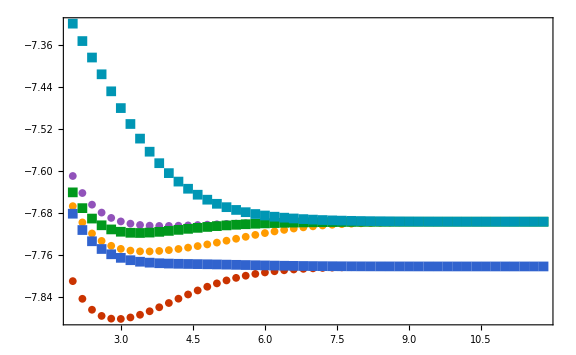

```mathematica
LiHFCISTO3G=Show[ListPlot[Table[fciLiHSTO3G⟦;;,{1,n+1}⟧,{n,{1,3,6}}]⟦;;,;; ;;2⟧,PlotStyle->{RGBColor[0.790588, 0.201176, 0.],RGBColor[1., 0.607843, 0.],RGBColor[0.567426, 0.32317, 0.729831]},Joined->False,PlotRange->All,plotOptions],ListPlot[Table[fciLiHSTO3G⟦;;,{1,n+1}⟧,{n,{2,4,8}}]⟦;;,;; ;;2⟧,PlotStyle->{RGBColor[0.192157, 0.388235, 0.807843],RGBColor[0., 0.596078, 0.109804],RGBColor[0., 0.588235, 0.705882]},PlotMarkers->{"■",10},Joined->False,PlotRange->All,plotOptions]]
```

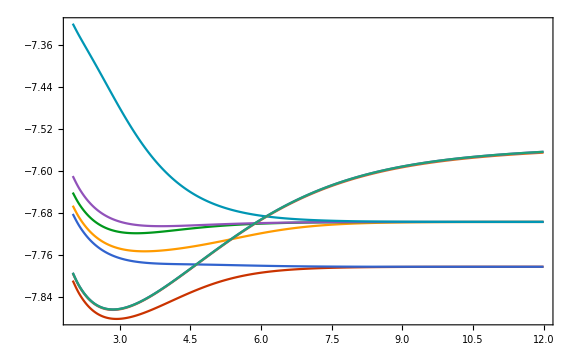

```mathematica
ListPlot[Table[SSLiHSTO3G⟦;;,{1,n+1}⟧,{n,9}],PlotRange->All,PlotMarkers->None,plotOptions]
```

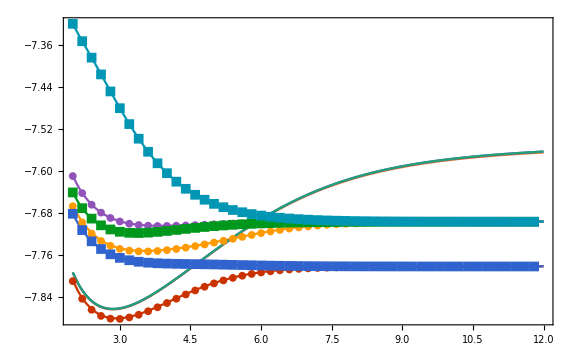

```mathematica
Show[ListPlot[Table[SSLiHSTO3G⟦;;,{1,n+1}⟧,{n,9}],PlotRange->All,PlotMarkers->None,plotOptions],LiHFCISTO3G]
```

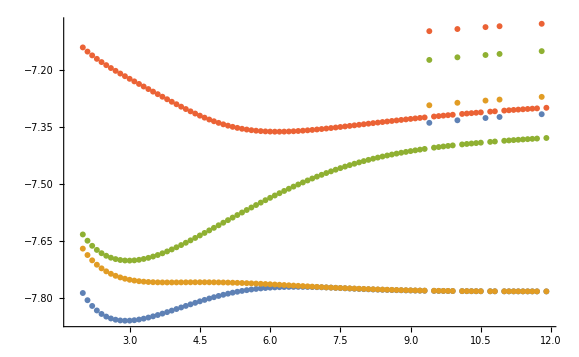

```mathematica
ListPlot[Table[SALiHSTO3G⟦;;,{1,n+1}⟧,{n,4}],PlotRange->All]
```

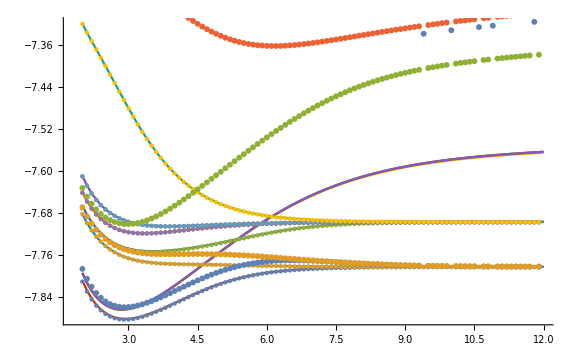

```mathematica
Show[ListPlot[Table[SSLiHSTO3G⟦;;,{1,n+1}⟧,{n,9}],PlotTheme->"VibrantColors",PlotRange->All,ImageSize->Large,Joined->True],LiHFCISTO3G,ListPlot[Table[SALiHSTO3G⟦;;,{1,n+1}⟧,{n,4}],PlotRange->All]]
```

#### 6-31G

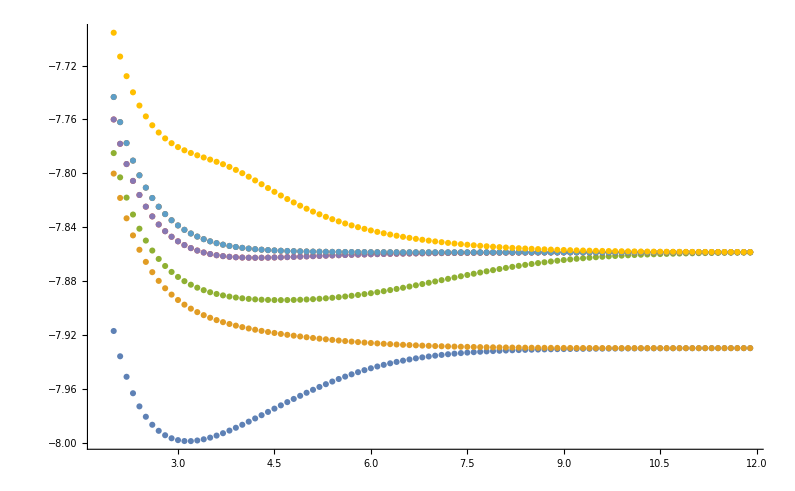

```mathematica
LiHFCI631G=ListPlot[Table[fciLiH631G⟦;;,{1,n+1}⟧,{n,8}],PlotRange->All]
```

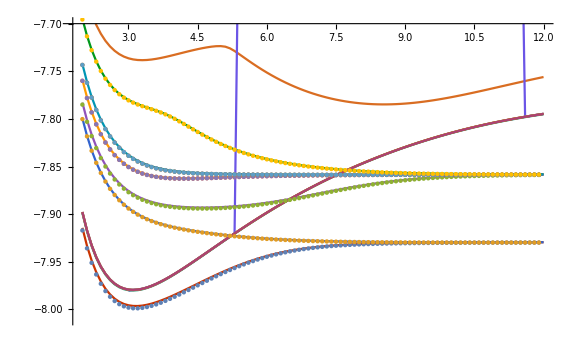

```mathematica
Show[ListPlot[Table[SSLiH631G⟦;;,{1,n+1}⟧,{n,13}],PlotTheme->"VibrantColors",PlotRange->{All,{-8.01,-7.7}},ImageSize->Large,Joined->True],LiHFCI631G]
```

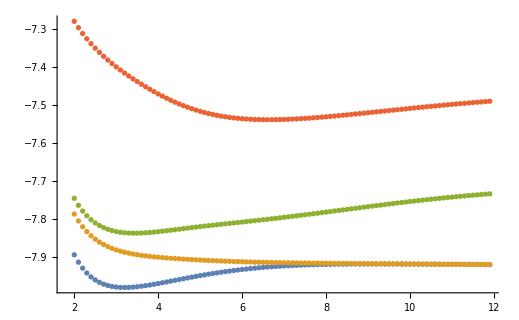

```mathematica
ListPlot[Table[SALiH631G⟦;;,{1,n+1}⟧,{n,4}],PlotRange->All]
```

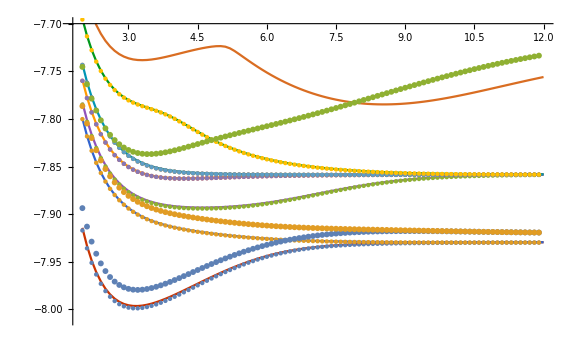

```mathematica
Show[ListPlot[Table[SSLiH631G⟦;;,{1,n+1}⟧,{n,7}],PlotTheme->"VibrantColors",PlotRange->{All,{-8.01,-7.7}},ImageSize->Large,Joined->True],LiHFCI631G,ListPlot[Table[SALiH631G⟦;;,{1,n+1}⟧,{n,4}],PlotRange->All]]
```

#### cc-pVDZ

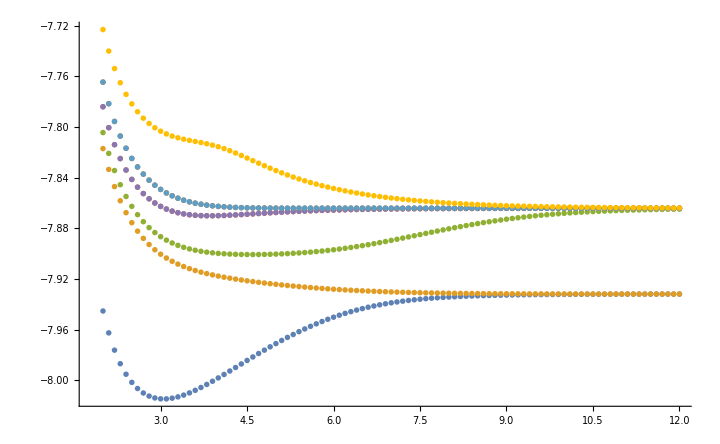

```mathematica
LiHFCIccpVDZ=ListPlot[Table[fciLiHccpVDZ⟦;;,{1,n+1}⟧,{n,8}],PlotRange->All]
```

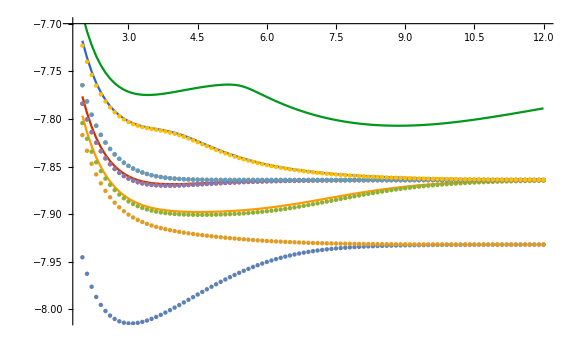

```mathematica
Show[ListPlot[Table[SSLiHccpVDZ⟦;;,{1,n+1}⟧,{n,4}],PlotTheme->"VibrantColors",PlotRange->{All,{-8.01,-7.7}},ImageSize->Large,Joined->True],LiHFCIccpVDZ]
```

### Data LiF

#### HF STO3G

```mathematica
HF={{2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4000000000000004,3.5,3.6,3.7,3.8,3.9000000000000004,4.,4.1,4.2,4.300000000000001,4.4,4.5,4.6,4.7,4.800000000000001,4.9,5.,5.1,5.2,5.300000000000001,5.4,5.5,5.6,5.7,5.800000000000001,5.9,6.,6.1000000000000005,6.2,6.3,6.4,6.5,6.6000000000000005,6.7,6.800000000000001,6.9,7.,7.1000000000000005,7.2,7.300000000000001,7.4,7.5,7.6000000000000005,7.7,7.800000000000001,7.9,8.,8.100000000000001,8.2,8.3,8.4,8.5,8.600000000000001,8.7,8.8,8.9,9.,9.100000000000001,9.2,9.3,9.4,9.5,9.600000000000001,9.7,9.8,9.9,10.,10.1,10.200000000000001,10.3,10.4,10.5,10.6,10.700000000000001,10.8,10.9,11.,11.1,11.200000000000001,11.3,11.4,11.5,11.600000000000001,11.700000000000001,11.8,11.9,12.},{-105.21026880687248,-105.27109040261546,-105.31299113915594,-105.34082020710851,-105.35827509561632,-105.36813753563182,-105.37247659521734,-105.372817662378,-105.37027887155082,-105.36567796010168,-105.35961363081077,-105.3525260559288,-105.34474109194693,-105.33650222562018,-105.32799347757883,-105.31935565321525,-105.31069757873452,-105.30210337110046,-105.29363645564499,-105.28534110221034,-105.27724274550862,-105.2693488814434,-105.26165202323874,-105.25413475920175,-105.2467754947842,-105.23955324588749,-105.23245068877803,-105.22545555367805,-105.2185608451063,-105.21176438191091,-105.20506801289908,-105.1984767254231,-105.19199776603469,-105.18563983282507,-105.17941236615022,-105.17332494651413,-105.16738680051778,-105.16160641003206,-105.15599077788615,-105.15054742570095,-105.14527986300354,-105.14019193793459,-105.13528563873797,-105.13056158757026,-105.12601913207902,-105.12165646485657,-105.11747076127443,-105.11345832736203,-105.1096147502148,-105.1059350450983,-105.10241379447673,-105.09904527629601,-105.09582357733,-105.09274269376708,-104.89736570767863,-105.03259442285267,-105.00107339416476,-105.08170838563858,-104.87974005007644,-93.24642537862866,-104.88772698129266,-104.87255254699603,-105.07040119659142,-93.11222325977005,-104.6946821026557,-105.06471038388743,-104.67704917011224,-104.86426806742914,-105.0088647582499,-104.69000758164344,-103.02567745428759,-93.02252343872998,-104.4399882216463,-104.87902288295251,-92.83671971414495,-104.85494378706932,-104.85165520154514,-105.03215924628229,-92.9410740385532,-92.7150497465635,-92.76191122135064,-105.04404855554665,-104.66858137294629,-92.5695622249266,-92.66382914051874,-104.84428678443096,-104.66813381872952,-104.83712178871767,-92.68210692197059,-92.5132265734477,-92.55187937449956,-92.50788007312887,-104.83314294807997,-92.59550457552739,-92.55201532182615,-92.45299698355184,-92.79288256364669,-92.50048580324062,-92.47761948356116,-92.45530915580632,-92.4396770313601}}//Transpose;
```

#### FCI STO3G

```mathematica
fciLiFsto3g={{2.0,-105.26265812539353,-105.10595912558226,-105.1008342452472,-105.03326150583892,-105.03326150583891,-105.02832410900652,-105.02832410900622,-104.97626858212442,-104.97626858212416,-104.96703231109548,-104.96703231109515,-104.92737379658072,-104.90670347974856,-104.9067034797403,-104.89426294082531,-104.89031377550187,-104.8903137754954,-104.89000838069896,-104.87839734814227,-104.85959276360646},{2.1,-105.32449210022855,-105.16393508690244,-105.1612381249975,-105.11254644104913,-105.11254644104903,-105.10813807788682,-105.1081380778867,-105.0403227265553,-105.04032272655523,-105.03162108853263,-105.03162108853246,-105.01092266504061,-104.9913021976728,-104.99130219765382,-104.9795332612222,-104.97579600404525,-104.97579600403706,-104.97549131372237,-104.93521329137388,-104.91673336166176},{2.2,-105.3680155911756,-105.2068586883396,-105.20533291761336,-105.17143702439591,-105.17143702439537,-105.16749417589489,-105.16749417589293,-105.08893668425515,-105.08893668425492,-105.0806889156058,-105.08068891558489,-105.07393336672044,-105.05541905981255,-105.05541905981065,-105.04434602631281,-105.04091133058643,-105.04091133058259,-105.040569992403,-104.97701166808483,-104.95918596353866},{2.3,-105.39785554972428,-105.23841287670315,-105.23728908198416,-105.21507444607651,-105.2150744460726,-105.2115280871044,-105.2115280870992,-105.12576850548228,-105.12576850548088,-105.12145158584049,-105.11791898200414,-105.1179189819741,-105.10408124274203,-105.10408124273638,-105.09371427785027,-105.0906459486956,-105.09064594869172,-105.09024241693305,-105.00779644505202,-104.99146910729783},{2.4,-105.41755955201226,-105.26142777438547,-105.26022912385596,-105.24735652971938,-105.24735652971725,-105.24414181079007,-105.24414181079003,-105.15731200348876,-105.15363724204897,-105.15363724204651,-105.14614224706509,-105.14614224703183,-105.14110458062767,-105.14110458062163,-105.1314420458948,-105.12877997961098,-105.1287799795956,-105.12829853762672,-105.03065896725396,-105.01715157496506},{2.5,-105.42979668846293,-105.27806198493086,-105.2764960431656,-105.27121296692204,-105.27121296690287,-105.26827189549073,-105.26827189548587,-105.18440664075484,-105.1747013137048,-105.17470131367496,-105.16936228041027,-105.16936228040554,-105.16752564752016,-105.16752564750334,-105.16039244813435,-105.1581554035064,-105.15815540349504,-105.15758859219869,-105.0479444127834,-105.04059236145214},{2.6,-105.43654963546024,-105.28994980681048,-105.28882594365088,-105.28882594365037,-105.28784216565575,-105.28610815301607,-105.286108153016,-105.20490043885927,-105.19100158402402,-105.19100158400185,-105.19060307317616,-105.19060307317223,-105.1837189865208,-105.18371898650852,-105.18270427660927,-105.1808931594631,-105.18089315944113,-105.18024024024865,-105.05952596642956,-105.05792125967828},{2.7,-105.4392799665184,-105.3018078948614,-105.30180789486093,-105.29927058560658,-105.29927058560611,-105.29832059930983,-105.29557144287799,-105.2204045702364,-105.20761812268975,-105.20761812268427,-105.20258587150177,-105.20258587149816,-105.19996642876077,-105.19856798921322,-105.19856798920227,-105.19783338445478,-105.195972436942,-105.1959724369366,-105.07532330071002,-105.07474046194034},{2.8,-105.43906194758755,-105.31134345092529,-105.31134345092369,-105.30895090417661,-105.30895090417619,-105.30409448451728,-105.3006495482226,-105.23211421147153,-105.22039435695002,-105.22039435694724,-105.21335637806818,-105.21234694531734,-105.21234694529103,-105.21158781334864,-105.21158781334519,-105.21153873354265,-105.20523024586349,-105.20523024583261,-105.09130288974445,-105.08739372428921},{2.9,-105.43668617652483,-105.31830058502653,-105.31830058502582,-105.3160234711869,-105.31602347116045,-105.30795781714909,-105.30378898606494,-105.24091593157061,-105.23020721033821,-105.23020721033335,-105.22374772523507,-105.2230966231986,-105.22309662319134,-105.2222251903142,-105.21831567607558,-105.21831567605159,-105.21220452357248,-105.2122045235659,-105.10597872433871,-105.09828135176653},{3.0,-105.43273731740076,-105.3233155708809,-105.3233155708792,-105.3211301918129,-105.3211301917684,-105.31042163867131,-105.30551399673439,-105.24746951177761,-105.23770981228945,-105.23770981228131,-105.23179175477374,-105.23146418195094,-105.23146418195032,-105.23054109858766,-105.22330221111052,-105.22330221106921,-105.2174324459285,-105.21743244591819,-105.11941237298961,-105.10793479706766},{3.1,-105.42765112029662,-105.32685642083419,-105.32685642083365,-105.32474396337585,-105.32474396337335,-105.31186621318821,-105.30620924563004,-105.25226895908025,-105.24339224156668,-105.24339224156182,-105.2379779304726,-105.23793723278797,-105.23793723276498,-105.23697438268817,-105.22694987541843,-105.2269498753954,-105.22131993572728,-105.22131993568553,-105.13165736968273,-105.1166983290509},{3.2,-105.42175569467433,-105.3292693522333,-105.32926935223077,-105.32721519078278,-105.32721519078181,-105.31257451961504,-105.30615585590087,-105.25568722670205,-105.24762588346883,-105.24762588346593,-105.24288735450334,-105.24288735450087,-105.24267798728997,-105.24189630308081,-105.22956379164091,-105.2295637916375,-105.22417461767205,-105.2241746176471,-105.14277108450811,-105.12478747341005},{3.3,-105.4153012222638,-105.3308123759582,-105.33081237595442,-105.32880543890916,-105.32880543890762,-105.31275721779681,-105.30555786355484,-105.25800862429605,-105.25069544394592,-105.25069544394069,-105.24660136258827,-105.24660136258335,-105.24617769420634,-105.24559293322372,-105.23137637795188,-105.23137637794713,-105.22623048305842,-105.22623048304463,-105.15281508999536,-105.13233203683431},{3.4000000000000004,-105.40848136297845,-105.33167941825347,-105.33167941825342,-105.32971162172795,-105.32971162171948,-105.31257117032021,-105.30456160399058,-105.25945219766336,-105.25282192881075,-105.25282192880803,-105.24930367410688,-105.24930367408582,-105.24869961504967,-105.24828769122809,-105.23256566657767,-105.23256566656313,-105.22766627968855,-105.22766627966055,-105.1618533114077,-105.13940685740863},{3.5,-105.40144874843755,-105.33201763769907,-105.33201763769898,-105.33008338574938,-105.33008338574902,-105.31213315981752,-105.30326996191587,-105.26018862047282,-105.25417914496686,-105.25417914496403,-105.25117232694811,-105.25117232693938,-105.25041943082677,-105.25015748599046,-105.23326890649902,-105.23326890648656,-105.22861921876684,-105.22861921870879,-105.16995039449486,-105.14605314962081},{3.6,-105.39432626081619,-105.33193990991893,-105.33193990991862,-105.3300356586774,-105.33003565867698,-105.31153004977398,-105.30175291289164,-105.26035247404018,-105.25490561237555,-105.25490561237112,-105.25235052755767,-105.25235052754736,-105.25147771219655,-105.25134435594448,-105.23359266781904,-105.23359266780665,-105.22919520842856,-105.22919520842392,-105.17717061841965,-105.15229287063563},{3.7,-105.38721526817852,-105.33153388728537,-105.33153388728506,-105.32965776972271,-105.32965776972239,-105.31082631845506,-105.30005539546976,-105.26005125055106,-105.25511323390748,-105.25511323387983,-105.25295505465691,-105.25295505465566,-105.25198848473882,-105.25196393489941,-105.23362035643461,-105.23362035643255,-105.22947651267334,-105.22947651266767,-105.18357722050233,-105.15813805484494},{3.8,-105.3802016009193,-105.33086861439826,-105.330868614398,-105.32902012140923,-105.32902012140899,-105.31006965276129,-105.29820328243967,-105.25937200602795,-105.25489366355785,-105.2548936635408,-105.25308243930958,-105.25308243929462,-105.25211167210877,-105.25204552259312,-105.23341780973907,-105.23341780973894,-105.22952749461177,-105.2295274946115,-105.18923197926806,-105.1635966165729},{3.9000000000000004,-105.37335976962952,-105.3299993762477,-105.32999937624766,-105.32817908873939,-105.32817908873909,-105.30929510598365,-105.29620804806758,-105.25838630150766,-105.25432302140823,-105.25432302137075,-105.25281355139607,-105.2528135513771,-105.25186744194788,-105.25172701160207,-105.23303746709992,-105.23303746709978,-105.22939892662352,-105.22939892662342,-105.19419494782161,-105.16867574349396},{4.0,-105.36675571219959,-105.32897124831182,-105.32897124831175,-105.32718061396474,-105.32718061396417,-105.30852819356613,-105.29407063040806,-105.25715387588201,-105.25346540194221,-105.25346540192723,-105.25221702503039,-105.2522170250129,-105.25129898075281,-105.2510990246314,-105.23252147898738,-105.232521478987,-105.22913122316783,-105.22913122316771,-105.19852426847952,-105.1733836990915},{4.1,-105.36044820715921,-105.3278216793895,-105.32782167938936,-105.32606282686717,-105.32606282686712,-105.30778719924908,-105.29178492031286,-105.25572536331956,-105.25237548664163,-105.25237548662952,-105.25135182086845,-105.25135182086694,-105.25046445251868,-105.25021811401024,-105.23190402480432,-105.23190402480412,-105.2287568613209,-105.22875686132087,-105.20227602444942,-105.17773061569795},{4.2,-105.35448901456463,-105.32658234614675,-105.3265823461465,-105.32485792930285,-105.32485792930277,-105.30708489580599,-105.28934123410274,-105.25414428519083,-105.25110048177434,-105.25110048176657,-105.25026913739183,-105.25026913738083,-105.24941435825497,-105.24913323906148,-105.23121304004165,-105.23121304004154,-105.2283021873321,-105.22830218733199,-105.20550409896497,-105.18172867895909},{4.300000000000001,-105.34892184033177,-105.32528045828633,-105.32528045828607,-105.32359352263614,-105.32359352263603,-105.30642983101868,-105.28672998221685,-105.25244848946892,-105.24968154310449,-105.2496815430737,-105.24901382516794,-105.24901382515239,-105.24819294511329,-105.24788718708271,-105.230471502916,-105.2304715029156,-105.22778876093733,-105.22778876093722,-105.20826002856273,-105.18539197583291},{4.4,-105.34378039697656,-105.32393965162413,-105.32393965162377,-105.32229351617217,-105.32229351617184,-105.30582729239315,-105.28394549166036,-105.25067117201091,-105.24815480969455,-105.24762542124044,-105.24683923367982,-105.24651760805511,-105.22969839415595,-105.22969839415592,-105.22723435204992,-105.2272343520497,-105.21059284660318,-105.188736176514,-105.1887361765139,-105.1771300869267},{4.5,-105.33908612596714,-105.32258057822273,-105.32258057822244,-105.3209787265986,-105.32097872659838,-105.30528003662083,-105.28098959236489,-105.24884158686375,-105.24655214305758,-105.24613889535506,-105.24538775632827,-105.24505775742577,-105.22890941505162,-105.22890941505142,-105.22665367938005,-105.22665367937987,-105.21254892381091,-105.19177815789487,-105.19177815789467,-105.18113050438113},{4.6,-105.33484641413924,-105.32122128121014,-105.3212212812098,-105.31966725754489,-105.31966725754472,-105.30478884882658,-105.27787427156716,-105.24698553025883,-105.2449016479973,-105.24458518195169,-105.24386908105774,-105.2435370223726,-105.22811752944543,-105.22811752944531,-105.226058958847,-105.22605895884686,-105.21417181751639,-105.19453562802201,-105.19453562802158,-105.18480397572176},{4.7,-105.33105415209423,-105.31987742514656,-105.31987742514642,-105.31837473188358,-105.31837473188342,-105.30435298101311,-105.27462265877517,-105.24512566795268,-105.24322803823098,-105.24299155893767,-105.24231018229446,-105.24198129379243,-105.22733337861531,-105.22733337861519,-105.22546031412685,-105.22546031412674,-105.21550214390889,-105.19702678229358,-105.19702678229346,-105.18816432508258},{4.800000000000001,-105.32768909924366,-105.31856243811974,-105.31856243811967,-105.31711443504433,-105.31711443504418,-105.303970505338,-105.27126796716607,-105.2432817594945,-105.24155289718895,-105.24138192250578,-105.24073470814524,-105.24041323387422,-105.22656560629022,-105.22656560628994,-105.22486608941222,-105.22486608941199,-105.21657748466414,-105.19927000254091,-105.19927000254063,-105.19122673353533},{4.9,-105.3247208658767,-105.31728760924558,-105.31728760924555,-105.31589741475314,-105.31589741475302,-105.30363860747717,-105.26785065818734,-105.24147082205643,-105.2398948741434,-105.23977699749871,-105.23916318374219,-105.2388524790632,-105.22582112112742,-105.22582112112714,-105.22428309370002,-105.22428309369995,-105.21743233760728,-105.20128360184965,-105.20128360184934,-105.19400742114956},{5.0,-105.32211275898389,-105.31606217335997,-105.31606217335987,-105.31473257031848,-105.31473257031797,-105.30335383631966,-105.26441464633658,-105.23970726508664,-105.23826984639052,-105.23819451377133,-105.23761318120283,-105.2373158089311,-105.22510531628642,-105.22510531628608,-105.22371679829152,-105.2237167982912,-105.21809811416634,-105.20308561035021,-105.20308561034905,-105.19652334980802},{5.1,-105.3198255721682,-105.31489340338315,-105.31489340338304,-105.31362675406972,-105.31362675406942,-105.30311231950854,-105.26100351743702,-105.23800301823786,-105.23669106987761,-105.23664937087828,-105.23609947852998,-105.23581730322302,-105.22442225963124,-105.22442225963123,-105.22317150260413,-105.22317150260389,-105.21860318431756,-105.20469359797832,-105.20469359797818,-105.19879194539686},{5.2,-105.3178206360802,-105.31378672361491,-105.31378672361487,-105.31258489713605,-105.312584897136,-105.3029099495639,-105.25765748423503,-105.23636766613453,-105.23516933278988,-105.23515380565995,-105.23463422204641,-105.23436850153713,-105.22377486342138,-105.2237748634211,-105.22265047850344,-105.22265047850327,-105.21897296308032,-105.20612452745412,-105.20612452745388,-105.20083083727495},{5.300000000000001,-105.3160618519391,-105.3127458471359,-105.31274584713582,-105.31161016390985,-105.31161016390956,-105.30274254230426,-105.25441138809909,-105.23480859872205,-105.23371757116549,-105.23371312046052,-105.2332271007248,-105.23297857392936,-105.22316503885801,-105.22316503885793,-105.22215609962012,-105.22215609961985,-105.21923003373588,-105.20739463439581,-105.20739463439548,-105.20265761723991},{5.4,-105.31451676887225,-105.31177293684802,-105.31177293684797,-105.31070413301926,-105.31070413301917,-105.30260596802755,-105.25129370512485,-105.23333117874617,-105.23234813021222,-105.2323287948462,-105.23188553571465,-105.2316545057415,-105.22259383845575,-105.22259383845389,-105.2216899595083,-105.22168995950827,-105.21939429926206,-105.20851933177663,-105.20851933177649,-105.20428961830449},{5.5,-105.31315693776384,-105.31086878497095,-105.31086878497065,-105.30986699846045,-105.30986699846038,-105.3024962556929,-105.24832633344211,-105.23193892587871,-105.23105086310443,-105.23102078809883,-105.2306148845035,-105.23040129612089,-105.22206158750706,-105.22206158750689,-105.22125298068292,-105.22125298068269,-105.21948315415136,-105.20951313587071,-105.20951313587065,-105.20574371798851},{5.6,-105.31195780387442,-105.31003300322168,-105.31003300322159,-105.30909778184103,-105.30909778184086,-105.30240967089544,-105.24552490162185,-105.23063371284883,-105.22982928599778,-105.22979180678563,-105.22941865617659,-105.22922216686315,-105.22156800532386,-105.2215680053238,-105.22084551545638,-105.22084551545633,-105.21951167046326,-105.2103896133555,-105.21038961335539,-105.20703616724566},{5.7,-105.31089835402702,-105.3092642166495,-105.3092642166493,-105.30839454659127,-105.30839454659119,-105.30234276939692,-105.2428993756829,-105.22941596975056,-105.2286852756576,-105.22864304264175,-105.22829873346973,-105.22811877745528,-105.22111231569497,-105.22111231569482,-105.22046743887964,-105.2204674388795,-105.21949279059615,-105.21116134854242,-105.21116134854239,-105.20818244931053},{5.800000000000001,-105.30996066662526,-105.30856025315249,-105.30856025314796,-105.3077546047536,-105.3077546047522,-105.30229242878525,-105.24045480684879,-105.22828488988307,-105.22761929457914,-105.22761929455969,-105.22757438398165,-105.22757438392276,-105.22725559552717,-105.22709144045776,-105.22069334725192,-105.2206933472514,-105.22011823382961,-105.22011823382955,-105.21943752263527,-105.21183992970946},{5.9,-105.30912945300346,-105.30791832207706,-105.30791832207704,-105.30717470989767,-105.30717470989738,-105.30225586156608,-105.2381921174998,-105.22723862947115,-105.2266306115788,-105.22658462307032,-105.22628853646015,-105.22613933258847,-105.2203096228344,-105.22030962283426,-105.21979706809718,-105.21979706809701,-105.21935513366505,-105.21243595312357,-105.21243595312338,-105.2100939762016},{6.0,-105.30839163598878,-105.30733517835037,-105.30733517830222,-105.30665123027067,-105.30665123027059,-105.30223061332883,-105.23610886517908,-105.22627451441062,-105.225717512615,-105.2256716543462,-105.22539587437129,-105.2252606963582,-105.21995943858414,-105.21995943858397,-105.21950286349382,-105.2195028634936,-105.2192533381071,-105.21295904321903,-105.21295904321734,-105.21088551284349},{6.1000000000000005,-105.30773598392129,-105.30680726782383,-105.30680726779771,-105.30618029939372,-105.30618029939352,-105.3022145496883,-105.23419995128111,-105.22538919599917,-105.2245751474659,-105.21964093269612,-105.21964093269462,-105.21923435723477,-105.21923435723464,-105.21913847835155,-105.21341788640605,-105.21341788639985,-105.21158339691577,-105.21158339691523,-105.21116837336986,-104.94022524704005},{6.2,-105.3071528034691,-105.30633085329303,-105.3063308532929,-105.30575794276774,-105.30575794276751,-105.30220583536394,-105.23245825808809,-105.22457884304508,-105.21935214444495,-105.21935214444481,-105.21901569592704,-105.21899015546781,-105.21899015546771,-105.21382027625476,-105.21382027625457,-105.21219822436291,-105.21219822436282,-105.21185625528487,-104.9385199908696,-104.93851999086915},{6.3,-105.30663368712632,-105.30590212044638,-105.30590212044271,-105.30538018192408,-105.30538018192388,-105.30220290847751,-105.23087520774834,-105.22383927727105,-105.2231368108047,-105.21909106400878,-105.21909106400872,-105.21888909176101,-105.21876877965983,-105.21876877965968,-105.21417316714562,-105.21417316714283,-105.21273959405369,-105.21273959405355,-105.21246698995978,-104.93676217799998},{6.4,-105.30617130744389,-105.30551726467986,-105.30551726467979,-105.30504311541956,-105.30504311541935,-105.30220445248388,-105.22944124162866,-105.22316610670816,-105.21885567394001,-105.21885567393991,-105.2187618746013,-105.21856870594331,-105.21856870594324,-105.21448273388104,-105.21448273388097,-105.21321614864209,-105.21321614864192,-105.21300866128655,-104.93496318919588,-104.9349631891956},{6.5,-105.30575925064278,-105.30517256011794,-105.30517256011399,-105.30474298115988,-105.30474298115982,-105.30220936764806,-105.2281462240548,-105.2225548373363,-105.22194458763002,-105.21864398286073,-105.21864398285751,-105.21863649674526,-105.21838839805412,-105.21838839805403,-105.21475443459829,-105.21475443459772,-105.21363562753479,-105.21363562753459,-105.21348862368723,-104.93313324241632},{6.6000000000000005,-105.3053918813452,-105.30486441262362,-105.30486441261833,-105.30447620117864,-105.30447620117852,-105.30221674339121,-105.22697977335685,-105.22200096673723,-105.22143082549563,-105.2185147770411,-105.21845405223479,-105.21845405223266,-105.2182263344165,-105.21822633441644,-105.21499307496441,-105.2149930749641,-105.21400492784143,-105.21400492784129,-105.21391354282136,-104.93128145912961},{6.7,-105.30506423256594,-105.30458939888568,-105.3045893988856,-105.30423941207215,-105.30423941207195,-105.3022258324572,-105.22593152809914,-105.22150006059208,-105.21839801077047,-105.2182840170832,-105.21828401708309,-105.21808102981088,-105.21808102981068,-105.2152028716792,-105.2152028716791,-105.21433017011175,-105.21433017011165,-105.21428943973409,-104.92941593451121,-104.92941593451111},{6.800000000000001,-105.30477191544632,-105.30434429349317,-105.30434429349276,-105.30402948353824,-105.30402948353806,-105.30223602737452,-105.2249913540234,-105.22104781310198,-105.21828706688872,-105.21813210130371,-105.21813210130357,-105.21795105228213,-105.21795105228203,-105.21538751380295,-105.21538751380278,-105.21462173666433,-105.21461676586095,-105.21461676586092,-104.92754381105175,-104.92754381105154},{6.9,-105.30451104414607,-105.30412608598911,-105.30412608598907,-105.30384352737111,-105.30384352737079,-105.30224683944937,-105.22414949951259,-105.22064009324767,-105.21818247282002,-105.21799662838515,-105.21799662838504,-105.21783503581332,-105.2178350358132,-105.2155502208869,-105.21555022088688,-105.21491530315231,-105.21486948467151,-105.21486948467133,-104.92567135277142,-104.92567135277139},{7.0,-105.30427817324266,-105.3039319896959,-105.30393198969576,-105.30367889899301,-105.30367889899276,-105.30225788031015,-105.22339670684534,-105.22027297821602,-105.21808448769612,-105.21787602818144,-105.21787602818111,-105.21773168931637,-105.21773168931627,-105.2156937971848,-105.21569379718478,-105.21517450144847,-105.21509251917384,-105.21509251917371,-104.92380401889858,-104.9238040188983},{7.1000000000000005,-105.30407024457688,-105.30375944392117,-105.3037594439211,-105.30353319319693,-105.30353319319303,-105.3022688458864,-105.22272428596078,-105.2199427761693,-105.21799316439508,-105.21776884042305,-105.21776884042293,-105.21763980248208,-105.21763980248137,-105.21582068134181,-105.21582068134171,-105.21540323047908,-105.2152895466896,-105.21528954665662,-104.92194653565521,-104.92194653565512},{7.2,-105.30388454169685,-105.30360611097886,-105.30360611097866,-105.30340423580823,-105.30340423577495,-105.30227950260887,-105.22212415787823,-105.21964603937938,-105.21790840192602,-105.2176737154533,-105.21767371545316,-105.2175582489118,-105.21755824891167,-105.21593299167765,-105.21593299167753,-105.21560496785177,-105.21546378657708,-105.21546378653112,-104.92010296530201,-104.92010296530188},{7.300000000000001,-105.30371865058605,-105.30346986927121,-105.30346986927108,-105.30329007209163,-105.30329007206959,-105.30228967560917,-105.22158887316637,-105.21937957030094,-105.21782998827915,-105.21758941290925,-105.2175894129091,-105.21748598715719,-105.21748598715686,-105.2160325667593,-105.21603256675922,-105.21578280956665,-105.21561805327863,-105.21561805327484,-104.91827677179359,-104.9182767717884},{7.4,-105.30357042531747,-105.30334880342933,-105.3033488034288,-105.3031889533899,-105.30318895338955,-105.3022992386576,-105.22111161134386,-105.2191404207793,-105.2189274162133,-105.2189274162016,-105.21891118006207,-105.2187917463079,-105.2187638332299,-105.21775763540356,-105.21751479854449,-105.21751479854288,-105.21742205987215,-105.21742205987194,-105.21612100142337,-105.21612100142295},{7.5,-105.30343795778873,-105.30324119255181,-105.30324119255056,-105.30309932239267,-105.30309932239265,-105.30230810561191,-105.22068616594301,-105.21892588762309,-105.21769100725614,-105.2174488400487,-105.21744884004855,-105.21736559164012,-105.21736559164006,-105.21619967915997,-105.21619967915464,-105.21607750255059,-105.21587618438693,-105.21587618438683,-104.91468774858131,-104.91468774855831},{7.6000000000000005,-105.3033195513611,-105.30314549689534,-105.30314549688092,-105.30301979787437,-105.30301979787254,-105.30231622314169,-105.22030691900241,-105.21873350263982,-105.21854123224328,-105.21854123222879,-105.218528019995,-105.21852801997821,-105.21842089332074,-105.21839896860163,-105.21762974165803,-105.21739060135968,-105.21738657082497,-105.2173157856737,-105.21730297449676,-105.21626979975329},{7.7,-105.30321369697003,-105.30306034425845,-105.30306034425635,-105.30294915933783,-105.30294915932083,-105.30232356457216,-105.2199688079764,-105.21856102213539,-105.2183659193098,-105.21824500180752,-105.21757346669781,-105.2173392371573,-105.217339237157,-105.21727191984603,-105.2172719198454,-105.21633240457469,-105.21633240457362,-105.2163057933362,-105.21608006999537,-105.21608006997418},{7.800000000000001,-105.30311905251789,-105.30298451572635,-105.30298451571787,-105.30288633183693,-105.3028863318099,-105.30233012462736,-105.21966728885566,-105.21840641349776,-105.21823149067478,-105.21823149067153,-105.21822080446367,-105.21822080444905,-105.2181245973521,-105.21810742007156,-105.21752181328594,-105.21729398624026,-105.2172939862369,-105.21723334203227,-105.21723334203139,-105.21639969778693},{7.9,-105.3030344236351,-105.30291693184797,-105.30291693184672,-105.30283037142375,-105.30283037142007,-105.30233591501867,-105.21939829619497,-105.21826783891456,-105.21810050397595,-105.21810050396542,-105.21809091324342,-105.21799970161968,-105.21798451207194,-105.21747442363764,-105.21725416524771,-105.21725416524767,-105.21719946532491,-105.2171994653248,-105.21648216942498,-105.21643856327034},{8.0,-105.30295874755333,-105.30285663921593,-105.30285663920863,-105.30278045152039,-105.30278045150293,-105.30234096061551,-105.21915820307001,-105.21814364964986,-105.21798325397202,-105.21798325397114,-105.21797465763312,-105.2179746576328,-105.21788815806514,-105.2178747350763,-105.21743095749379,-105.21721916210964,-105.21721916210886,-105.21716976296491,-105.21716976283307,-105.2165545286003},{8.100000000000001,-105.302891078025,-105.30280279744116,-105.30280279744086,-105.30273584954328,-105.30273584954257,-105.3023452963018,-105.21894378113838,-105.21803235349005,-105.21787830502413,-105.21787830502389,-105.21787060973827,-105.21787060973,-105.2177885563047,-105.21777670256661,-105.21739109558527,-105.21718842980728,-105.21718842980587,-105.21714376334127,-105.21714376333932,-105.21661794203057},{8.2,-105.3028305721452,-105.3027546670314,-105.30275466703114,-105.30269593523667,-105.30269593523042,-105.3023489642972,-105.2187521622635,-105.21793261779081,-105.21778436818366,-105.21777748811186,-105.21735454155505,-105.21716148019631,-105.21716148019607,-105.21712104503051,-105.21712104502896,-105.21667343812697,-105.21656049998714,-105.21656049998622,-105.21642586882433,-105.21642586880172},{8.3,-105.30277647873665,-105.3027115983151,-105.30271159831443,-105.30266015956427,-105.30266015956211,-105.30235201177888,-105.21858080215185,-105.21784324670101,-105.21770028810218,-105.21770028810145,-105.21769414448492,-105.21769414448023,-105.21762024926026,-105.2176110253097,-105.2173210225649,-105.21713787834277,-105.21713787834237,-105.21710123208075,-105.21710123206074,-105.21672192446715},{8.4,-105.30272812770404,-105.30267302092271,-105.30267302091957,-105.30262804462517,-105.30262804462461,-105.30235448914539,-105.2184274463631,-105.21776316943391,-105.21762503027034,-105.21762503024846,-105.21761955109788,-105.21761955109393,-105.21754939710566,-105.2175412698866,-105.2172902889232,-105.21711723709309,-105.21711723709285,-105.21708398952829,-105.21708398952444,-105.21676420197467},{8.5,-105.30268492101156,-105.30263843440315,-105.30263843439504,-105.3025991746586,-105.30259917464416,-105.30235644831488,-105.21829009893362,-105.21769142787454,-105.21755766935898,-105.21755766935868,-105.21755278890845,-105.21755278886894,-105.21748616872325,-105.21747901375866,-105.21726211306259,-105.21709921202327,-105.2170992110141,-105.21706901907231,-105.21706901906144,-105.21680097482742},{8.600000000000001,-105.30264632445214,-105.30260739961676,-105.30260739960126,-105.30257318787272,-105.30257318787254,-105.30235794148987,-105.21816699366207,-105.21762716482455,-105.21749737812016,-105.21749737811959,-105.21749303647368,-105.21749303647128,-105.2174297549119,-105.21742346136298,-105.21723628808184,-105.21708349695602,-105.21708349695317,-105.21705605527077,-105.21705605526436,-105.21683287706325},{8.7,-105.30261186030842,-105.30257953118902,-105.30257953118877,-105.30254976926857,-105.30254976926798,-105.30235902010875,-105.21805656805509,-105.21756961304246,-105.21743955990861,-105.21743955989696,-105.21737390255147,-105.21721262603167,-105.21706981963796,-105.21706981963773,-105.21704486186638,-105.21704486186378,-105.2168604526696,-105.21669626139128,-105.21669626139054,-105.2166260067525},{8.8,-105.30258110119976,-105.30255449045238,-105.30255449044738,-105.30252864425078,-105.30252864424955,-105.30235973401912,-105.21795743990279,-105.21751808579648,-105.21739512611447,-105.21739512611224,-105.21739170357083,-105.21739170357039,-105.21733455894726,-105.21732970321851,-105.21719095622487,-105.21705793804168,-105.21705793804101,-105.21703522819588,-105.21703522768759,-105.21688419492634},{8.9,-105.30255366415503,-105.30253197959526,-105.30253197959519,-105.30250957304416,-105.30250957304278,-105.30236013083857,-105.21786838605391,-105.21747196696971,-105.217348881611,-105.21734888159554,-105.21729029740546,-105.21717112321976,-105.21704763701753,-105.2170476370163,-105.21702696797816,-105.21702696796034,-105.21690453937435,-105.21673451012146,-105.21673451011489,-105.21668087107271},{9.0,-105.30252920598532,-105.30251173617383,-105.30251173617364,-105.30249234568319,-105.30249234568308,-105.30236025545767,-105.21778832392668,-105.21743070375646,-105.21731325395452,-105.21731289559463,-105.2173105704221,-105.21730316320718,-105.21725877524072,-105.21720673658137,-105.21715298534005,-105.21703872519248,-105.21701991306898,-105.2170171333063,-105.21692187412343,-105.2168336250053},{9.100000000000001,-105.30250741863148,-105.30249352848598,-105.30249352848547,-105.30247677787688,-105.30247677787618,-105.30236014972101,-105.21771629442426,-105.21739379841992,-105.21727867310688,-105.21727867309157,-105.21727630186273,-105.21727630182289,-105.21722716364593,-105.21722389791091,-105.21713641293556,-105.21703103239413,-105.21703103237576,-105.21701391492346,-105.21701391491838,-105.21693654613941},{9.2,-105.3024880255231,-105.30247715146757,-105.30247715146612,-105.30246270728436,-105.30246270728323,-105.30235985219467,-105.21765144746074,-105.21736080206576,-105.21724774929136,-105.21724774929075,-105.2172456570137,-105.21724565701237,-105.21719890414857,-105.21719604933374,-105.21712128694843,-105.2170244072742,-105.21702440726854,-105.21700884046328,-105.21700884046207,-105.21694886688908},{9.3,-105.30247077811259,-105.3024624231343,-105.30246242312941,-105.30244999033918,-105.30244999032678,-105.3023593980404,-105.21759302875884,-105.21733130860298,-105.21722010432725,-105.21722010431107,-105.21721826088805,-105.21721826088783,-105.21717376509812,-105.21717127235914,-105.21710749768896,-105.21701871528062,-105.21701871527286,-105.21700457084656,-105.21700457084226,-105.21695911714474},{9.4,-105.30245545288102,-105.30244918153673,-105.3024491815344,-105.30243849958782,-105.30243849958775,-105.30235881904036,-105.21754036836299,-105.2173049495763,-105.21719539928239,-105.21719539856613,-105.21719377752822,-105.21719377749486,-105.21715141751329,-105.21714924395533,-105.21709494369998,-105.21701383686812,-105.21701383686802,-105.21700099989486,-105.2170009998947,-105.21696755115116},{9.5,-105.30244184873894,-105.30243728212429,-105.3024372821187,-105.30242812133692,-105.30242812133675,-105.30235814351408,-105.21749287050751,-105.21728138977545,-105.2171719057345,-105.21717190573179,-105.21712967494867,-105.21708353078252,-105.21700966593833,-105.2170096659374,-105.21699803278709,-105.21699803278621,-105.21697440001755,-105.21681490193541,-105.21681490192506,-105.21679201023919},{9.600000000000001,-105.30242978480292,-105.30242659542235,-105.30242659542222,-105.30241875376653,-105.30241875376645,-105.30235739653162,-105.21745000481437,-105.21726032365147,-105.21715362464464,-105.21715362464225,-105.21715237528123,-105.21715237523586,-105.21711395265939,-105.21711230557662,-105.21707317136709,-105.21700610849979,-105.21700610849827,-105.21699558499544,-105.21699558499526,-105.21697987444796},{9.7,-105.30241909807127,-105.30241700517918,-105.30241700517914,-105.30241030525701,-105.30241030525691,-105.30235659998975,-105.21741129831643,-105.21724147235386,-105.21713603752637,-105.21713494355728,-105.21706378355456,-105.21700308333234,-105.21700308141197,-105.21699358342116,-105.2169935812559,-105.21698416675959,-105.21683367966197,-105.2168336736438,-105.2168166919803,-105.21681668564048},{9.8,-105.30240964199074,-105.30240840669735,-105.30240840669646,-105.30240269306265,-105.30240269306248,-105.30235577279979,-105.21737628907904,-105.21722458160893,-105.21711982167221,-105.21711939261726,-105.21711775218121,-105.21710702061914,-105.21707549087053,-105.2170549759218,-105.21700088608064,-105.21700051139183,-105.21699195486295,-105.21699174682529,-105.21698745231241,-105.2168419800915},{9.9,-105.30240128445581,-105.3024007053829,-105.30240070538277,-105.30239584208701,-105.30239584206863,-105.30235493108884,-105.21734471952453,-105.21720942006765,-105.2171063612866,-105.21710636128422,-105.21710552656761,-105.21710552656685,-105.21707226306698,-105.2170711878001,-105.21704762191385,-105.21699833398418,-105.21699833397584,-105.21699064684567,-105.21699064683366,-105.21698989038677},{10.0,-105.30239390670509,-105.30239381561135,-105.30239381560962,-105.3023896840116,-105.30238968400405,-105.3023540884011,-105.21731604760734,-105.21718962207345,-105.21709389657003,-105.2170931692316,-105.21706144830446,-105.21706051816399,-105.21704157892599,-105.21699665306897,-105.21699649273322,-105.2169897707014,-105.2169896054775,-105.2168632491305,-105.21685678067365,-105.21684672835397},{10.1,-105.30238765968986,-105.30238765968893,-105.30238740179671,-105.30238415644388,-105.30238415644122,-105.30235325592567,-105.2172902639907,-105.21718346714492,-105.2170827949154,-105.21708279491354,-105.21708216224833,-105.21708216224823,-105.21705190353308,-105.21705110007622,-105.21703449079034,-105.2169949384045,-105.21699493840423,-105.21699278374707,-105.21698878556052,-105.21698876543144},{10.200000000000001,-105.30238216699536,-105.30238216699519,-105.30238167362468,-105.30237920228355,-105.30237920228348,-105.30235244273263,-105.21726684373408,-105.21717231842868,-105.21707291238279,-105.2170729123815,-105.21707236298813,-105.21707236282963,-105.217043490644,-105.21704279749373,-105.21702890718512,-105.21699362816585,-105.21699362816577,-105.21699348093632,-105.21698814794077,-105.21698814794063},{10.3,-105.30237727324673,-105.30237727324483,-105.30237663575708,-105.30237476916139,-105.30237476916126,-105.30235165599068,-105.2172456273616,-105.21716218260813,-105.21706364323339,-105.21703588003348,-105.21702390371631,-105.21699381506707,-105.21699252498031,-105.2169925249794,-105.21698765895556,-105.21698765895408,-105.21687527891227,-105.21687527890765,-105.21686858913115,-105.2168685891277},{10.4,-105.30237291987176,-105.30237291987054,-105.30237221073669,-105.30237080897797,-105.3023708089758,-105.30235090118873,-105.21722639558878,-105.21715292856014,-105.21705629977768,-105.21705629977674,-105.21705588762742,-105.21705588039391,-105.21702957712907,-105.2170290552136,-105.21701942916143,-105.21699387082961,-105.21699159698647,-105.21699159698535,-105.216987289935,-105.21698728993462},{10.5,-105.30236905347658,-105.30236905347348,-105.30236832887539,-105.30236727753244,-105.30236727753224,-105.30235018234887,-105.21720895106844,-105.21714444220358,-105.21704934843112,-105.2170493482525,-105.21704899241824,-105.21704898990616,-105.21702386486677,-105.217023421572,-105.21701543569365,-105.21699371959022,-105.21699081679546,-105.21699081679408,-105.2169870166566,-105.21698701665652},{10.6,-105.30236562536221,-105.30236562536214,-105.3023649278614,-105.3023641341756,-105.30236413417552,-105.30234950222429,-105.21719311614963,-105.21713662518093,-105.2170431713677,-105.21704317136751,-105.21704286436953,-105.21704286436724,-105.21701885984939,-105.21701848222438,-105.21701187903048,-105.21699342043948,-105.21699016106008,-105.21699016106001,-105.21698681888425,-105.21698681888411},{10.700000000000001,-105.30236259112611,-105.30236259112606,-105.30236195186808,-105.302361341521,-105.30236134152084,-105.30234886248074,-105.21717873079204,-105.21712939328387,-105.21703768388603,-105.21703768388585,-105.21703741963391,-105.21703741961466,-105.21701448086023,-105.21701415767892,-105.21700871787351,-105.2169930213346,-105.21698960992039,-105.21698960991976,-105.2169866798744,-105.21698667987411},{10.8,-105.30235991030465,-105.30235991030385,-105.30235935100889,-105.30235886523107,-105.30235886522952,-105.30234826387863,-105.21716565080251,-105.21712267493601,-105.21703280996778,-105.21703258293046,-105.21700591414894,-105.21699256046408,-105.2169891612447,-105.21698914655396,-105.21698660161792,-105.21698658592356,-105.21689898233207,-105.2168989515071,-105.21689600494675,-105.21689597381902},{10.9,-105.30235754604703,-105.30235754604698,-105.30235708073877,-105.30235667378005,-105.30235667377985,-105.30234770642477,-105.21715374623,-105.21711640957872,-105.21702848171012,-105.21702848170784,-105.21702828697957,-105.21702828696706,-105.21700732088132,-105.21700708532344,-105.21700343266517,-105.21699206755525,-105.21698875676356,-105.21698875676157,-105.21698652594648,-105.2169865259464},{11.0,-105.30235546483316,-105.30235546482855,-105.302355101359,-105.30235473826384,-105.3023547382637,-105.30234718951061,-105.21714289996424,-105.21711054611309,-105.21702447107067,-105.21702439351759,-105.2170012410201,-105.21699156514279,-105.21698842860424,-105.21698842860324,-105.21698649100335,-105.21698649100323,-105.21690657997256,-105.21690657996993,-105.21690444030078,-105.21690444030048},{11.1,-105.30235363621158,-105.30235363621074,-105.30235337755818,-105.30235303222868,-105.30235303222769,-105.30234671204417,-105.2171330065413,-105.21710504159607,-105.21702122359186,-105.21702122358528,-105.21702108113833,-105.21702108113436,-105.21700189477362,-105.21700172425497,-105.21699930950469,-105.21699106991764,-105.21698815206028,-105.21698815190734,-105.21698647432991,-105.21698646904784},{11.200000000000001,-105.30235203256196,-105.3023520325617,-105.30235187791165,-105.30235153150241,-105.30235153150235,-105.30234627255653,-105.21712397092338,-105.21709985975458,-105.21701819024892,-105.21701818941825,-105.21701806873972,-105.21701806873881,-105.21699970406279,-105.21699956163039,-105.21699761093282,-105.21699059362771,-105.21698791874138,-105.21698791874127,-105.21698647025671,-105.21698647005621},{11.3,-105.30235062887513,-105.30235062887509,-105.30235057456987,-105.30235021404926,-105.30235021404913,-105.30234586929743,-105.21711570756844,-105.2170949700398,-105.21701549407916,-105.21701549407904,-105.21701539062799,-105.21701539062782,-105.21699781147132,-105.21699768883953,-105.21699612034585,-105.21699014419964,-105.21698772037986,-105.21698771507667,-105.21698647468673,-105.21698647468244},{11.4,-105.30234944287713,-105.30234940255124,-105.30234940255112,-105.30234905982236,-105.30234905982226,-105.3023455003246,-105.21710813952609,-105.21709034655721,-105.21701309613614,-105.21701309613609,-105.21701300822535,-105.21701300822525,-105.21699617372431,-105.21699606999648,-105.21699481508946,-105.21698972634942,-105.21698755447666,-105.21698754999943,-105.21698648305878,-105.21698648265529},{11.5,-105.3023484610288,-105.30234833320692,-105.30234833320667,-105.30234805062838,-105.3023480506283,-105.30234516356624,-105.21710119757148,-105.21708596722411,-105.2170109617272,-105.21701096171857,-105.21701088717066,-105.21701088717035,-105.21699476083809,-105.21699467325037,-105.2169936746561,-105.21698934334586,-105.21698740745387,-105.21698740392168,-105.21698648539254,-105.2169864792722},{11.600000000000001,-105.30234760978794,-105.30234740250518,-105.30234740250502,-105.30234717000303,-105.30234717000228,-105.30234485688715,-105.2170948196338,-105.21708181318544,-105.21700906003868,-105.21700906003866,-105.2170089969019,-105.21700899690177,-105.21699354422826,-105.21699347038927,-105.21699268044404,-105.21698899546209,-105.21698729393029,-105.21698729392764,-105.2169865115429,-105.21698651152781},{11.700000000000001,-105.30234687221517,-105.30234659397549,-105.30234659397544,-105.30234640307388,-105.3023464030737,-105.30234457813276,-105.2170889498014,-105.2170778679989,-105.21700736363223,-105.21700736363213,-105.21700731027613,-105.21700731027603,-105.21699249857932,-105.2169924364415,-105.21699181550683,-105.21698868239385,-105.21698719222113,-105.21698719222103,-105.21698652600416,-105.21698652600415},{11.8,-105.30234623341445,-105.3023458928694,-105.30234589286925,-105.3023457364475,-105.30234573644665,-105.30234432516406,-105.21708353803677,-105.21707411740294,-105.21700584822796,-105.21700584818632,-105.21700580322457,-105.2170058032244,-105.21699160155697,-105.21699154936326,-105.21699106472391,-105.21698840290586,-105.21698710213911,-105.21698709828502,-105.21698653990006,-105.21698653989498},{11.9,-105.30234568031622,-105.30234528601326,-105.30234528601227,-105.30234515811917,-105.30234515811703,-105.30234409590791,-105.21707853945551,-105.21707054881188,-105.2170044923286,-105.21700449228076,-105.21700445443643,-105.21700445442941,-105.21699083344133,-105.21699078976881,-105.21699041446178,-105.2169881551218,-105.21698703215989,-105.21698703215975,-105.21698655277363,-105.21698655276913},{12.0,-105.30234520147654,-105.30234476165892,-105.30234476165845,-105.30234465731417,-105.30234465731368,-105.30234388835949,-105.21707391314008,-105.21706715101932,-105.21700327691072,-105.21700326864776,-105.21700324506855,-105.21700324505665,-105.21699017447618,-105.21699014057589,-105.21698983835911,-105.21698793667984,-105.2169869694809,-105.21698696948069,-105.21698656433983,-105.2169865643254}};
```

#### FCI 6-31G

#### SA STO-3G

```mathematica
SA1LiFSTO3G={{2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4000000000000004,3.5,3.6,3.7,3.8,3.9000000000000004,4.,4.1,4.2,4.300000000000001,4.4,4.5,4.6,4.7,4.800000000000001,4.9,5.,5.1,5.2,5.300000000000001,5.4,5.5,5.6,5.7,5.800000000000001,5.9,6.,6.1000000000000005,6.2,6.3,6.4,6.5,6.6000000000000005,6.7,6.800000000000001,6.9,7.,7.1000000000000005,7.2,7.300000000000001,7.4,7.5,7.6000000000000005,7.7,7.800000000000001,7.9,8.,8.100000000000001,8.2,8.3,8.4,8.5,8.600000000000001,8.7,8.8,8.9,9.,9.100000000000001,9.2,9.3,9.4,9.5,9.600000000000001,9.7,9.8,9.9,10.,10.1,10.200000000000001,10.3,10.4,10.5,10.6,10.700000000000001,10.8,10.9,11.,11.1,11.200000000000001,11.3,11.4,11.5,11.600000000000001,11.700000000000001,11.8,11.9,12.},{-105.21048296950792,-105.2825180221798,-105.32502060819289,-105.3533425080876,-105.37118445554981,-105.38133064594558,-105.38585290552103,-105.38627965369248,-105.38373172135748,-105.37902875815575,-105.37277069533164,-105.36539915775599,-105.35724429741022,-105.34856236385389,-105.33957048146883,-105.3304794614421,-105.32150892916123,-105.31285884807373,-105.30467109378972,-105.29702335643358,-105.2899446765598,-105.28343211876616,-105.27746340290254,-105.27200547211973,-105.26702027183012,-105.26246848888857,-105.25831188684292,-105.2545146450408,-105.25104402006052,-105.24787055209616,-105.24496798404893,-105.24231301446136,-105.23988496095076,-105.23766540814289,-105.23563785561971,-105.23378740216802,-105.23210047514839,-105.23056460451558,-105.22916824334732,-105.2279006303237,-105.22675168737759,-105.22571194730932,-105.22477250225062,-105.22392497230965,-105.22316148308651,-105.22247464966931,-105.22185756756028,-105.22130380266395,-105.22080738279372,-105.2203627829681,-105.2199649125007,-105.21960910435743,-105.21929108878463,-105.21900697730496,-105.2187532398475,-105.218526681892,-105.21832442166104,-105.21814386357003,-105.21798267839563,-105.21783877868667,-105.21771029937847,-105.21759556595433,-105.21749309695926,-105.21740156380554,-105.21731978615325,-105.21724671216207,-105.21718140562415,-105.21712303440404,-105.21707085709264,-105.21702421382098,-105.21698251682352,-105.21694524236698,-105.2169119240381,-105.21688214146471,-105.21685552615862,-105.21683174430186,-105.21681049774789,-105.21679152024748,-105.21677457379118,-105.2167594418364,-105.2167459354161,-105.21673388147578,-105.21672312559586,-105.2167135292133,-105.21670496813454,-105.21669733160275,-105.21669051598697,-105.21668443566662,-105.21667900857274,-105.2166741628531,-105.21666983433677,-105.21666596346918,-105.21666250221963,-105.21665940176304,-105.21665662237858,-105.21665412736411,-105.21665188432978,-105.21664986458364,-105.21664804201397,-105.21664639495741,-105.21664490293202}}//Transpose;
```

```mathematica
SA2LiFSTO3G={{2.0, -105.171388817079, -105.07028170170592}, {2.1, -105.23069346344683, -105.1245296016872}, {2.2, -105.27146363313796, -105.16536109579393}, {2.3000000000000003, -105.29844150059321, -105.19602108037384}, {2.4000000000000004, -105.31521698159911, -105.21921175926184}, {2.5000000000000004, -105.32436391354679, -105.23724600255733}, {2.6000000000000005, -105.32739154934792, -105.25247395192787}, {2.7000000000000006, -105.3220737801416, -105.27069343340072}, {2.8000000000000007, -105.31386651310392, -105.29244907348718}, {2.900000000000001, -105.3190868355407, -105.29741061864651}, {3.000000000000001, -105.3230695840589, -105.3005036179826}, {3.100000000000001, -105.32585122560813, -105.30246431147532}, {3.200000000000001, -105.32768738838766, -105.30363215008585}, {3.300000000000001, -105.32878392057091, -105.30424991571682}, {3.4000000000000012, -105.32930135126334, -105.30449416858492}, {3.5000000000000013, -105.32936951168135, -105.3044885621836}, {3.6000000000000014, -105.32909439304325, -105.30431810506305}, {3.7000000000000015, -105.32855865931661, -105.30404437017522}, {3.8000000000000016, -105.3278202215151, -105.3037185585466}, {3.9000000000000017, -105.32693020719162, -105.30337219313436}, {4.000000000000002, -105.3259283776899, -105.30302813914608}, {4.100000000000001, -105.32484669125107, -105.30270186538209}, {4.200000000000002, -105.32371280755785, -105.30240156871842}, {4.3000000000000025, -105.32254484912428, -105.30213614637087}, {4.400000000000002, -105.321362051659, -105.30190662452456}, {4.500000000000002, -105.32017772040871, -105.30171476523623}, {4.600000000000002, -105.31900607343815, -105.3015574174115}, {4.700000000000003, -105.31785569879298, -105.30143393945517}, {4.8000000000000025, -105.31673559006921, -105.30134086486973}, {4.900000000000002, -105.31565253863604, -105.30127500332419}, {5.000000000000003, -105.31461187751128, -105.30123309490529}, {5.100000000000003, -105.31361473797827, -105.30121484745527}, {5.200000000000003, -105.31267387656516, -105.30120738849709}, {5.3000000000000025, -105.31178244963107, -105.30121659741991}, {5.400000000000003, -105.3109428239692, -105.3012385248221}, {5.5000000000000036, -105.31015901557309, -105.30126707029304}, {5.600000000000003, -105.30942915175598, -105.30130160936902}, {5.700000000000003, -105.3087520160284, -105.3013405628919}, {5.800000000000003, -105.30812636241222, -105.30138215688316}, {5.900000000000004, -105.30754947651093, -105.30142595888358}, {6.0000000000000036, -105.30702030599427, -105.30146978709413}, {6.100000000000003, -105.30653477827904, -105.30151445227483}, {6.200000000000004, -105.30609262566612, -105.30155700518398}, {6.300000000000004, -105.3056905715116, -105.30159754896924}, {6.400000000000004, -105.30532400095386, -105.30163762669065}, {6.5000000000000036, -105.30499199514841, -105.30167521716656}, {6.600000000000004, -105.30469136621826, -105.3017107030138}, {6.700000000000005, -105.30441954103874, -105.30174401087784}, {6.800000000000004, -105.30417407547891, -105.30177510458282}, {6.900000000000004, -105.3039526818876, -105.30180396335587}, {7.000000000000004, -105.3037531865109, -105.30183062439006}, {7.100000000000005, -105.30357360130685, -105.30185511158724}, {7.200000000000005, -105.30341201608972, -105.30187753545067}, {7.300000000000004, -105.30326676157061, -105.30189792872568}, {7.400000000000005, -105.30313619752037, -105.30191644509061}, {7.500000000000005, -105.30301896658088, -105.3019331029084}, {7.600000000000005, -105.30291366129485, -105.30194807605336}, {7.700000000000005, -105.30281916123755, -105.3019614423614}, {7.800000000000005, -105.30273432662301, -105.3019733539002}, {7.900000000000006, -105.30265827792901, -105.30198382674972}, {8.000000000000005, -105.30259008644217, -105.30199301722017}, {8.100000000000005, -105.30252896102564, -105.3020010299346}, {8.200000000000006, -105.30247419005778, -105.3020079661073}, {8.300000000000006, -105.30242513128381, -105.30201392548973}, {8.400000000000006, -105.30238120968781, -105.3020190009845}, {8.500000000000005, -105.3023419057428, -105.30202328350241}, {8.600000000000005, -105.30230675408842, -105.30202685706962}, {8.700000000000006, -105.30227533503944, -105.30202980171458}, {8.800000000000006, -105.30224727119699, -105.30203219186686}, {8.900000000000006, -105.30222222277906, -105.30203409659129}, {9.000000000000007, -105.30219988399526, -105.30203557930565}, {9.100000000000007, -105.30217997911353, -105.3020366982855}, {9.200000000000006, -105.30216225976075, -105.30203750636204}, {9.300000000000006, -105.30214650190621, -105.30203805133362}, {9.400000000000006, -105.30213250349964, -105.3020383760639}, {9.500000000000007, -105.30212008225405, -105.30203851874312}, {9.600000000000007, -105.30210907369866, -105.30203851314268}, {9.700000000000006, -105.30209932942658, -105.30203838891093}, {9.800000000000008, -105.30209071556091, -105.30203817184984}, {9.900000000000007, -105.3020831113365, -105.30203788424657}, {10.000000000000007, -105.30207640788834, -105.30203754514532}, {10.100000000000007, -105.30207050710463, -105.30203717067873}, {10.200000000000006, -105.30206532052806, -105.30203677432877}, {10.300000000000008, -105.30206076894221, -105.3020363672486}, {10.400000000000007, -105.30205678075055, -105.30203595850077}, {10.500000000000007, -105.30205329180218, -105.30203555532435}, {10.600000000000009, -105.30205024455707, -105.3020351633753}, {10.700000000000008, -105.30204758748408, -105.30203478693775}, {10.800000000000008, -105.30204527448562, -105.30203442913573}, {10.900000000000007, -105.30204326440308, -105.30203409210117}, {11.000000000000007, -105.30204152052521, -105.30203377715766}, {11.100000000000009, -105.30204001018893, -105.30203348494035}, {11.200000000000008, -105.3020387043545, -105.30203321555557}, {11.300000000000008, -105.30203757727269, -105.30203296866837}, {11.40000000000001, -105.30203660614269, -105.30203274361494}, {11.500000000000009, -105.3020357708183, -105.30203253947889}, {11.600000000000009, -105.30203505353406, -105.30203235516323}, {11.700000000000008, -105.30203443865291, -105.30203218945196}, {11.800000000000008, -105.30203391243614, -105.30203204106198}, {11.90000000000001, -105.30203346284554, -105.30203190867417}, {12.000000000000009, -105.30203307934805, -105.30203179097387}};
```

```mathematica
SA3LiFSTO3G={{2.0, -105.15633248424149, -105.08241648291592, -105.06406699640584}, {2.1, -105.20926329032838, -105.14077655008364, -105.13025200628275}, {2.2, -105.24574892067594, -105.18407993220167, -105.17829097379445}, {2.3000000000000003, -105.27038919087545, -105.21599537637925, -105.21240940562014}, {2.4000000000000004, -105.28684130337616, -105.2393437728797, -105.235665453415}, {2.5000000000000004, -105.29788629165839, -105.25627879991323, -105.25033691329847}, {2.6000000000000005, -105.30544013341894, -105.26843138560375, -105.25828048687436}, {2.7000000000000006, -105.31063497897631, -105.27703001442437, -105.26114964192514}, {2.8000000000000007, -105.31408580191149, -105.28299277439216, -105.26037344225418}, {2.900000000000001, -105.31615812368194, -105.28700735106173, -105.25707479861514}, {3.000000000000001, -105.31713918829504, -105.28958083395898, -105.25205413660007}, {3.100000000000001, -105.3172599341695, -105.29109524286037, -105.24586603796618}, {3.200000000000001, -105.31671436791929, -105.2918309544094, -105.2388906168745}, {3.300000000000001, -105.31566233641378, -105.29200240619106, -105.23137881153079}, {3.4000000000000012, -105.31423547821088, -105.2917630572845, -105.22350269288523}, {3.5000000000000013, -105.31253769416527, -105.29123291422863, -105.21537232114888}, {3.6000000000000014, -105.31065224980838, -105.29050154631175, -105.20705864137707}, {3.7000000000000015, -105.30864489358589, -105.28963605480733, -105.1986068301698}, {3.8000000000000016, -105.30657145469705, -105.28869045015882, -105.190037540789}, {3.9000000000000017, -105.30448059309398, -105.28770775387997, -105.18135561783289}, {4.000000000000002, -105.30240270182229, -105.28671790342946, -105.17257344460826}, {4.100000000000001, -105.30037216873353, -105.28574945230503, -105.16368448558141}, {4.200000000000002, -105.29841993185389, -105.28482948914875, -105.15467633270453}, {4.3000000000000025, -105.29655913333784, -105.28397004243058, -105.14556260386661}, {4.400000000000002, -105.29481540503741, -105.28319299703297, -105.13633049181637}, {4.500000000000002, -105.29320274518743, -105.28251095143055, -105.12698584593399}, {4.600000000000002, -105.2917338785183, -105.28193546088453, -105.11753565793818}, {4.700000000000003, -105.29040569159163, -105.2814661462601, -105.10801404814245}, {4.8000000000000025, -105.28927077986133, -105.28114240668225, -105.09835917876218}, {4.900000000000002, -105.28829592018776, -105.28094150966766, -105.08865646451102}, {5.000000000000003, -105.28748571276498, -105.28086592475034, -105.07892731717574}, {5.100000000000003, -105.28685543647394, -105.28092917560367, -105.06916996769883}, {5.200000000000003, -105.28639841023926, -105.28112308380446, -105.0594243375067}, {5.3000000000000025, -105.28611243269712, -105.28144471937219, -105.04971814998618}, {5.400000000000003, -105.28598541643402, -105.28188432406948, -105.04009289483939}, {5.5000000000000036, -105.28602122747846, -105.28244103132023, -105.03056187221411}, {5.600000000000003, -105.28618761380669, -105.28308779780136, -105.02119697450073}, {5.700000000000003, -105.28648739784457, -105.28382372984157, -105.01200500102057}, {5.800000000000003, -105.28690089706583, -105.28463078952254, -105.00302837873151}, {5.900000000000004, -105.28741131760862, -105.28549340181239, -104.99430022448482}, {6.0000000000000036, -105.288012290313, -105.28640500746086, -104.98583034721993}, {6.100000000000003, -105.28865421475496, -105.28732240095431, -104.97770489395175}, {6.200000000000004, -105.28934571251547, -105.28825328663655, -104.96989764504319}, {6.300000000000004, -105.29007059020216, -105.28918401880189, -104.96242578548507}, {6.400000000000004, -105.29082100625472, -105.29010878666459, -104.95528800218814}, {6.5000000000000036, -105.29155220859109, -105.29099056321049, -104.94854934309757}, {6.600000000000004, -105.29228392261646, -105.29184782678645, -104.94215360395678}, {6.700000000000005, -105.29300039690446, -105.29266859285488, -104.93610973053835}, {6.800000000000004, -105.29369016252552, -105.29344512029101, -104.93041776790203}, {6.900000000000004, -105.29434430516885, -105.29417148679177, -104.92507343442281}, {7.000000000000004, -105.29498014331487, -105.29486422148439, -104.9200241294105}, {7.100000000000005, -105.295566584783, -105.29549879035484, -104.91530725738757}, {7.200000000000005, -105.29612577767242, -105.29609515683337, -104.91086330882695}, {7.300000000000004, -105.29663993910872, -105.29663960654652, -104.9067073229676}, {7.400000000000005, -105.29714548031917, -105.29712127442079, -104.90279829937919}, {7.500000000000005, -105.29760648248055, -105.29756301984212, -104.8991349005689}, {7.600000000000005, -105.29802902252692, -105.29797071952154, -104.89569187745727}, {7.700000000000005, -105.29841492317149, -105.29834529982541, -104.89245424299104}, {7.800000000000005, -105.29876850273477, -105.29869092321663, -104.88940228555518}, {7.900000000000006, -105.29908720058978, -105.29900335232394, -104.88653265016967}, {8.000000000000005, -105.29937910350357, -105.29929150836946, -104.8838190390789}, {8.100000000000005, -105.29964320305909, -105.29955334055899, -104.88125606299936}, {8.200000000000006, -105.2998818026506, -105.29979084069754, -104.87883190424937}, {8.300000000000006, -105.3000988721186, -105.30000817230142, -104.87653151303573}, {8.400000000000006, -105.30029147073016, -105.30020108118545, -104.87435591854059}, {8.500000000000005, -105.30047224164578, -105.30038445767788, -104.87227202275233}, {8.600000000000005, -105.30063201726759, -105.3005465819791, -104.87029560887883}, {8.700000000000006, -105.30077741334694, -105.30069503661231, -104.8684080656654}, {8.800000000000006, -105.30090822850748, -105.30082923181253, -104.86660579670512}, {8.900000000000006, -105.30102605428442, -105.30095064946133, -104.86488226018201}, {9.000000000000007, -105.30113388136509, -105.3010626402423, -104.86322765816767}, {9.100000000000007, -105.30122966625554, -105.30116239061253, -104.861643764096}, {9.200000000000006, -105.30131648574068, -105.301253374851, -104.86012122991876}, {9.300000000000006, -105.30139388342653, -105.30133479288004, -104.85865878198386}, {9.400000000000006, -105.30146362586103, -105.30140857065304, -104.85725036575828}, {9.500000000000007, -105.3015268013019, -105.30147583640378, -104.85589161395674}, {9.600000000000007, -105.30158301809499, -105.30153593121543, -104.85458162594583}, {9.700000000000006, -105.30163377381466, -105.30159052240806, -104.85331540056681}, {9.800000000000008, -105.30167901266006, -105.30163939729657, -104.85209155866528}, {9.900000000000007, -105.30171882235877, -105.30168254079773, -104.8509083602742}, {10.000000000000007, -105.30175474567605, -105.30172171479234, -104.84976116400682}, {10.100000000000007, -105.30178692094542, -105.30175697005782, -104.84864852675558}, {10.200000000000006, -105.30181536463742, -105.301788295429, -104.84756878195931}, {10.300000000000008, -105.30184089686621, -105.30181655495994, -104.8465195004333}, {10.400000000000007, -105.30186313036612, -105.30184122724548, -104.84550030805178}, {10.500000000000007, -105.3018830403792, -105.30186344193014, -104.84450812878043}, {10.600000000000009, -105.30190057345786, -105.30188307864985, -104.8435421557149}, {10.700000000000008, -105.30191609580172, -105.3019005403327, -104.84260072813322}, {10.800000000000008, -105.30192971936565, -105.30191592123228, -104.84168279168337}, {10.900000000000007, -105.30194168451266, -105.30192948083676, -104.84078706020918}, {11.000000000000007, -105.30195217476594, -105.30194141128244, -104.83991241508983}, {11.100000000000009, -105.301960739922, -105.3019511358053, -104.83905918807417}, {11.200000000000008, -105.30196936578446, -105.30196106309711, -104.83822232232411}, {11.300000000000008, -105.3019763747237, -105.30196911771047, -104.83740496140275}, {11.40000000000001, -105.30198245929526, -105.30197613110282, -104.83660500024766}, {11.500000000000009, -105.3019876854671, -105.30198216780728, -104.83582177218044}, {11.600000000000009, -105.30199231154079, -105.30198753759275, -104.83505416044092}, {11.700000000000008, -105.3019962756013, -105.3019921479996, -104.83430186932586}, {11.800000000000008, -105.30199955135858, -105.3019959601186, -104.83356448713153}, {11.90000000000001, -105.30200261111248, -105.30199954409747, -104.83284055765947}, {12.000000000000009, -105.30200512670238, -105.30200249230963, -104.83213038975313}};
```

```mathematica
SA4LiFSTO3G={{2.0,-105.12007055134133,-105.08612077588573,-105.05265714091823,-104.36007244243899},{2.1,-105.16666023415037,-105.14424164281115,-105.1241876671487,-104.4062741359342},{2.2,-105.19757996705836,-105.18727804734723,-105.17713607074268,-104.44285218661855},{2.3000000000000003,-105.2226207699723,-105.21888209865205,-105.21050957763117,-104.47231951493374},{2.4000000000000004,-105.25021104925783,-105.24186230346284,-105.22256741957115,-104.49657491244682},{2.5000000000000004,-105.27200516528042,-105.25836936373192,-105.22669303947697,-104.51701653101739},{2.6000000000000005,-105.2882102219074,-105.27004016483146,-105.2263944198706,-104.53469495537915},{2.7000000000000006,-105.30006509020002,-105.27811740805393,-105.22318513512965,-104.55034502202327},{2.8000000000000007,-105.30860037724037,-105.28353776823084,-105.21802403135608,-104.56451010434877},{2.900000000000001,-105.31460885004175,-105.28700608139049,-105.2115578760817,-104.57757851754641},{3.000000000000001,-105.31869638076222,-105.28905492854932,-105.2042252160133,-104.58981675931054},{3.100000000000001,-105.32131087376138,-105.29008393589336,-105.19632834899379,-104.6014144141121},{3.200000000000001,-105.32279516425045,-105.29039400664102,-105.18806183635671,-104.61250454630812},{3.300000000000001,-105.32340469464513,-105.29020826526681,-105.17957064594911,-104.62316601652392},{3.4000000000000012,-105.32333532720504,-105.28969811192944,-105.17094451887422,-104.63344718026158},{3.5000000000000013,-105.32273867885073,-105.28898957615294,-105.16224691198799,-104.64336781903219},{3.6000000000000014,-105.32173233992437,-105.28817625974726,-105.15352153634521,-104.65292812329966},{3.7000000000000015,-105.32041005787278,-105.28732804339388,-105.14479661164573,-104.66211435244607},{3.8000000000000016,-105.31884946527803,-105.28649457486378,-105.13609119095115,-104.6709029448817},{3.9000000000000017,-105.31711578355791,-105.2857132027328,-105.12741400752762,-104.67926641217369},{4.000000000000002,-105.31526069201075,-105.28500620669935,-105.11877893179918,-104.68717418626392},{4.100000000000001,-105.31333337923687,-105.2843920164222,-105.11018607669465,-104.69459854463958},{4.200000000000002,-105.31137074144812,-105.28387691465637,-105.10164935469716,-104.70151204671176},{4.3000000000000025,-105.30941698335825,-105.2834726368808,-105.09314928988721,-104.70790247317804},{4.400000000000002,-105.30749467963662,-105.28317280918492,-105.08471371247542,-104.71374805922161},{4.500000000000002,-105.30563932387642,-105.28298338736859,-105.07632588918953,-104.71904658267741},{4.600000000000002,-105.30386576996369,-105.28289303197607,-105.06801189466543,-104.7237924708175},{4.700000000000003,-105.30220389234334,-105.28290677318284,-105.0597561039353,-104.72799256620921},{4.8000000000000025,-105.3006605024523,-105.28301076767119,-105.05158583233131,-104.73165491427612},{4.900000000000002,-105.29925321594314,-105.28320308970812,-105.04350084627927,-104.73479434534606},{5.000000000000003,-105.29799064387001,-105.2834766881346,-105.03551175368324,-104.73743048028481},{5.100000000000003,-105.2968781724525,-105.28382466833938,-105.02763048478366,-104.73958561475597},{5.200000000000003,-105.29591846013071,-105.28424002968751,-105.01986843930835,-104.7412857197161},{5.3000000000000025,-105.29511173787029,-105.28471621438598,-105.01223661236871,-104.74255885417391},{5.400000000000003,-105.29445092255851,-105.28524261612355,-105.0047544945177,-104.74343505211398},{5.5000000000000036,-105.29393426690773,-105.28581581695722,-104.99742997678312,-104.74394206124722},{5.600000000000003,-105.29354690576957,-105.2864229067021,-104.99028948847979,-104.74410984938615},{5.700000000000003,-105.29330117985214,-105.28707246021175,-104.98329628228005,-104.74398072123789},{5.800000000000003,-105.29315577085201,-105.28773428952321,-104.97652703968532,-104.74357345085451},{5.900000000000004,-105.2931134001309,-105.28841333618891,-104.96996739034738,-104.74291615805335},{6.0000000000000036,-105.29316327815722,-105.28910267939042,-104.96361580698454,-104.74204670070617},{6.100000000000003,-105.29329835273154,-105.28980074267527,-104.95747259719737,-104.74098927292333},{6.200000000000004,-105.29349075872828,-105.29048964396081,-104.95157759070494,-104.73976293437461},{6.300000000000004,-105.29374562417267,-105.29117664364908,-104.94589720616696,-104.73839942661532},{6.400000000000004,-105.29403668211606,-105.2918453928897,-104.94046655402563,-104.73691430848223},{6.5000000000000036,-105.29435861471588,-105.2924955701006,-104.9352777899633,-104.73532688143978},{6.600000000000004,-105.29471060253489,-105.29312993395234,-104.93030927092249,-104.73366059744397},{6.700000000000005,-105.29507391954319,-105.2937373833383,-104.92558084093116,-104.73192736820627},{6.800000000000004,-105.29543560610934,-105.29431127787021,-104.92109936401485,-104.73014028704875},{6.900000000000004,-105.29580979887888,-105.29486543400269,-104.91681847200454,-104.7283168090386},{7.000000000000004,-105.29618078680065,-105.29539052575075,-104.91275214075881,-104.72646592116959},{7.100000000000005,-105.2965442538403,-105.2958857724968,-104.90889264070387,-104.72459749986048},{7.200000000000005,-105.2968970152845,-105.29635105532545,-104.90523102512326,-104.72272016321375},{7.300000000000004,-105.29723668402846,-105.29678666362648,-104.90175779789409,-104.7208413665507},{7.400000000000005,-105.29756156282303,-105.29719322369067,-104.89846313323632,-104.71896751506559},{7.500000000000005,-105.29787054008148,-105.29757163165485,-104.89533706920213,-104.71710407164358},{7.600000000000005,-105.29816299336527,-105.29792299330751,-104.89236967216056,-104.71525565681854},{7.700000000000005,-105.29843868858482,-105.29824855960388,-104.88955118937466,-104.71342614852132},{7.800000000000005,-105.2986976797368,-105.29854964781235,-104.88687209991163,-104.71161887883449},{7.900000000000006,-105.29894022370766,-105.29882764581976,-104.88432360708774,-104.70983627358113},{8.000000000000005,-105.29916710738495,-105.29908422361422,-104.88189654404273,-104.70808044592883},{8.100000000000005,-105.29937881743344,-105.2993206924061,-104.87958296719695,-104.70635310043951},{8.200000000000006,-105.2995760792743,-105.29953846725049,-104.87737517782098,-104.70465552527301},{8.300000000000006,-105.29975957952499,-105.29973881985431,-104.87526596096397,-104.70298888625182},{8.400000000000006,-105.29992966474734,-105.29992268882877,-104.87324939922475,-104.70135390929603},{8.500000000000005,-105.30009165215914,-105.30008754136091,-104.87131860294244,-104.69975097206397},{8.600000000000005,-105.30024675685156,-105.30023384838182,-104.86946807535972,-104.69818033477621},{8.700000000000006,-105.30038911314756,-105.30036936513116,-104.8676925045095,-104.69664203904279},{8.800000000000006,-105.30051970574766,-105.3004947847083,-104.86598703682891,-104.69513604309607},{8.900000000000006,-105.30063952140459,-105.30061085196293,-104.8643470806844,-104.69366214376444},{9.000000000000007,-105.30074940693544,-105.30071818151268,-104.8627686035977,-104.69221999559227},{9.100000000000007,-105.3008501802485,-105.30081741216966,-104.86124767440394,-104.69080929274111},{9.200000000000006,-105.30094254124161,-105.30090905839664,-104.85978093279029,-104.68942952816036},{9.300000000000006,-105.30102715253462,-105.30099362456536,-104.85836523529754,-104.6880801424543},{9.400000000000006,-105.30110464135426,-105.30107161493444,-104.85699753659569,-104.68676062220649},{9.500000000000007,-105.30117605411729,-105.30114398390286,-104.85567488100114,-104.68546964241376},{9.600000000000007,-105.30124085655007,-105.3012100734374,-104.85439491528726,-104.68420841535782},{9.700000000000006,-105.30129998762864,-105.3012706255638,-104.85315633715267,-104.68297446673803},{9.800000000000008,-105.30135401110316,-105.30132623898889,-104.85195596593384,-104.68176776484572},{9.900000000000007,-105.30140334863269,-105.30137727699561,-104.85079172194527,-104.680587636562},{10.000000000000007,-105.30144839159452,-105.3014240814382,-104.84966167001376,-104.67943339526677},{10.100000000000007,-105.30148950143543,-105.30146697309051,-104.8485639993792,-104.67830435688491},{10.200000000000006,-105.30152700867042,-105.30150625038188,-104.84749700806054,-104.67719985478556},{10.300000000000008,-105.30156122535789,-105.30154219884179,-104.84645911012944,-104.67611920786983},{10.400000000000007,-105.30159243614116,-105.30157508296418,-104.84544881580939,-104.67506175505562},{10.500000000000007,-105.30162090498297,-105.30160515151557,-104.84446472925178,-104.67402684311615},{10.600000000000009,-105.30164687551726,-105.30163263713746,-104.84350554301261,-104.67301383003029},{10.700000000000008,-105.30167057226252,-105.30165775707027,-104.84257003117403,-104.67202208779362},{10.800000000000008,-105.30169220204783,-105.30168071378071,-104.84165704624363,-104.67105100139577},{10.900000000000007,-105.30171195463446,-105.30170169540142,-104.8407655114876,-104.67009997339116},{11.000000000000007,-105.30173000459024,-105.30172087655852,-104.83989442189107,-104.66916841822986},{11.100000000000009,-105.30174651164009,-105.30173841885436,-104.83904283517323,-104.66825576841119},{11.200000000000008,-105.30176162176869,-105.30175447149477,-104.83820986899036,-104.66736147356393},{11.300000000000008,-105.30177546847425,-105.30176917192398,-104.8373947001784,-104.66648499733486},{11.40000000000001,-105.30178817312353,-105.30178264625845,-104.83659655809825,-104.66562582128114},{11.500000000000009,-105.30179984626085,-105.30179501021507,-104.83581472265655,-104.6647834426535},{11.600000000000009,-105.30181058810433,-105.30180636951421,-104.83504852026103,-104.66395737560201},{11.700000000000008,-105.30182048951683,-105.30181682054246,-104.83429732219571,-104.66314714924722},{11.800000000000008,-105.30182963261785,-105.30182645097695,-104.83356054035339,-104.66235230883052},{11.90000000000001,-105.30183809150192,-105.30183534034235,-104.83283762502448,-104.66157241479613},{12.000000000000009,-105.30184593296435,-105.30184356072553,-104.83212806152002,-104.66080704292722}};
```

```mathematica
SA5LiFSTO3G=
```

```mathematica
SA6LiFSTO3G=
```

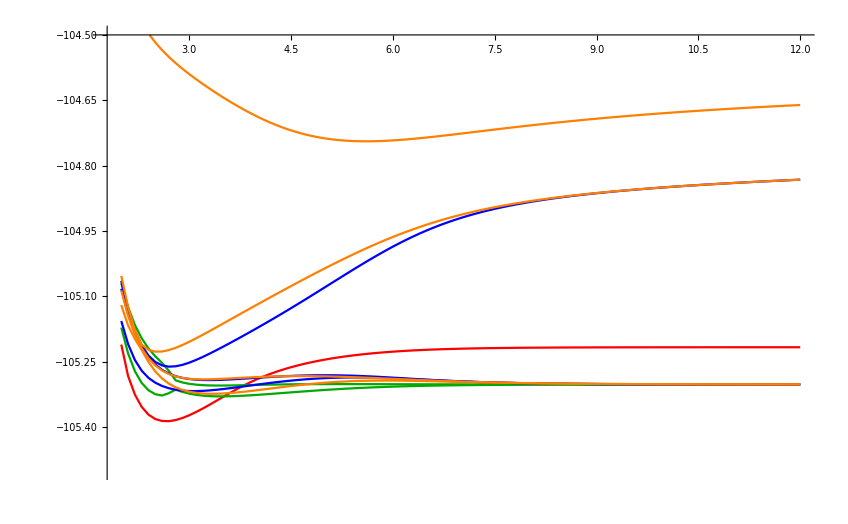

```mathematica
Show[ListPlot[Table[SA1LiFSTO3G⟦;;,{1,n+1}⟧,{n,1}],PlotStyle->Red,PlotRange->{All,{-105.5,-104.5}},Joined->True],
ListPlot[Table[SA2LiFSTO3G⟦;;,{1,n+1}⟧,{n,2}],PlotStyle->Darker@Green,PlotRange->{All,{-105.5,-104.5}},Joined->True],
ListPlot[Table[SA3LiFSTO3G⟦;;,{1,n+1}⟧,{n,3}],PlotStyle->Blue,PlotRange->{All,{-105.5,-104.5}},Joined->True],
ListPlot[Table[SA4LiFSTO3G⟦;;,{1,n+1}⟧,{n,4}],PlotStyle->Orange,PlotRange->{All,{-105.5,-104.5}},Joined->True]
]
```

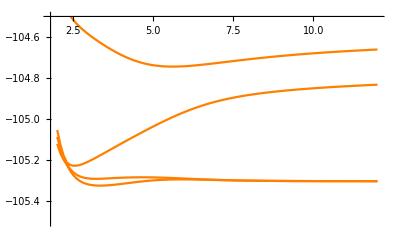

```mathematica
ListPlot[Table[SA4LiFSTO3G⟦;;,{1,n+1}⟧,{n,4}],PlotStyle->Orange,PlotRange->{All,{-105.5,-104.5}},Joined->True]
```

#### SA 6-31G

#### SS STO3G

These solutions correspond to the file mcscf.lif_frozen3.run and to the number 744, 6181, 1051, 116

```mathematica
SSLiFsto3gSinglet[[11]]
```

{3.,-105.373,-105.315,-105.274,-105.213}

```mathematica
SSLiFsto3gSinglet={{2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4000000000000004,3.5,3.6,3.7,3.8,3.9000000000000004,4.,4.1,4.2,4.300000000000001,4.4,4.5,4.6,4.7,4.800000000000001,4.9,5.,5.1,5.2,5.300000000000001,5.4,5.5,5.6,5.7,5.800000000000001,5.9,6.,6.1000000000000005,6.2,6.3,6.4,6.5,6.6000000000000005,6.7,6.800000000000001,6.9,7.,7.1000000000000005,7.2,7.300000000000001,7.4,7.5,7.6000000000000005,7.7,7.800000000000001,7.9,8.,8.100000000000001,8.2,8.3,8.4,8.5,8.600000000000001,8.7,8.8,8.9,9.,9.100000000000001,9.2,9.3,9.4,9.5,9.600000000000001,9.7,9.8,9.9,10.,10.1,10.200000000000001,10.3,10.4,10.5,10.6,10.700000000000001,10.8,10.9,11.,11.1,11.200000000000001,11.3,11.4,11.5,11.600000000000001,11.700000000000001,11.8,11.9,12.},{-105.22097788530344,-105.28251808219385,-105.32502062126818,-105.35334252056302,-105.37118447965737,-105.38133065699473,-105.38585291441613,-105.38627966373005,-105.38373173268342,-105.3790287826196,-105.37281616425543,-105.36539920788766,-105.35724433912792,-105.34856244243323,-105.33957054373788,-105.33047956620074,-105.3215089873888,-105.31285887476176,-105.30467110281057,-105.29702337194519,-105.28994468393272,-105.2834321262378,-105.27746340876946,-105.27200547821036,-105.26702027779649,-105.2624684949299,-105.25831189267456,-105.25451465075496,-105.2510440257756,-105.24787055790875,-105.24496799015421,-105.24231301984936,-105.23988496662238,-105.23766541394266,-105.23563786110914,-105.23378740754015,-105.2321004804807,-105.23056460979872,-105.22916824862277,-105.2279006355595,-105.2267516926108,-105.22571195228029,-105.22477250741392,-105.22392497782234,-105.22316148848188,-105.22247465499554,-105.22185757289701,-105.22130380824423,-105.2208073877193,-105.22036278710385,-105.2199649175395,-105.21960910938768,-105.2192910938062,-105.21900698235068,-105.21875324503803,-105.21852668734874,-105.21832442665962,-105.21814386855854,-105.21798268345245,-105.21783878380151,-105.21771030226219,-105.21759557093755,-105.21749310188437,-105.2174015689651,-105.21731979108667,-105.21724671683366,-105.2171814104644,-105.21712303922723,-105.21707086192244,-105.21702421864182,-105.21698252159308,-105.21694524692722,-105.21691192747812,-105.216882146331,-105.21685553113436,-105.21683174908016,-105.21681050247751,-105.21679152485395,-105.21677457752223,-105.21675944655634,-105.2167459401286,-105.2167338861599,-105.21672313024679,-105.21671353382673,-105.21670497255327,-105.21669733485349,-105.21669052064222,-105.21668444017753,-105.21667901303377,-105.21667416718232,-105.21666983816343,-105.21666596834213,-105.21666250623477,-105.21665940589989,-105.21665662638686,-105.21665413123573,-105.21665188802359,-105.21664986789683,-105.21664804538968,-105.21664639783347,-105.21664490519255},{-105.02007016162509,-105.10028931836132,-105.15998042529532,-105.20429866570551,-105.23715494406218,-105.26149374207061,-105.27951329075768,-105.29284209180364,-105.30267973562086,-105.30990732182234,-105.31522041557992,-105.31895087824097,-105.32159666585721,-105.32337247814573,-105.32447572521319,-105.3250557739345,-105.32522665708392,-105.32507633192785,-105.32467347000795,-105.32407245754065,-105.32331707851196,-105.32244321388862,-105.32148079852173,-105.32045521616642,-105.31938827113034,-105.31829884675378,-105.31720333660492,-105.31611592028969,-105.3150487384606,-105.31401201063298,-105.31301412782517,-105.31206174231666,-105.31115986838078,-105.31031200083089,-105.30952025270975,-105.30878550946481,-105.3081075944157,-105.30748543906728,-105.30691725201858,-105.30640067942394,-105.30593295439253,-105.30551102960382,-105.30513169283503,-105.3047916641475,-105.30448767524713,-105.30421653216851,-105.30397516292626,-105.30376065202881,-105.3035702638141,-105.30340145651431,-105.30325188880674,-105.3031194204303,-105.30300210823549,-105.30289819883431,-105.3028061188304,-105.30272446342747,-105.30265198407335,-105.30258757564944,-105.30253026361484,-105.30247919141156,-105.3024336083545,-105.30239285817191,-105.30235636829954,-105.30232363998982,-105.30229423926843,-105.30226778873472,-105.3022439601902,-105.30222246806079,-105.30220306356668,-105.30218552959138,-105.30216967619417,-105.30215533670936,-105.30214236437507,-105.30213062943989,-105.30212001668903,-105.30211042334543,-105.30210175729589,-105.30209393560017,-105.30208688324487,-105.30208053210795,-105.30207482002818,-105.30206969032683,-105.30206509084796,-105.30206097375928,-105.30205729503483,-105.30205401412697,-105.3020510936798,-105.30204849928349,-105.30204619926322,-105.3020441644898,-105.30204236821442,-105.30204078591412,-105.30203939515141,-105.302038175441,-105.30203710812408,-105.30203617624737,-105.30203536444813,-105.30203465884176,-105.30203404691495,-105.30203351742155,-105.30203306028386},{-105.06668656700984,-105.13528697798623,-105.18640798402933,-105.22416770177286,-105.24770471169094,-105.25981505148259,-105.26722890653274,-105.27151050634875,-105.27366590578487,-105.27437630996674,-105.27415738595309,-105.27319646188965,-105.27186003640469,-105.27025963760784,-105.26850314184736,-105.26666227131928,-105.26478269886643,-105.26289167617648,-105.26100388592425,-105.25912592305212,-105.25725966498732,-105.25540472554637,-105.25356015831547,-105.25172555814595,-105.24990169350485,-105.24809078496166,-105.24629652679376,-105.24452393109318,-105.24277905807872,-105.24106868302414,-105.23939993923585,-105.23777996739858,-105.2362155939134,-105.23471305417547,-105.23327777085692,-105.23191419210714,-105.2306256901692,-105.22941451728778,-105.2282818130143,-105.22722765508611,-105.2262511449593,-105.22535051870702,-105.22452327424782,-105.22376630662819,-105.22307604416382,-105.2224485795526,-105.22187979144365,-105.22136545330635,-105.22090132767855,-105.2204832449649,-105.22010716683815,-105.21976923498248,-105.21946580640416,-105.21919347684498,-105.2189490939864,-105.21872976217213,-105.21853284030652,-105.21835593447781,-105.21819688667384,-105.21805376078703,-105.21792482690424,-105.2178085447017,-105.21770354659057,-105.21760862110716,-105.21752269691764,-105.21744482768834,-105.21737417798916,-105.21731001032798,-105.21725167334601,-105.21719859118048,-105.2171502539554,-105.2171062093421,-105.21706605512773,-105.21702943270401,-105.21699602140141,-105.2169655335806,-105.21693771040273,-105.21691231819766,-105.21688914536035,-105.21686799970179,-105.21684870619693,-105.21683110507003,-105.21681505016737,-105.21680040757226,-105.21678705442307,-105.21677487789931,-105.21676377434794,-105.21675364852294,-105.21674441291749,-105.21673598717302,-105.21672829754952,-105.21672127644376,-105.21671486195126,-105.21670899746036,-105.21670363127251,-105.21669871624924,-105.21669420947832,-105.21669007195901,-105.21668626830318,-105.21668276645428,-105.21667953741995},{-104.95878056700698,-105.02377845415276,-105.07326287830779,-105.11090218511079,-105.13952471108269,-105.16129717101508,-105.17786924403424,-105.19049057049087,-105.20010447941412,-105.20742194719271,-105.21302777735802,-105.21718043457253,-105.2203330705897,-105.22267025981913,-105.22437039430919,-105.22557058566586,-105.22637687733075,-105.22687187386099,-105.22712045033694,-105.22717402749608,-105.22707377034963,-105.22685297643831,-105.22653885373934,-105.22615383991459,-105.2257165787219,-105.22524264236935,-105.22474506787877,-105.22423475938253,-105.22372079554067,-105.2232106711194,-105.22271049371662,-105.22222515026633,-105.22175845306954,-105.22131327192562,-105.22089165400541,-105.2204949375685,-105.22012385475723,-105.21977862798101,-105.21945905782731,-105.2191646028519,-105.218894451171,-105.2186475839397,-105.21842283093116,-105.21821891855967,-105.21803451078172,-105.21786824338808,-105.21771875223655,-105.21758469600913,-105.2174647740801,-105.21735774007871,-105.21726241170578,-105.21717767735011,-105.21710250000278,-105.21703591894276,-105.21697704961369,-105.2169250820784,-105.21687927838421,-105.21683896912938,-105.21680354948452,-105.21677247486969,-105.21674525646415,-105.21672145667766,-105.21670068469656,-105.21668259217752,-105.21666686915019,-105.21665324016836,-105.21664146072808,-105.21663131397088,-105.21662260766821,-105.21661517148443,-105.21660885450817,-105.21660352303536,-105.21659905859075,-105.21659535616598,-105.21659232265814,-105.21658987549026,-105.21658794139353,-105.21658645533664,-105.21658535958434,-105.21658460287152,-105.21658413967589,-105.21658392958231,-105.21658393672271,-105.21658412941143,-105.21658563137547,-105.21658595086312,-105.21658640221146,-105.2165869632487,-105.2165876144419,-105.21658833862594,-105.21658912075627,-105.21658994768747,-105.21659080797565,-105.21659169169732,-105.21659259028725,-105.21659349639278,-105.21659440373955,-105.21659530701085,-105.21659620174,-105.21659708420987,-105.21659795136479}}//Transpose;
```

These solutions correspond to the file mcscf . lif_frozen3 . run and to the number 12540, 2735, 58, 145, 521

```mathematica
SSLiFsto3gTriplet={{2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4000000000000004,3.5,3.6,3.7,3.8,3.9000000000000004,4.,4.1,4.2,4.300000000000001,4.4,4.5,4.6,4.7,4.800000000000001,4.9,5.,5.1,5.2,5.300000000000001,5.4,5.5,5.6,5.7,5.800000000000001,5.9,6.,6.1000000000000005,6.2,6.3,6.4,6.5,6.6000000000000005,6.7,6.800000000000001,6.9,7.,7.1000000000000005,7.2,7.300000000000001,7.4,7.5,7.6000000000000005,7.7,7.800000000000001,7.9,8.,8.100000000000001,8.2,8.3,8.4,8.5,8.600000000000001,8.7,8.8,8.9,9.,9.100000000000001,9.2,9.3,9.4,9.5,9.600000000000001,9.7,9.8,9.9,10.,10.1,10.200000000000001,10.3,10.4,10.5,10.6,10.700000000000001,10.8,10.9,11.,11.1,11.200000000000001,11.3,11.4,11.5,11.600000000000001,11.700000000000001,11.8,11.9,12.},{-105.09454047046088,-105.1531771341669,-105.19672472350646,-105.22886570810765,-105.25243257764576,-105.26958765556061,-105.28196928414829,-105.29081056590388,-105.29703477176476,-105.30133073243374,-105.30425572258345,-105.30605802386697,-105.30715452279534,-105.30771167677744,-105.30788612881551,-105.30779410980004,-105.30752171331783,-105.30713255699122,-105.30667350039221,-105.30617890890379,-105.30567382474797,-105.30517631565588,-105.30469920647138,-105.30425135117657,-105.30383856681709,-105.30346432292997,-105.3031302579166,-105.30283657573658,-105.30258236146148,-105.30236584203648,-105.30218460893215,-105.30203581204147,-105.30191632912022,-105.30182291200668,-105.30175230947228,-105.30170136637173,-105.30166709934436,-105.30164675025402,-105.30163781945517,-105.3016380817259,-105.3016455881007,-105.3016586569468,-105.30167585744357,-105.30169598825836,-105.30171805373193,-105.30174123937105,-105.3017648879493,-105.30178847708781,-105.30181159882406,-105.30183394140457,-105.30185527333563,-105.30187542959621,-105.30189429984021,-105.30191181836794,-105.30192795564989,-105.30194271117823,-105.30195610745764,-105.30196818494801,-105.3019789978216,-105.30198861040033,-105.30199709417093,-105.30200452529054,-105.30201098251172,-105.30201654546386,-105.30202129324745,-105.3020253032938,-105.302028650457,-105.30203140631045,-105.30203363861341,-105.30203541093375,-105.30203678239783,-105.30203780755491,-105.3020385363339,-105.30203901408088,-105.30203928166304,-105.3020393756237,-105.30203932838184,-105.30203916846106,-105.30203892074323,-105.30203860673694,-105.30203824485068,-105.30203785067478,-105.30203743725323,-105.30203701535304,-105.30203659372188,-105.30203617933124,-105.30203577760683,-105.30203539264116,-105.30203502738777,-105.30203468384133,-105.30203436319609,-105.30203406599011,-105.30203379223082,-105.30203354150638,-105.30203331308168,-105.30203310598043,-105.30203291905447,-105.30203275104277,-105.30203260061923,-105.30203246643157,-105.30203234713399},{-104.91033181114074,-104.9947157400405,-105.05849557835734,-105.10672878000538,-105.1432592283117,-105.17098692790253,-105.1920836993985,-105.2081663289176,-105.22043427022433,-105.22977713832859,-105.23690272784798,-105.24216852175957,-105.24608627873756,-105.24889505493678,-105.25081450125965,-105.25201583415954,-105.25263409211978,-105.2527770802163,-105.25253195722203,-105.25197012568833,-105.25115088139846,-105.25012414077172,-105.24893247311338,-105.24761260385692,-105.24619651432482,-105.24471223561392,-105.24318441415365,-105.24163471117859,-105.24008208596976,-105.23854300221262,-105.23703158773819,-105.23555977001908,-105.23413740308104,-105.23277239590954,-105.23147084796754,-105.23023719402978,-105.2290743580321,-105.22798391398004,-105.22696625091893,-105.22602073850032,-105.22514588959845,-105.22433951665607,-105.22359887887282,-105.22292081791635,-105.22230188046014,-105.22173842649174,-105.22122672293804,-105.22076302268972,-105.22034362956664,-105.21996495011217,-105.21962353336743,-105.21931609994327,-105.21903956177366,-105.21879103395952,-105.21856784005053,-105.21836751203278,-105.21818778616927,-105.21802659570743,-105.21788206133121,-105.21775248009872,-105.21763631346876,-105.21753217491626,-105.21743881750878,-105.21735512174408,-105.21728008385828,-105.2172128047507,-105.21715247962376,-105.21709838838797,-105.2170498868511,-105.21700639868774,-105.21696740816698,-105.21693245359839,-105.21690112145512,-105.21687304112342,-105.21684788022817,-105.21682534047815,-105.21680515398566,-105.21678708000704,-105.21677090206117,-105.21675642538123,-105.21674347465957,-105.2167318920566,-105.21672153543064,-105.21671227677118,-105.21670400080498,-105.2166966037515,-105.21668999221221,-105.21668493841138,-105.21667951077458,-105.2166746644466,-105.21667033497035,-105.21666646471202,-105.21666300218973,-105.21665990146387,-105.2166571215866,-105.21665462610113,-105.21665238258748,-105.21665036225198,-105.21664853955188,-105.21664689185678,-105.21664539914127},{-104.89504915897959,-104.98025002895868,-105.04488258596345,-105.09398782244854,-105.13139426399097,-105.1599878694348,-105.18192823122831,-105.19882217709764,-105.21186169117665,-105.22193136135236,-105.22973555095146,-105.23563250632313,-105.24013260154462,-105.24347691340978,-105.24588721815003,-105.24753728787407,-105.24856494197732,-105.24908084235065,-105.2491749769649,-105.24892148212056,-105.24838225062592,-105.2476096368667,-105.24664847969008,-105.24553760477997,-105.24431092884426,-105.24299826100933,-105.24162587750531,-105.2402169309457,-105.23879174348147,-105.23736802284071,-105.23596103133042,-105.23458373007973,-105.23324691414346,-105.23195934853533,-105.2307279108239,-105.22955774250235,-105.2284524088801,-105.22741406554566,-105.22644362845729,-105.22554094422016,-105.22470495703655,-105.22393386904643,-105.22322529119356,-105.22257638233447,-105.22198397490664,-105.22144468613003,-105.2209550142978,-105.22051142026156,-105.22011039465718,-105.21974851177637,-105.2194224712461,-105.21912912883448,-105.21886551778991,-105.21862886211942,-105.21841658317075,-105.21822630079353,-105.2180558302339,-105.2179031757888,-105.21776652210698,-105.21764422388158,-105.2175347945554,-105.21743689453479,-105.21734931930261,-105.21727098773209,-105.21720093081626,-105.21713828097072,-105.21708226200442,-105.21703217982355,-105.21698741388248,-105.21694740939003,-105.21691167024363,-105.21687975266346,-105.21685125948109,-105.21682583503814,-105.2168031606428,-105.21678295053678,-105.21676494832049,-105.21674892378887,-105.21673467013781,-105.21672200149173,-105.21671075072118,-105.21670076751128,-105.21669191665292,-105.21668407652506,-105.21667713774832,-105.21667100198296,-105.21666552465274,-105.21666074814623,-105.21665653420261,-105.21665281919515,-105.21664954612821,-105.21664666400652,-105.21664412726034,-105.21664189522596,-105.21663993166959,-105.2166382043553,-105.21663668464977,-105.21663534716176,-105.2166341694135,-105.2166331315412,-105.21663221602165},{-104.96733054508282,-105.03195151039777,-105.08108506445998,-105.11839451108156,-105.14670479652439,-105.16817972435634,-105.1844662003105,-105.1968112303796,-105.20615574638187,-105.21320865899825,-105.21855183173301,-105.22244630079052,-105.225340614586,-105.22742026338287,-105.22886369817644,-105.22980845652795,-105.2303613112954,-105.23060582438524,-105.2306079758073,-105.23042036075817,-105.23008531822147,-105.22963726086506,-105.2291044077727,-105.2285100715468,-105.22787361436606,-105.22721116003625,-105.22653612824662,-105.22585964124313,-105.22519084060421,-105.22453714190377,-105.2239044471547,-105.2232973287384,-105.22271919374624,-105.22217243414195,-105.22165856566077,-105.22117835674095,-105.22073194783528,-105.22031896098903,-105.21993859943844,-105.2195897370563,-105.21927099764105,-105.2189808242506,-105.2187175389627,-105.21847939360634,-105.21826461212254,-105.21807142527585,-105.21789809848359,-105.2177429535343,-105.21760438494731,-105.21748087170363,-105.21737098503142,-105.21727339288122,-105.21718686167472,-105.21711025585249,-105.2170425356886,-105.21698275378466,-105.21693005060007,-105.21688364931781,-105.21684285030423,-105.2168070253653,-105.21677561197035,-105.21674810756967,-105.21672406410418,-105.21670308278135,-105.21668480916092,-105.21666892858254,-105.21665516194882,-105.21664326186722,-105.21663300914315,-105.21662420961047,-105.21661669128574,-105.21661030181957,-105.2166049062298,-105.21660038488363,-105.216596631718,-105.21659355266333,-105.21659106425673,-105.21658909242231,-105.21658757139883,-105.21658644279803,-105.21658565477726,-105.21658516131352,-105.21658492156446,-105.21658489930508,-105.21658506243315,-105.21658538252869,-105.21658583446695,-105.21658639607278,-105.2165870478124,-105.21658777251791,-105.2165885551436,-105.21658938254193,-105.21659024326617,-105.2165911273894,-105.21659202634379,-105.21659293277268,-105.21659384039755,-105.21659474389757,-105.21659563883895,-105.21659652144979,-105.21659738868384},{-104.79655115171838,-104.87446415702831,-104.93224027505283,-104.97522806271364,-105.00751612000278,-105.03218304484751,-105.0515026219483,-105.06711676768546,-105.08018184389437,-105.091490497248,-105.10161905307709,-105.1107615467713,-105.11927533457882,-105.12723753162692,-105.134719307364,-105.14175862234426,-105.14837463311254,-105.15457704760074,-105.16037193977644,-105.1657651473986,-105.1707640691601,-105.17537844041127,-105.17962048840046,-105.18350473681812,-105.1870476350121,-105.19026712091083,-105.19318218143412,-105.19581244437218,-105.19817781696584,-105.20029817538335,-105.20219310339641,-105.20388167599933,-105.20538228310201,-105.20671248883141,-105.20788892276352,-105.2089272001308,-105.2098418685802,-105.21064637925737,-105.211353079962,-105.21197322791828,-105.21251701945567,-105.21299363367942,-105.21341128710176,-105.21377729623475,-105.21409814530031,-105.21437955649543,-105.21462656059506,-105.21484356608462,-105.2150344254139,-105.21520249735843,-105.21535070482066,-105.21548158770696,-105.21559735075884,-105.21569990640647,-105.21579091285118,-105.21587180767798,-105.21594383735437,-105.21600808300103,-105.21606548282338,-105.21611685157883,-105.21616289744043,-105.21620423657761,-105.21624140575268,-105.21627487319356,-105.21630504797308,-105.21633228809802,-105.21635690747823,-105.21637918193365,-105.21639935436154,-105.2164176391835,-105.2164342261637,-105.21644928368997,-105.2164629615824,-105.2164753935028,-105.21648669901157,-105.21649698533021,-105.21650634884413,-105.2165148763895,-105.21652264635301,-105.21652972961365,-105.21653619035327,-105.21654208675281,-105.21654747159782,-105.21655239280284,-105.21655689387276,-105.21656101430769,-105.21656478996412,-105.21656825337712,-105.21657143404941,-105.21657435871455,-105.21657705157749,-105.21657953453128,-105.21658182736115,-105.21658394792856,-105.21658591234196,-105.21658773511673,-105.21658942931991,-105.2165910067059,-105.21659247784068,-105.21659385221727,-105.21659513836057}}//Transpose;
```

These solutions correspond to the file mcscf . lif_frozen3 . run and to the number 579, 1747, 2366, 835, 82

```mathematica
SSLiFsto3gSpurious={{2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4000000000000004,3.5,3.6,3.7,3.8,3.9000000000000004,4.,4.1,4.2,4.300000000000001,4.4,4.5,4.6,4.7,4.800000000000001,4.9,5.,5.1,5.2,5.300000000000001,5.4,5.5,5.6,5.7,5.800000000000001,5.9,6.,6.1000000000000005,6.2,6.3,6.4,6.5,6.6000000000000005,6.7,6.800000000000001,6.9,7.,7.1000000000000005,7.2,7.300000000000001,7.4,7.5,7.6000000000000005,7.7,7.800000000000001,7.9,8.,8.100000000000001,8.2,8.3,8.4,8.5,8.600000000000001,8.7,8.8,8.9,9.,9.100000000000001,9.2,9.3,9.4,9.5,9.600000000000001,9.7,9.8,9.9,10.,10.1,10.200000000000001,10.3,10.4,10.5,10.6,10.700000000000001,10.8,10.9,11.,11.1,11.200000000000001,11.3,11.4,11.5,11.600000000000001,11.700000000000001,11.8,11.9,12.},{-105.2102712316791,-105.27109109034033,-105.31299891956391,-105.34082078305146,-105.35828142815197,-105.36814806802214,-105.37248062728379,-105.37281822404331,-105.37027943956403,-105.36569141540157,-105.35969364881963,-105.35252665699417,-105.34474185598683,-105.3365187718127,-105.32799405449357,-105.3193569166934,-105.3107044905015,-105.30211360606489,-105.29363785449664,-105.28534167288593,-105.27724663044822,-105.26946408340645,-105.26166240762528,-105.25413773867135,-105.24678522144777,-105.23956210506547,-105.23245931379847,-105.22546411413583,-105.21856937864592,-105.21177289952249,-105.20507651812107,-105.1984852191134,-105.19200624799561,-105.18564830249392,-105.1794208228379,-105.17333338966124,-105.16739522969432,-105.16161482499355,-105.15599961909756,-105.15055581206484,-105.14528823533783,-105.14020029658946,-105.13529398413908,-105.13056992024462,-105.1260274526089,-105.12166477384235,-105.1174790593586,-105.11346661518861,-105.10962302842485,-105.10594331432114,-105.10242205541859,-105.09905352935294,-105.09583182315808,-105.09275093289553,-105.08980484827568,-105.08698762258894,-105.08429342875867,-105.08171660266405,-105.07925167508387,-105.07689339371531,-105.07463673673648,-105.07247691933222,-105.07040939452007,-105.06842984948571,-105.06653419850964,-105.06471857342541,-105.06297931240954,-105.06131294777389,-105.05971619330401,-105.05818593157926,-105.0567192016104,-105.05531318704001,-105.05396520508576,-105.05267269633288,-105.05143321544281,-105.05024442279125,-105.04910407702779,-105.04801002851508,-105.04696021359497,-105.04595264960903,-105.04498543060268,-105.04405672362971,-105.04316476558088,-105.04230786045673,-105.04148437701409,-105.04069274671762,-105.03993146193594,-105.03919907432764,-105.03849419336919,-105.03781548498503,-105.03716167024683,-105.0365315241118,-105.03592387418124,-105.03533759945643,-105.03477162908918,-105.03422494110588,-105.03369656111191,-105.03318556096524,-105.03269105742197,-105.03221221075674,-105.03174822335653},{-105.21028456412108,-105.27110580049052,-105.31300627904864,-105.34083505545699,-105.3582895558527,-105.36815148804251,-105.37248991985591,-105.37283025151854,-105.37029063538682,-105.36604771829532,-105.36003556364346,-105.3529100386358,-105.3451344477646,-105.33690714836885,-105.32841278714233,-105.31979288276868,-105.31115702960078,-105.30259008046242,-105.29415599827546,-105.28589915925716,-105.27784446451554,-105.26999820562484,-105.26235124904453,-105.25488447254894,-105.2475748289459,-105.24040028749948,-105.23334288039824,-105.22639001724986,-105.21953461140421,-105.2127745388629,-105.206111793057,-105.19955155101134,-105.19310126578446,-105.18676984082322,-105.18056690971588,-105.174502228288,-105.16858517771384,-105.162824373973,-105.15722737430265,-105.15180047553035,-105.14654859110728,-105.14147519898827,-105.13658234885912,-105.13187071796139,-105.12733970473856,-105.12298754998322,-105.11881147596085,-105.11480783502353,-105.11097226048518,-105.10729981385256,-105.10378512385995,-105.10042251403667,-105.09720611668209,-105.09412997213404,-105.0911881130365,-105.08837463394954,-105.0856837471371,-105.08310982568584,-105.08064743530963,-105.07829135629096,-105.07603659702289,-105.07387840056295,-105.07181224552541,-105.06983384251494,-105.06793912717474,-105.06612425077878,-105.0643855691661,-105.06271963068107,-105.06112316365522,-105.05959306386896,-105.05812638232118,-105.05672031355519,-105.05537218471399,-105.0540794454376,-105.052839658662,-105.05165049234037,-105.05050971207436,-105.04941517461646,-105.04836482218988,-105.04735667755673,-105.04638883976243,-105.04545948047557,-105.04456684084545,-105.04370922880247,-105.04288501672636,-105.04209263941887,-105.04133059231718,-105.04059742989614,-105.0398917642118,-105.03921226354578,-105.03855765111638,-105.03792670383122,-105.0373182510556,-105.03673117338286,-105.0361644013936,-105.03561691439315,-105.03508773912439,-105.03457594845251,-105.03408066002096,-105.0336010348802,-105.03313627609225},{-105.21027129899028,-105.27109376411146,-105.31299524867092,-105.34082492527911,-105.35828027460296,-105.36814302832782,-105.37253742850469,-105.37287896243085,-105.37034126186603,-105.36574194602174,-105.35972610318248,-105.35259411973405,-105.34481115136322,-105.336573709796,-105.3280651519999,-105.31942536896348,-105.31076215443215,-105.30215921999023,-105.29368148513184,-105.28537548731886,-105.2772678838144,-105.26936657021778,-105.26166407730243,-105.25413768694715,-105.24677837370376,-105.2395562523569,-105.23245985457028,-105.22545868848982,-105.21856380506863,-105.21176726081272,-105.20507084509833,-105.19847951615372,-105.19199490788785,-105.18558948856929,-105.17936201757959,-105.1732745939672,-105.1673364443017,-105.16155605045347,-105.1559408557723,-105.15049706013986,-105.14522949484157,-105.14014156741516,-105.13523526606932,-105.13051121297269,-105.12596875576023,-105.12160608699362,-105.11742038205257,-105.11340794694877,-105.10956436876583,-105.10588466275757,-105.10236341147227,-105.09899489255787,-105.09577319306418,-105.0926923090712,-105.08974623031025,-105.086929010092,-105.084234821362,-105.08165800002043,-105.07919307686691,-105.0768347996191,-105.07457814647381,-105.07241833263423,-105.07035081113533,-105.06837126917918,-105.06647562106103,-105.064659998619,-105.0629207400641,-105.0612543777086,-105.05965762534939,-105.05812736557624,-105.05666063741003,-105.05525462450282,-105.05390664408016,-105.05261413673601,-105.05137465713942,-105.05018586567263,-105.04904552099262,-105.04795147346756,-105.04690165944541,-105.04589409627326,-105.04492687800219,-105.04399817169063,-105.043106214234,-105.04224930963733,-105.04142582666194,-105.04063419677594,-105.03987291235225,-105.03914052505333,-105.03843564435748,-105.03775693619416,-105.03710312163743,-105.0364729756475,-105.03586532582771,-105.03527905118318,-105.0347130808667,-105.0341663929078,-105.03363801291384,-105.03312701274507,-105.03263250915911,-105.03215366243168,-105.03168967495277},{-105.21028307053223,-105.27110434198286,-105.31300485007412,-105.34083365164658,-105.3582881736123,-105.3681501243529,-105.37248857214709,-105.37282891757039,-105.37028931324058,-105.36568751617155,-105.35966853399643,-105.35253369855087,-105.34474774006323,-105.3365078745243,-105.32799813788367,-105.31935935192222,-105.31070036084284,-105.30210530090108,-105.29363761623478,-105.28534159183384,-105.27724267006025,-105.26934834488331,-105.2616511191284,-105.25413356596346,-105.24677407495815,-105.23955164784081,-105.2324489495109,-105.22545370137587,-105.21855890134403,-105.21176236332181,-105.20506593241907,-105.19847459320586,-105.19199559012961,-105.18563761969645,-105.179410120981,-105.17332267359397,-105.16738450338666,-105.16160409167193,-105.15598888136498,-105.15054507200536,-105.14527749460666,-105.14018955648639,-105.13528324567358,-105.13055918418688,-105.12601671953487,-105.12165404416953,-105.11746832823536,-105.1134533559344,-105.10960977412739,-105.10593006262084,-105.10240880836454,-105.09904028678883,-105.09581858490785,-105.09273769877012,-105.08979161807909,-105.08697439612232,-105.084280205824,-105.08170338306671,-105.07923845863385,-105.07688018022934,-105.07462352603736,-105.0724637112511,-105.07039618889539,-105.06841664616377,-105.06652099734418,-105.06470537427803,-105.06296611514864,-105.06129975227502,-105.05970299944933,-105.05817273925754,-105.0567060107161,-105.05529999747327,-105.05395201675225,-105.05265950914348,-105.05142002931322,-105.05023123764227,-105.049090892784,-105.04799684510567,-105.04694703095282,-105.04593946767113,-105.04497224930972,-105.04404354292598,-105.0431515854135,-105.04229468077654,-105.04147119777429,-105.04067956787502,-105.03991828344986,-105.03918589616019,-105.03848101548431,-105.0378023073495,-105.03714849282984,-105.03651834688462,-105.03591069711652,-105.03532442253005,-105.03475845227722,-105.03421176438734,-105.03368338446701,-105.03317238437599,-105.03267788087123,-105.03219903422897,-105.03173504683751},{-105.21030579006727,-105.2710943639158,-105.31301089958998,-105.34083792730816,-105.35828754117117,-105.36816940762814,-105.37248067075687,-105.3728198366785,-105.3703070130223,-105.36570539044786,-105.35966273177851,-105.3525470908917,-105.34476935507085,-105.33650633325368,-105.32799765183788,-105.3193838479478,-105.31070190710246,-105.30210640748481,-105.29363966506314,-105.28547595971808,-105.27737457322462,-105.26947750912419,-105.26177746090411,-105.25425713252446,-105.24689498832046,-105.23967005973671,-105.23256501186151,-105.22556755058022,-105.21867065214876,-105.21187210834248,-105.20517374455719,-105.1985805292937,-105.1920996948784,-105.1857399294654,-105.17951066712916,-105.17342148531527,-105.16748160998863,-105.16169952431038,-105.15608267425787,-105.15063726317976,-105.14536812623348,-105.14027867487505,-105.1353709009926,-105.13064542998643,-105.12610161213202,-105.12173764196037,-105.1175506961211,-105.11353708120659,-105.10969238423611,-105.10601161981592,-105.10248936934177,-105.09911990888513,-105.09589732358027,-105.09281560733179,-105.08986874750846,-105.08705079494035,-105.08435592002905,-105.0817784561175,-105.0793129314751,-105.0769540913466,-105.07469691153753,-105.07253660496175,-105.07046862247476,-105.06848864921879,-105.06659259755091,-105.06477659750287,-105.06303698556745,-105.06137029248552,-105.05977323058116,-105.05824268107287,-105.05677568170495,-105.055369414942,-105.05402119690291,-105.05272846714864,-105.05148877938356,-105.05029979308826,-105.0491592660724,-105.0480650479115,-105.0470150742068,-105.04600736160309,-105.04504000348989,-105.04411116630256,-105.04321908634785,-105.04236206707643,-105.04153847672646,-105.04074674627297,-105.03998536762408,-105.03925289200423,-105.03854792848182,-105.03786914259801,-105.03721525506491,-105.03658504050334,-105.03597732619787,-105.03539099085641,-105.03482496335471,-105.0342782214643,-105.03374979055165,-105.03323874225316,-105.0327441931201,-105.03226530323636,-105.03180127481376}}//Transpose;
```

These solutions correspond to the file mcscf . lif_frozen3 . run and to the number 2208, 2142, 9651

```mathematica
SSLiFsto3gSb={{2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4000000000000004,3.5,3.6,3.7,3.8,3.9000000000000004,4.,4.1,4.2,4.300000000000001,4.4,4.5,4.6,4.7,4.800000000000001,4.9,5.,5.1,5.2,5.300000000000001,5.4,5.5,5.6,5.7,5.800000000000001,5.9,6.,6.1000000000000005,6.2,6.3,6.4,6.5,6.6000000000000005,6.7,6.800000000000001,6.9,7.,7.1000000000000005,7.2,7.300000000000001,7.4,7.5,7.6000000000000005,7.7,7.800000000000001,7.9,8.,8.100000000000001,8.2,8.3,8.4,8.5,8.600000000000001,8.7,8.8,8.9,9.,9.100000000000001,9.2,9.3,9.4,9.5,9.600000000000001,9.7,9.8,9.9,10.,10.1,10.200000000000001,10.3,10.4,10.5,10.6,10.700000000000001,10.8,10.9,11.,11.1,11.200000000000001,11.3,11.4,11.5,11.600000000000001,11.700000000000001,11.8,11.9,12.},{-105.02495028582557,-105.1046391062193,-105.16387155892798,-105.20779474003537,-105.24031326748624,-105.26436583441212,-105.28219539652738,-105.29495317718606,-105.30450785600245,-105.311513697947,-105.31663963783129,-105.32020617093238,-105.32270477058003,-105.32434549838675,-105.32532267165652,-105.32578370539026,-105.32584162185842,-105.32558414507687,-105.32508032710324,-105.32438537198125,-105.32354412856101,-105.32259359461828,-105.32156468995183,-105.32048349794837,-105.31937213111966,-105.31824435682776,-105.31711550426678,-105.31600740629474,-105.31493303165905,-105.31390052026379,-105.31291515681684,-105.31198034222696,-105.31109812175491,-105.31026950217512,-105.30949467103557,-105.30877311493016,-105.3081038204693,-105.30748543188638,-105.30691724502252,-105.30640067244046,-105.30593294743471,-105.3055110226735,-105.30513168593222,-105.30479165727219,-105.30448766839908,-105.3042165253472,-105.30397515613177,-105.3037606452611,-105.30357025707328,-105.30340144980053,-105.30325188212046,-105.30311941377212,-105.30300210160655,-105.30289819223556,-105.30280611226303,-105.30272445689391,-105.30265197757537,-105.3025875691895,-105.30253025719642,-105.30247918503787,-105.30243360202977,-105.30239285190135,-105.30235636208873,-105.30232363384577,-105.30229423319929,-105.30226778274978,-105.30224395430051,-105.30222246227925,-105.3022030579083,-105.30218552407355,-105.30216967083783,-105.30215533153891,-105.30214235941904,-105.30213062473223,-105.30212001226948,-105.30211041926145,-105.30210175360305,-105.30209393236534,-105.302086880549,-105.3020827153109,-105.30207599284246,-105.30207007580577,-105.30206487543506,-105.30206031188999,-105.30205631342548,-105.30205281563474,-105.30204976076743,-105.30204709710652,-105.30204477840101,-105.30204276334928,-105.30204101512679,-105.3020395009538,-105.30203819169935,-105.3020370615217,-105.30203608753574,-105.30203524951095,-105.30203452959488,-105.30203391206106,-105.30203338307628,-105.30203293048967,-105.30203254363767},{-105.02495176281644,-105.10464055761699,-105.16387298735185,-105.20775878985299,-105.23946450299385,-105.26180955237815,-105.27716861277426,-105.28730504256596,-105.29352111191508,-105.29677705224005,-105.29783111640396,-105.29706734005461,-105.29502898306032,-105.29197311850851,-105.28813884841782,-105.28371855110137,-105.27887170714125,-105.27373386981526,-105.2684207808725,-105.26302752444577,-105.25762411426828,-105.2522515323723,-105.24692266143744,-105.24162885133522,-105.23634892331928,-105.23105713975468,-105.22572867704481,-105.22034273828598,-105.21488397492303,-105.20934284521371,-105.20371535710234,-105.19800249334261,-105.19220954232033,-105.18634564562362,-105.18042488239776,-105.1744788458913,-105.16858684728872,-105.16282620142353,-105.15722920685432,-105.15180231283213,-105.146550432818,-105.14147704478489,-105.1365841984364,-105.13187257103044,-105.12734156102536,-105.1229894092291,-105.11881333792097,-105.11480969946741,-105.11097412719654,-105.10730168262819,-105.10378699451141,-105.10042438638824,-105.09720799057115,-105.0941318474115,-105.09118998956482,-105.08837651160292,-105.08568562580098,-105.0831117052562,-105.08064931569203,-105.07829323740074,-105.07603847878326,-105.07388028290542,-105.07181412838794,-105.06983572584289,-105.06794101091909,-105.06612613489581,-105.06438745361731,-105.06272151543212,-105.06112504867593,-105.05959494913267,-105.05812826780456,-105.05672219923785,-105.05537407057857,-105.0540813314685,-105.05284154484568,-105.05165237866588,-105.05051159853221,-105.04941706119865,-105.04836670889006,-105.04735856436974,-105.04639072668438,-105.0454613675035,-105.04456872797802,-105.04371111603876,-105.04288690406648,-105.04209452686372,-105.04133247986884,-105.04059931755718,-105.03989365198584,-105.03921415143682,-105.03855953912918,-105.03792859197142,-105.03732013932931,-105.03673306179736,-105.03616628995682,-105.03561880311344,-105.03508962801051,-105.03457783751509,-105.03408254927047,-105.03360292432784,-105.0331381657506},{-105.09453956455486,-105.15317623063699,-105.19672382525891,-105.2283337120821,-105.24770502811818,-105.25981536610252,-105.26722921833377,-105.27151081380912,-105.27334076160729,-105.27345928378236,-105.27230999392344,-105.27007821107134,-105.26715513185094,-105.26367598004796,-105.25977639174187,-105.25555592315622,-105.25108715693712,-105.24642275769763,-105.24160089188442,-105.23664934216042,-105.23158859654194,-105.22643415372319,-105.2211982462946,-105.21589113981567,-105.2105221209457,-105.20510024787512,-105.19963490627028,-105.19413619585649,-105.18861516509637,-105.18308391038224,-105.1775555578021,-105.17204414705166,-105.16656443728984,-105.1611316537005,-105.15576119190513,-105.15046829585117,-105.1452677239529,-105.14017341818308,-105.1351981913209,-105.13035344807516,-105.12564895555859,-105.12109267683012,-105.11669067747238,-105.11244710955148,-105.1083642705669,-105.10444272837647,-105.10068149785215,-105.09707825212813,-105.09362955092902,-105.09033107029234,-105.08717782119905,-105.08416434838804,-105.08128490422081,-105.07853359548818,-105.07590450332765,-105.07339177792899,-105.07098971061941,-105.06869278632068,-105.06649571945863,-105.06439347627081,-105.06238128619643,-105.06045464473019,-105.05860930977902,-105.05684129324904,-105.05514684929247,-105.05352246037559,-105.05196482209945,-105.05047082750602,-105.04903755143108,-105.04766223532027,-105.04634227281414,-105.04507519630242,-105.0438586645747,-105.0426904516323,-105.04156843667124,-105.04049059521483,-105.03945499134255,-105.03845977094257,-105.03750315590372,-105.03658343914896,-105.03569898041975,-105.03484820271169,-105.03402958926527,-105.03324168102931,-105.03248307451196,-105.03175241994434,-105.0310484196942,-105.03036982686866,-105.02971544405798,-105.02908412217758,-105.02847475937479,-105.02788629997144,-105.02731773342066,-105.02676809326206,-105.02623645606229,-105.02572194033264,-105.02522370542219,-105.02474095038062,-105.02427291279263,-105.0238188675878,-105.0233781258236}}//Transpose;
```

These solutions correspond to the file mcscf . lif_r5_frozen3 . run and to the number 5411,  4822, 12, 40 and to a minimum obtained by a kick on the lowest solution

```mathematica
SSLiFsto3gSingletR5⟦31⟧
```

{5.,-105.313,-105.245,-105.239,-105.223,-105.316}

```mathematica
SSLiFsto3gSingletR5={{2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4000000000000004,3.5,3.6,3.7,3.8,3.9000000000000004,4.,4.1,4.2,4.300000000000001,4.4,4.5,4.6,4.7,4.800000000000001,4.9,5.,5.1,5.2,5.300000000000001,5.4,5.5,5.6,5.7,5.800000000000001,5.9,6.,6.1000000000000005,6.2,6.3,6.4,6.5,6.6000000000000005,6.7,6.800000000000001,6.9,7.,7.1000000000000005,7.2,7.300000000000001,7.4,7.5,7.6000000000000005,7.7,7.800000000000001,7.9,8.,8.100000000000001,8.2,8.3,8.4,8.5,8.600000000000001,8.7,8.8,8.9,9.,9.100000000000001,9.2,9.3,9.4,9.5,9.600000000000001,9.7,9.8,9.9,10.,10.1,10.200000000000001,10.3,10.4,10.5,10.6,10.700000000000001,10.8,10.9,11.,11.1,11.200000000000001,11.3,11.4,11.5,11.600000000000001,11.700000000000001,11.8,11.9,12.},{-105.02495176946252,-105.10464056416652,-105.16387299382217,-105.20779615421509,-105.24031466310407,-105.26436721331706,-105.2821967751544,-105.29495452939639,-105.30450919474157,-105.31151502463905,-105.31659255339812,-105.32020747595918,-105.32270606562048,-105.32434678384571,-105.32532394785522,-105.32578497258535,-105.32584288025728,-105.32558539485134,-105.3250815684012,-105.32438660493534,-105.32354535329704,-105.32259481126133,-105.32156589863118,-105.32048469880456,-105.31937332429655,-105.31824554267442,-105.3171166829345,-105.31600857778062,-105.31493419608393,-105.31390167780717,-105.3128960911723,-105.3119814866506,-105.3110992599507,-105.31027063431185,-105.30949579676688,-105.30877423622509,-105.30810493641641,-105.30748654275271,-105.30691835108533,-105.30640177393398,-105.30593404456985,-105.30551211565563,-105.30513277495841,-105.30479274253084,-105.30448875006948,-105.30421760359823,-105.30397623112317,-105.30376171714292,-105.30357132598641,-105.30340251587678,-105.30325294548274,-105.30312047453597,-105.30300315987965,-105.30289924811922,-105.30280716585224,-105.3027255082774,-105.30265302683743,-105.30258861640962,-105.30253130244985,-105.30248022839659,-105.3024346435628,-105.30239389167505,-105.30235740016757,-105.30232467029266,-105.30229526807615,-105.30226881611807,-105.30224498622177,-105.30222349281614,-105.30220408712432,-105.30218655203515,-105.30217069761376,-105.30215635720215,-105.30214338404846,-105.30213164841216,-105.30212103509325,-105.30211144133231,-105.30210277503632,-105.30209495329163,-105.30208790111845,-105.30208160737759,-105.3020758390911,-105.30207071048645,-105.30206611255143,-105.30206199751925,-105.30205832146423,-105.30205504396554,-105.30205212782742,-105.30204953884754,-105.30204724562506,-105.30204521941131,-105.30204343401493,-105.30204186580619,-105.30204100985836,-105.30203965239849,-105.30203844471781,None,None,None,None,None,None},{-105.22097922351576,-105.28251938482335,-105.3250218925283,-105.35334376364027,-105.37118569705511,-105.38133185070262,-105.38585408600918,-105.38628081443343,-105.38373286341483,-105.3790298940001,-105.37277182317672,-105.36540028104703,-105.35724539242624,-105.34856347435606,-105.33957155184291,-105.33048054785039,-105.32150994160179,-105.31285980302573,-105.30467200791537,-105.2970242567982,-105.28994555109955,-105.28343297786604,-105.27746424663337,-105.27200630377614,-105.26702109228228,-105.26246929935611,-105.25831268790357,-105.25451543752251,-105.25104480471569,-105.24787132957388,-105.24494880047126,-105.24231377837235,-105.23988571918237,-105.23766616089515,-105.23563860278034,-105.23378814423243,-105.23210121247533,-105.23056533735854,-105.22916897199426,-105.22790135497522,-105.22675240828873,-105.22571266442576,-105.22477321621962,-105.2239256834699,-105.22316219114158,-105.22247535482617,-105.22185827004708,-105.22130450285245,-105.22080807991479,-105.22036347700663,-105.21996560526112,-105.21960979503166,-105.21929177746861,-105.21900766412018,-105.21875392499743,-105.21852736557463,-105.21832510322295,-105.21814454352517,-105.21798335688317,-105.2178394557533,-105.21771097278761,-105.21759624008588,-105.21749376970119,-105.21740223549241,-105.21732045636396,-105.21724738089773,-105.21718207334905,-105.21712370096348,-105.21707152253948,-105.21702487816604,-105.21698318004823,-105.21694590433476,-105.21691258385758,-105.21688280169823,-105.21685618550313,-105.21683240246067,-105.21681115487686,-105.21679217627505,-105.21677522796382,-105.2167600960119,-105.2167465885855,-105.21673453359853,-105.2167237766394,-105.21671417913494,-105.21670561672694,-105.21669797782707,-105.2166911623324,-105.21668508047763,-105.2166796518084,-105.21667480425782,-105.21667047331898,-105.21666660128999,-105.2166631365932,-105.21666003314448,-105.2166572497579,-105.21665474952418,-105.21665249893057,-105.21665046433479,None,None,None},{-105.21025478269335,-105.27107638544368,-105.31297712855599,-105.34080620262246,-105.24770479511903,-105.2598151344532,-105.26722898868874,-105.27151058750695,-105.27366598584237,-105.2743763888683,-105.27411113793394,-105.27319653843463,-105.27186011178807,-105.27025971185756,-105.26850321499977,-105.2666623434171,-105.26478276995546,-105.26289174630503,-105.26100395514084,-105.25912599140499,-105.25725973252298,-105.25540479230916,-105.25356022434798,-105.25172562348794,-105.24990175819369,-105.24809084903184,-105.24629659027822,-105.24452399402261,-105.24277912048137,-105.24106874492776,-105.23938082083198,-105.23778002837895,-105.23621565446753,-105.23471311432547,-105.23327783062356,-105.23191425151047,-105.23062574922794,-105.2294145760198,-105.22828187143696,-105.22722771321538,-105.22625120281023,-105.22535057629396,-105.22452333158442,-105.22376636372708,-105.22307610103715,-105.2224486362108,-105.22187984789778,-105.22136550956554,-105.22090138375194,-105.22048330086109,-105.22010722256462,-105.21976929054682,-105.21946586181292,-105.21919353210433,-105.21894914910251,-105.21872981715016,-105.21853289515164,-105.21835598919485,-105.21819694126732,-105.21805381526104,-105.21792488126255,-105.21780859894844,-105.21770360072863,-105.21760867514016,-105.21752275084881,-105.21744488152024,-105.21737423172503,-105.21731006397027,-105.21725172689709,-105.21719864464288,-105.21715030733137,-105.2171062626342,-105.2170661083377,-105.21702948583392,-105.21699607445314,-105.2169655865561,-105.21693776330375,-105.21691237102601,-105.21688919811746,-105.21686805238942,-105.21684875881652,-105.21683115762335,-105.21681510265553,-105.21680045999668,-105.21678710678493,-105.21677493020022,-105.21676382658903,-105.21675370070538,-105.21674446504235,-105.21673603924152,-105.21672834956276,-105.21672132840278,-105.21671491385709,-105.21670904931406,-105.21670368307481,-105.21669876800128,-105.21669426118132,-105.21669012361303,-105.21668631990966,-105.21668281801365,-105.21667958893349},{-104.95877946411784,-105.02377734915223,-105.07326177555049,-105.11090108777877,-105.13952362144518,-105.16129609063366,-105.17786817393196,-105.19048951128497,-105.20010343142212,-105.20742091051339,-105.21297795411941,-105.21717942023365,-105.22033206708934,-105.22266926685761,-105.22436941155212,-105.22556961275741,-105.22637591390412,-105.2268709195456,-105.22711950476346,-105.22717309029963,-105.22707284117398,-105.22685205493644,-105.22653793957521,-105.22615293276303,-105.22571567826967,-105.22524174831511,-105.22474417993347,-105.22423387726843,-105.22371991899185,-105.22320979988206,-105.2226883683445,-105.22222428894044,-105.22175759639707,-105.22131241952637,-105.22089080585184,-105.2204940934351,-105.22012301445892,-105.21977779134589,-105.21945822469371,-105.21916377306725,-105.2188936245918,-105.21864676043107,-105.21842201036559,-105.21821810081732,-105.21803369575045,-105.21786743096183,-105.21771794231586,-105.21758388850023,-105.21746396889561,-105.21735693713566,-105.21726161092693,-105.21717687866231,-105.21710170333768,-105.21703512423555,-105.21697625680409,-105.2169242911098,-105.21687848920288,-105.21683818168532,-105.21680276373067,-105.21677169076237,-105.21674447396236,-105.21672067574335,-105.2166999052947,-105.21668181427546,-105.21666609271853,-105.21665246518046,-105.21664068716059,-105.21663054180313,-105.2166218368831,-105.21661440206879,-105.21660808645188,-105.21660275633369,-105.21659829324304,-105.21659459217688,-105.21659156003894,-105.21658911425833,-105.21658718157478,-105.21658569696602,-105.21658460270756,-105.21658384754635,-105.21658338597545,-105.21658317759722,-105.21658318656395,-105.21658338108642,-105.21658373300049,-105.21658421738505,-105.21658481222424,-105.21658549810968,-105.21658625797603,-105.21658707686946,-105.21658794174768,-105.21658884131483,-105.21659003318952,-105.21659091087186,-105.21659180082702,-105.21659269066953,None,None,None,None,None},{-105.2102711270791,-105.27109254177057,-105.31299294657464,-105.34082165546924,-105.35827624962177,-105.36813945223348,-105.37247850058111,-105.37561320213021,-105.37390182096831,-105.370316168653,-105.36550449129658,-105.35998302363821,-105.35419738683764,-105.3485856648533,-105.34365448005795,-105.33999433542385,-105.33764579047828,-105.33585274994674,-105.3342048784906,-105.33258218592864,-105.33095330077438,-105.32931602611777,-105.32767859577588,-105.32605271958617,-105.32445070401818,-105.32288417752682,-105.32136350872045,-105.31989754735133,-105.31849352906225,-105.31715707285127,-105.31589223792977,-105.31470162238737,-105.31358649216573,-105.31254693093331,-105.31158200224125,-105.3106899160164,-105.30986819240192,-105.3091138172472,-105.30842338499684,-105.30779322620184,-105.30721951821367,-105.306698378733,-105.3062259427427,-105.30579842395014,-105.3054121622437,-105.30506365884786,-105.3047496009132,-105.30446687722946,-105.30421258662884,-105.30398404050506,-105.30377876070082,-105.30359447385239,-105.30342910311606,-105.30328075805247,-105.30314772331039,-105.30302844662405,-105.30292152654584,-105.30282570023027,-105.30273983152006,-105.30266289951305,-105.30259398773651,-105.30253227400927,-105.30247702104172,-105.30242756778503,-105.30238332153263,-105.30234375074537,-105.30230837857432,-105.3022767770358,-105.30224856179423,-105.30222338750485,-105.30220094366604,-105.30218095093262,-105.30216315784577,-105.30214733793002,-105.30213328712324,-105.30212082149517,-105.30210977522593,-105.30209999880704,-105.30209135744398,-105.3020837296295,-105.30207700587046,-105.30207108754718,-105.30206588588837,-105.30206132104914,-105.30205732127682,-105.30205382215809,-105.30205076593286,-105.30204810087305,-105.30204578071542,-105.30204376414251,-105.3020420143108,-105.30204049841755,-105.30203918730402,-105.30203805509306,-105.30203707885687,-105.30203623831054,-105.30203551553147,-105.30203489470226,-105.30203436186761,-105.30203390470726,-105.30203351231478}}//Transpose;
```

These solutions correspond to the file mcscf . lif_r5 _frozen3_15kpts . run and to the number 2408, 1 ,  494 and the last one is the number 23354 in the file with 30k pts

```mathematica
SSLiFsto3gTripletR5={{2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4000000000000004,3.5,3.6,3.7,3.8,3.9000000000000004,4.,4.1,4.2,4.300000000000001,4.4,4.5,4.6,4.7,4.800000000000001,4.9,5.,5.1,5.2,5.300000000000001,5.4,5.5,5.6,5.7,5.800000000000001,5.9,6.,6.1000000000000005,6.2,6.3,6.4,6.5,6.6000000000000005,6.7,6.800000000000001,6.9,7.,7.1000000000000005,7.2,7.300000000000001,7.4,7.5,7.6000000000000005,7.7,7.800000000000001,7.9,8.,8.100000000000001,8.2,8.3,8.4,8.5,8.600000000000001,8.7,8.8,8.9,9.,9.100000000000001,9.2,9.3,9.4,9.5,9.600000000000001,9.7,9.8,9.9,10.,10.1,10.200000000000001,10.3,10.4,10.5,10.6,10.700000000000001,10.8,10.9,11.,11.1,11.200000000000001,11.3,11.4,11.5,11.600000000000001,11.700000000000001,11.8,11.9,12.},{-104.9103318111407,-104.99471574004035,-105.05849557835714,-105.10672878000535,-105.14325922831149,-105.17098692790246,-105.19208369939841,-105.20816632891757,-105.22043427022427,-105.2297771383286,-105.23685676840543,-105.24216852175964,-105.24608627873798,-105.24889505493671,-105.25081450125987,-105.25201583415955,-105.25263409211956,-105.25277708021629,-105.25253195722223,-105.25197012568857,-105.2511508813983,-105.25012414077169,-105.24893247311351,-105.24761260385725,-105.24619651432494,-105.24471223561383,-105.24318441415338,-105.24163471117868,-105.2400820859697,-105.23854300221255,-105.23701115867259,-105.23555977001907,-105.23413740308114,-105.2327723959094,-105.23147084796763,-105.23023719402957,-105.22907435803216,-105.22798391398014,-105.22696625091896,-105.22602073850042,-105.22514588959831,-105.22433951665614,-105.22359887887283,-105.22292081791618,-105.22230188046014,-105.22173842649171,-105.22122672293784,-105.22076302268972,-105.22034362956673,-105.21996495011194,-105.21962353336737,-105.21931609994314,-105.21903956177366,-105.21879103395943,-105.21856784005041,-105.21836751203283,-105.21818778616935,-105.21802659570723,-105.21788206133144,-105.2177524800986,-105.21763631346869,-105.21753217491627,-105.21743881750892,-105.2173551217444,-105.21728008385841,-105.21721280475057,-105.217152479624,-105.21709838838812,-105.21704988685092,-105.21700639868787,-105.21696740816702,-105.21693245359837,-105.21690112145501,-105.2168730411233,-105.21684788022813,-105.21682534047817,-105.21680515398548,-105.21678708000694,-105.21677090206121,-105.21675642538115,-105.21674347465958,-105.21673189205646,-105.21672153543034,-105.21671227677118,-105.21670400080481,-105.21669660375127,-105.21668999221242,-105.21668408217579,-105.21667879812199,-105.21667407221567,-105.21666984357897,-105.2166660576299,-105.21666266548407,-105.21665962341083,-105.21665689233618,-105.21665462608217,-105.2166523825875,-105.21665036225198,-105.2166485395517,-105.21664689185663,-105.21664539914114},{-104.89504915897948,-104.98025002895885,-105.04488258596339,-105.09398782244854,-105.13139426399094,-105.15998786943477,-105.18192823122837,-105.19882217709757,-105.21186169117675,-105.22193136135247,-105.22969018524205,-105.23563250632311,-105.24013260154459,-105.24347691340975,-105.24588721814996,-105.2475372878741,-105.24856494197738,-105.24908084235068,-105.2491749769647,-105.24892148212065,-105.248382250626,-105.24760963686678,-105.24664847969,-105.24553760477983,-105.2443109288443,-105.24299826100929,-105.24162587750526,-105.24021693094554,-105.23879174348136,-105.23736802284061,-105.23594146778876,-105.23458373007952,-105.23324691414322,-105.23195934853504,-105.23072791082336,-105.22955774250222,-105.2284524088801,-105.22741406554557,-105.22644362845692,-105.22554094421999,-105.22470495703635,-105.22393386904587,-105.223225291193,-105.22257638233381,-105.22198397490605,-105.22144468612922,-105.2209550142968,-105.22051142026051,-105.22011039465582,-105.21974851177497,-105.21942247124451,-105.21912912883253,-105.21886551778783,-105.21862886211676,-105.21841658316765,-105.21822630079018,-105.2180558302301,-105.2179031757844,-105.21776652210171,-105.21764422387567,-105.21753479454871,-105.21743689452684,-105.21734931929355,-105.2172709877214,-105.2172009308039,-105.21713828095618,-105.21708226198777,-105.21703217980394,-105.21698741385956,-105.21694740936346,-105.21691167021261,-105.21687975262712,-105.2168512593621,None,None,None,None,None,None,None,None,None,None,None,None,None,-105.21666552515184,-105.21666074868213,None,None,None,None,None,None,None,None,-105.21663668697188,-105.2166353492719,-105.21663417135136,-105.2166331333288,-105.21663221767093},{-104.96733054508283,-105.03195151039805,-105.08108506446004,-105.11839451108182,-105.1467047965246,-105.16817972435655,-105.18446620031054,-105.19681123037975,-105.20615574638182,-105.21320865899838,-105.21850430392827,-105.2224463007906,-105.22534061458609,-105.22742026338288,-105.22886369817664,-105.2298084565281,-105.2303613112955,-105.23060582438535,-105.23060797580749,-105.23042036075834,-105.23008531822167,-105.22963726086518,-105.22910440777275,-105.22851007154688,-105.22787361436627,-105.22721116003632,-105.226536128247,-105.22585964124343,-105.22519084060454,-105.22453714190397,-105.2238853473609,-105.2232973287388,-105.2227191937466,-105.22217243414228,-105.22165856566122,-105.22117835674143,-105.22073194783577,-105.22031896098974,-105.21993859943946,-105.21958973705743,-105.2192709976421,-105.21898082425186,-105.21871753896401,-105.21847939360771,-105.21826461212412,-105.21807142527746,-105.21789809848556,-105.21774295353643,-105.21760438494977,-105.21748087170644,-105.21737098503456,-105.2172733928848,-105.21718686167883,-105.21711025585685,-105.21704253569365,-105.21698275379025,-105.21693005060636,-105.21688364932498,-105.21684285031235,-105.21680702537437,-105.21677561198088,-105.2167481075814,-105.21672406411754,-105.21670308279678,-105.21668480917819,-105.2166689286019,-105.21665516197085,-105.21664326189251,-105.21663300917196,-105.21662420964317,-105.21661669132283,-105.21661030186225,-105.21660490627849,-105.21660038493934,-105.21659663178197,-105.21659355273646,-105.21659106434055,-105.2165890925186,-105.2165875715097,-105.21658644292587,-105.216585654925,-105.21658516148435,-105.21658492176198,-105.21658489953407,-105.21658506269884,-105.2165853828376,-105.21658583482686,-105.21658639649249,-105.21658704830222,-105.21658777309038,-105.21658855581359,-105.21658938332656,-105.21659024418531,-105.21659112846706,-105.21659202760685,-105.21659293425175,-105.21659384212793,-105.21659474591864,-105.21659564115743,-105.21659652412772,-105.21659739177349},{-105.02495188886746,-105.10464068150232,-105.16387310929224,-105.20779626809953,-105.24031477544852,-105.2643673243125,-105.28214646258311,-105.29527510021242,-105.30494744039137,-105.31203952577839,-105.31719397114995,-105.32088343372315,-105.32345724955582,-105.32517524294228,-105.32623206932792,-105.32677473091832,-105.3269152315148,-105.32673978025589,-105.32631553021437,-105.32569553436319,-105.32492239296815,-105.3240309268265,-105.32305011804014,-105.32200449811498,-105.32091512092762,-105.3198002281706,-105.31867569258942,-105.31755530671916,-105.31645097027487,-105.31537281688706,-105.31430741949103,-105.31332732962812,-105.31237226037638,-105.31146809237609,-105.31061753302433,-105.30982213149117,-105.30908241223045,-105.30839801367539,-105.30776782782596,-105.30719013661702,-105.30666274150593,-105.3061830834537,-105.30574835127938,-105.30535557716411,-105.30500171879105,-105.30468372820579,-105.30439860795377,-105.30414345539208,-105.30391549629863,-105.30371210903247,-105.30353084053382,-105.30336941544394,-105.30322573955894,-105.30309789873176,-105.30298415423621,-105.3028829354705,-105.30279283077213,-105.30271257697537,-105.30264104825386,-105.3025772446656,-105.30252028074258,-105.30246937437761,-105.30242383620066,-105.30238305956948,-105.30234651126115,-105.30231372291095,-105.30228428321193,-105.30225783087056,-105.3022340482907,-105.30221265595543,-105.30219340745907,-105.30217608514064,-105.30216049626866,-105.30214646972425,-105.30213385313256,-105.30212251039119,-105.3021123195507,-105.30210317100511,-105.30209496594628,-105.30208761505352,-105.3020810373781,-105.30207515939856,-105.30206991421723,-105.302065240877,-105.30206108377617,-105.30205739216782,-105.30205411972553,-105.30205122416429,-105.30204866690917,-105.30204641279727,-105.3020444298129,-105.30204268884665,-105.30204116347299,-105.30203982974729,-105.30203866601491,-105.30203765273524,-105.30203677231317,-105.3020360089434,-105.30203534846342,-105.30203477821347,-105.30203428690625}}//Transpose;
```

```mathematica
SSLiFPlotSinglet⟦11⟧
```

{3.,-105.373,-105.315,-105.317,None}

```mathematica
SSLiFPlotSinglet={{2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4000000000000004,3.5,3.6,3.7,3.8,3.9000000000000004,4.,4.1,4.2,4.300000000000001,4.4,4.5,4.6,4.7,4.800000000000001,4.9,5.,5.1,5.2,5.300000000000001,5.4,5.5,5.6,5.7,5.800000000000001,5.9,6.,6.1000000000000005,6.2,6.3,6.4,6.5,6.6000000000000005,6.7,6.800000000000001,6.9,7.,7.1000000000000005,7.2,7.300000000000001,7.4,7.5,7.6000000000000005,7.7,7.800000000000001,7.9,8.,8.100000000000001,8.2,8.3,8.4,8.5,8.600000000000001,8.7,8.8,8.9,9.,9.100000000000001,9.2,9.3,9.4,9.5,9.600000000000001,9.7,9.8,9.9,10.,10.1,10.200000000000001,10.3,10.4,10.5,10.6,10.700000000000001,10.8,10.9,11.,11.1,11.200000000000001,11.3,11.4,11.5,11.600000000000001,11.700000000000001,11.8,11.9,12.},{-105.22097788530344,-105.28251808219385,-105.32502062126818,-105.35334252056302,-105.37118447965737,-105.38133065699473,-105.38585291441613,-105.38627966373005,-105.38373173268342,-105.3790287826196,-105.37281616425543,-105.36539920788766,-105.35724433912792,-105.34856244243323,-105.33957054373788,-105.33047956620074,-105.3215089873888,-105.31285887476176,-105.30467110281057,-105.29702337194519,-105.28994468393272,-105.2834321262378,-105.27746340876946,-105.27200547821036,-105.26702027779649,-105.2624684949299,-105.25831189267456,-105.25451465075496,-105.2510440257756,-105.24787055790875,-105.24496799015421,-105.24231301984936,-105.23988496662238,-105.23766541394266,-105.23563786110914,-105.23378740754015,-105.2321004804807,-105.23056460979872,-105.22916824862277,-105.2279006355595,-105.2267516926108,-105.22571195228029,-105.22477250741392,-105.22392497782234,-105.22316148848188,-105.22247465499554,-105.22185757289701,-105.22130380824423,-105.2208073877193,-105.22036278710385,-105.2199649175395,-105.21960910938768,-105.2192910938062,-105.21900698235068,-105.21875324503803,-105.21852668734874,-105.21832442665962,-105.21814386855854,-105.21798268345245,-105.21783878380151,-105.21771030226219,-105.21759557093755,-105.21749310188437,-105.2174015689651,-105.21731979108667,-105.21724671683366,-105.2171814104644,-105.21712303922723,-105.21707086192244,-105.21702421864182,-105.21698252159308,-105.21694524692722,-105.21691192747812,-105.216882146331,-105.21685553113436,-105.21683174908016,-105.21681050247751,-105.21679152485395,-105.21677457752223,-105.21675944655634,-105.2167459401286,-105.2167338861599,-105.21672313024679,-105.21671353382673,-105.21670497255327,-105.21669733485349,-105.21669052064222,-105.21668444017753,-105.21667901303377,-105.21667416718232,-105.21666983816343,-105.21666596834213,-105.21666250623477,-105.21665940589989,-105.21665662638686,-105.21665413123573,-105.21665188802359,-105.21664986789683,-105.21664804538968,-105.21664639783347,-105.21664490519255},{-105.02007016162509,-105.10028931836132,-105.15998042529532,-105.20429866570551,-105.23715494406218,-105.26149374207061,-105.27951329075768,-105.29284209180364,-105.30267973562086,-105.30990732182234,-105.31522041557992,-105.31895087824097,-105.32159666585721,-105.32337247814573,-105.32447572521319,-105.3250557739345,-105.32522665708392,-105.32507633192785,-105.32467347000795,-105.32407245754065,-105.32331707851196,-105.32244321388862,-105.32148079852173,-105.32045521616642,-105.31938827113034,-105.31829884675378,-105.31720333660492,-105.31611592028969,-105.3150487384606,-105.31401201063298,-105.31301412782517,-105.31206174231666,-105.31115986838078,-105.31031200083089,-105.30952025270975,-105.30878550946481,-105.3081075944157,-105.30748543906728,-105.30691725201858,-105.30640067942394,-105.30593295439253,-105.30551102960382,-105.30513169283503,-105.3047916641475,-105.30448767524713,-105.30421653216851,-105.30397516292626,-105.30376065202881,-105.3035702638141,-105.30340145651431,-105.30325188880674,-105.3031194204303,-105.30300210823549,-105.30289819883431,-105.3028061188304,-105.30272446342747,-105.30265198407335,-105.30258757564944,-105.30253026361484,-105.30247919141156,-105.3024336083545,-105.30239285817191,-105.30235636829954,-105.30232363998982,-105.30229423926843,-105.30226778873472,-105.3022439601902,-105.30222246806079,-105.30220306356668,-105.30218552959138,-105.30216967619417,-105.30215533670936,-105.30214236437507,-105.30213062943989,-105.30212001668903,-105.30211042334543,-105.30210175729589,-105.30209393560017,-105.30208688324487,-105.30208053210795,-105.30207482002818,-105.30206969032683,-105.30206509084796,-105.30206097375928,-105.30205729503483,-105.30205401412697,-105.3020510936798,-105.30204849928349,-105.30204619926322,-105.3020441644898,-105.30204236821442,-105.30204078591412,-105.30203939515141,-105.302038175441,-105.30203710812408,-105.30203617624737,-105.30203536444813,-105.30203465884176,-105.30203404691495,-105.30203351742155,-105.30203306028386},{-105.02495176946252,-105.10464056416652,-105.16387299382217,-105.20779615421509,-105.24031466310407,-105.26436721331706,-105.2821967751544,-105.29495452939639,-105.30450919474157,-105.31151502463905,-105.31659255339812,-105.32020747595918,-105.32270606562048,-105.32434678384571,-105.32532394785522,-105.32578497258535,-105.32584288025728,-105.32558539485134,-105.3250815684012,-105.32438660493534,-105.32354535329704,-105.32259481126133,-105.32156589863118,-105.32048469880456,-105.31937332429655,-105.31824554267442,-105.3171166829345,-105.31600857778062,-105.31493419608393,-105.31390167780717,-105.3128960911723,-105.3119814866506,-105.3110992599507,-105.31027063431185,-105.30949579676688,-105.30877423622509,-105.30810493641641,-105.30748654275271,-105.30691835108533,-105.30640177393398,-105.30593404456985,-105.30551211565563,-105.30513277495841,-105.30479274253084,-105.30448875006948,-105.30421760359823,-105.30397623112317,-105.30376171714292,-105.30357132598641,-105.30340251587678,-105.30325294548274,-105.30312047453597,-105.30300315987965,-105.30289924811922,-105.30280716585224,-105.3027255082774,-105.30265302683743,-105.30258861640962,-105.30253130244985,-105.30248022839659,-105.3024346435628,-105.30239389167505,-105.30235740016757,-105.30232467029266,-105.30229526807615,-105.30226881611807,-105.30224498622177,-105.30222349281614,-105.30220408712432,-105.30218655203515,-105.30217069761376,-105.30215635720215,-105.30214338404846,-105.30213164841216,-105.30212103509325,-105.30211144133231,-105.30210277503632,-105.30209495329163,-105.30208790111845,-105.30208160737759,-105.3020758390911,-105.30207071048645,-105.30206611255143,-105.30206199751925,-105.30205832146423,-105.30205504396554,-105.30205212782742,-105.30204953884754,-105.30204724562506,-105.30204521941131,-105.30204343401493,-105.30204186580619,-105.30204100985836,-105.30203965239849,-105.30203844471781,None,None,None,None,None,None}}//Transpose;
```

```mathematica
SSLiFPlotTriplet={{2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4000000000000004,3.5,3.6,3.7,3.8,3.9000000000000004,4.,4.1,4.2,4.300000000000001,4.4,4.5,4.6,4.7,4.800000000000001,4.9,5.,5.1,5.2,5.300000000000001,5.4,5.5,5.6,5.7,5.800000000000001,5.9,6.,6.1000000000000005,6.2,6.3,6.4,6.5,6.6000000000000005,6.7,6.800000000000001,6.9,7.,7.1000000000000005,7.2,7.300000000000001,7.4,7.5,7.6000000000000005,7.7,7.800000000000001,7.9,8.,8.100000000000001,8.2,8.3,8.4,8.5,8.600000000000001,8.7,8.8,8.9,9.,9.100000000000001,9.2,9.3,9.4,9.5,9.600000000000001,9.7,9.8,9.9,10.,10.1,10.200000000000001,10.3,10.4,10.5,10.6,10.700000000000001,10.8,10.9,11.,11.1,11.200000000000001,11.3,11.4,11.5,11.600000000000001,11.700000000000001,11.8,11.9,12.},{-105.02495188886746,-105.10464068150232,-105.16387310929224,-105.20779626809953,-105.24031477544852,-105.2643673243125,-105.28214646258311,-105.29527510021242,-105.30494744039137,-105.31203952577839,-105.31719397114995,-105.32088343372315,-105.32345724955582,-105.32517524294228,-105.32623206932792,-105.32677473091832,-105.3269152315148,-105.32673978025589,-105.32631553021437,-105.32569553436319,-105.32492239296815,-105.3240309268265,-105.32305011804014,-105.32200449811498,-105.32091512092762,-105.3198002281706,-105.31867569258942,-105.31755530671916,-105.31645097027487,-105.31537281688706,-105.31430741949103,-105.31332732962812,-105.31237226037638,-105.31146809237609,-105.31061753302433,-105.30982213149117,-105.30908241223045,-105.30839801367539,-105.30776782782596,-105.30719013661702,-105.30666274150593,-105.3061830834537,-105.30574835127938,-105.30535557716411,-105.30500171879105,-105.30468372820579,-105.30439860795377,-105.30414345539208,-105.30391549629863,-105.30371210903247,-105.30353084053382,-105.30336941544394,-105.30322573955894,-105.30309789873176,-105.30298415423621,-105.3028829354705,-105.30279283077213,-105.30271257697537,-105.30264104825386,-105.3025772446656,-105.30252028074258,-105.30246937437761,-105.30242383620066,-105.30238305956948,-105.30234651126115,-105.30231372291095,-105.30228428321193,-105.30225783087056,-105.3022340482907,-105.30221265595543,-105.30219340745907,-105.30217608514064,-105.30216049626866,-105.30214646972425,-105.30213385313256,-105.30212251039119,-105.3021123195507,-105.30210317100511,-105.30209496594628,-105.30208761505352,-105.3020810373781,-105.30207515939856,-105.30206991421723,-105.302065240877,-105.30206108377617,-105.30205739216782,-105.30205411972553,-105.30205122416429,-105.30204866690917,-105.30204641279727,-105.3020444298129,-105.30204268884665,-105.30204116347299,-105.30203982974729,-105.30203866601491,-105.30203765273524,-105.30203677231317,-105.3020360089434,-105.30203534846342,-105.30203477821347,-105.30203428690625},{-105.09454047046088,-105.1531771341669,-105.19672472350646,-105.22886570810765,-105.25243257764576,-105.26958765556061,-105.28196928414829,-105.29081056590388,-105.29703477176476,-105.30133073243374,-105.30425572258345,-105.30605802386697,-105.30715452279534,-105.30771167677744,-105.30788612881551,-105.30779410980004,-105.30752171331783,-105.30713255699122,-105.30667350039221,-105.30617890890379,-105.30567382474797,-105.30517631565588,-105.30469920647138,-105.30425135117657,-105.30383856681709,-105.30346432292997,-105.3031302579166,-105.30283657573658,-105.30258236146148,-105.30236584203648,-105.30218460893215,-105.30203581204147,-105.30191632912022,-105.30182291200668,-105.30175230947228,-105.30170136637173,-105.30166709934436,-105.30164675025402,-105.30163781945517,-105.3016380817259,-105.3016455881007,-105.3016586569468,-105.30167585744357,-105.30169598825836,-105.30171805373193,-105.30174123937105,-105.3017648879493,-105.30178847708781,-105.30181159882406,-105.30183394140457,-105.30185527333563,-105.30187542959621,-105.30189429984021,-105.30191181836794,-105.30192795564989,-105.30194271117823,-105.30195610745764,-105.30196818494801,-105.3019789978216,-105.30198861040033,-105.30199709417093,-105.30200452529054,-105.30201098251172,-105.30201654546386,-105.30202129324745,-105.3020253032938,-105.302028650457,-105.30203140631045,-105.30203363861341,-105.30203541093375,-105.30203678239783,-105.30203780755491,-105.3020385363339,-105.30203901408088,-105.30203928166304,-105.3020393756237,-105.30203932838184,-105.30203916846106,-105.30203892074323,-105.30203860673694,-105.30203824485068,-105.30203785067478,-105.30203743725323,-105.30203701535304,-105.30203659372188,-105.30203617933124,-105.30203577760683,-105.30203539264116,-105.30203502738777,-105.30203468384133,-105.30203436319609,-105.30203406599011,-105.30203379223082,-105.30203354150638,-105.30203331308168,-105.30203310598043,-105.30203291905447,-105.30203275104277,-105.30203260061923,-105.30203246643157,-105.30203234713399}}//Transpose;
```

```mathematica
Join[Table[2+i*0.05,{i,0,39}],Table[4+i*0.1,{i,0,80}]]
```

{2.,2.05,2.1,2.15,2.2,2.25,2.3,2.35,2.4,2.45,2.5,2.55,2.6,2.65,2.7,2.75,2.8,2.85,2.9,2.95,3.,3.05,3.1,3.15,3.2,3.25,3.3,3.35,3.4,3.45,3.5,3.55,3.6,3.65,3.7,3.75,3.8,3.85,3.9,3.95,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.,10.1,10.2,10.3,10.4,10.5,10.6,10.7,10.8,10.9,11.,11.1,11.2,11.3,11.4,11.5,11.6,11.7,11.8,11.9,12.}

```mathematica
SSLiFPlotMin={{2.,2.05,2.1,2.15,2.2,2.25,2.3,2.35,2.4,2.45,2.5,2.55,2.6,2.65,2.7,2.75,2.8,2.85,2.9,2.95,3.,3.05,3.1,3.1500000000000004,3.2,3.25,3.3,3.35,3.4000000000000004,3.45,3.5,3.55,3.6,3.6500000000000004,3.7,3.75,3.8,3.85,3.9000000000000004,3.95,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.300000000000001,6.4,6.5,6.6,6.7,6.800000000000001,6.9,7.,7.1,7.2,7.300000000000001,7.4,7.5,7.6,7.7,7.800000000000001,7.9,8.,8.100000000000001,8.2,8.3,8.4,8.5,8.600000000000001,8.7,8.8,8.9,9.,9.100000000000001,9.2,9.3,9.4,9.5,9.600000000000001,9.7,9.8,9.9,10.,10.100000000000001,10.2,10.3,10.4,10.5,10.600000000000001,10.7,10.8,10.9,11.,11.100000000000001,11.2,11.3,11.4,11.5,11.600000000000001,11.7,11.8,11.9,12.},{-105.21028566893878,-105.24340488715586,-105.27109584844919,-105.29407476369846,-105.31299314969772,-105.32841628531224,-105.34082216699404,-105.35163564646598,-105.35943251698126,-105.36536789184863,-105.36972000329257,-105.37272851097332,-105.37459955826023,-105.37551034020981,-105.37561320213011,-105.37503929497613,-105.37390182096841,-105.37229890941295,-105.37031616865283,-105.36802896573026,-105.36550449129662,-105.36280367463736,-105.35998302363821,-105.35709647856203,-105.35419738683757,-105.3513407231767,-105.34858566485326,-105.34599844954349,-105.3436544800581,-105.34163427227352,-105.33999433542391,-105.33870327850892,-105.33764579047828,-105.33671640605357,-105.33585274994681,-105.33502150065456,-105.33420487849033,-105.33339339867663,-105.3325821859287,-105.33176902898792,-105.33095330077444,-105.32931602611771,-105.32767859577608,-105.32605271958612,-105.32445070401816,-105.32288417752684,-105.32136350872045,-105.3198975473512,-105.3184935290623,-105.31715707285127,-105.31589223792977,-105.31470162238726,-105.31358649216558,-105.31254693093331,-105.31158200224127,-105.31068991601643,-105.309868192402,-105.30911381724717,-105.30842338499693,-105.30779322620197,-105.30721951821366,-105.306698378733,-105.30622594274269,-105.30579842395012,-105.3054121622438,-105.30506365884774,-105.30474960091314,-105.30446687722937,-105.30421258662886,-105.30398404050506,-105.3037787607008,-105.30359447385229,-105.30342910311603,-105.30328075805244,-105.30314772331039,-105.30302844662418,-105.30292152654582,-105.30282570023026,-105.30273983152004,-105.30266289951307,-105.30259398773637,-105.3025322740093,-105.30247702104178,-105.30242756778505,-105.30238332153277,-105.30234375074535,-105.3023083785744,-105.30227677703579,-105.30224856179434,-105.30222338750494,-105.30220094366608,-105.30218095093268,-105.30216315784568,-105.30214733793011,-105.30213328712318,-105.30212082149528,-105.30210977522611,-105.30209999880712,-105.302091357444,-105.3020837296294,-105.30207700587025,-105.3020710875472,-105.30206588588828,-105.30206132104917,-105.30205732127673,-105.30205382215803,-105.30205076593298,-105.30204810087312,-105.30204578071547,-105.30204376414241,-105.3020420143109,-105.30204049841764,-105.30203918730402,-105.30203805509325,-105.30203707885694,-105.30203623831048,-105.30203551553136,-105.30203489470229,-105.30203436186767,-105.30203390470709,-105.30203351231485}}//Transpose
```

{{2.,-105.21},{2.05,-105.243},{2.1,-105.271},{2.15,-105.294},{2.2,-105.313},{2.25,-105.328},{2.3,-105.341},{2.35,-105.352},{2.4,-105.359},{2.45,-105.365},{2.5,-105.37},{2.55,-105.373},{2.6,-105.375},{2.65,-105.376},{2.7,-105.376},{2.75,-105.375},{2.8,-105.374},{2.85,-105.372},{2.9,-105.37},{2.95,-105.368},{3.,-105.366},{3.05,-105.363},{3.1,-105.36},{3.15,-105.357},{3.2,-105.354},{3.25,-105.351},{3.3,-105.349},{3.35,-105.346},{3.4,-105.344},{3.45,-105.342},{3.5,-105.34},{3.55,-105.339},{3.6,-105.338},{3.65,-105.337},{3.7,-105.336},{3.75,-105.335},{3.8,-105.334},{3.85,-105.333},{3.9,-105.333},{3.95,-105.332},{4.,-105.331},{4.1,-105.329},{4.2,-105.328},{4.3,-105.326},{4.4,-105.324},{4.5,-105.323},{4.6,-105.321},{4.7,-105.32},{4.8,-105.318},{4.9,-105.317},{5.,-105.316},{5.1,-105.315},{5.2,-105.314},{5.3,-105.313},{5.4,-105.312},{5.5,-105.311},{5.6,-105.31},{5.7,-105.309},{5.8,-105.308},{5.9,-105.308},{6.,-105.307},{6.1,-105.307},{6.2,-105.306},{6.3,-105.306},{6.4,-105.305},{6.5,-105.305},{6.6,-105.305},{6.7,-105.304},{6.8,-105.304},{6.9,-105.304},{7.,-105.304},{7.1,-105.304},{7.2,-105.303},{7.3,-105.303},{7.4,-105.303},{7.5,-105.303},{7.6,-105.303},{7.7,-105.303},{7.8,-105.303},{7.9,-105.303},{8.,-105.303},{8.1,-105.303},{8.2,-105.302},{8.3,-105.302},{8.4,-105.302},{8.5,-105.302},{8.6,-105.302},{8.7,-105.302},{8.8,-105.302},{8.9,-105.302},{9.,-105.302},{9.1,-105.302},{9.2,-105.302},{9.3,-105.302},{9.4,-105.302},{9.5,-105.302},{9.6,-105.302},{9.7,-105.302},{9.8,-105.302},{9.9,-105.302},{10.,-105.302},{10.1,-105.302},{10.2,-105.302},{10.3,-105.302},{10.4,-105.302},{10.5,-105.302},{10.6,-105.302},{10.7,-105.302},{10.8,-105.302},{10.9,-105.302},{11.,-105.302},{11.1,-105.302},{11.2,-105.302},{11.3,-105.302},{11.4,-105.302},{11.5,-105.302},{11.6,-105.302},{11.7,-105.302},{11.8,-105.302},{11.9,-105.302},{12.,-105.302}}

ListPlot::ioproc: {{2.,-105.025},{2.1,-105.105},{2.2,-105.164},{2.3,-105.208},{2.4,-105.24},{2.5,-105.264},{2.6,-105.282},{2.7,-105.295},{2.8,-105.305},{2.9,-105.312},«91»} may contain non-machine-precision numbers, complex numbers, or invalid entries.

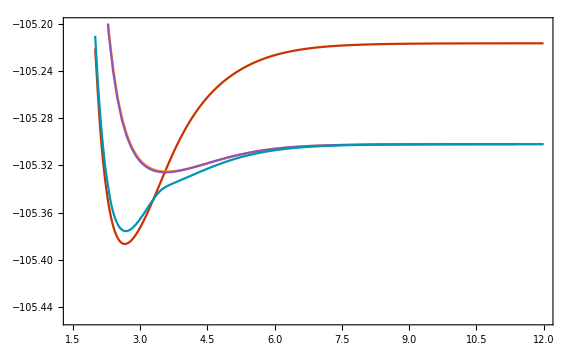

```mathematica
Show[ListPlot[Table[SSLiFPlotSinglet⟦;;,{1,n+1}⟧,{n,3}],PlotMarkers->False,PlotRange->{{1.5,12},{-105.45,-105.2}},PlotStyle->{RGBColor[0.790588, 0.201176, 0.],RGBColor[1., 0.607843, 0.],RGBColor[0.567426, 0.32317, 0.729831],RGBColor[0., 0.588235, 0.705882]},plotOptions],ListPlot[Table[SSLiFPlotMin⟦;;,{1,n+1}⟧,{n,1}],PlotMarkers->False,PlotRange->{{1.5,12},{-105.45,-105.2}},PlotStyle->{RGBColor[0., 0.588235, 0.705882]},plotOptions]]
```

### Plot LiF

#### STO3G

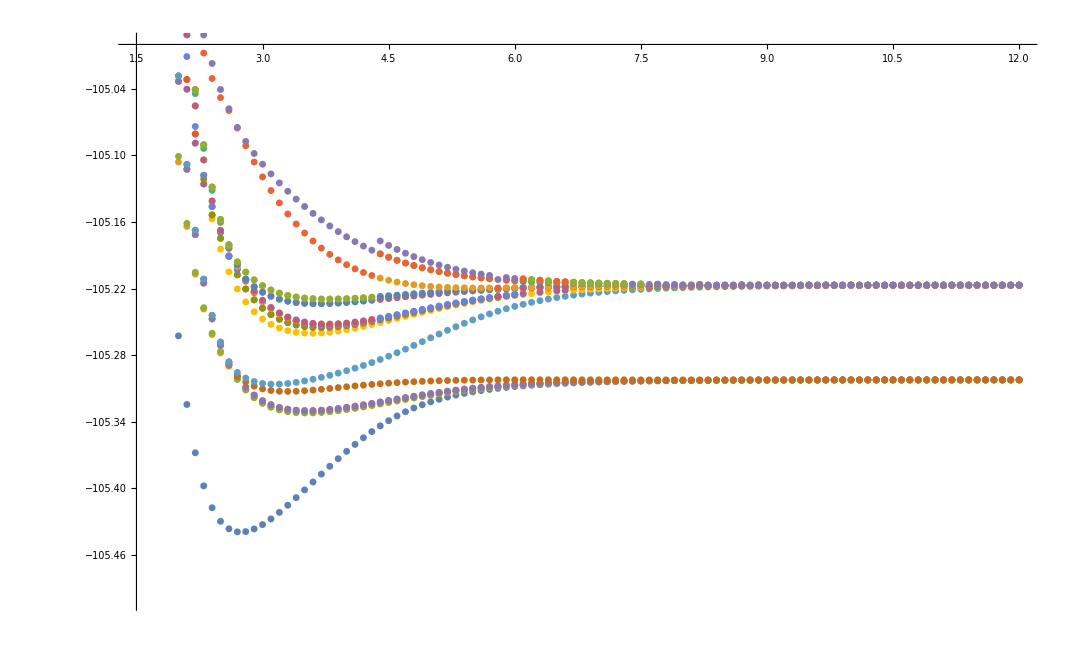

```mathematica
LiFFCISTO3G=ListPlot[Table[fciLiFsto3g⟦;;,{1,n+1}⟧,{n,20}],PlotRange->{{1.5,12},{-105.5,-105}}]
```

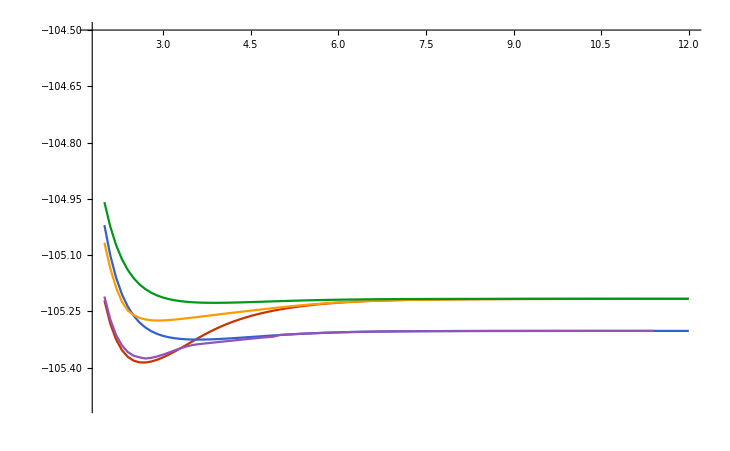

```mathematica
ListPlot[Table[SSLiFsto3gSinglet⟦;;,{1,n+1}⟧,{n,4}],PlotTheme->"VibrantColors",PlotRange->{All,{-105.5,-104.5}},Joined->True]
```

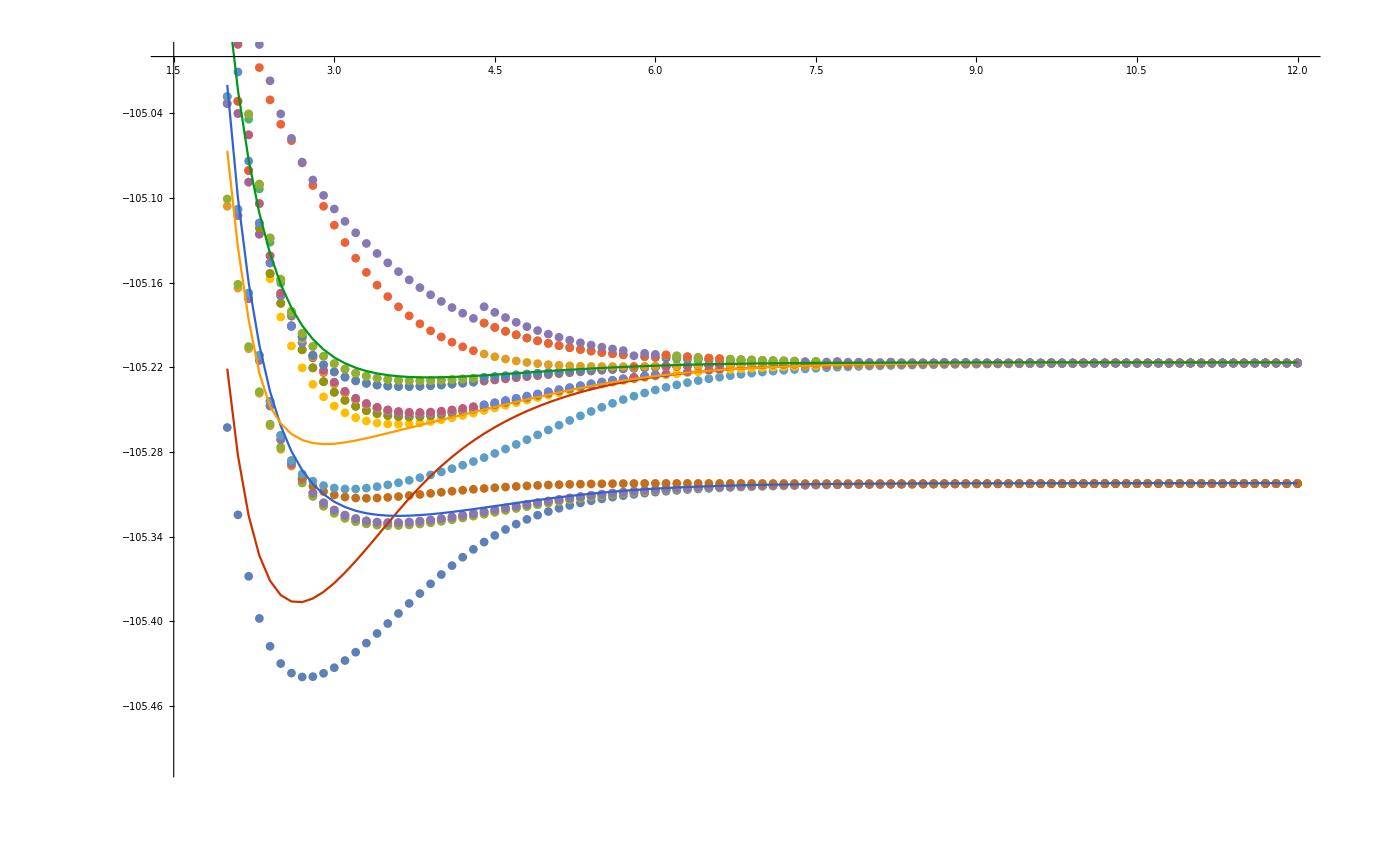

```mathematica
Show[LiFFCISTO3G,
ListPlot[Table[SSLiFsto3gSinglet⟦;;,{1,n+1}⟧,{n,4}],PlotTheme->"VibrantColors",PlotRange->{All,{-105.5,-104.5}},Joined->True]]
```

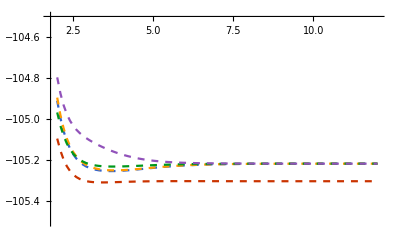

```mathematica
ListPlot[Table[SSLiFsto3gTriplet⟦;;,{1,n+1}⟧,{n,5}],PlotTheme->"VibrantColors",PlotRange->{All,{-105.5,-104.5}},Joined->True,PlotStyle->Dashed]
```

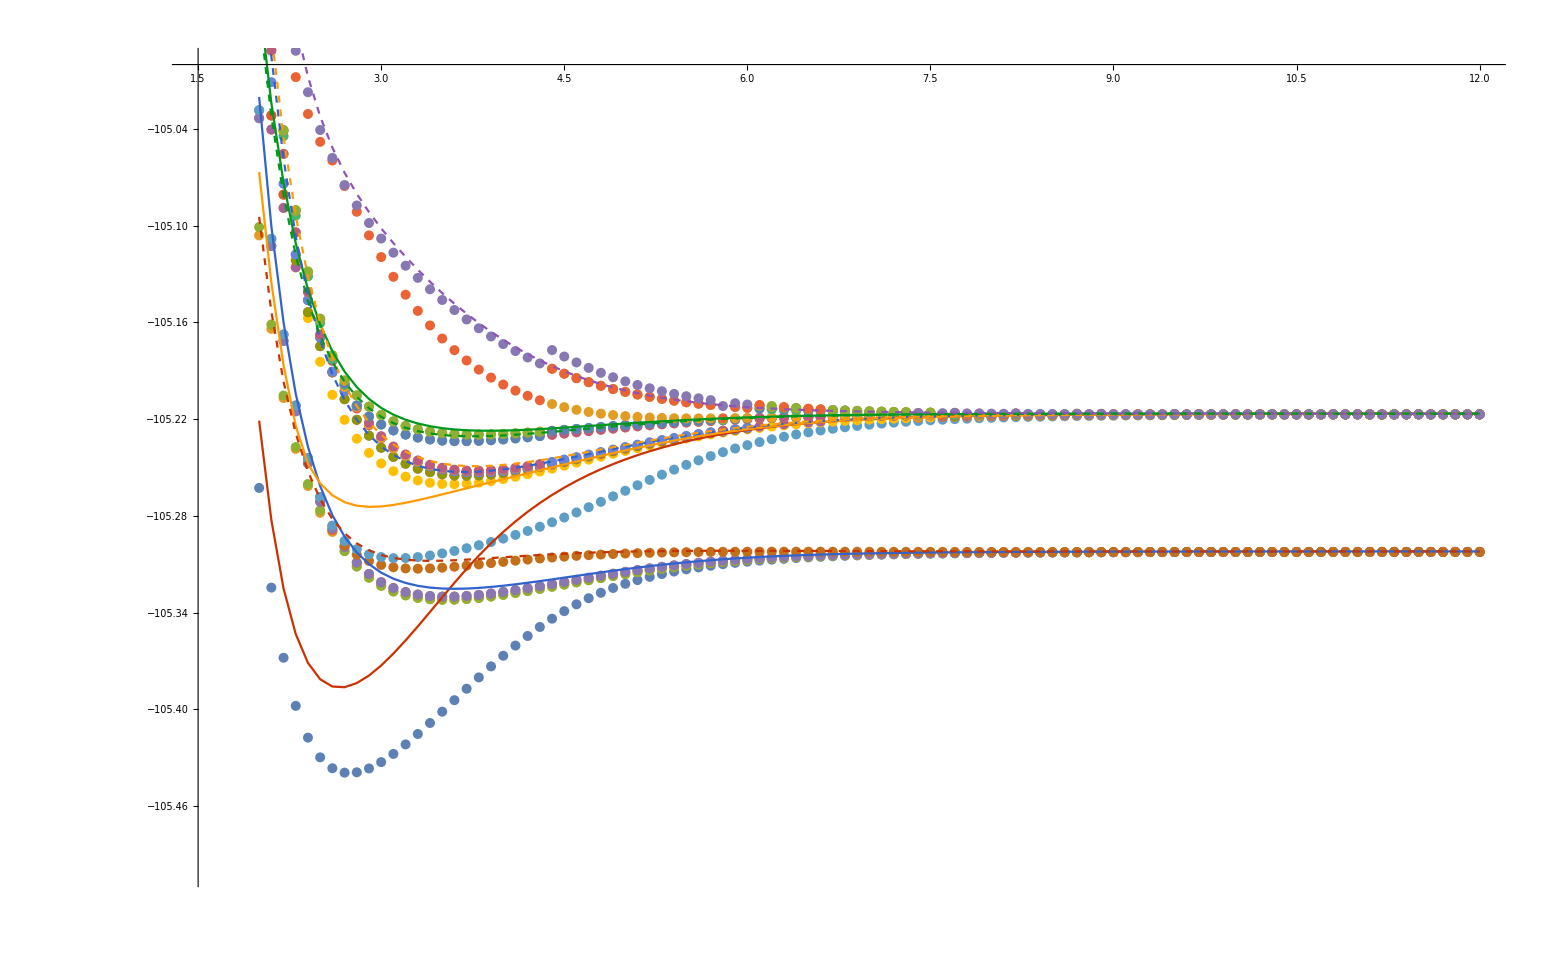

```mathematica
Show[LiFFCISTO3G,
ListPlot[Table[SSLiFsto3gSinglet⟦;;,{1,n+1}⟧,{n,4}],PlotTheme->"VibrantColors",PlotRange->{All,{-105.5,-104.5}},Joined->True],ListPlot[Table[SSLiFsto3gTriplet⟦;;,{1,n+1}⟧,{n,5}],PlotTheme->"VibrantColors",PlotRange->{All,{-105.5,-104.5}},Joined->True,PlotStyle->Dashed]]
```

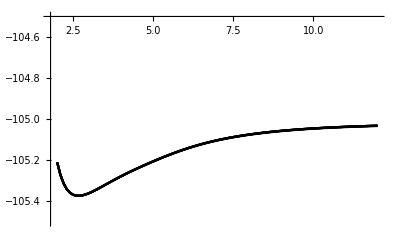

```mathematica
ListPlot[Table[SSLiFsto3gSpurious⟦;;,{1,n+1}⟧,{n,5}],PlotTheme->"VibrantColors",PlotRange->{All,{-105.5,-104.5}},Joined->True,PlotStyle->Black]
```

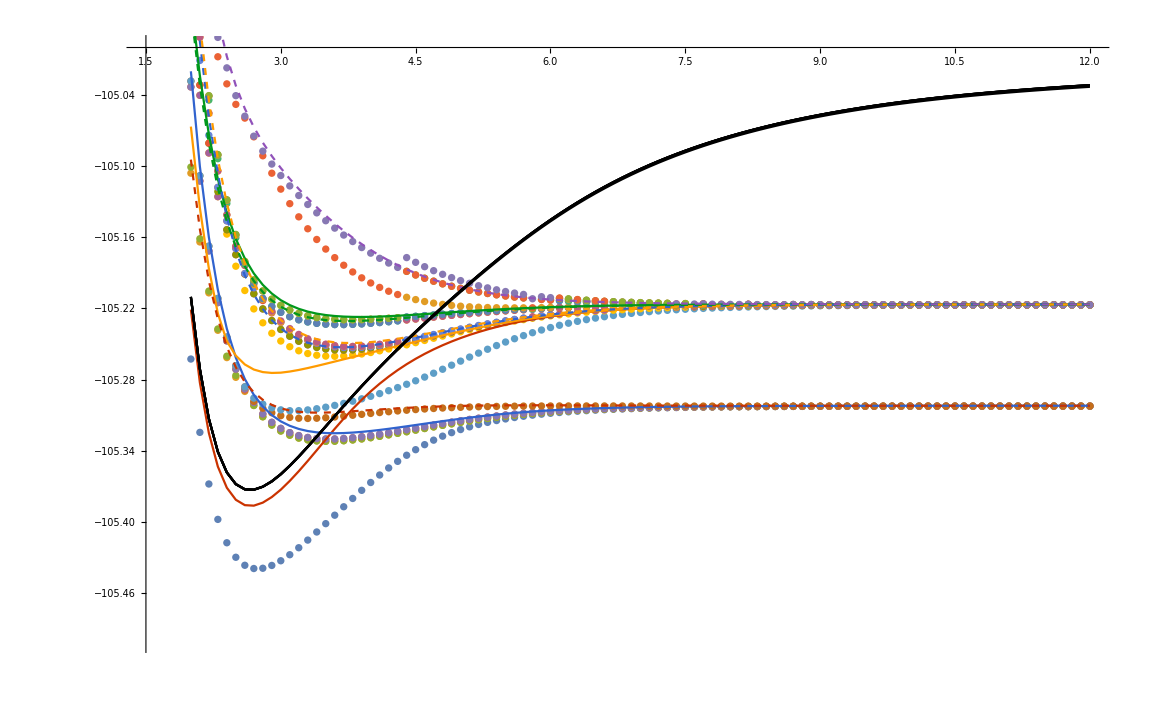

```mathematica
Show[LiFFCISTO3G,
ListPlot[Table[SSLiFsto3gSinglet⟦;;,{1,n+1}⟧,{n,4}],PlotTheme->"VibrantColors",PlotRange->{All,{-105.5,-104.5}},Joined->True],ListPlot[Table[SSLiFsto3gTriplet⟦;;,{1,n+1}⟧,{n,5}],PlotTheme->"VibrantColors",PlotRange->{All,{-105.5,-104.5}},Joined->True,PlotStyle->Dashed],ListPlot[Table[SSLiFsto3gSpurious⟦;;,{1,n+1}⟧,{n,5}],PlotTheme->"VibrantColors",PlotRange->{All,{-105.5,-104.5}},Joined->True,PlotStyle->Black]]
```

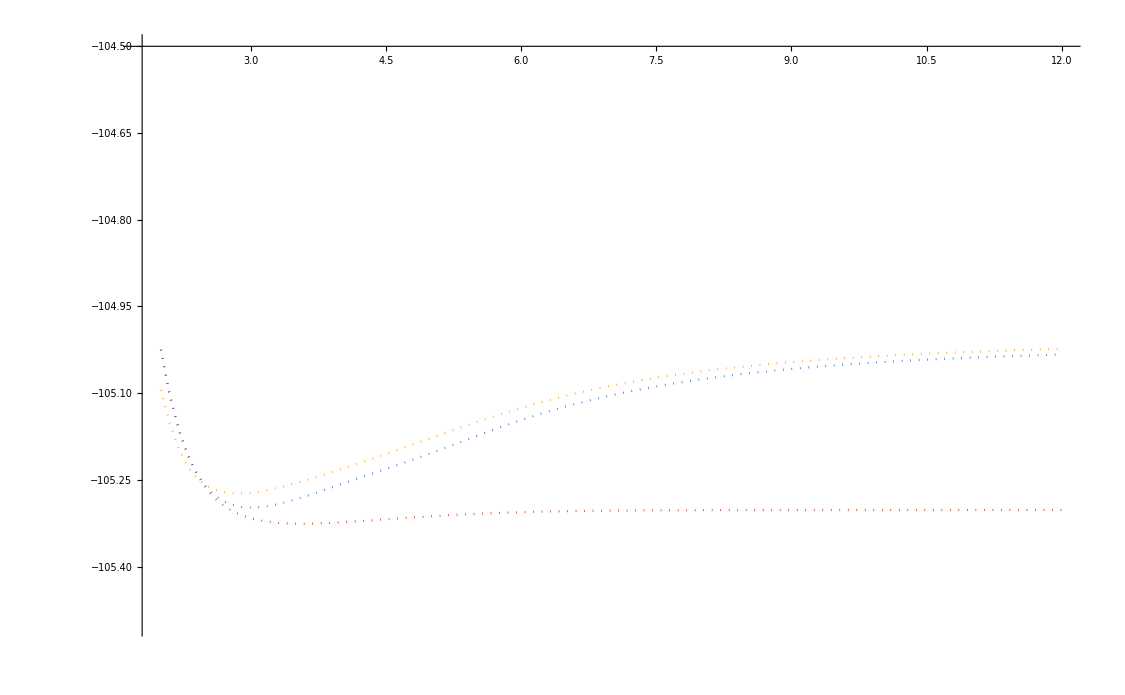

```mathematica
ListPlot[Table[SSLiFsto3gSb⟦;;,{1,n+1}⟧,{n,3}],PlotTheme->"VibrantColors",PlotRange->{All,{-105.5,-104.5}},Joined->True,PlotStyle->Dashing[{0.0001,0.005}]]
```

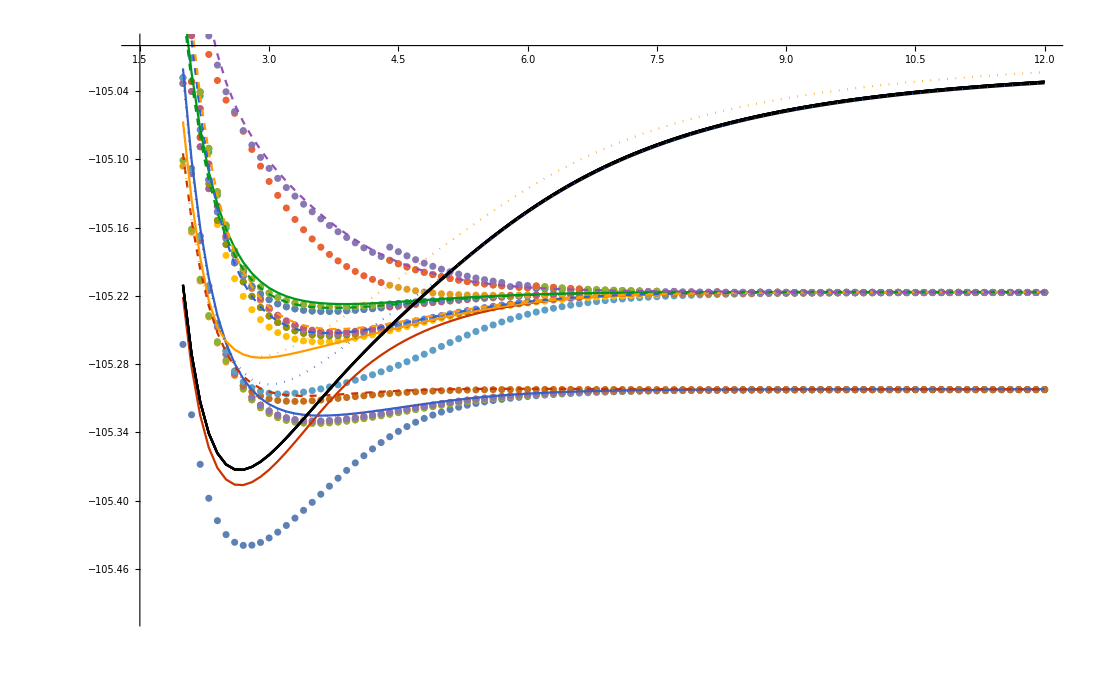

```mathematica
Show[LiFFCISTO3G,
ListPlot[Table[SSLiFsto3gSinglet⟦;;,{1,n+1}⟧,{n,4}],PlotTheme->"VibrantColors",PlotRange->{All,{-105.5,-104.5}},Joined->True],ListPlot[Table[SSLiFsto3gTriplet⟦;;,{1,n+1}⟧,{n,5}],PlotTheme->"VibrantColors",PlotRange->{All,{-105.5,-104.5}},Joined->True,PlotStyle->Dashed],ListPlot[Table[SSLiFsto3gSpurious⟦;;,{1,n+1}⟧,{n,5}],PlotTheme->"VibrantColors",PlotRange->{All,{-105.5,-104.5}},Joined->True,PlotStyle->Black],
ListPlot[Table[SSLiFsto3gSb⟦;;,{1,n+1}⟧,{n,3}],PlotTheme->"VibrantColors",PlotRange->{All,{-105.5,-104.5}},Joined->True,PlotStyle->Dashing[{0.0001,0.005}]]]
```

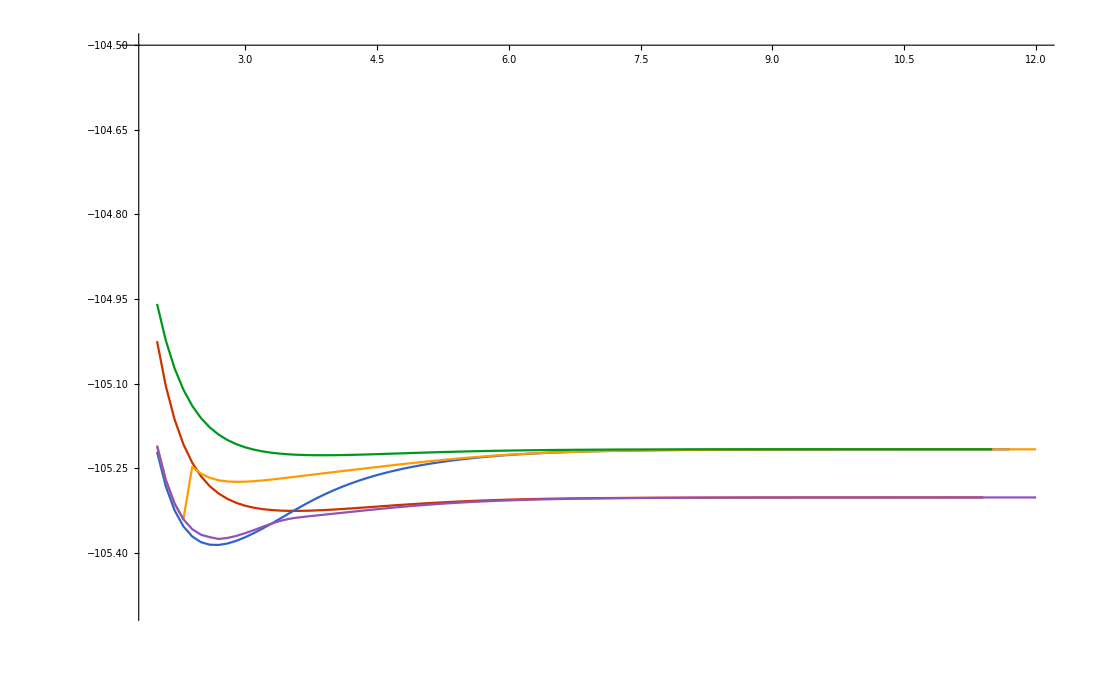

```mathematica
ListPlot[Table[SSLiFsto3gSingletR5⟦;;,{1,n+1}⟧,{n,5}],PlotTheme->"VibrantColors",PlotRange->{All,{-105.5,-104.5}},Joined->True]
```

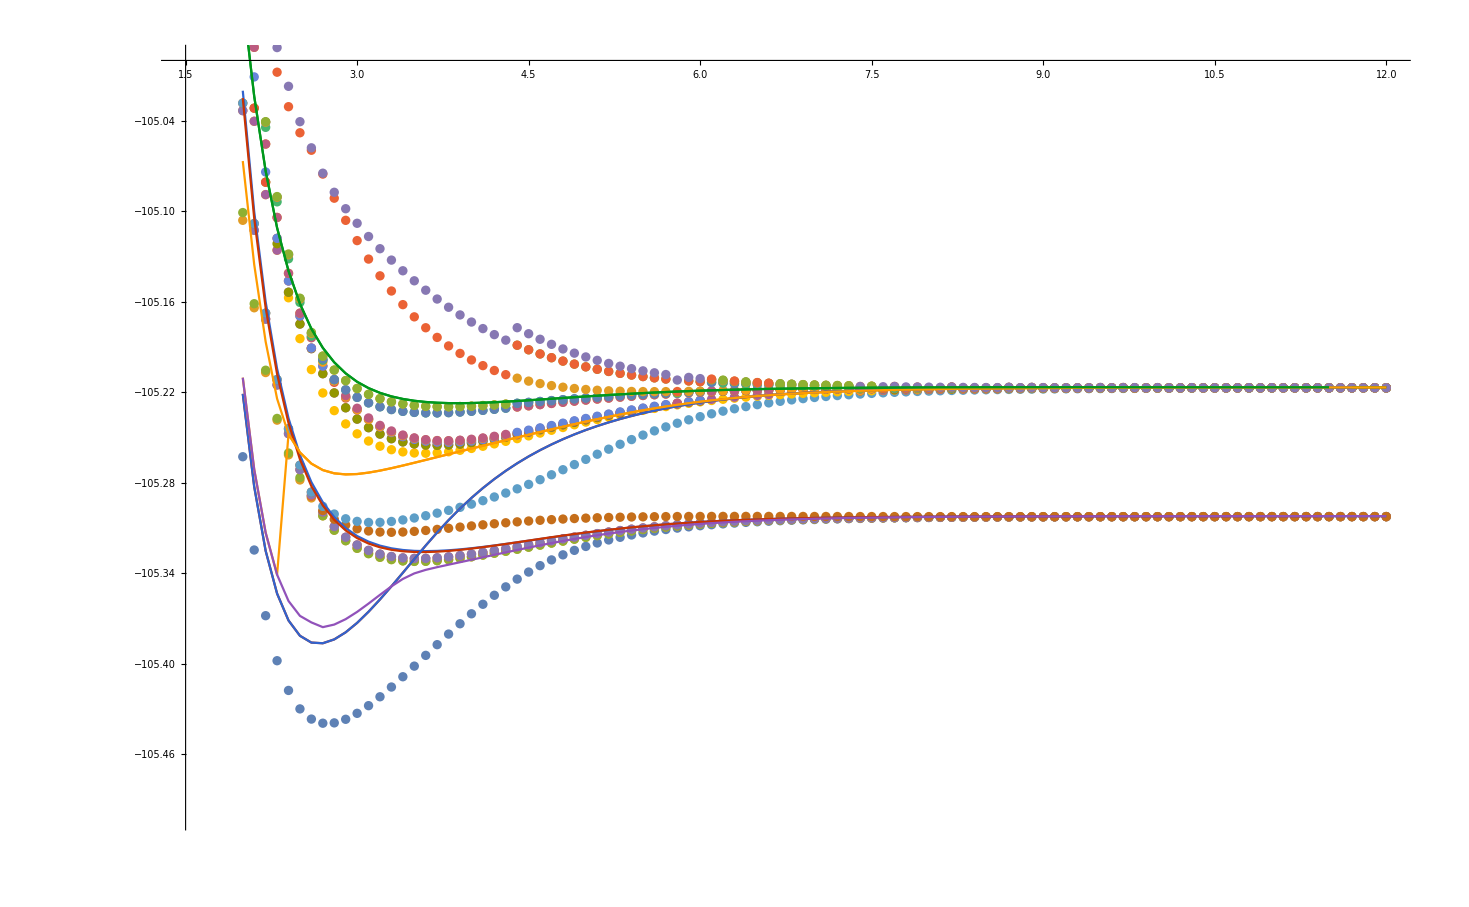

```mathematica
Show[LiFFCISTO3G,
ListPlot[Table[SSLiFsto3gSinglet⟦;;,{1,n+1}⟧,{n,4}],PlotTheme->"VibrantColors",PlotRange->{All,{-105.5,-104.5}},Joined->True],ListPlot[Table[SSLiFsto3gSingletR5⟦;;,{1,n+1}⟧,{n,5}],PlotTheme->"VibrantColors",PlotRange->{All,{-105.5,-104.5}},Joined->True]]
```

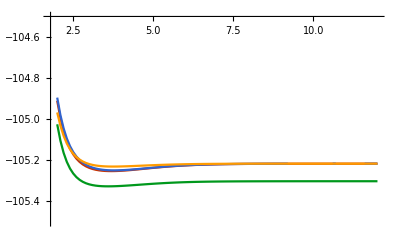

```mathematica
ListPlot[Table[SSLiFsto3gTripletR5⟦;;,{1,n+1}⟧,{n,4}],PlotTheme->"VibrantColors",PlotRange->{All,{-105.5,-104.5}},Joined->True]
```

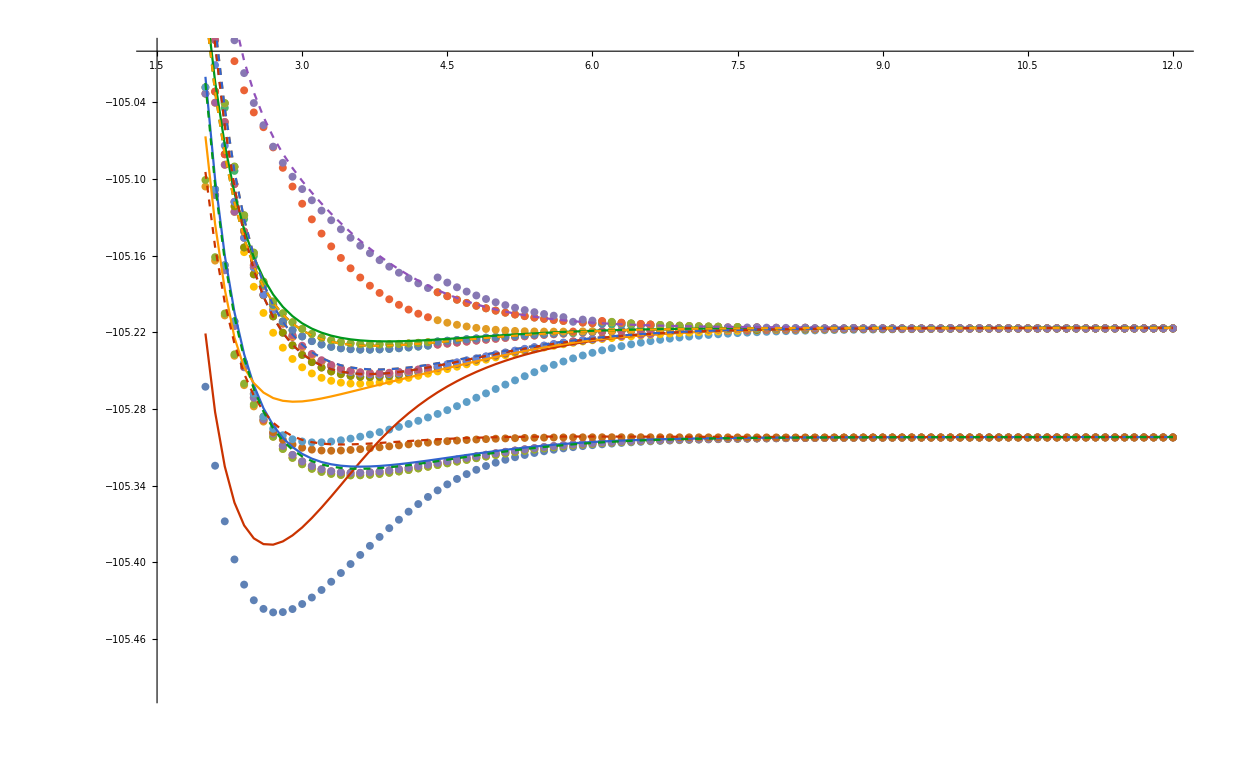

```mathematica
Show[LiFFCISTO3G,
ListPlot[Table[SSLiFsto3gSinglet⟦;;,{1,n+1}⟧,{n,4}],PlotTheme->"VibrantColors",PlotRange->{All,{-105.5,-104.5}},Joined->True],ListPlot[Table[SSLiFsto3gTriplet⟦;;,{1,n+1}⟧,{n,5}],PlotTheme->"VibrantColors",PlotRange->{All,{-105.5,-104.5}},Joined->True,PlotStyle->Dashed],ListPlot[Table[SSLiFsto3gTripletR5⟦;;,{1,n+1}⟧,{n,4}],PlotTheme->"VibrantColors",PlotRange->{All,{-105.5,-104.5}},Joined->True,PlotStyle->Dashed]]
```

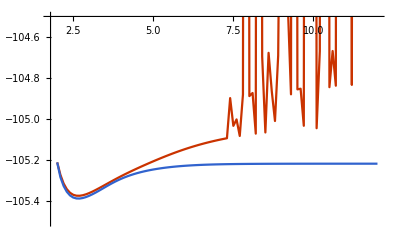

```mathematica
ListPlot[Table[pySCFSTO3G⟦;;,{1,n+1}⟧,{n,2}],PlotTheme->"VibrantColors",PlotRange->{All,{-105.5,-104.5}},Joined->True]
```

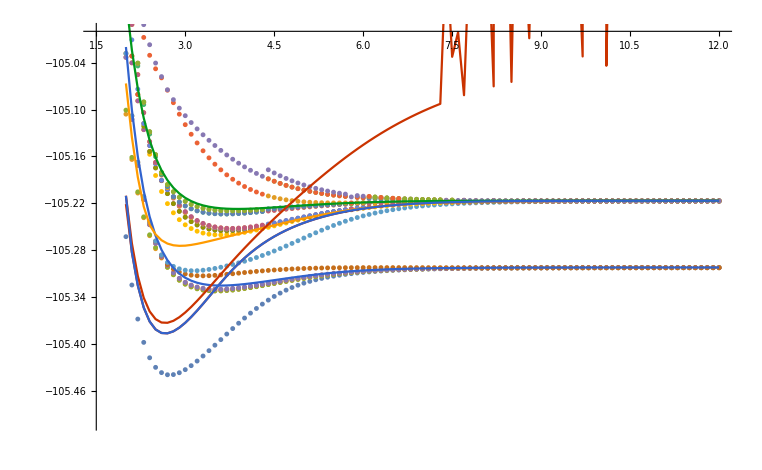

```mathematica
Show[LiFFCISTO3G,
ListPlot[Table[SSLiFsto3gSinglet⟦;;,{1,n+1}⟧,{n,4}],PlotTheme->"VibrantColors",PlotRange->{All,{-105.5,-104.5}},Joined->True],ListPlot[Table[pySCFSTO3G⟦;;,{1,n+1}⟧,{n,2}],PlotTheme->"VibrantColors",PlotRange->{All,{-105.5,-104.5}},Joined->True]]
```

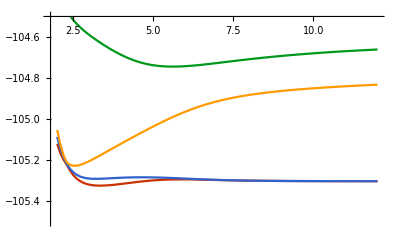

```mathematica
ListPlot[Table[SALiFSTO3G⟦;;,{1,n+1}⟧,{n,4}],PlotTheme->"VibrantColors",PlotRange->{All,{-105.5,-104.5}},Joined->True]
```

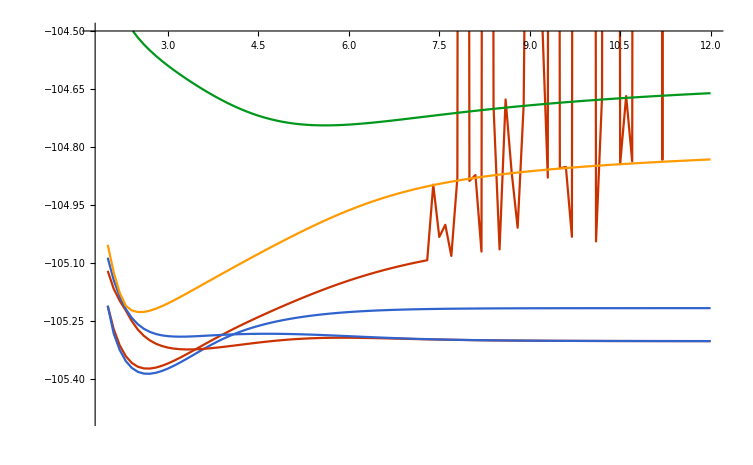

```mathematica
Show[ListPlot[Table[pySCFSTO3G⟦;;,{1,n+1}⟧,{n,2}],PlotTheme->"VibrantColors",PlotRange->{All,{-105.5,-104.5}},Joined->True],ListPlot[Table[SALiFSTO3G⟦;;,{1,n+1}⟧,{n,4}],PlotTheme->"VibrantColors",PlotRange->{All,{-105.5,-104.5}},Joined->True]]
```

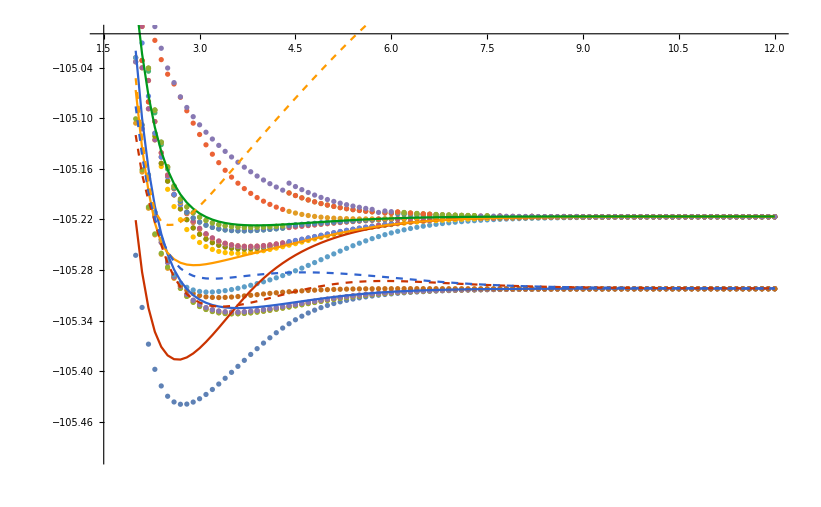

```mathematica
Show[LiFFCISTO3G,
ListPlot[Table[SSLiFsto3gSinglet⟦;;,{1,n+1}⟧,{n,4}],PlotTheme->"VibrantColors",PlotRange->{All,{-105.5,-104.5}},Joined->True],ListPlot[Table[SALiFSTO3G⟦;;,{1,n+1}⟧,{n,4}],PlotTheme->"VibrantColors",PlotRange->{All,{-105.5,-104.5}},Joined->True,PlotStyle->Dashed]]
```

#### STO3G Clean

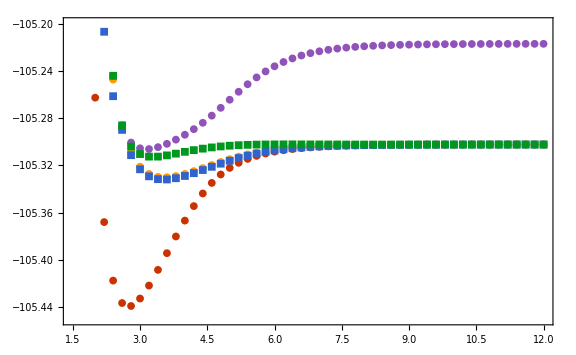

```mathematica
LiFFCISTO3G=ListPlot[Table[fciLiFsto3g⟦;;,{1,n+1}⟧,{n,{1,2,4,6,7}}]⟦;;,;; ;;2⟧,PlotRange->{{1.5,12},{-105.45,-105.2}},PlotMarkers->{{"●",8},{"■",8},{"●",8},{"■",8},{"●",8}},Joined->False,plotOptions]
```

```mathematica
PlotStyle->{RGBColor[0.790588, 0.201176, 0.],RGBColor[0.192157, 0.388235, 0.807843],RGBColor[1., 0.607843, 0.],RGBColor[0., 0.596078, 0.109804],RGBColor[0.567426, 0.32317, 0.729831],RGBColor[0., 0.588235, 0.705882],RGBColor[0.8505, 0.4275, 0.13185],RGBColor[0.499929, 0.285875, 0.775177],RGBColor[0.12490296143062507, 0.63, 0.47103259454284074],RGBColor[0.823948950768196, 0.29474475384097976, 0.19291741323314934],RGBColor[0.42126358105951733, 0.33224185136428963, 0.9],RGBColor[0.7239916650994997, 0.6554435183443889, 0.],RGBColor[0.6746366424582266, 0.252, 0.45055901160272827],RGBColor[0.12582006271512805, 0.5293439498278976, 0.7809840752581536],RGBColor[0.8604677779867332, 0.4773388899336664, 0.10673699943582014]}
```

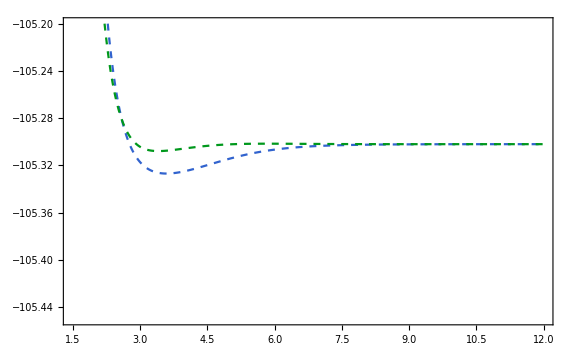

```mathematica
LiFCASSCFSTO3GTriplet=ListPlot[Table[SSLiFPlotTriplet⟦;;,{1,n+1}⟧,{n,2}],PlotMarkers->False,PlotRange->{{1.5,12},{-105.45,-105.2}},PlotStyle->{{RGBColor[0.192157, 0.388235, 0.807843],Dashed},{RGBColor[0., 0.596078, 0.109804],Dashed}},plotOptions]
```

ListPlot::ioproc: {{2.,-105.025},{2.1,-105.105},{2.2,-105.164},{2.3,-105.208},{2.4,-105.24},{2.5,-105.264},{2.6,-105.282},{2.7,-105.295},{2.8,-105.305},{2.9,-105.312},«91»} may contain non-machine-precision numbers, complex numbers, or invalid entries.

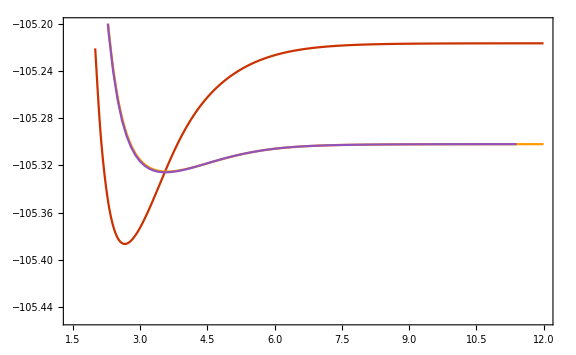

```mathematica
LiFCASSCFSTO3GSinglet=ListPlot[Table[SSLiFPlotSinglet⟦;;,{1,n+1}⟧,{n,3}],PlotMarkers->False,PlotRange->{{1.5,12},{-105.45,-105.2}},PlotStyle->{RGBColor[0.790588, 0.201176, 0.],RGBColor[1., 0.607843, 0.],RGBColor[0.567426, 0.32317, 0.729831],RGBColor[0., 0.588235, 0.705882]},plotOptions]
```

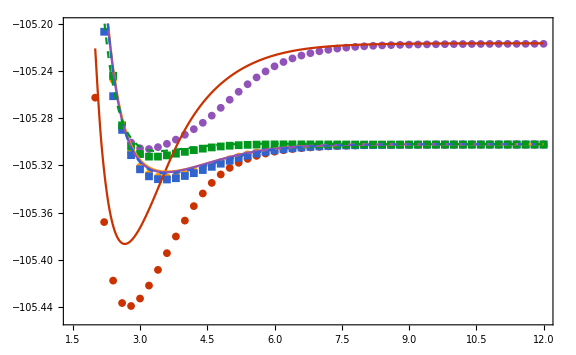

```mathematica
Show[LiFFCISTO3G,LiFCASSCFSTO3GSinglet,LiFCASSCFSTO3GTriplet]
```

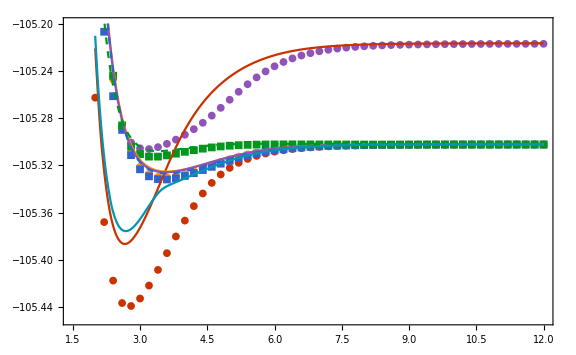

```mathematica
Show[LiFFCISTO3G,LiFCASSCFSTO3GSinglet,LiFCASSCFSTO3GTriplet,ListPlot[Table[SSLiFPlotMin⟦;;,{1,n+1}⟧,{n,1}],PlotMarkers->False,PlotRange->{{1.5,12},{-105.45,-105.2}},PlotStyle->{RGBColor[0., 0.588235, 0.705882]},plotOptions]]
```

#### 6-31G

## Dependance on the size of the CAS

In this section we want to look at the number of CASSCF solution as a function of the size of the CAS.

#### HF (2,2)

#### H_2 0 (4,4)

#### N_2 (6,6)